```mathematica
SetDirectory["C:\\Users\\ICT_01\\Downloads\\Lab4_2017"]
```

C:\Users\ICT_01\Downloads\Lab4_2017

```mathematica
T1 = Import["Image_1.bmp"]
```

-Graphics-

```mathematica
ColorSep := ColorSeparate[T1]
```

```mathematica
Tg = ColorConvert[T1,"Grayscale"]
```

-Graphics-

```mathematica
Export["Image1_gray.bmp",TG]
```

Image1_gray.bmp

```mathematica
CRed = ColorSep[[1]]
```

-Graphics-

```mathematica
CGreen = ColorSep[[2]]
```

-Graphics-

```mathematica
CBlue =ColorSep[[3]]
```

-Graphics-

```mathematica
T2 = ColorCombine[{CRed,CGreen,CBlue}]
```

-Graphics-

```mathematica
T3= ColorCombine[{CGreen,CRed,CBlue}]
```

-Graphics-

```mathematica
M3 = ImageData[CRed];
MatrixForm[M3];
ListPlot3D[M3,ImageSize->Small]
```

-Graphics3D-

```mathematica
M3Image = Image[M3]
```

-Graphics-

```mathematica
{T4 = Import["textoB1=Import["baboon.jpg"]
(*GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJwsuwVzLPl+pnnGY4/t63vt63ZzHwYxloqZmZmZmZmrVKgqUUklKjEe4WHu
cxpvXzSPdyYcuzG7sd9js3c34q+KrJRKqsx88v29j0K6Y/QJrX927dq10F8B
D0JDjBAMGhKiXwNPJN6Qw+a1mBnesMVmCcKN/xXY+b/+/4+ftz1WkEHZpxTe
Y5E+MasmshG2mN2/tx6Vi0aphC/kouGDnTCPc2O1azYbx8slpt8/odV9JZb9
ulTBRRLj03WcxvxZY57c7jDnu5yjC/vWoX7zyJyvU7dPnIkSlS67XVs1iS3j
vYu4NUZiawa1XlxjzfXwdWsc9xFTMWaPsU1Bhi8rwXL6FndT+TlHesay/3Q2
P+dSuZlLh+Wtx52ZnWLv0XJuObnwcCExnxgijYZmotm1cvNo3l8PL5wuQ7gI
eUAN5cKNSTOEAxO7pZWNablXxjHQpU6BPW1yZi3Rmvf4/UGsk0coadP7HaiE
UjlYTq42Ygv13svL+n7PXkpnu53K1oY6HJ7u9XzV6giVkl3pLj95VNjcWLy6
mOQyb2MQ9ulCsrtY3tmIL815Z8p8r1WbDqdW58u7awybTh51oxQCukWvTsRM
uWJkrutvLaFkxuzaQe/1t5ZSk2K26XOF459+qJ/sZza69nI1291obh2ytBZb
PBfMVfkqw+7p41SxdvLoaanZLtSbR4+uMtXKy++/XTvZVzj1jkwgM1/xFKLR
Rs4Uc2v8zmSrKnNa7alYerZVXFrECQRKt3u629UEQ45KI7m+rUnnlp+9zK71
pMFIprsCEwgxQtHs/sHM5ubc7u7pm9erJ8eJanXz/Dg1k45UQoGi//jVUbQc
yTTTgZzfn/V4U85Q3h3MOuVmNlOGKc4GHr5YXT+svPhwUG0Fupu59lLo6x93
rl7ObhzEXRFSJMf68Lul85f5VIW7vOOY3zDvX8ZW93y9k1RhxtA7TC1tBhpz
xrll69HD1OWTwvc/LWeLfJMDRWJdN7twwRRX58QHM5L51XDACaXh/tZthtDx
H2nEgzTsJ7c+u6aTTYh5g1jE31Pwn755UWs1lVr14M62M5el5HI4o+nW1q7m
7fv4ybkpGB1xh/pg2GtY8rXenqIxzwompmaWhL44pLUs278IoFkfdY+D+gAq
3ZIFilxfnk2X97vTnL0nFTz/ns5L6p0VZjcjpQVHqmHiaWEnrzqtXvzFb/bW
z2qxmjU7H5jfr6xfLh6+25H5JMFGUOKVu8o+VzXgb8ZNWZc2ZuZYBfXd1sqj
DVfRC/DpKLgKq6VYKy5yCE1RPVNLWX44r/bLnGnzKGmktFVfe3FQ2Jyp7nVk
IXN5e8GUCW48Pw23p/XJAFUjM8YjllRCEwoYYhG6Vs006U2ZpC4eEfuciqCX
olcJXbbGwSZNr9TEfSgJu76/TtKIt99e5dfmA62CrRSjGCQcu4HntHiqtejs
YqKzzrb5/c3O4Xe/N2TL+c3t8u6ub7YRX10Q+J04ldpXm1l7/Fzq8itdwVRj
lsgRSQ0WucFKE4j4SlWru2xwOW0hnysW0XrsUCaOrhWWV1qHbx5nF+qZhTpb
pzDGgrFGReq0E8RCJJej8nhWzk7JUjldoxd4g8ZSLbHSm94/ym1sz59flXs7
NIORbTAevH5TXul2Hx7TZNJgsbB6dDTdaWXa2dZmM9lMeHOeQdjA0l4n384d
PdvXe1SpWrjQii3t1IuzkW/+dHX8rBtIq6M548HpbK5iOzxvnj+bO7yY3jxK
djbdh1fp19/P1jtqgM9cQ7i4af3T/9iZW7PO93z+FB/g8+pVI10UmxyIs6vs
3lEkU+DJVIMOHy6W4zuDJLkB7AgzNHYMiX3LZQJFPGgs9C+BFLUbIFLeAzbl
Kxb5SyHnAWTiv40OX5suCU+OwhDwNYDPdlt4eGxLZRHewMif/rmxd6RZ2RCm
S1CR8lcCxd/unep//GMVSFGp7np9gSfR3jK4xhxx3OZl3JOlZWflczuuSEVI
lT44e9tcPowBWdo7z7tSXH9OvHVROn09Hy6pL75eWzmZbm4ko1VbsuFZv1iY
2Z5eOlvYerYJsJddKqgj+srWjC5p06eclrxP7teDWPBxKjgyk5zZm4fzUIFK
aPv5TnGlhBXjNi7X5S5JrB5ypCyenCPWCFc3G8n5XHN3zl+NybxagU1piDhs
KZ8zG5K7DUqvRWjVmCM+ayzwADqhD3lEVj1DK8PwmVSVUBt0iOw6sV3nKkTG
SfDcUq2wVJe4tCgeaYgwydaLs0vTvkqUa5EIbCq+RZ1fXswtLbYOjrLLa8ZU
PrO8LnT51PFErLNQP96tH2/TbTpndZqgUsfmF3Sx2PTqmjEcpsvlzni8vbam
cdgCmZTCbhIZNc5U6PpoP4iKyXWaU0y80mfFy3h0jZSilrL0KlMiak3GE7Mt
plZzFwav9zblHi+YxkotdhtH55HlnrU88/p//O/V/Yczx2cXv/l9amkZiNCl
h6fF5SXghTcnxxlqeWd/J1hKabza/Hx2bqet9amNft3y/uLGw9WTF4f/8n/8
sblS3r9ae/3jxYc/Psk2PYub+d5x7eTxUqHqimV1r7/Z2j+brsyaHz6pqK3g
QIoWK7CT05z2qqHQlHZ33GrrZKEpe/J+9vRFPZIVlGY03jA5kmYotSPddXtn
xXJ8ljx9nMvXZGY3RmtDepNsgWpw98w3MXCtmGSE3Rge7YuNJZuMf7+Q5NLw
H5v1U343ZralTiXJjbqAxfo7LvfXu7tGp3v44Niysi71h8ZiyamFZfbxhfno
wjC3wqFw/rzUIB+c2VXmO+lpslhz0+IDaT2g7nFgcd9DEt9Y3PeunUbKSwZj
kLCwG7j6MD+7FbTFmM4E1xSkFeetlWUfW4N69buHs1vFcNWRaoUWDps8C/fg
3cHW893u1bqzGCRq2GybXBo0SYPmxFLVmHQrg8ZJOlwTNpfXm7F2OtJIvPjD
q/WrHs8sYKgZx2+OyBJiaiaxsDe393SnvlH3FQKLB0uJZqq62nRn/SAiZJIA
vjfVJ7OpBxFjTCXPFnYZvBYCl6Ky67Res9ptnCRAE/VsuJxwpwO+XFBolDCU
TEPQSBAS707dU3tUSBZCYhXH6zGZUxoo+81R6xgRSpbztCGvIRImSBUCq0Pk
8kh8fqHb5W/Vlp6c+mbLn8FGsr2uMZeiGPWTLDpFpZA4bOZYpL6xkp9rRasF
qkwApRGQXMokBW2K+2zpULQ17a+XWGbtCAXHNOmMqdgYjUw3aIGcHyaRxG43
22yNtuf4dqc5nU8vrTkqbUWytHD12l5pb7/7Ib60Hp3tJBY7q4+eEGQSSyLG
NqgD5Xx+seXNJZLNwvt/+rq2WhFbhO6M8+DJ7t6j7aW9hfM3D4EUVdpE5bnk
xslstGRTWOnpqm3zpP709ebl8+5yL52vWuZXgz/8aW+6bdi/SIezTE+MONPV
AbNeaR5vr5hWdj1WP3p23dXs2opN9eZxtNpWmV2wtx9asx3tyXny+5+Wrl6U
KJwvUyVhZVaPYXzRXjHPranAI9c0kj6XGSpgXn9+WTjY9JdyfLN+spTjpRPU
87NoNIKu1pmXj/z+0ES2gBVKPsqX8NM1UqlCOLm0bR+qw8mJxVXe7kPD4YXl
+LGrtsCpzLJ9cdj2Q1etIy3MSZaOPNNdzavfzxuCKHuCJLODppeNcjtMaoVU
u3Yc7zZZ3L9xllM40L6c3F8wdE9mtx51T97teguu3FLWnnHGZ1MAfssXm67p
uCrmyK61c715Qy4iDVpL621dxN493zYl3EKrMliNmxNOpU+/eNBNtTJgCuQB
9L49YcNw0Z6se//ZntatiRbDtpBF61SX54qVhTKWidY4VFKj2JfyPZh8MAQd
4ql4FAFFbVfLTLLp+dLMSoMqJAez/nA+6E26fWmX3qNWO2RUEYEpowSybr1H
MYEZlJn5Jr+ao6ZYwhqBkUeWkGA0NJxBGMFhCBKxNZXmWq0IkZBrt7DsJqJB
oUr5yWYFSMQ2FFM8r2OCQ1dFAwSlmG3SgGhEoFiGKnkgwIHcTsxVVEH7Tfgo
y6KG8BlQAZukUZK1qjE6JTbfXn3yWBOLAsuczZG1utzKBjDKs931cm/XmCn7
msvScK5x/KR1+qy0fVzcOgg0ZlefPPVV6wDYDz+8Wz4/Ss7WLMnACB5WW2tX
Vyrhknfv8ZYtato8WwdaqDmgVzvkxVa62S3N96q+tFFtZWXrruWdQiSvff/j
kdHBtHk5r7/t/fino2bH8fKbTqIk2D2Lf/fHla2TMJCfzz80L16WUtOCs+fF
N7/pPvtmPl0RJ8v85Z7j6CK+0rO9+VB7+a66tuVwBdHtrjFbEeEYn4VyPJF6
VCB/gIf/goL5Owbx405LF3RhagVRfVoy21QBfL57W15b1e/vWy8f+wAggf75
9EUwkUakc+j5jkAi/4f6LG1pXbS0LphuEbePdY9e+WeWBZkKqdhkpqepWyfu
1z/WLt4V6+u6zato98Sn8yMIwq8MQbQ5gtt7mp9eMmda2mRD1d4MtHp+GO3L
UEmN4YCqq6WtxxvReijSjCp9arZJAExzdzkaaGZ/bnp6WWypxXWbgSxylDP1
7WVt2B6bKYXqGaXXZIq5Vs93k+0imIpka/m2mJMkJkssco6Wa084PCl3fibf
XmmFsyG1VcVTcKF4iMIkJ7DwZC4JS8eoLEoyn+xLeNlyttVvAZh0Re08FQfH
RE9ixoehAzDyFIGNHkH0Y+gwGBlEExIAPl0xE56DsAQ0eC4MQRsjCuFYDtyR
tCtcOoFFzTcZ5g739ZHoJIsNEwtZTgtKJSUYFZKoJ7+/JokHtIXkEJNCNKiy
68vykFfkthNkYkM8yDKq0SIWx6ZVRdw8p8FeSaOVQm0qFp6fNWTTPLczs7qm
iESB5sB1umylMsNiL23tOit1pFRZPzhJLq8F2p1C7yTXOw7NrqdX9tZfflBG
0tpY+uKn326/fOmplJbODhNzNUPUY4y7DRFnsBwNTwcPn23ztKzSQg7g0xo2
dXbmhDrO7FodQPTw8Uay6kmU7LGicfe8WVvwJ/KG48v25kHJFxPK9YjlrbDa
Aj+4zPzmn3sLG7Z3v1l4++P8k3e1y1dlYMrvniX3r7ILm27Am5a2nJkydxRy
LV1guPzwZI4WTZHyVYErjInlWZmqyJ9mSnSjRjscNvHnAJaTQ9fwiL/ZXHNy
GF+Q8L+yGEd7G+bNTWO7zQeAXFoRNWcpBMq1x8+8e8eWWBohVX1eqBIAPl+9
j3U2RKkS8uWH2MOnrmyNpDTdpgl/vbSln1vTrB3aty5ChUXZ859mth5FGhtG
YxhpixPKS7qVk0hzw97quV0p5uJeeO1hCrAnf14hsrCsCUt7p+0v+TsnK7Ve
e2Z3iWmUWDMhwGgSnZa/WUksL1BNunh3ITw/U9vqNre7MqfZEHEDPEzR0MaQ
K90q9cNGVS49TyceQo7KLSoUA11dqmlcWpVNozCp0FSsO+odR4IeTAyQuNRB
8MhX/TewTLwz6i7PVxc2O1ASgsynouhYKBEOwk8BoUrgEaFEKFvJEuuFd8Zv
D0L6VQ75CGIAuJp4DookxCGo4CFE3/WxT1k6KkvLJEgpCB7Jmom4i3l3pZpc
7JKNZqLBBFcqRgU8YzVvqBfWv3sdWJ4NdNqjHGakM5vvrZ7+8K23Ni3ze0hq
haOYq+9tc102cyGtzyWMpbSxmPE066WdHbrVKvD5tOmsLpPDaXTAo6fZ8rfm
E8trXJfPmCtl1jY7j57tvv+hcfgo3tleffJh4fylJV/fePbaki1mV1bnTg5d
5bwtGzWnAlK33l2MLJ9tTa/Vi4t54P4yBTWZmRhfw+KpmZ647eLVcb1T2jnv
ru3P1BZiOOaIL6lsr0TXD0pz3ejscuTyeSdZVDmDjHbXObfqXNsPLmzYAUqb
S/rijOz5h5njx9nuju/kSeHZN7OhPGt21XJwmTQ5wcEkobNq6G4Yzx7Fvv6u
fnwVC2eozY6udxRqrpgMLmg8Q9HJR6I+klY2SED+kkr8iE75KBrCajUPrNah
58/jfNGvl1fF5So+nYfOzJFLVczOoWnn0LzQFZsdffVZRqVNAeDcOdGXWuS1
fc3RI3drRRzOYaYw12IF8uN3heMXaab6tjONj1RZj79vlJZUGi/syfft7/5t
Gxj3AJ8hoHgs29IzGiBLc7PO6mpB4VYkZ9KujEfqUis8hvPvXqxcHjR31+q7
GyKvI7uyZC7kvM16bGlRnYgo/E6J02RPRW5MDHEMckvCP4gEIVkkoVEus2n4
eunnAzf6wUP3J/sncSCBVhxIR+Um3Wd3b+JZNJ3LxpQKRxGQYDaptptxXJrc
ZpRatGqX1ZUOo5gUXz4OJqGj1dwYBjqOhyOZeK5OIjDIUBwCgoEliulfDF63
xBwwGnIQNTqGnRzFjYMZUJQQC+ViJ+iocToRp5BSjRaa2c73hdWZMsZoD6yu
2+fmHIvz0e2NzOH23NPHHJ83uDCvTia33rz1NWcy3RVtPIEWSwvrG1S9QZ/O
uBs1a6XE8jrJZtMYmxucW0ivbeC1ekOu0Dh+OPPwrHZ4vPz0eWa9F55fquwf
2qfr7sZMamWjtLW38uRtcmGzsLpXWj/ILPeqW3tL55e17e3ly9PuxbGnnLz4
/qU9Gwg1klNM5AQFbAzp7TFjsOAO5F33J28xpOTt07XV/cXn315ECi6zV7qw
UXj53cG3fzyfXY2RuSOtTujRy+WN/Vw4LVndiZdb+k7PC6B4+WraFsAwxbeq
8+qnXzeAp7Ortjc/LC5sOd//ods7CjaXtQdn0bkVXTiBe/Y6/+h5enXTTOd/
prOP755GjW6Y1DSWqfHbHTmd9AWD8rlJN0HA/G2rrlDK7lPIvzw8cE9NXbPY
+koVklr3JZCW3Z5Irv340QvfSk959si3dWistBhzXcHRhb3YIGw/NBw9cjaX
uM1lwd6FM14i7F54sw32yYvk69+2gfxkae5x9X3/r9Q721uOwxeFrat0oMBP
NdXBoijV1OJ4d6MVRaxq9OfsJ68fNnutYDmME1OIUmZptTV7uLF6dVzaWJ59
eNA82DXmMsnuksjnv4/FqP1ecywE1DZrIsTTK5ePdiKVLIDo7fEBVyrgTvij
peT0Qk1p0yQracCDZCYDgkKxR6MkgQDP5Qr1ems0ytfr7clkdW1l+fhY5fNM
kEkTVBKISgEzaRNkojro4wI6QyOPkwhoIc+WjlV63SEcUh/zoQVMCJs8gAFL
3EaF10JWCSACEskoEvrNUAmPZDJaqnVlqpjbOQ0u79K9Cc/SVuniWfPFa8/6
+vSTR7t/+uPiixflvYPlZy+6z17EO11zpuDIV0pr25GZBUMyB+NLeC6fIVtk
OT3afLG0e5BaXc+u9YCBfvG7Px59931ssZNc7k7v7AJ4p1dW2w/Pgbl/8M33
jcOjztWT5cfPZg/PbNkKTWtOL65G2wuWZMacSAJHVFxdnF5btGeDqdkS1yQm
yWk8s0gX1KldUrkVEEa9yi6Gk0CldiZWDNQWi7lahCnC2nzyrePW6u40lTcB
IHr2fLEx7+usJ65eLr7/zeb8mu/k8fTGQfT4cT6SY1l8qFiB09l0Vua0tQV9
7zAG1OHOjnvjJLxzGj24infWLfkajy/5ikT/W5N9jML8tT+OW911eGPEdEVw
8ryQrYlmu2oO/SYc/JcCzm2zfgLgs1hg4bD/rVplGUz3Pb6xr7/Jnl+58hUs
YEbFGj6cBAP5uXdsPThztJcEWsudrUP97pklV8evH2hjRYw9NP7k67Q/jS60
eAdXYW8al6hxjl/nwxW2v8DMzSmAIppoiM+/bjgSdBjtc50Pz9VOFhcsrhSX
rwMXFzww6vjy0VLvYtOb98ud6kg9U1xu4iVsdcAp9dg00eAEkyYP+og6jbdW
5dls/nIRxWU6M7Fyd17pstAVIpFZ7c3F+Dq5JxNyRD04NmkINkqXsEw+ywBk
BEzCc1QqTyYjsViy7Xa80Wj2tpReny2VtiRTfIu1sLpuyxU4NvsEkwW0R0Mq
DfgvkGaDJDKwE8Ljy4MhUybNspgb+zssixFwFkXID3TI5uGOIZtQZ8LCqJvu
svACfn4oVj55ZKouJrbOiicvyxdvpy/f1Z99nTw6r79613zzLnV0XD89P/ju
h6PvfvRWm7pYqr59GKy0xknMUQJzgsaTeCPWQq318Gr+6llooZvZ2KruHUbn
5ivbO439g713X4fbreLGemF9beYQuHn3A80GsAGokyGV5DsdlkzGV67aUzlr
IsPWG1o7u4nWjC7oLy3P+YppjkHqyoUcWV9jY8ZbCi6fLCvccp6WYfDJl3bb
pbm0K2pprVSz9bhIx5LpWQaXSG/nh9KGYEpbaDqevd/YO29UWi6ZDllsmI6v
qqdP6/m6UmWGrOz664u6fEOaKPFKLQUg7xobBNi/f56d77kyDQmwv9xWxHOM
6ZY4laf7wsjmnLTeFqdKzOm2rNiUOkI4R5QQTNMSBSoB/ZHVCLnxxTWltE8h
u6/X9XM5H2t1977+UChXKDPz3CcvI6tbiuUN6Ztvsxt7umgGuXNsefk+DWwX
Z2hW/+CbH7JP3kVLbcbehaMwQ+9sa89fJU5fJGqLslxLmG4KqyuGg+e5q2+a
Mz3b7LYbmO8bZylvlkMQ3PXlhLGKyp3ip5v6SfxnEhNO75VpPcoJ7KjSpVB7
NOvnW/FG1hRzJ9vT/uksXiZQBL3N/W2By25KJ5z57MLBDpCcxcVWe2u1vrbQ
uzjUeW2hYgqAk6cW2SNufyYk1IrpYuYUbmoSC6HLhHg+px8GBZNJKq+7srLi
TGer6xu2dM6czgKei5Yo0ktr2mQ2t76Fkqv1mZIknIh0Vu3VGWBY021Onjcg
DkWBtfbqjbPeBFqRt90SBgOVwwP/wrxrtmlqVH1Ly+ndA1N9oXr+unT8cv/3
/xnduEztP2+9+GH7D/9x8T//r/abD63X78yt2eMff8osde2ZPJBvhc7K+sXT
RGOeJtcNoIj6UPLw9TeJuWVVOMG0Ol219vH3Py2entd6m9Nr6/NHB82dLWAF
qtPBWkUXCdoySU3Yu3J5kum0m7sbQNR7S9lYoxKtTPvzObHZILOZ4/VSqJxu
biwonHpDyEYUUxPNlNyhcKQdRBEBzoDiefBcK3z0pEfiIaRG7vrRotLEZwhx
6bKvPBNRGpkKI6XcdD962d0+mqbzh81uWjApaSy46vP2vbPCyePS4obn4mVl
6ySycxoD4ASWL85Y2ws/fTf39F27veYEKAXUCdCl48vEzom/MSvb2HG8eFs+
Po8A7dTkhmyfhDePw+maNFZgxwpElXQk6CWIeLcDHkypwPV6IFTar7j8v3e6
R4Phqd6uPp5BNee4lSbD5BiszLAPTl3dnqY+x9k/tc+tSXbPbIEUeHFLBvCZ
KONaq7Jim+2IwHYv/O9+mukeOPcep3JzysKCOjUjBxQJGO6Hz6edSZY1SoNS
v5CYEbYo5+r9ssJOYMgnQwUtmj4xiuzDMKFIBtQU0KdbmWgl4Uj5Eo18ZW1e
6jIT5HxgSEVb1ebOpiOXrqwuBksZc8RHErMLC43wdEagVxgCNiyLWF+e6ex0
pSYFU8quLFSixWgoF9I4DbaoD0rB0qQ8RzwEp1NsyXh6bpamUgIRGmzMAG3N
nCkeffhBHU9n13eAU+9pd7W5Su/rH/I7x5Wji/zOIc3uSfd26w8vpfHkMIc3
IRTRnS7TdKXy8GH72VPb7Gzu6CR/dJHZuygcPZ19+mPn1R+szc2D3/1n5fRN
77s/JXaPV775IX9yygkEfjYjmYSj17K0ahSLNUUijWPwUDJtHEuQ2BzxRjvR
ns+vrPGdLn06BzzyzSaZ0w4sFyD1Rq0zk4AyKEgOTeG2MjRiCAM/jIPS1SJL
wptoFYHmjGESvKkgXyMGblgUHUfgkoFFEpDlVoVQL9B5tJlmGggErVsVr0Ss
EaM5qGqu5gkcGIQwLNQyXTFTvh49f77XXMwyBMgh0Jc6O2vzoKKzkpGEW/3j
v0AQricKSokGDPC5e5oFXOnFN7Ovv18AFOnkSQ5gdWHDuX2SbCyagQ7w8pvO
1dv2+9+vf/jdyqvvZvceRn/7T2v/9O9bAKK5Mre7Ya20ZMCUNzpheidc40DQ
RHe4ijtK2RAB+/ds5pd261QiTgz4Yb1N49aOUWu6t7alS2SxvhBUZbgXzxJl
6ruBGKpQZTx6EVtYl2+fWMXaLxSmm+kavtnlza5JyvOsxDQJQDSQI7AUX0VK
1IcvcoVZpTfHcqZoYvNUekY1vWRlqUZEJihPOyU0wM0hZnHeqfPSmquR1noM
xxmxhhQmn8zsV6ZrwUw90nu4wlWzBpFDgJJY426eXurOx4QW3ex+D+iEYocR
GPF4AUNs0WTaZb3fao97gQvx/012b9pnDVo1Dg1HwZGZJP6U5/DRHo6JpPDx
k+gRrpIN5Cog+1AqmqUWS60mXzEvd7tqG7380grTaE0tduPzy4nlzaUnbzqP
X9ePLpsnjx79438kVnprr7521Jpcj3+UzSPoTQS90TPTji2vNM7O83sHvEjU
1poLdrfSOw9ze4+6L3/bOH2b2jhvX7yrHj2ee/Ry/uqJIV/0tBrKWJCpleD5
FLVDZ/JbWVIuCAO5O9rfDxoRapVaj90aCYptJrnbCbRitsUAYVMhFCKGQQHk
jquU8tQSvkYKNBngfuQoBcA3EeokAH4sBduddImNIp6Gi6RA8HSE0iJTmKUM
MRU4/FgxKDMK0Qw4WYAn8XFQEkjjVBTaGU/SgaCCx1EPgJSgi7FAiiJJY66w
LpR2yA1cnU1YnY3X2zGjnS3T4ljCCX9MsrgefffDJiBKsZw0W1WL1ONWH16q
HwO66MOn+avXFUDtgW2ghb75vru0GYpkBQub/r3LXGlGA5SBx68q50/zqz3n
6qZ9fcs9u6gPJihWL8rmwyaKonhZTBP2W/0sKulTnwdDIvx6f9fn9yHCIaTe
8MAXAIXicDjm2v6xK1OgznaUAOcLXYPFCVIb+y6fxV5+kz+8dB8/9nhioM62
PDGNUTvuGX2D9jBIae2rdKSPP5SW9uyuJEHthMVrMneatXKcWD9Nr59mvVkB
wGdj1W+L8uwxvtSMH4J/jOMMMeUQZ1xmcPHZUowvoY8VHNGck6OgIGkQnobt
iNmxXILQKKMreBytWO42KTxmfdiVminL7NrcXAWgl6sVy2zqcCGmdesAfyfy
SXw135fysGQMEHaCI2fS+DgyG4Imj4yAb9D5KI6YiCSBZEYxkooEcoajlrjT
CZnNaonFzPGE3OXjGG2uSqt2cJrs9pzV1vTu8czJ5frLrxevnpa29+2VGlqp
5nv9DJtD6PfPXVzMXz1Ob27pimVrvRVd3XLUO7HObnHrMjK3Q9S6qzsX4Zll
X60FVGh9IsI0aUZJMAQTOYkd0TkV8VJQqGT1jd2agA+bvHqhWsCUMm1hJ0XC
5Bpl+qhTE7GzjVKqiMmR8aR6OUvCwdLxWDoOSUbhmTgYAQonQSD4iYGpe1PY
UTIPCyVM6Fwyg0McTtsMdikI0c8S4gl0aN/oV1qbWG0RIingCcSARM+H4SaM
Hg2RgxmC3JcYWHg2+P7El0CQSrQMOGGktVxKlX0w3ABXiqWyQWYn1xOWTM84
gfmeqxojGanKhFQYYfGCOJzhO0PkcludrogBS7p4Wf7pX7bf/dj96Z/359c8
3e3IN7/bOnla96U4AMzd7cDOUWx123N2lT29TAPr0bPSXNecKPBdIbJEO6m0
wp0RlicmcTvQcmlfq6lk0D9qzogiUbRMfr09JyDS/pIj+DhVoDx5mVXqBuc6
hv3jaDhBWuoZDy/9v/vXhc0j88KG7Ns/VKMF9NP3yVc/5oEU7Z3YAJdfO3Ye
PIl2dm1Pvq3HKyI4/YtsW6fx4G0xpiXMcMQ5Y5iPoZTrEPINg49VnPPcnfiV
3ssh8MbkJhKJPc6VoSHYe0a3iClGlWZjGofIEtTi2EgUA06T0wkiCoSGciT9
DCUfy6PcAw9B6WiVSw9cyiHkOLDQDFykFJUYJHq31hGxxUoRi9/IV7FsQSNT
hGfzIQTyA6kCbbZzoMg7SNzAncGPSWwUS0ofQ05MYmGTGASOywJMX+fzpdsL
XIsLr9a3Ts4DrXlpMGrMFiLzndDsXP3gcPXZ85njk2R3SR4JjbEYbIeNoFUD
rJKMZprVoUxkHZV2afNk8eHL1PxWuXsQn1kKVWYMoYgnk8Tx6VgumSGjk4UI
OGWQzIVgaGMIwiAwTBkCNIUD90XNRpc8lPcKDVy8AMfRc+gaJkVGE2tFKqOS
zqPJ9RIiE0dkYpBECJYKEyiYwFEIVXSgN0p1bAh2eArdjyAMAQcIcEVmgBhc
GIkOUuoYINg9phCDIo2hKSAcFQrFjY2A7t8d+gpBAC1vtWuddDBn8SQMCMqo
wsjhSAlcKUGqZQgURLtfLlUTgQjlSsCAyHd7iSevloAWGkoJY3lJY9G6shMG
OufOaeL8xfTbHxeAIP05Tp+UgU89+3r+5TfL0y2zwU1c3AyVW/rV3dDxRX7/
YbLRVqt0o5kCb2svsLrlm1915msKmX5K78LPdN27lwW7CaGSD0tEd7mcz2jU
X1Vr7FgCuX9oOX7oSOYwS6vqt99Wjk/DRttkvizYPQrItXfLLe7F0/CH39Y6
PeXp08Dr7/Kza9LmsnD73K5zDRq9Y41l+eW7/Iffz8/1LHuPstWuPTItjddU
IMKnUgsaSrn55eCfseVgvgrhCIsLM+5UxdpeTbhjCndEHoxrS1UvnQ1RG5iD
Y5/Z3FIcbQJLnUQQxzHUKaaETBeR4BQwmU8EgpEupVGkZCgNZg3bCBzCJGpi
FD4EnPO+8etjkHtsEQlPgt+5fwOBhiAxUI6IwRWSOHwIBnsLDP68b/CXWEKf
QkVisCAY3BASM0KmItA4MENARVBQUBKSq5NZExFfeVrodFtTWWDDmcu78gWh
1QJh0IOVcnt3e+3izF1I8y16sko0TEQDg5hl1iuCvtjsrMDhYOqMU1Smxh8V
mu22aEKoN0iNeoPXFs5HgUgHo0cZQgxHDhSPCa4cQ2aDgaWxcDQmBleElmto
PBGRzESrbQqgk0BpYDQf9gB2i8DAoglIgEymiOgM6KhMhFzNIdKRPBWPreSw
JEyFTkSlo/CESY2eI1aQYKj7ePIoljhMpI4LxDg8ZZwnxo5N3SAygWkyTmLC
MWSQ0SrxhYwCOZUvoxgcQjD6gVhNcYW0/ohBZxIyuRilltPbbWeKXqdPbnUL
VUaSVIPWmcmlum19L33yqAbofGnGEMuLHr+Zqczq9y/Sp89KgCi1V6yzK46N
g2imIgMy9uffSj2tP/uwNLvma3edVh9Rqh0HMtPkQj68yu+dJmtzulCGBbi/
QDPqT7NL8/pUXYqY/IVaNmo1TsXCOLn0hsczXqvTNnqKt+9iP/xUsNgfAKC+
fpM7OPZVG6J8iS2Sfam39q1uamcWhAsrcmAtb6jPnoUXNzSJEjleJE3PCmeW
lc8+lJ9+XQznaAYfsrZskZogjihzaSfhiPCa3VBtMUBkjdgDYiAtByY/Dab0
xabX7hUrtRQiYUQixKERfVjMII0KotOmEPD7wDaPiySTxtHYQRxhhEgeJ1Mn
OTzkz9dRQyLyYf2jt+hMHAjUx6DBicSBKdDHaPgNPKKfCJvCgRDIMThmCkUh
EDkcCoOJpNKnACYRqD4CaZTDhjFoICzs/sTAJ0ANFLIQRMIocPnYKipNR7Pl
Paa4r7bebfXWErVpjdsm0CjEOgWZx1CYVEwxW2lWMUR0wMLCxRCaiemHDNwc
viMxKmwxT7yWjZVTxdmK0qYh86kSnZinZDOFJDILRaCAccRJPGGcQBmjcUdR
1D4CEyJUMYksJI2P0pqZTC5EJMQbdVKlRCEWKSgsFl1MHyXeg9CHBsb7x6ZG
cVzUIOI6kTFAIPcDp4LCwaJFLDCXhebyqSweEY4QkPBcJhaLG2WyECIxmS8g
wJCDaNyIQstE4oYtHjkU2y/T0Zk8xCT0Np40BoLeIlHGIbA7KGQfh4mAQ+5T
iFNyKUOj4qIQozjc1NjYXb6QvLRSNVlFUhXF7BDKNVSdheEO84Aimiwq1vbi
xaZ++yTd6fmbHUu2Jt04DAO8ibVDgN0fXKaaS4blXf/565nVw+TMqkekBwdz
ovnNIE890Vxxrh8lDp4UOaoBd5KydhKMlFnmELKxYvLFWSTUx6kwU68enRy7
RiX/dSgI8gdGff6hpS53Y1Ny+djFYP/1Qkfy5m0xV2Q8fZFdXJGj8NdWeqo3
H7LtjvjwzD23LC/VWc4g9Ps/zHV3zDPLiq0TD0ApTfAJR36Tp+5nyvtnN7y9
h1lfUmjyML0xuURL4MkBau5JVeRgTF+s+rMlN3CbU2iTFqOAQ4MVUh4qfsKk
4dCJICT4voiLkovwQg5CxEXKRTgxD0UjjhDQAwTcAJ40gMEN0ggQMgrMxCGY
BJCYB2KQ7wvYY3w6hIND0+A4HAiNBiExCCgOB8FhJgCMmSwUiQzGYEcAICn4
USKyHz91lwy+z8aNAbgiMQNwoK/iH1A0NLqSK9CrqCI2S8rX2HR2n11rUkPR
oLHJASaHaHNplHqhSM3Cs5ATqKFReL9Yx6vMl0rtvDtmE2o4epeSI6dReWig
BMLQAzB0H40JAW4uCnmCgBuiUEYx5HssKVygpAEio7HLMVQIW4Dk8BBkAkjK
Y3BJLBaZTcQTSDQ4njeAZz5gkqHIyQECZQSNv0XCfo4Y+Wsa4joFPzSMGEIL
mFSxZHQCQoAgGAgEkwy32yRiIUmn4ePwIBxhisKAQ9BDk4j7LBGWK8VRubAp
+B0Y+gFHAMcRBgmEQSZ9EofsB848Gfvz4tGxCMjQ+PBdHHqqUIgZTFKlmhdN
OtoLhZVefXOv9fjl5sv3vXzNkJnWdjZC3a1ovq5tdhzd7VAgyTp7Xn77Y2d5
271+EFjb9z39uv7v/+f5v/6vq+OX9UJbv3qSnusFEPQbniRv4yw3vWA2BPBG
P0bjhSfr/GiNvXkenFk1xTIyFvnL0/34y6flJ1cpufQrm7WPyfpLg/H6TJvS
mCFF4pPTNYpaeyudIS2t6Na3zMfnrrNHQOCPtBZ4W4em9tLPWQo4frsrZwg+
efND7f1vW8++nq4vKKI5Kk9515Og1TrmvcvC4aOqI8CmcoY1Zko4qY1nrCu9
KpEyMQm+RaJOSuQk4Nr1DfwDBjXy4O4/0MlwHHoUgxxGwgZ4bMz4yFdcFpKA
HYaB70BAt0Dj18dHPwdP3iSiBgigGzz0qJnNJAwMUyZBsIE7qKmbCMiXKORN
BPweCjaGhkOwSAQSBZmC358A30DB+9lUOJ+Lo9JgWNw4sIi4CRJqjAQbJkOH
OWgQHT1BIUDQ2AlAOgQ6PkvOY4i5U1g4DI8SKoSeoDuWjhgtajQOSqFjcBQY
S0ACLIwlpTClxCn8GJgwIdLzBFoOU0al8PHAfhh+fBR6D0cF0zkIMg2EwgwQ
8MM8DpzNhKBQ90ZAn9IEUARxFJAXNAMGCMvtgX8YHvsKyC4WGcvAYPCQSeTk
XfD431PIH6PBf0F58EvijV/wwF/IMNf5Y3+F/ewa4+418MfXhm9eA9oLljiF
xAD2j2fRsMMj18GQe0j4IIkAhsIGSRSY1alQ6LliNU2mZ5G5UAiuH4brF8kJ
JhtfriQCb4ZCHgdOMhoxAEQoFjUi4pG5bLzXZZyeToXDznwxotEJc6Vgcza7
eTh/9rS3tlc7upiZXw0C0qSzYTcPM8/fd958v3pwUbh40QC03RUhWf3omWUj
kKKP3lQBVs9eVh69bwNSDzAZzPJPnjfWD1Obp7loUZyuq+RmcHZGUVnUZGZE
W2fh4oySxhyV8fuaZXkiQikX2Our2nBoisX+Kwr12u6eZn6BzRX8ks37JSD4
XN4nDvfUXEdx9Sx4+cxzcGp6803i2dvoXFdkcvabnUNLm5qHT8Kbx65yW5it
cjMVTqLIKM3IZpbNQOuQaKdsPmpu2qSzUuDoO3wpGoq4T2VAMfhRYOQBM0it
Y5NpYKGIAAX3M+koMh5CIUGR0CEhn6SSsQb7PwdOGg4IPdwYnQahkaeA0Q/A
RkIPkSdva6lII5NJHBnHjYyRYZMI0G0qcZCA60MhH8ChQ2gEmExAM2hIGm2c
Qugjwe8zMaNUzAgGOYjBjpEpEDIRgkGM4cBjRMg4BTpFhUMoaBgKOkEioawu
M41LYwLZjUeDECA4Bsbi0ix2ncmqgiLGMIQpPBXOEBLGkYMELpLER8NpIAQd
AiFPjqKGUHQoTUwkcBBwwhigP3wJASiHUjkJgx6YmryORTxAw+4ND34Mx/SN
wm7dHvl0CGjNkzcAu2eJyAwObmKij4QG64QMKQ2s5Y5axH1x+1BA+VlZcfc0
xXw1q3lckx6Gcbsu0IsM5iQM6gamjJzPJ0b+G3B6b9z/aHD8DhQxMAW+D4b0
U2kIt1ePIYCwlCk8AzoOf0DhIlDkcThxCE0eRZNHgPfAE6HhyPtUygSVMkUi
TrDYaOBVLBaOSgUinQyUKL6QJpYz4ehRvU3iDGqsfnm+EcjVvbOrMaOTAth9
sWFSmdAGB7656ASC9NW3XQDUJ29bV69r2w/jra7p6nXld/+2/fVPncfvG0BN
nV13AZ91x5kWLylRVhxdlR4+ry1u+OpLluq8prli5MrvMUX3UdhbesVoLs5U
SO9VSmwc5s9MxrtO12D/wLVGk/L8ReDnv3FqsTe3DdkcJZOnSRTXH73wzXUZ
20fKd9/Hnr0Lru8pV7fVnvBkdY63sK5++2O9d+TK1/n751FXGNPZcGwexmRa
MFs0hKfeZrBHPUHx+OQXcFSfSs2USKm5fDCbC0yC7qczvlI5ikSNwmDDQiHV
7dADxZJKhqvVfARsmEZHqhRsNgdDAs4zbhyNHIbCHgB5y6BCKNhhIQNOxcDH
HvSBRofg4GHQxFco2HUS7j4cdH303pcjN78C3buNHrqNH/uSNPoJD3yLC7kD
gI0cv4GAPiCSpohkGAo1NT7UjwVP0RFoOYOt44sYGBxmCkzCYVEYOIGKhyMh
cBQYgQTDEZNYHAwEHkSix4HI0lokOrsEw4TytDQofWKKMj4GzFxM/wCibwwz
ACGO9YFujkDu0nhIkZREY4CBOk0hjoPHv7r1+V/03/4VFjUA+A6WBnbH9aaA
fGm/pXRITT7TOHR8aPA+DQtJe6RBLaLigXST0I3UyFrsq5fzQ/9yTPzNJvn7
LvFfd9j/c4f2m9LNM8d/+aHRd5QbyIVBgA5bIsrbk7fQeBASPjI6egeFmTBb
5ShgWDCRYg2TLSEqLDwyH0kRoBg/q/3IOPimSEoAEh4YZAIxgSvA8wQk4CVa
o9jiUNld+kDM1e5UUqVwJOvJ1SLza9PZRrDQDmeq7mTZGMuqI2lluqxrLwf2
z6afvl188WHp6Gr66tXM3lkulOZEc/zKnHZ1LzC/bqvOq3dOo+1lE8BhKMWO
ZHlKA6Q6Z6q0TAvr3rWdyMySFdhv9qJPHuXjeYFYOk5E/cprh1tNYxrlPZtl
yG7rn1/gyxWfSGX/sNjhXzzyLnREuTz5m29rx6fBd9+Uqy3Sm2+DC6uMchOz
eagoNnAbexpvZHIcfk2mv7N+YP/6N+3Dy7g3hk9P81d3vM15S3PO/ub92rNX
y8024Fw+qZw4MXlLo+Vubs1TKIjR0XtEIhyDmaTRUOm0H9iGwEYIBASNgX3w
4AaFhkYgxmEIYA8EGFUCAUVnEGl1AhYXg8aMwxGDOPQwCjY8Njrw4M5NDBw0
cu8jIuQT1OB/Gfv82uQX16Bf/hnq5i8Jt/+OePPnmYj69TXql9fot/8Sd+ev
J67/ed/Nv+7v+/hB/5e37n41MjyIgEAn+0ZQYxAmhkyEIhGjk+N9/XDYFJ6A
QqOAHgtDIkEg0AACOjo+fo8vICGxo4ACc5VktVOUaoXEVi5NRdQE5LqQUuoQ
EcVogZbJkOCYQgxgJWwuAo/7uahAJ2+Chj+Hjl+XclGJsCGScFbm85XFhDOh
3nnUVTllaAZxEDQ5MNCnkTFqcWnFA9tITpwWhx7GvziK/3qn+Ldb059u5R9s
JQePU0M/tKc+JP/mH4u/fBe89k3jXrcMcYaQC2f1z8a+vHPvc8jkwL17n6Fw
k2w+QaxiyfQ8IgeNpoMHIHc4CgpAKV2MZ0vwQMiLFRQmD0Wig1VGPqD2KCKI
wcfDcBNoMoTGIwYS7sx0tN4pPXp7unY83zuZX9qr714uXbzpeeNSb0QUz2ky
ZePGfi6aVdTmHG+/X796OQvYk8VLCCQ56/uRdtcOZOkf/vsukF29Q9/ly8KH
33Z+84+bK9uBla2QwY4WKSeYgn5flD2zaLt4Vl9cd/Plg3xpn1DSJ+XfturH
kjFiLIJm0n+lVHwRi0ONpjvAiidgK+vyq8eBSpXFF3x2+Tgx2xHvnqjnV6m9
A6E/1m/x3to+Vr14H33yOtrd1gB1tDjDq87JcjXB2x/mgAhN5vnNtqmz7MsV
1PWGc3k5GY1qzSYeAjYgEJLtdu3MTJFOx//ib/4rDD5BJKEYTKLFquWLmKCp
UatDPzLaz2CThCIWHDVBIMFhqFEwdBiKHIHChyfAD8DQQQDs/rvXh/vu9d2+
LWJSfBqekTa04ETMqG+2ZZ+uGu8c+mBnMcrDMGXXCdvQ9S3L7lSpN6cZ/XHG
sIM2rOVMiblwLB7UP3oPR8YLxSLw+NSNz766+cmX97+6iZiYRIAnhwfuweET
SNgEGjExMXq/7/7ngEEAzoXFTSIxI4D7QwiDXDXJGFFofBJDRFnpFZLzEWNU
g+VDpWaOzMCQqakMNoyAHyETR3HIPtjEDRp+1G0WVHPumUpUrRfWFkuuuNqX
1YVKdoGec2Owf3ASPDA0OJ3z1ZKczRL27SLs+9kH/9EZ/O3i4ELuDglzDT1y
DTdwTQL+67dt4T+1wP9b4+YfE3/5T3N9B7NIexBy8acDSUh17/6nk/03AUSF
cmYk5ZluZR1hk1DHYUjJKCaMLiGh6D+3XzwbjiJPwnGjAJlcCUllFgBfpnMq
FWax0aOz+I16l8abcIVzPqCE3B2/wVFT1o5nX/50fvxibedirjjjtHk5SxvJ
nePKdMu+fVx68X7FGWQoDPDKrHllJ1xsao8fFX/3r/s//fPu5nH48ZtyfV6+
1DMvrJqaC7qvv+8sb3iLNbVMPQXHfOLwUl+/XzZYMQLZcCjB8UUo0w2xTvEg
6kcfH3hTCXy9yq6UabEYzOsbDYYmNze1mRz24Mj++EnM6Zq0Oia++6l29cLh
idwms6+5gneVpo8tntuVNmVhVeKNgffPvd//aeHsWfrR6+nZFdP6nr/cUNaa
ei53gM58IBKDSyVboeDw+1SJpDObDaLRYKBC+vxOEhkLR0yJJTwgzaAIEJVF
prEpN+9dZ/EZfAkX0GdXwKY2ypl8MhwLGgMP9I/eujf41dDEXTgK9Okn/zA6
OHTji89zUU/Wzi/rpp4kEM/8d3+THvwhM/w6OXXim1g1Ds2pHnTV93e0g6/s
iEs9bE0JnjVgmn5hyifhchC3+76k8+i19kxrfiESi4pEAgh4Ygo0CsR4//0b
sKkhNHycTkaQcGAoqA+LHAM8jsVASuQUthiDY0wobByhkSJzcgUWBogxghSA
aSocTghV2/kcGZYrQDNYkImxL4D5TkD2K0X4mE89nXFmIka3Q+70m5PTEV9a
bwkJ2SosCDc6AagdmghUipPDxVKUeNBAfVgafZ35xX/OfvFd5avpyG2fH/z2
0WK36ENe//OWAfxtbuL/Xhz918Tf/JD9tFeecEXgldNidDl386uPbn30S51O
pDZLAgmnLWi0R0ydvTmNW4HmIOE0MF1G1nnU1pBBbhIRWUh7QK+1SQGGI+WA
K27DcdCehKs0X0xW4hqX2hY2Ley01x8utXuVyLSrBXj8aiI/69XaqcmCvli3
PX2zenhRby355XqE3U87vqoeXpZfftN5/d3yh9+u7Z9n4wUhlv6x1jq6eeiq
zcl2T0I7x2EAwt5epNsL7BxmX75bevNhZXUz+vhFe20rGssIppuaXInfmOZ6
7BOlAv3Jo+hyR3Z57ne7RxoNZrcr2942Xj4KLizKkilCJkt+eB6ut7k//WPh
xz8lzp8ZWx1yaQaTLMJ6B+qdY/Pr74o7D12NjvzyZW5933dwnlzfC1rdWKFk
aH7etbQUaDZc0ajS55MNDX/B4eLxeOjoWB9AJpfPGhh6QKYSsvnUBGQcR8U1
F5osIQuMAsNxML1Nx+DTqVxS//h9uV6CocBdIavKJMXRkP3jdwcn++703f3F
3/3N0PjAzmbTowAfZijPwwPfh2/8IX7zj4XRE++QBfkXoF9fA31yTQ79qsQd
u1QM/WSHnGpGzoPURQ99rWrLJkz3h78aAg8TObRQNu5NBDwxt0jL17uUk8jB
B/c+u/nZryBj94fufw4Zvzc1egsJ7uNz0DDo/cmpmzjyKEMIw7En8IJJogQG
YQ6P0/rxcjhVgSKLYVQ+DEUehMLv4vEDaNgdAuqBgAVp14J6BTXkVnRaSYOe
W5nJhnNeoY6gddD6Jz8FfiKKRBkYh0yAp3Z3Zpp55vEs6t183+8bH33wXPun
mRtl38d89i8dKngzqEZ9ca0s7nsRvP+ftQf/Hv/b3+S+Om4T7AFk47xVO1m5
e+cGm4CLxNyRvD9eCoXyvkwzWeoUc3NZf8n/8/+tOOUKp5LIx6HpSItfDyyW
lMrXcrA8THujZYla147Xc7PF6cWK2qNxJx2ZmUS6GT14tv7426NqNyk0kXxZ
TaMTnF0ONxf8tVnPUi8OULpzUpxb8QHr6buFD7/dANT+9Xed+oLJFsA5w/j5
Vf3j17k33zV+/y8b20ehYJzenDc9ezN79qg+t+SxukgSJcjpo7r8tNy04uSy
tLzqPd5zSPifspl/Vy7S/N7JaBh2dGSbnqY0GuyjI8fDU193RT03L9vZtQMp
2loQrmwJ28ukH/6Qfvk+cHCur81R0iXMyZXn7Fn49Ens/U+zv/+33tyqudSU
t5bMxxf53nYkFGZ3Ov5EUslgjKKxfQYjn8XBoTAgOos49v+Q9B7Qbd13ni8T
pzi2ZVnNVqUkSuxi772CIAgCJAiAIACi9957771XAgRJsHdSJCVSXbJs2ZZL
7CSTjDOTl0w2O5vJTiaT2fb2vT0773rfOb9zz70XPOAl+Pl/C0EAdRUQ+DBm
epLGpk5T8BV1FaAxcGH5zcbu5rbBzjvNVVAMrHOoa2RypA/aiyQhKXxiU19D
1zAQ9Qfeu3KqrLGspKn6cuWtVkhbYs4ipNbvuAd3uOdecN9+Sv/BK3mhpLmg
qKCgq+iHx/nYTtQHPv+9POjsK+L1beSlE0XfgmJk1knZWvG9f/knV0uu3Kot
HUBCWCq+0CQgSfBYwUTTQAVg6F0tleUAqBff6m4ury2/VFtxuae9dLCvuq+3
EgSpBcPquiGVbcOlzeDSqr7Csq6rTSPlbSMVnZBKELyuD1TR3l7U213a3Vpk
VFPx6B4ssstu4nnsYqWcpNEx3RGz1iXjq7DVLRehiJabxe+XVFReuXH78vUr
83mfTt69kxy66yz82Hn2W897/1ey8CRVIiEUjFQVQEsKUOUFm+LaX3iq/8b4
wS91Z+9Lzm4EIWYPLnqQJRpUNdUNd26V1bdW08Sk0KxPbpXM7mTTW2m5Sy60
iSky2jDuu2dUpzhYkoCscagmqZN8NZcsoYgtIgBdBHUCRcfwdEKhUTJKgHXB
u60x897TDa1XjKJDoNOdIjPREOCYvSyTi2r3ccJpGZBFl7bsmweeuw9Dn36z
anB+9zxmKM2JZvkcWR8CX65zjC9tK/R2KHzymsU9cfTIvXtkn1tWDsOLOvsu
dvVfZvEHoymhRAlz+smRFE9rRgH7sdDE7qYA8Pe5WdLqMmtrgz809KbR2BsI
IPT6Xiaris6odLnH4onpTz+PAlk0GB9d3iLkljHru/Sde/zU3NRHn7tffOLa
vqfMLrE2DjT7D6zz67L8hjKa4dw9dq1tGg7v+zKzivSMamXVZXfxZUqKw6Om
s3Hdg+3IKYTapOaK+VXNdVDUWNdw763qksrW6vahznZwV8tAW31P0wRxAngM
AUp74T3j0/AhFAg6BQbWvsGr0QfNJf3NBR+8WQlv9i+bFcqueXvLI82Vz+Wn
/tlf8ox1yg1+g9t9CtteCKsrQVVX8etubkLOviZ9sAl/+1jSvCgfmDFPffZ8
6cdvFdS0VJy9fqF5qEPrNw5gB6kagmfRKnWwMDjw7ZtnG6tv3Cl5v6bsYmfT
rcGuyvammwPdFaCBOz39pR29Re0Dt5t6C6s7r9T0XKnuv94CLWsFl3QMlYDh
NQND5R1tN/o6blHwA/RpkJiLIuEGw0EVEtkhFOOW1qNU4dTwZE95/Qelle/d
KHqnpraopOQ2EETPXTwjVRJ8LoxPW7/nq9pXvfPHXMXvEhc+jxW8Sr3xwPH2
nvLt196yr91Fvw9e/dZ06gm74EhVmLWBzG5a5mhtiMq4er265HYNmoSZ5mJX
DhftCVt0OZ7YnHHN+vg2CYqDU3h1UwJi+2j3JBM/OAES6aUsBVvpUgHcWmKO
4EK0e7zfGLYCiGa3Z81Bk8opA1zeHtd4Z/QbJzM///2Lp19s7J7EHn4IlKNY
Iqf0xwWhlNDgxBNZ7VOURoMTo3dMuqNkT4xiD+JUFlhmWRSeoe4em59+El7Y
kPvjtMVNnUwLj84IHH7q8pZl957P4SfbvMRRVHH/yBUEtqwL9L6QWyni3ZlE
Xwj6x/Z3Jcf31CsrrO7uAqOxP5nEEUnF0NGzWl1/eobMFzXPLtDWdlj5NdLK
Fs3hA6XmcIcPVY9eWO49MgSTuPgsZWaRk1rgzK/JAaOPzLBzK/L1XePqht7h
IlmdFBZvBE8alKkpapOALSRPkb/7jwieQkDm0AfHIGQegyXnAWTiuKSWwfay
1ioYbnySieVp+CgGGoYfHcZCmHJGL6IHRUV0wTsHJ/oULk07CvrDW5duDdVn
jkIUanlEXvJQ8d7JVMG/OM7+JVD0haUkgHgTWVQweqlA1frBOrb6c07RV5xL
e9j3drmVM7w2ANG1rOVHPy64duvS2avnr1XcPHXtvchyUOziGtMyqhJpdUkQ
8K625uLq8vcvX/j+tfffGBtuAiwbMO6hfqCv3WzrvDYErRyAVfZASiGYhp6x
Sgi2CYyuH4TfgYxW9fcVdzRd6e+4OQauBRBViLAiLqq5uVAqnw5EdYGUcWSq
e5w4WNN0pbbmcmdzSeHFd06/88PSsqKrRefbeopDYbqce2fN3XpovfVNsPjX
4XN/yL3xn5Z+8PPwD34ZOftP+covDe/80nz6K92ZE+m5B65uI7/TG1KnNlcL
fvxucVV7cUUtQ8weJUC9WU92N5vazmYPFtJ7ObFHaU652CbRCBk5ySUSRDS2
WgBGQSeoGCyPACePszQ8sVXuSHlWTzaNQQugqHwtr3esE4obCOVswZzZk1ZJ
rUQCD5xdNZpcRGBWdx0nz1OLW2Z/gh1IslZ2TQCZ3jhVrB1iijvlRogvQWaI
2oHpAp9d3dWZvZP3ngRffpFb2jQCrd8bYSmMCDy1WWtDCRRDWvsEXz6gsY2Z
PKgx6Nte5xCHXarVtM3nyICWHh6qfL4x6MgZva7/62/SLz/ytbYVQEfPCSWt
UmUHlVVqdYFOnuhWtzjpOWIwPpmeo27tK3fuaZe3ZTo7TGOF5lakC+sKANTM
osgbIRpsyKUNgyvIIDH6+obL3REljY9hiEkyk0Rl0zhjnrFpZHAu7kj4mkAd
ZDFjZBoOwY42D7f3jPWzNBw8fxrY8vR8roELPNS2pJUmp+CFuEkWqqar9kZx
+a2K2rO3rrijGjGzYd3S+HPLld+IC35FLPgtr+Dv9AXfOn7yM+vpn2re+aXg
B3/D+uHfqS+/5J2/x7++Ia5KCjvmnFQSqvvM6Tdu3y6qaag/f/GDSzcuAp1F
YKA6siprTDKJHzSbeG2tt8GDdTQi9PrlHwGV/Hbhm92tNyCgClBfCWiwZBLT
Ojndjsa3kbmg3tGy8enWcVwLZKxqCFza2XqlveEDSM9tFmEQBWugkYZGhmv4
wkmzkx+fs+m8PCipc2Ci7srNH1eUnm8qv1Z3+0pPy53y0ss3y96/VXUWeMRs
prGwrv35zMgDa/GvYiXf+k79refND9UF30aKfuG9+Vp39Stj8YmseFfXbqM3
CemQk0f718vLTl+7cfbadTyLNk5EsDUspuq7F9UmtzKxzbQjF9Am7FKvXhOx
UVS8ESJS7tCRJaz02gIYA5PalRA8LLyY9GRDMpta4dDObuYAPikCUiDjXtyf
WTvKJJccS3fD9qiIIgArLRgcrRUYs2c6OS91R6gmNxaAc+2uafPInFuTBmco
Dz8OHD1zzSzzzT6kzoE4fO5b3NYePA0ubuldMQZd0E9gd8VmRfYwNZTmSQww
gOoh5DW2tMsawqwdq8X8OyzaLZu1L5VE9/V8n04t1mi6aLTSSBgjEbd0df9Q
px949NgWi+NtTpjG0L+5Kzl5bMqvsNe2hE9euo4eGl99HsnMs4xOWGaRs7gl
v//M++zTWDTDmluV7dyzai1wANftI8fKru3+09Tsqt2f0uhcouRSxJWwg5BD
VV31Op9F67OAJkfrB1vHKEhgCeP4RCApQQkwNOC0/Gl31s3SsmKrUZwAa4oa
w0shto6FYiGr2qo6W7q6mnrL62sgiM7VeZkSeXqT/L1fK3/wT5qCf3MV/Af/
9742F3ypL/idveC/Wwr+ovv+V7K3Djin7mvKNjQtaTU4aiTcufFe4aULF899
cPHC1eJbZSMjw+cvvjVFHTEF+NNciFRFptDg/YM1FeXnh4fqOppvVJWe6Wm7
2VL3QXfb1d6OwsG+olHonbHxWhiiemKqsW2gcGi8cmi0onfwFnBTV+vl7sZL
I73FE8M1k2NNoL4yEKiSzh23BaRiE3UY29IMu0VTjPUP1bTU3mgtvd5Rfr2h
9NKdigu3Ks/drD7f0H1DKh/z6IdnTV1PQu2f+Mt+5r/698lrn/jOfRa4kiMW
HMkuvLA3njjBPnEfl9KfmwujcZPvnj13s7S0qr2BIqEj6ShL3CKxS9I7GVvG
7V0K+1YTmrjNlPFBmRi8jMk1yye5FCR9mi7je2ZCCpeuDwmSO7XWuNuXDQOU
wvBwwLyoIiJLTg1lHfc+XP/4Z0e2IJ8jnzB56AoDyhGk2PwkiRaqMiMS84KV
PcP8huL56+TeA3sgTbaH0P4U4aOfJvYemoWaPk+SklqRZ9dU89tGurgfjq+R
GZEaJy6zqta6sExpv9w6NsWoUTpGlTYoXdaKZpVn0+itdcYI5M3OjoL1VQ4Q
SqPRSYsZzOXUmYxDoTDG50cCEnr/2DiXZ0cT02PIi+OoSxr9AJFSJpS1xWco
i2uiZx8Fd46MmTwvmmXGc+yd+5aZRcHytmbv2L66p03n+SoT3B2hWwO05X2/
2SfQugQ8NV3tVMzvLTrT3tjKDISAQLEJmoAFyEi6sAlGRQxih6UuJUFK4luE
Irtk7nBBHzWYkxbnrMOSMktc4pLO4uLaG40V5UUXL5XUVHxQci6YlJCQl7zY
d16Zbv3Kff1z65mnrnNPgpcfuS88UP7wS0HBt6o3X6rPHqiubOsrZpVNfkk/
E91WcvVs2fWiuvLGK+eKBttBcV/4B0DD6r5jdwuMdrbVJW7vKqPQYC3NN8tL
zwL+fuVCQVnRW9Wlp6rL32lr/KC/58ZA783BwSIwuLh38CZ4rAyYzt5rHZ2X
R0ClkP7inqbLfU1XTIpp7EQrkw6NJXXz6wEkeRDHhaE5QyVdp4nioRF4C3AZ
3zw+znut5Zd+Ul1xpqLh/WuVZ8pbbnQNlHIo7UTwmbyhLq84/8B1/pPZy1/u
l/36acvz2aJPFlvzxjtOcSOHNzCzFkYQ0YUlZZ0tHR3trcMT4E5YB16I1wV1
/rngvdcPUruzyb3ZyHZW6NGyrQoYCzcpoIFwCJFVP0adZmtkMOKkKewMzMfI
UiZAKYwwQZdzAtkgljUlMQpCWVds1kXlIwnsETJ3WGkm6p2U2RVtZkmeWpBE
MjygtgP6ObMk2r5vSeX5h0+dqUUuwCcwkVmyO4bZfmhaPbIsHtgCGb41ysAy
27HsroqWd6D46nBOtH7imt/R2uLE5UOtKYLmqLuUbjhD3RcNgpOxUY2yDgE7
NTr8EyG/LuhDbW9ICbhitwvh9yGfPLWfnOidbghu+gpPXCuWt/ElLQ732MGx
4ePX4XSONptnLazwVndlc6uCkxfuuTXx/LrEGyOqzFCpbig2y3CGpgIpWmxW
sHHk2bgXcsdkkTmryiHcfLCaWIrTZMw+xJAt7jUE7RKHVmiT92OGuRYJTkJh
6LkTvCmKloWXU7g2cWg1Gt9OBpdDuf2MyitvAFXdrrpcXPh+VXHR9fIb12sL
L5f+xGxCsmDnTajTW7ryQ0fVpqty3nhz1XTjqbf0567in5pvfexrexAYnFO3
OXmNckpbU/nppqoblSVFZUW3q4srSq/eaK+t9lpVoN6qno4isXgSMz08jgH1
Dja0tpXWVF8+f7qgvuJCQ9nZ+rLTNcVv9bZdhUMqIUPFMFglElUPHi6hMvsm
p+q6uy/2dFychN3BjFb3NV9urDhNxvYEPGKlkri6HbX6JdM8eNdoVRukeJRQ
OzhWrFWTQjaZgUcx8ynF73+vp+16Q9u163fOFtcXXi89W1L8486GNwkjpzWk
8yb62y7R20lvYSZaGrIU+nQlfOJ1gxYmt7PugOrfuvbBe1cvT01NZbKJVlAj
TUkNL4Vz+7nAfCiymlg4XrFnPSQVS+BQ8e2qMRYOI6C0jA5QFHyilINmErk6
WetItz3pDi/G5+8uyWzK8EIsMh/2pJwSI9+Xti/uJh+82l4/TGwcxdcPI/de
5A6fxh9/mjn5KLly15ZeVqaWFNE5oTtO3T5x7jx0zG0p/TO0g2eevcf2lQPt
wo7KHMTnNvXHHyV9aT5XBW3oPa/3ENIrGluYqvNMxRdFO4+csUWeL0OZWRct
HupVrkmdslgivL4wO2HUNBnV7XxWzWD3OwpRz+qCuKv9x0pZJ5F4Y2mR9PCx
ZO+AFk2OWD1DFG6lXNspN3R7oojZFfrOfYXOPmBwgviKZpVpQGHoB3D91W9X
X3wazSzx9Q54eomXmOfqnSi2fAhFalJZiCTuiNbOWz+ao4uIgRlfIp+S6OW+
ZHh+d60LAcKKqMPkiTEuPrg5i9fyhEGTOR/WpN2h7QyQ8wVWkUDPgUz2s8T4
6qZbeCKyqKzwSsnFaxUXS+suVVafUYlGOFMVpOGzJkZZVFW/GwQd+rteZyEf
eurvGRrWjOO66S4Vsae36nTlte/XVZ5parhaWnKmpPhMa8ut+torgE6yyRAZ
Z7yt5jybBtNYpK64d4qKaWiuBINar198s/zq2+DW4qprPxpqvgZuK+xsON/X
fU0gHI0mZXozHo9v6u4429PyHrTng8nhmxjwLRlzCIdolAhQaj3DG9U5Ihpv
ykDgjrYPF/Nk8M6uC598lP3ykxUarqv1znkcvLWnsbC06J3a+qstnWVdg/V1
7aVNXSVXbv/4alFBaekbbbVnmivfHh8t7+2+2NZ8bhxR19lzu7D07KnCdwre
K7jRXKH2WxwJ753OmjE6EnAfa8y2fG9FHzAcvDw0hs1Cs5gopk6ycXgRTWxX
s/XiIdzYJJdkirm5RpnMrgWKfGw5DvR6gpAI9Cyenrt6vDy/n9N65Aa/wpe1
pNcD4QUbTY4SGIlqF9OVFGk95GhevXjXq3FT8NwBvY++9TD28LPFzIY5saxJ
r+uCcyJDYNoep+088u498q3ctViDRDSlQayHP/9i7vUv120hitGLC8/yJ6n1
yUVxellKF3d3gC/0QC9BMcWzKZCQc9FurA95h2ZiaJO6b3mWp5ENGFUQrWqQ
TCw2m3oWFnDHD3lma83CCjq/TneFEQCQ7sj43Yeq1AJhZol4/7nu6Il2aZsT
myWYPSNCZQfQnu49dsZzzINH1s17us17BleEwFcPJxYUfNXYwqZ7eS9CYI3l
N1P5jczq/tr6wSaORmRKeICWpnYWOBY5z6XpJU4QzVKKTYHTC3k+vS7jjW5m
8vdXZBYxloEw2aSdAw1F1UVtQ53XK69fK79SUnfzg8J3vveDgr6eEnDfTWjX
xYmu93Dd7yiRVzyU217iNQXsErjyAqSlqvLKu8WXfnL1wvdPvV1Q33T5Zsmb
12//qKH1clPrFehItUQwwSIPDncXoya65Ga5wKiUGhRiJX90pLuh/FrDrfNN
RWdo8DZUb2nHndOtVac7m9+HQsvxpM7hkeKRoRtkTO1g82k6+s5WWpjzMXDQ
irb6CyzW2AC0eeNenqWkkERoPBeqdzEwpPaSih9HY5K9/bDFwhgfbx0cqK6p
KuzuqSuruF5UfLmhuepOfVl5XUlh2bXiuuKLRZdOnzt7/sIHb717+mrRjcLS
20VVpQ29be/deP/HF9/lmeRzB2vu2XD9cIc2bHPM+s0JZ2ghHF2IOOOO9ftr
DCVTaBJ1w/vYal4/aniUOAElIKaFVEAWgotJgFKpXU0QkAE4IbhhoGQZQ3pX
2rFynI8sBcKLXu+s1ZO1BPOO1KbfldGvnGQOX62un8RyO87sljO1Zo0vmxf2
/dlNjyHACS/oM5uOuV3X8j3f9pPIztNI/sABsKp1TtoDRKluFHDVF6+zsytK
BK4SjikbQd7uhVwG6rzFixeqhqco9cBJurDTEcLr1JWJKIhKvMCgXl9dZDDI
ZXxmfS7DWl+Wmw3DO1tSsbjeauuxOttnZmE7dxn+2Hg0O720zds4kHz4ufvR
R5a1u3xnGCpUNVq84HtPTaE0Fk0oQmALV7aV+U0ZQ9gkMw564tO2wFR+Rxeb
lxDY3UI1msKHe2LaSMZhcCpK60rwjGln2J1ZyQHhR+MzMfViulHCsqkmlZxh
7jRAKder02d97qWoKW6bFuBdcfP6Xo4row5PwTvHIGKLph3S//blcyUNFT2Q
3svXzhbfer/k+qn6kvfKzhd03f5RZ2HBcMkbrVcKqq6cunj6R8WF5+uri4pu
nCsp/eD67fcuFb45RYaAx1pIdFgsZSZTR71++Ri8DTTSPDQJVXssvmRQqhZ2
tlePDjQOt5Z1lF/ov3NhvL0I1VuMHCweaL3Y13FpFFLS2nQWOlDY3/wefrTY
IR0Z77pAgpVqeSOkqU48DkRiohhyCk1OQTHhKBYUTuiu6b1R2V/Wg+nrmOge
mAL3IEAt4K6S2pqmrp5zF69WVjdVVjacPXOprLSm+Padwmu3Prh47e0L75+7
fu3U1UulzQ3NoP7uMcgYGdcI6rInAiq3mShiVfc0KRw6R8Kn8ZhYKr7eb0qt
pwEtDecjQqOErxfR5Sw8j9gEblN79b0TQ03gjikusQ3aYwzbQ/nEGGnCm/VF
FsPOlIOhpE3QxnUBVXjRb4poND6JzMFT+0SBBas7a0hvBcJLNoDM3K598cCX
3bKn120bD+Lbj9OpNZsxyJ3ddq3eDz36YvHRFwvbT8KHHydW7zviC2Iav4sr
G3z6Sfr4eSSa5QuUYIVxLJ4Tru1blneMwD7AsMaKBEBFEe+EZuknRwIa+QoO
cz7sH01G0ekkQSHtMBrASll3foGNnbpusvQHI/BHTzXbe+yZeazFBfbF0Tv3
VQ9fWtfvCuM53Moe99HH5uefOT3RMTy9OJoheqOYtT3l8pZCZQarLCCNfVhj
HzEDsfaz1OqB1RVlc2TwaM4QzpjUVi5fQWWIydv3t/ROg8KiCs1G2WpBI6gD
Tp/SxNyKmGtcTDPORUzzYWnEwnepfYthb85rCuooAixPzRQ7lFWgFqKcJXXr
2XrZu0WXfnLxzKWSa0XlN0vLbtTV3Kq8dbGh+GLV1Xeabpyuuvbu2Xd/WFVd
drPo8lunfvDB5TMfXDtT8EYBjjYRTDnlJuEwoncE2Tsw2lZae02qY/fCOrI7
eZyQJjUpNvaWcFPQyqJzkLby8Y4yGW5wov3G4J338MMV6MGSrtp3O+rPNN55
s7n0RyYBhIWsZoyVZazT+7Mao2j8uy4Prtc5FemNmfLuqjpwfSey7VzJm82w
2gnxlCRq0mQ83o2MLhmQee0im1UfDPtn5pFEOpklEki0sHFsUXF1XV3bnbqm
87dv3WppwvBZbINaHXB75zMCs5YsE9T0tt9uqG4c6M7vrm0fHyrMWovfHUiH
957sbz/ZCcwFRWaxyqVFUFCAhHbBegkiyjButHGofYI+BfSjHPDT8clCs5Qq
o3XBu7vHuhROeTgfJEuIg5O9PAPLk7WlN8OZ7ag7azLHFAo3N7Huzd0NfvSL
neNP51aPA4CWbj2Kf/iznRffbG8/TiVWzDtPkiv3/Q8/nwckNDAvWjl2rNyz
Hz4LPfgwNrMoA1QUYJXC7eBIBxa39I8+Stx96AvPcENpjjtCBVQUT28KZpki
48BsGo9BX+zr+T4eezUexezuSvH461JZC4Fw0+Ue3d6RsHjVQllDMIZMZvFq
Y7dI3caVNcIxFxnCqnSemF2mzK3Rf/W73P4DJWD0GweypS3R4qZIYRicXRKk
82x7ELGwLTx56ZpdEzBl3ZYAXufEL+44UkumcXzX8m5i83Du4Mk2W0aDY6Fb
9zYpAgoMD/fPRggShiJg7sPDxUErz2OYkFBZTiXLKqPq2EAcja5EzCGtMawW
efjqhHKEBRlmQKbVFJKa1jMFujPQcPnOjbPXL7xx6gfvvf/OBxffK7l1ufDy
mUuXzpTVV7QMdr114fSl24Xv37zyzvvv3q4uGYSDatpquUpubmtubje/cm+d
o+OpA3qgu5kSHgyP3AZup3LxIgGxtPBU7fVToJrLDh4qpiKJUG3dxT8euHPK
JoLnAnzeVCsX3TzZVYjvu2Gi9rqFUCK4VEjq99h406TRYfQgeBrWDO9uR/e/
detUP7bLPKNHS6aC23HdjIVsYGHlNHPW71lK8526y3XlNK00vrFojPld2Wh4
OTu7vxLbyC09OYrvrQMj8doRXHonEna5pqK4qZ6vU+8+PEnMz/nikdnFRY3J
4PT64pnk0YtjgEmBQTyIAgMmDsXDJ5lYjUffgxio7q3nGURsLR/YlzvVCpcG
QUNPcbA0Od0WtzJVDIIQz9Gy6Ery/N3s8Wd3t54sZXdi2d3o0Scb28/yaw9n
7WmFxDqVP3A+eD23+SiyeOjZfBhbOvSH5tXJVVNwXkGTD+v8pIUD6/pD9+Zj
t8Y7yVWDdS6M2o5yx+nADhBNt45dgLTiWS0IQlV2TeVLsViyASAPCDQQkx/D
1XdnUlSFvJNEuN3cVIDDFSpUrYnU1NoGez5PJlCL6JzyXJ6u0HSDoKfnljgn
T2x3HxhWdiSeKDKQxPgTqGDqu9m5L9s4EO2dqBJzpOVt8XcvZN5VZPK88Ax5
90T3+FP38y+Cj175t06sB8+8QPWzBekaB8nkZRtcfBJnXOMQRXP+z3/5Su/S
TNMxLAmTrxZSJMxpMYOqFXDtGrJeTDKKRphTJB1fn3KqgnpzwqryKhl6Mowz
gJaPcD1khoNcC6su7LgG/NKH6fDv/g4gpUIICAyHAEZBwRMjdR0NNe31w1hE
HwoOmhyniHlsuVhu1pt9LoMb0HZ/bnNJ57W9+JvXucO11af7X/7x2+juPNeq
KOmsud1YOoYZhkE7r51/A9lfLZzqM1JHuSN1U23XaINlVFApa7TaJRwLKzA8
WJ2NDnYxwZLxGjW2nTFabRahnWauL2TsgHb342BF3bU10M5OLKh0oGKQCAIR
wBQNjWsRLD1cD6+nJ7jTcDZeHXdbcpEuLKyPgBgTkkbZuGEWBqdiNKH6K8Ed
JX2tP7zxwfnq4pKupqr+DqZKEp7PzK4vr+xvp/Nz3nCQzectra2urK3OzGfN
ARtg6yg6BoATuID2kS4gi/J0QjQLCwgpMLqAKX+40jsxSJLQAJJxPDyQRZNr
iehSxBDUMVX07vF2tpYOqCggoRuPADLn5g/iGr9QGxCJbGSiCGSO0OMr6tS6
fnbHklo3ulJiY4jhzUriKxpXmhfKS4ILwsA8b+9D34PX8eUDU3pZvn3iBsjE
MZs1DvT8ls6fZgPEAodK64TZPx3JCWwhkjfJjMxz1f4x1ETR4OBZhaxXq+v3
+cddnpGVdYZAWuPwgnfvSbbuSnwRJINbqzSAZdqhB8/9P/v1fCCBVVv659bY
QKNPzhNX9/i7x/LFLW5qgbS8I9RahxiCeoGiM5QkB5IkR2hibpO7tCdZ2BLd
f+nzpijAxWDpbRwFTGUjGdxciY48zR5X2QT2sF5lFglkLG/U4Y66eGqhJxOe
ljK5FhVJI0SKKGM8AkpMgbExaDFBHdFHNmKKoGRKDu0n1bEdWGWCF9/3wvnD
LaimdytPD5IhUBZiWkGV+/W6iB0YY9TlykWAe5vZXwXUaVrAsoQDeqcDTSSs
7m27wgGhRvHg05ehpQxJyYdx8Gg5o20K0jUFaR3r6RnvvVJy4fyFN6pLz4Ob
i/jIrqSaLJ9owzVfFQxXqdFtWkyHDtvF6C+Rwupn5TgHsU8Br3EzwGpct5GP
Wsy6pWpu60h3FbizeRJqyIW7iLBySD2ECuuGD1gDDrqEy1FLbPFgaHFOFwli
xHySVkE3abWpKN9nm5Rz27CjvaTxTvwoQy+Ve8xTAjpNJTSF3a5kaH57ZXlv
Y25tUaSQSNVyOoextr2eyCRj6ajD77jTWTdOnQRqEUPFg5NRk+zpaSGZLKUD
jh/IhdVuXU1PPVlCAfJnP3LAHLHM7y/IHQoYcbSio7xtpEXukCbWIotHc/HV
YHDB6cvZAKO3pzQs7bQuKAZUdO95/PnPFh99mVu57wnnFZYoM7Kofvh5fv1B
CIAWQNQ7ywcQdWeY7izdk6Er7YjUkgyAEFDO/I4hOicEuvzsuhrQzMyq0hGh
BGY4y/vmYIYL3EQStHMM/QN9F2/fKoDDrjGZtXpDXyQ2sbzBXNliRNITs0uk
QBwRz0zrbCPxLMsTouTXVIkc/eChcXFTCAipRNuRXaYt7/ABi1/dE0Yy+PtP
rVuHapmu3+5Dp+a46TzXHUXndwSf/iJ577l9cV+RXhFB0LekxvGFbfvm/ejy
XkhlpXtTBqWVK9TSUwuBhdV0OOnly1kQNGSCiiGJmbmDDYnb2D0FxcgYRC2f
rBeIfVoQGYYQYGQBqTosxIghOCmcopsSu9nOeYs2qlaGVRgxHnD8LjSoAwka
Y+F6cbAhMhpEQnWhh9snQG2wwU4YCI6bRBEJUrUaMjYWSiTckXBgJgGahAPf
jmmVX26rqBvvJag537/0k+qeGjh2uLHpFqS/pqPifS0FKkF2TLfeGLz6Bvz2
27S2G14y+FFE/TxpkA/XeKf7JYOlTlxXTond8IiTVq7fIZuZj8ns2lpoP8Wq
kcbcqQcb13urqiGtjYPtzohPqFWqXdbwwnwwP+/MzBjj0dTOliLo00dDTINq
lEYYoxMEVg1eRB/BI4hCOlXEBKxBaVYfPb2/vLWcyMST2fjzj58+eHr86Zev
/DGf0qBgihkVzRVDU6O9qGGRRSF3agUmmcpjGKOgGSqOIWAGdDV/d1lml0+y
MBM0JAQzDEYPqT0aro7HN/ACc36dX0NXUD1ZR25vxpdz2JN614wpvubL7oZt
SXX+KHn/9cr6g8DTr+fuvozN7ho3H4X2XySSawZDkG4M0TYeBj779c7hx7HF
I+vmE2duX/Pd+87luICbAxwCOpnIS/7/WTu0Pfg4AWDJU4H17iksownYAmGA
JO6EksuEfJDbhQ/4iaurUha7ms4sdvqH5panIzPjC2uUSBrtCSEB3voh749P
Vih0MCBhbh2q7j2xLG0DcbcKSKQ6+4AjCNt/oD18bDh5bt8/MUQzFEB1tRZY
KE1xhpG7D7Wf/Dyx/8gUnqNxVX0aB1JhQcrMaKlxyhbkb91Pzm2Fxqb7oZie
ld2Z9b15Ag3tDFqUZoU15LDHPXK3garmMw0yVcQOIk2oojaijmPPB2DcSbaF
j+Vj3UmHyiEHan5DX31xcwnga4BikCSM0FLav5CgqoRkhVAT9jpzKW9+xpz0
+BYiwN1KTUquQsSTiIxWWy6/aHd7+FLpMHKMIuao/RaeTTGtYrajByv6Gwew
o0C/qGwuuVN1jUMdRw/WBhWkZYc4JsL0X/4eofbSZNl71MarKQ5ix8D0oLu8
mE7fVJceVhekgpNyrAQ/KKAjIymfNxtj2/T9tOm6CQjZKseoWb0E6JWG4iZo
N1pABiJN2/gwaBrFtei8c7Nim0lut7hjodmVhfWdje2d9aXFXCwejCTDroBn
fWft6MHh3v5WOOKfX8hsbq189PGTw/s70bRfYRBj6ZNMOaNpqLFuoIGhESBY
eJFNDeANBKcBDPS75IOF4bgEYNxJF0lARFGRMouYyMNNkMfEFokz5ZI7ZCq3
MrebTa7FETSYIaRxZ6xMNREvQCrcfEdaa4krvTnT0nF08dBlDBO1/mlgbHE2
cHj3w/ThRxmgxZ98Nrt67E1tqALzAkucMLun/uV/uvv6b1f2nwYefJJ88dO5
pbvmmTXl5okrlhdHF0Q0Se80ty2+KFk+sASyXE+KqffjWboRJq3dakHLpf0K
RR9mqrCzu0ClbXL6B6PpiflVssk5oND15FfF6Xm+K0ByB4laCzQyQ0zN048e
mx995Ni+pwS8fv+BOpqddoURZjfMHcYkc6ylTeXBA+eTV5HkAj2Rp9lDyOU9
xd2nzkefRhd39bYQJbdpUlqn7WE+R45SO1gk/rglKAcKPoOPAyjVWmXBGZ/O
pSMLaICQKjzGwOLMMAkt8xkxErpjIdKFGyYbeD0Y8BByxOq3M0QsgUrElnJk
BrncqGDLuQQOSe3QYTnEcQqGKuNxDHKeSYlg4MbI4wqbVKwXUgQ0jU1n87jU
eoPJ5uSKpJHMTGQ2LbdoaTIOWyskAUY/3lsDatOEbEDXuFVdeK3wvabqqyMd
ZXNumYkM9bMn4Lff1cFbeB3Fwxe/F6eMbihI3om2BdZoktBvHL4TZ0Bm5Di/
jMCljnkD1shiRhb0ICR8rFY2pRGSDBJJwAimIpoR3b34EYZZghCQ+okTbciR
Huz4EB5FEDJ5SrHBbkikI7GYz2nROW1Gm8MOrKb8yurdw4Pt7e2F+dza6vLy
0rzbY8OS0GjCeO9o9xhhFEFH4MUEKHUcJ6bzLWoQdpwoZQFrVuUzt4/2Aoqa
WsuIzTKAZAQJXt1ZaYuYN+6v5DZnXAmnyq0G1rvWp0mtJyxRk9wpRrMQVPl0
cj348m8evfzlQ6AohRbtxohM5qJTZWC2diS+qtx6HJrftwNeH86rNh6GAaNf
ue+NLCpcM5zsjm7jkSu8xBdaRjLrip1H3rvPglsP3Dh2C4AlBFMCkGnw4YKz
PG+aBXC7ft/BVoL6x69D8Xc4JgSo930Crupo30wmlTMZd+DjZ4SS6lAUpjW0
L6xQn31kT8wQMbhbCs3Q9p75i6/nDh/aH7105zeEQHPfPVYD44uj3ZEJkxuS
nCdv3FVu3FUDShtJ0z1hgj0wZfaMGz0wmrBeaQFbQ9j5bVVuQ+NNcHtGbxq9
dEdEYPRwrCFJfjdqDSkYEmwgaROqmNmluCtqV1gUQp0EwyIonPpRMsaWDhkS
bk3MOUAcI2k5MO4UTkLpGemnsCmTeDR0HGJ3GeUqvttvdHi0VqdqbXfWF7cY
3CqBlk0WAorhCOX8Ro/aG7XN5OMzC+nYbCq3upScW1AYzMF0hsITwHG4KTqV
KmLj2aRRHAxJm5K7TfqwCzI52tbXeKf6JhLWRccMKciwiIJsJkAEg7WczlIL
oitKGtlWMQ71rDxt5LmZvitBzZD780KEmzykwA921BbKFNz02oIq7EdKBcKA
G0TDjzIJdL3QGDOrAmqWkTslIdbDOvuJYzSrzL6c0s0EGBYZIK1YAXUQBYFP
jwHGTeHRmBIZW6YRKA1ChW6axCSS6OhJ3CAI3NHbOTw23Njd1AZu70b2t010
gShQgVsB1D2ySkBW8KUu4wQTDwRywGKAaArBjjoS7qW7i0q7bJozNTY9klgI
bR6vzm5mNx5uGkMGOAmGYaMhODBHx+DqmSvH8/FVv3fWGliwA/ppTag8s8b0
tie2rAUCZzgvB/i8+2ESkNC14zCQRZ99vQo0fVOYxjfCFS50fFW6cmKZu6u1
R0ksxSAgpK//di29qgA0E8AyuSzDc1qVdqTei1U70TLLuCVEzG1p48sKvnFS
Ix1Ejd/Qa4aCPpSAVx8MjjOZJdu7gkePdGptGwJ5nkwvZ/PqmZxG1OTtUIy8
cwQEUUluhbu0JU7N005eWJ+8cq3uiYGC74th7H6EzTcRy9DnV6XBBFWkHsDR
KqyB7yR07UC789CRWZUnF+VyE0ppxQEqKjNO81WY2IKdo8SxFXhfyhSedSqt
QhIb0w/roghIC9sLCCIaScNqfTaVz0pWcslqnsSjF3q0I4zJdkTf4PgQaHSw
qKxwBNY/TZ4QSsgWq3h1PaY3sjNzrvSsI5oyO4MqvVPoimiMLimAbjzlN9q1
bBGbKRFA0OjKts5m0EhhVWMreJSt0rKVKjKfy5IK6UKmxq4H+nJ1T1tpY2V5
XUlPX3MqYvMZhTom2sWdko136dD95KYi20RfhjX5wKn4KmG19ZWmUC2JiaYl
JnhDilqQY108JB0zODU1OruxaE0n2FaLPhnDSoVwBqFjbKgLPjyMRfaix9uR
Y6WDvY0oZOUE4vYotAY7NaHXEZ1OutcnT6cpNiuUx8UoVNJAWmCP07VugSlA
4Kn5ajtLpMVTuc09g9crK1vB/UOYMaZejBKRXatxtkvFtqomOJRpCRcvZv0f
K5ETRDSmmk8QkK0xG7ByodhhhRVweazJq+Eo6bXdVUB7Cs4H2BoWWULE87FU
OTGyFMhsx1dP5oBJbQZ9c2aAT4BShYfJUI7aExyAz4W7rs1HkdX7oUBOGVvS
e2akgJyunfjXTnyOFAsIA9kdzd6LwOHLaGpFDkjl3LZu9cgGGLrWjZnf0T/6
LA2ctEXIAKIAqID1O2LUJtBFY5jd1fz9xpqCvs4f8lk1En69SFCfiE263SM+
zygK9b5C0ba0zA6FJ/OLnFAYozUMWZxwZxA9t8oDBFOi6aJwqoSqVosXSmbf
sfvHgZPHz5zHT91bB8bvEFUNsiXtbFkHX9UjN0JCWQ4QiVfu2uY2TDMrwFiW
dv0WPz+cs8ys+nMbEZYMP7MSGsWCtA652iEPzwYFGgGSjHEm/Qa/wxB0enLx
+XsbAKjKoFkTsfGsUqKIVN58u66rvKr5Jho32NJRRGNCicR+nY6kVk8DWwIZ
RKAMG6w8vYWr0rPlcjaFOs2XCERqFYpKm+KJuEYHTqYVOEJ8e5ChsTYNwXpg
4yqLTaHT0blcOAHXOw7rGO4rry2DwYe8Tq2aTwxoeXbOlBY7jGu6pUX0zAoI
rObSD4Pmn804tzljm7SB+anWRWpPcLJpTYu3MaBK1kRjfbHBbTZFw865OXXQ
z9CokHTi7fqGS7ebr5YO3G5CIHkuYWDDvPaRZvWl4fCnxuNfyPa/cHz8D97X
/yje+Uyw+Up1+FPu4hNqfAdhSvVyrSCOpRREuNmJePtGQ8G7hWeLapB0fgd8
YpLL6cYgRxjEITqOYdPg5DyMhE1UCIYISCAsASqKYuK4erHEItf6dG3gZqaM
Cp7oU5hFzpCeLiKylYye8V6mihFficWWI2snK0CjD8x7tH65I2UIzDuARq8P
SURWOl2FnRbDInktUOG9WYk1yls88D18vbJ2HF0+CsWWjLkdJ+D4kUUlWzMq
siBmtgBEQ/c+jh99FNt54r//KqF0orNb2uUjW2ZTo3CgFvZNS4fWtWPn/vNQ
ak1piZB1vmkwtqa5tmBq4iIJe93nHFVKWtIx7N6mdGGOIZO0Bv3IUGACoFSj
6covMpeX2XPzjEB0yhOZ4svbtFZwIkdZ3hYDRT6zRM9vCDYPlDv39MvbspkF
fihJtXtxGgs8v6kIZxh6JyK3JosviL1JdmxOtnUfANKW3/bOLNvXDuLxvCO2
4IwvuI+er8fyXqGBKbeIAESLqm/4Uj5zwOafCRN5dKKAKTKrmVoJQcIE8qEr
FyarWHQlcxgLHsUPQzED1c03m9pvj4w2d3eX9HSVwEdbjDo2hQiDQTtZLDyB
gKBSceDBHjRqAgwdrevsbYWM92AojROEShj2UjvkXEPvjc7hqoHxNvBE+8Bo
dV37nbqm1gFQ39hYB3gAjoZLpPxIwJoN2RwyxqxVZiSOYZuKmZ133Dgou7Xi
xKX5Ju064E/c50EPuZBVel8U0/QiJs0ZqU4FpbWxDLBpjced3t5hqtXDU5iW
gZ6LpXeu14+P0Pxs913b+s/MO7+y3P+9/O5vTB/+mbX/G/XHf5W9+Ivk2Z8t
X/0vzat/Ez/8J9On/8X86k/Kk19rTr71vvidYesLefYh1T6PErsLW6BXGwbK
e0brhuFN8IkROo1uMYywqF1TiCESVhf1soxKoDnqo06yhAXGQm0xpy1unyDB
VXYphY8PZV1Wn5qroOu9Gp1fT5aQgCzKN3DVHqV/zg2U+uX7cyqPiCydUnoE
4SVHfM2T2QltPJ41hbimMBNQzuSqCYBz9+lM/m5g/SQuNk9bo4L1k8jTn67s
PovFV9SeLM81wwKA/PBn+dX7jrldgyvFVLsxJFE3RdLL10N9Wa49TgO4lduR
ALFSKwLLaR8l1GWiSBr+GnHyIgZxIZvA55KkbJx4d1vBolYi4B8I+Q25LHl5
kZHJ4O7fU9w/0eweap59Epxf4zuDSKsXDlAKIJrf5K3sSPaOdUePbSs7cl+U
CMz+feevf3/35Hlg88gcSNHSi2KNA00T9VEFAzLjpNHLnNtw5bf9dBHCk9Ry
lNMKC8caVhn8isiSD4oDAyU9lo/GFxM6l4HApYgNynHSFIo2PS1gSJ06jIBC
UrB5FgXgX1DiFIAu0Jug6NG2niYWm0whYppqK2rLSiC9fa31zZUlVX3dYAC1
YdD4OBQBAY+icWQ4ntaBmJ6UWfiR/ITez0+sobSBKjjlajP43O3Gc1cr79R0
d/SMgCcm24chg3AYhUUzGDWJiDvk0CF6GiJaPn+sjz/c3nvpLWzVDe1I96Za
8PdL0SMB4qFw9IUKtccb2hJBn/j5d0PAgsNSp8fxVLzEbPjuA44FgurOzqKq
8qs1TWCJV7n7je3ZH7SP/kF4+PeKD/+ZefwH6oN/lHz2P5lP/0X40f9Qvf53
2Uf/r+H1vzu+/nfNq/9H+PG/8l7+k/aLf9O/+rPp2X+0Pfit++hXquwjuMBD
NyeJKh9eah0mc+EsYTtyaoIvqBsZGiRgZAG71GOhKAUEGatjtF9olnpm/Iag
UaTnTTGQAKIAnxavKr7gx3OmgFI/Thnj6jiZrXR6I+nLuWwJkzWuz2xHl+5l
Z/diQF168vXB/c+2MjuBhX2fPQ5ED1Ekr998mHzy5cbqvXhoXrew70+smAGN
/T8BILR05Fp/4H/69cLzr+dD80L/LM8zw/ZmOBLLOAAnUwkKL4gAaDceuIGt
ITDtTrMWDyzWKEVsRo6AfqhTtXQ0FZQUFWjknSeH+vv7+vkZViZFn8sykwlC
KknI5xkeD3Rjg7N3V6oxDk2RyrGUMm8UM7vMOX5m27unSWQJrgBCqu5kChuU
RpAnjEvmOCvbmqPHnp37lvgcB5BTuQE+v67bue978CKdXdI//DiXXjRwZONI
AhADMIG0VmNjD4w3K2x8npZhCRnNQROBR2RI2aOYMV86MsWY7oT0ymxqspiB
ZuH7kGB70qtymykiEQw/DXScLghoBAmvaW2qa2mpbepoagPVNA73gSmQcUFz
D7mxh9Qzyu+CsZrBmHYYfmRaPErXD9D0aFNat/NR7JPf5H76j6Enf2NYeRre
/0zsmS9thpy7VH7qzNXWATAIgSBzOSjcpN/t2Fmc9WvFSaN02atjQ9tAN8+M
Fr/vIYwvK3gvU8GvMv7HCsw9Zs89bv8atfWBDrUmHf84bUkqWXw8EjTYM4ab
gJMwUByyqKq0sPDqzermTr6NuvxK/fi39tf/onj2B+Hj33NO/sH2i3+Xf/JX
6cd/FT/9F9mzv5o/+1+21//b+NH/rXn5X/Vf/zfNl38xffUX2uZr1vJL5car
wPHXmuyRc/GE75hxZrdFjhjfGgIKavMopmZodFohlXnt8a0ViloMowLWzOhB
DOAFBBQD2TLUQBMTjT4VkTs5v56wB7Qqq8Tg06MYaKDUG4J6qU0yQRsXWXiP
vjzeeba2+XgxvRWyxJVACgXg3Ptw8ejTlY1HCaAf3X2Rmdmwe2bkiwfB9eNk
dtMzv+fbeQIoqn9mw3rv1ezLX6wDWjqzaZjdMftyAmBW7jkPX8Z//acHQLv/
/Nv15QNLdEEEBFF/hgMwTBb3jJPrKJL+cWo9lVrkC8DN5kEk6rJC2bW+Ll1Z
kej1I8kkPRiclsl6vN5Js3lEo+2zWCFSRafRMSbW9ANbMruGyqoy2of3DtWz
C4xUlgxsNcZB6PhFoaLHE57evmd+/fO5xx/759dFe/dt+Q3tzpE3Pa+YXdIm
c7JImu+L0T0R6v6xzxthG2wkLLF7crqfwBqDToIYEgaKhInMpt3RCIHDsIbc
aocOWPUtoEYg4ZMExAkykqMUIKex9fXtIxBE/wCod6i/pb+9abCnpK2rBU68
0jTZhLJ1U2b6uWs414f05Ofk+Ety5jkud0ycf8TNvuImPiVHP8ZGn02mH+Jy
J6KtT+zHv0y9/Mf5T/6UefKtObs/RmDfLL9TVldb29EySSUyBcy1XDaolC6Z
tU9S3ricNFF/afDGm4NXfsJuqxH1dy2ajZ/kIo+kE4eU+lVC2TancZnefKSY
WGNj9nWKEJ8L72kdGO1AsyfwAsyFK6caiouLCu/UoUXMuWfOp7/1f/gH/8vf
A5P9xb8tfPs/Yl/8Kf7FnxNf/kviy3+Nf/HX8Ou/hF792ffqj/oHXyn2nwsW
91mpJYYvTjE7sFIlms3n64xICn1smjrNkQyiCWAsrW0UB0RrtsEotls1QQ9L
K2dohHQlG0aGkcQEtopqDCgBQegba+0dbW3ur1aa+CwplaFg841StddoDFvT
m5mNxxtqn4pnYkocXMeMwTVrmL0bzuz7fXmdd0H79Ofbx5/Nbz2Ozu87d5+m
AKMPzmkym87tx+kX3+z89LePnn61AQRUV1pojbGy22ag46c2TLvPk8G8PDAn
tUToYsOYN8mUGuFc5eCd1h8hCFV691RkTjy3ZZBa0WhmG10LmcRdo7MrNYZ+
uaq7d+Ad5ORNtXbY7kR5/XiPD5dMM9FTtxxu5Fyee+/E8vSlb25NnF0W2Lwo
ArVCbRhw+cY3NsXPX7g+/yI6m6OJZe1cUZM7gA7Eib44yRPFf/ZN8ukr38a+
Pp7hswWDagPaHaDnllQff54FZNbhx7qDROBQqUWrdLjdg1RLT5lIzRqfgjlC
rl7IsMpilRsNIr2CKWdZwyYsG9kOaYRMgiaIE1UtNbXNzeAheEtjV0lpeX1r
c0ldZWVX13dvWy/ysjzHFM+rSdcX+NhvJPv/Tfv8f4sf/yv9we/JT/6e/fQf
1Md/1t39q2znn/k7/4Fz9HfCB3/L3/hUs/u1ef9vAw9+l//yTyuvvtW4wl0D
AzdLijoHOkV6mdlhXEnG5g26I4fp0KaKCSYxjRdhZadGbrzFa6sV9HYsWK2f
LiRXsC3bqKK7jMoDQf02p+lYAnsopn3p927pdKzx4dvlZ8eogwPI5sJbp4cb
m0Z6xkAMo2z1Y/+T30Rf/Db58nfpV79b+/k/b/3qX+c//0P+yz8uffOfF376
nxOv/uB6+K1m6wvh8nNCYhkTnkF5Imi7H2vx4PSOSbkeLVB1T+C7xrDNYER5
+2BRYzcEz2iDTbbD0ZBpMkEiRjLp/ejvPiOALKUKTQJAGOGEIaGRrnLwSQIU
CNExQRxp66/DUCeAADC3vyy1K51pr8yhsCas2d10cjOS3AxakqrYuiu96334
9fbsgT+z7/Hn1fc/m91/kcgfuIE6v/csvXQYBBB1pWSRvCG5akmtWXeeJB9/
uXTyWQ6YjUcRnhnjnVfO3/UAZd+V5NHE/ULtqNE11T38vkgDdobI1iAxsSgH
KGXIIShGK5hYgcXdEEtaUmnSzo4qnxdotcMaDTgRpzMZTSjkLZ8PC5xcXhYC
X7CyKvjqm/THXySffxKJpKkAoiptXzCEXsiztrfFHg8sHEFv78iOjo2Zedbm
gWb70AB0/0ACK9f34ShVUMTN/KpBa8L4I+xXXyxk87JYhvXgeWB91zi3pF1c
taWz+ub261giGIEDjUwMGFxGm98j0iodYS8UA0vkY1wNU24TEvgY6BS4B9ql
sev5KtnoJGYcN13b3tE2OASdxPXDcdWdkxN0L16xzgu8Vq/8Ubj+R+bmfxI/
+S+Cl/+Gvfdr9if/UfrqT7bn/9318H+ajv+r5uTPgL1qP/oH9eHPTUe/1G39
3LD5zcyHv1v/5O/soQQIBLpTVQYa7tPadaGw2y4RRPmcx/8fT+8Z3Mad533u
i7ur5+pqn3tmnt3ZscfZlmVbtqxkZYkSKYo5BwAEQGSAyDnnnDNAACRIACSY
c845U1m2ssScKVKiZNmesDfX3nvqqn7V1d3VRbzoz/8bgAZoUk9YlXp4POLs
X/DnP4Z9+yfqqSPE0ycq5fLHteWBa4fqk98fo5zspZzoIPzQjL48REc/dNju
lpX4JMwjR/8nCB9/4upnn3/1x0tHvj5/IgYudiva7jjGFn3TK6Fbm+Gb63UP
9oEJ3wT2N4NzG97JFYBPQdMtcngcWdqHbxpBNPQV1vSjakYJdXPkutvkqlvk
8rk8TXMSO3AVr76C5F8A4ZLQxMs5uQnQgnPpWVfywHnEIoyAfTUvNR2TK3Mo
QEV5oWZfTXfoUsoJCCGdKsRIjWyNQ2Is1gARS2aXW8ttzgqHtlgdbPabgppC
Rr4tom0ciZjLZdoAj6ZCUBTQPFKc3EN2Vwt9tWKNlwhIZXmzHnD81tFSe0jk
qpD6a9VlTYbu6VD3TFmoVVPSIPfUiAbu1rRMlraOl0S7jCV1MrOfRGDH56NP
EJgxPEV6tFUxeTfsDrNY8qxArbRnxk9TJmWk/wmDPcLnXZFKk6qjbKsFJuBd
ZzGvNtaL9Po8UN5nROJJgz6joZE1O2MDBJNIOy1VJfcN6x48DgFAMpk/EInf
8fnnJsf1AKgQyIco9FfRGlpnn7IkRJy75/eHsWb37583VdQKioOMSLUsXCXB
ki7XtSitbgwcc5IrTuvodfhKRVIFprs3bLRzEYTMXGgKgY4ms8h5CFBidhKR
XQQngf/9s/+OpIGuZl7QuZUYOiofBUGQCZko6Pm0pCPnLx2/kvD5sSsnr0KP
x2A/O4U+liRPJFexws8lPQf4xiVU+zJxdBc5uIwbX2aMbyqG3mp6f5Z2vRb2
7AiGVyRjS8axFcf4umlgVdvxyNJ1z9U0LFPqIFnp33/zxfGjh4gUTEW518qh
hzi0fqWonU+UpZ8hXvxYmnKMfvZz5smvio5+Uy+TrzZVVid905X8wR3G2SHC
t32YYzU5R7sQ6dNi7rhBExBSEmIPxaV988OVT5LTzxRmJGck5TDsUcvAo8D0
asXdncbHB9X3d4EBQC2dWfGMLZj7Hyvb74ta7gia74raH/B6HvGmFymTz4tG
XuCH14gj++Shd8Sed0XtB4L+X5DB+wjHANnTDpfZ41G46wVgLJ+dUFAIZXAL
qEy8SAh4fTwk/XTi+RPxJ/KLsiliLJKWF5d1tpCULdIxOAoSilZgLzdfTDuv
dMldlQ6gKGWgkgA+JXa2JaQEIqi31mAJyaVOGt+M1/jZdCXEWcErb1E5K7iA
cZc0KAHN7JoKA2R6ovJgo9ZfqwzUK4wlNJG50FrODDTKc4pi8NIcR4WoostQ
3WUKtyq9EbY/yumfdAGjcSBhRWcpwhSKJC0L+UMi+LDUkqWSpxr1uUppWlkp
WSZKiUY4bHrs6ZP/x5mT/5tRn19WQuBxY0oDSCCshstRlZUElxemt+SqdRk2
e77HXRCtINTXkmuq8T53fkUYYzKkqVVJLndB74AqGCECScDkyK6sI49MWvqG
zDpjoUoDi1SKVdoCix2dBz6CxJzWmxCBUt74RLS3N4xEp8pUBKEcZ7SJ5Doe
noLkipl50AyxmsOWk0kCFBifdiHpBIpeGJd1jaeWJEOyj109cykz+c/fHH3v
m/Nnk3BXcsSHLlDOZOtjcaVH8s2XWVF06Dam/mFhwwPy0Dp3/hV1coU7taUd
e2ca/FXd/0Yx9FI5saGbWXfObrqnttyTL31T28XDjx01XWa9Qc0ix585euzL
DzJTr/gtiqCYM+kyz5uUdfh8Q/pp1oUPNYlHhWe/0Fw4Ib9wtkOuXI74J6CX
57IPP6WfmcN+O40/2ZH3fTckYZCCum3XNem4BhH8yHf/7dSF9yDQuKLCvKz0
PFlJi3fiWeTWRsuTN91Lv9Xe3wnNLbtHHtsHHpp7H2i6flR2/KTofqwZXDZO
bOvmXzEmN7Dja/ChzYLBPcjgO1Dfb7kdv+Y0vib0/pXYtkusvIdzd6JUXhCN
g2bS8CwaiiW8mleYgSEhuQK8SECU8SFUVBYmJxOVTpUTdV5ZIvhyBvwaT0P2
V1tJAgSUlINhQd0VZm/UGqizIxl5lqASRsmwh1TF1UZzUCKxUkOttvIWa0mD
MdRm7pzyN43YASEFRDLaZQ42qXXFdCQjKdJmAlKotYynLaYAQVTjLbKFGeri
IpI8n6aFMtVQlhaMoMWlwr4j85OAOFoSZTV2azxhRh7qOFWU6q3icdRgkjjB
XYGikS4oJGnRMLMg/2t04XEY+EhtlN/aKFdK02HgrypClOEBjdWcrdcm+orz
g8FCkzW3sprK4V5EFB6yWbJ6ugR1VfiOFsZgr3B+Wn973npz3l5TTeULYkjU
0w4vtG9E/uBZ6dS8K1LFGhh2gwtOwApPS+WgfMhRkTSTL0rD4C7V1umjUYPR
wJZKCGVhLU8M15nYKZkXwQWpqZmxGoMIS4ZC0GnZhdeBVY+kg69lX0Ux8Tge
43T8lazC3PPXY0/EpWTjZblkD0zUXCDrLdCPwh1TcdKG43T/dzTPWUkkNzDK
6Frgja4zx1YEk1v6sQPL0Dv94Gvt8K5uasM6tx648dI2vGIZWg/MbJdPPnNX
tVnlMj0JnXn2aMal44WZcQYWLkAj/BRwLnot4zx8Cfgy/+x7sgufiE9+WJJ8
tSw7Y1Sj+cmseUJIfQr5fpl46hH+6H3CyVnU2fHChGkacpBHapQUdZZKYs78
MSXlcFFROhkDRqJwxupegMnqu1ttT950PPs5NLPkGX5o7btv6Lxj7n9oH11y
Tm84Znct0y+1EzuyiZe8uXfk6bfYibeo8Xeoyb8jp/6zcPhvsL432P49QtsC
MjgG0VVi1V4YTYCjsbNhhVloCpIjzyexL2aC4EwWmse5Bs6gKDggIiQ+P+7E
tW+JQgRHVUQWItwRPYqex1TiKRIUWYzEsMHAPl2OVjo5PB2xgJRGk6GKa/Sj
99r0foGpVKhwMrl6lLGEGulQ1g2Ya3qBWkQhCNK52kK1myIwoHQ+KuD+xTXi
+gFb14yva8Zb0iwNd1k8DUq+BSN34So7DcO3Q90TXrOPoLXDc5FH2fIMmiQl
G30SSr4Ip8WKzCBrEMIkXdbJc7KSP0JDj1PxF0N+GpsSy6FeLXHjKoIUCv4U
h35WyDkf8IJzM/+gkMc4XWC9ISMv/0MB/3J7K7exlswgfSvlnysFFi7pCJN6
TCm/plImyhXXjaYskSyOyT/jK4O7/cjmdnmogh+KCIv9TCz+8kef/gsMcap3
wDE6XuIP8G02VkXEYrXwfSXSYEjhL1GxeajsnLiTPxwGw9KSs2K+PvmXVEjM
n7/81yxkisKlYmiE2QT01cw0OBoKQyIuJxekYtRodTfOeRvkvCsa/AXV8JzY
swCOTp5Rlv/AK07R1uMDk6zGnzhDC4KxNf3IvnnotWFwVz+8bp5ccc6tlcxu
O0dWzYNr3on18rEH/ooGE5MizIhL/vLP6PgzLHCSjYZolTCfekwPVfxJGrwi
/6LizH/oz3+kPflhbeb1RkjevEb3UC1dwaduQo6vIr9dQH19B/T57YLj4/nn
b1AK5iSUCSN7NqqSFMUV5h+Hgs4nx55B4YqK28ar76wD03Bvq/rmqr33trXn
jmPwgbXvJ+fogndmy3frlfvWG8vsnmJki9+/KZ3+O3f8b9Tht2TA5cf3iGPr
RUPP8T330U2TIH9jhqYYJLPj5I6EfCIIRk/LxR86ff3TM/EnEvPOZoDOpmUn
wgsRHDpZzpO61EevHo3JuqDySDQeEV2OhZLT9T4RSQizlMpK661gQjKeC7aU
SuQ2urtCTRHD2CpMab3ZV60vb7LRZQi+jiixFBXXiW0VdLUP72+Q1g7Yoj2m
2n5HuN3grZFWdpmre22dMyW9N8oaR+3V/XpnDa9m2OOqkwus2ELmNZ4eGmpR
WEsoZGGixlEYqGKX1Qn52lwI8XwC6KtM1A/+Om5xFTY75dPkuPeQkO8JyNMm
FdTvINoNhXnpX+SmfYqCHoHkfCoXxXEZp026JJctg047WhUlDwyqS0vQUkmc
mHextZHe3kiriWAASnmME0rpFcD6J8YMxKLvr1z9b2SgMvQKJubMA6OGimqO
r4QuEGVXVslMFpzdSayqlZptGKudIBJDzWY6FpMBBsWSaRmlIZnBzEjPPH8t
/mRs3MkrcScKMRlUbiFNhOZqqEwVnShlxuSnn8/OPp+aeu7y+ZSM7FQoAyut
IrlusRpfout2ke0vYZ0r8J6nhZ238O3zsGDvGYrtPM6Odg4oRldV09v2qbfu
ibf28T3H5LZnfiN4e9s1tFg8vumbfR2c3wXqfG1TW0TENmbFMmNPUGJPQE5/
Lki7NCRlLtjUd1n4maLcUOpRw9n/KIn/ynP+s4aUmPqM5FtK5bJBsYZMepl/
fB10aBn82VTsf59M+rA77ssZVMpIUd6gAFUvBJdJQdjso8j8C+DMuFBVVaj/
RuP97aobSxWzLwIjD9WN4+aOm96xp8XjL4Ci5J7acM4AErqrm9xVje1IR15p
pv8pGf1PzsArZv86vf8JpedmUfsQrrE9w+7MsdpBOhtUaSOo/SkIEZHnx7Fc
DG1JMor5LRCMCnDX4ZhL2XlpGFQsKJOpFRXQkQkFCWIrX+7kJ4IvXU4/fjnj
eygphSqBwylpBcRkgEbgEFKUBJwJNliAw6bBspHbLfpiIYEHwbLzaXKoxkcq
rudHujStE97GEVeoXVvTZwemZy7UOu6Pdlvap/ydM4GqPkNVn668Ux3ptSkC
9Mp+R7TfUt6mCTSIDV5Cz5Tn9tPasjq+zoOxlBA1Hpw9wgSSg9gKxXDPFIK+
K0KdcRhQ0SDXaUSLWClZSZ85Tcj6Sr7LDHeYwK0NnNpKcjSMMWjiy0oLTcas
2jpGd5e0tARV5i+sqyryOXNclvS6SlxvO6eng+d1g4mEowz6GYnk+siovq6J
EShDe3zocAW7MipyOEgaDRLYOl0kt4fk8ZKLffTSErHdxspMO18IT1RoMNFa
LZ2Vh8amXor5JjXtQk5+fAEipQCdkpQXcy3n8jcxR8+kX/s67sp3SWmHLsae
uBRz8tL108kYkKCSU7WEr9nNr9okjP4N0rsB63+OGfiR0HWjqHYCG+hDGNtA
qkZ8xSSj9Ufj4KZn4pVncsc1sVo8tVgyvejuf9by6O/e6X332Er1xI8NdUAy
EpaCrvHPf4U5+oEg6Qc76Ppjm3LHpnxAQzykgjvyz4QTDvkvfRS5+lVbyqVh
eP4sn7NhUOygk38uOPUy/4vV7L88z/zLw5xDd8Gn5+Bx45i0CXbBkAzeIIUQ
kg4XgS4hwSkVtbX1Uw8jMwuhqadlE49Lxx77Rh8WDz9yDT/yjD4LzAJr55Xv
1gGAqHpsSz2+q516pxz/h3b6n7rpXySDS7TGCVSoHlVWjiv3E8v9WK8LYXGi
LUGyo4Hu7KFYBsiGdoKyBMJWpeBYaThmDgWgigVnsQlSEYxJyi2CpWOyr+TE
8M0sb60lFXH1TPK338d8pnCwW0crudoioZFSUm8Vm2muCqD4mKOdPq1XwFbj
AdMniwE351nKhIByRno1hnJqpMcQbNeUtmqLG1SuGhkwnjqZJcKr6DWFunSm
MIClrm2m2F4t0ZSxASE1R9ilzUpTkFLfY/RVcbonnWUNAnOgiMC9huclKN0Y
mR2j8RM8dbQocL0ZhYOfzkv7koq7DM87CuDKJMYalKCAC2s3gorQR5Pj/xUQ
UkAhnfZcIIUmJv5RKk3wemAeF6SnXdBYTQoWg93WLDH/fMBTUF9LH+hXORwF
Wm1GS7vY4S4wWnJq6wXRKqFIlItGXy4quqZSwQIlLLWmQKkCo9DnUagYqQSp
kBGtVq5EjjTZqOFKHZUOQWOy4hPPnL3wTVbetXRQ7MWkHz76/sMjV3+IhUHi
kNjvMwo+vZx6OiP/EhhzoYB3keDK0k+gqzfRrW9g7XvooZf40XXqxAJ77DG/
70du8w1WxTQlOE6qmmE139f1LLlHt/3TW4HZtbKZxd8TYM+j8slt18Sub3qt
pHvSrtXUFEGGinLU5w9LL37lyI9toUAWDMJtNXeFiVphwRoSv4rEfRy6/GHl
lc8bY0+0Z8ZPMEibevEK6Mp+5pGd9I/W099bzf5wCfzVc+TFx/iUBQHiNqdg
XlY4ZyUbYDGM/BgsOLW9fxBYDsGpZ8CUTTwNjj8JjD/2jT0BVDQ4u1o6v+Wb
23HObJsmt41TO4aZ16b5XwQDr2Vj72TDO6S6m7mO2iwgxgUrZG2dtBCwQhvF
jQPStjlh031O7SNyxWNa+U1pqJ+gdEC5qhya8HphUSaRgRRIoAym2GUJNFex
DUIQBVJABSUXxl3NO3cm+WgmJiEefFHl4lf1BrlaUj4xDdjaKzQCA9UZ1QHE
NgyHPVG9oVQKtKfqfl/tsKN12mut5Mi9BFeNxN+kubnc23srKnYQRXa82EFw
10oBwazsM0X7jaUdal2Ia4jwyzpNkR5jTb8V6FC+GoHUXIDnXC0o+gFAVOPB
QMgX+EYIUPnrRhzmKBXoR9npn/KYCXJRZlbqF9evvleQ951CnJOT/oVcnI5H
n7AY80t8yMpI0UCfzOUEcwVXK6uZ1dWM8jKc31to1Ke7bbl+D8isSzVqkg3q
FA7zfEM9a2rKHq1hCcTXhZJ4mxMGSKjPT3M4KApFoVKJ6OvzMphJVhvWakPP
zkXEYpBMirhy+VBxsQyGuipWIB0e4dVr30NgKRBoGhSegSZCchHpZGERjIEt
YFNTSZTP4zO+zcLG4ETpQiPUVJKrrTxH81/mN5PqN2WT/yR37NP695nDO/wJ
ILxtKKZWFGMvJIOPxb2P6PU3OY13lG1PHIPLJTMb4ZvrgMlWzSyVDbzwDywD
KgrYq7epzyoTVkGS7tPBvivfehKPl4OuzkuJSwrGtpjyko1eKspsiv2k5tqH
tdc+aYz/suHKt60pMeNU/I5JsotM+gX8w0HOF7uZ769nvL+U+/kTyImfCq88
o+c8FxQ+VWJmJHBL7jkJ6BoRnFnT2BIavusffwpMyfiz0onnwckXwekFQNWj
d3eDNzY9U+u2iVUbkEzmXtluvjXf+UUwsUfsXoJW3cz1D+X7elDlA7TqMU7j
DKdhTt77UDe1pZl9JRx/RR/YIw+85vVvCiP9aJkJIdbDhdpEDA3CFNP0FjiX
n12ET0IWQOiY81lXc0l5XDMnA59KVeLT0UmFLEhiQSxVWWQp1xClaAQTlFuU
KnPwqEocigP21llrB8qifSWlzY6SZrOjSuSpF3fMlQL6aasUAFjKPVRntdxW
IS1tNdYOeYobFLpShqNaUDVgGXtc3zoXKm7RCuw4rCgVzogjCJNcFeziai5D
lkKTJJHFyVxtrr9eVNokFZgL+VYEUZ1DwJxCwo8hoEejEZ5UkJ6f842Im9ZY
pyjxkmXiTKDsK2RpSlmSVpMqEV11uwoM5nyeKCEQJHC5MdCCL6ymHJMhg8M6
p5Zd93lhFmO2VHKdRjurNeQ4vei2LlVFlMXhxSOQp4nEODzuOp8HKvbybDaS
0YQuD3HDEW6ghEGjJeLx1775+l+vXPkyPvnbhLTjnx3+H3HXTyJQuVfizl6M
OZUHzTh67sjl9DggRJ3Ny8liiT++Bkph2RG2xgJXHTrcgwqPxClrj9HK8jxz
vJ4Dass2q2uH27fDH94ST2xLptalkyviieeSkafc1ruCxnuK5vuWvqclsyvV
dzcabi83zC03zexEp1+W3/nVNvSkvHOkMxzox2XehMc2JB6Ppp4Op599rCKv
igg7XMweBXIn62xv8qHWpE9aEz/tSP6mJ/mH/tz4GXYRgOgrQsbf4Offgb7a
y/5gM/O9pZyPHoO+/xF6bpWZ/0pN3DdS7/HhIeg1GzKTiyoAEm9w4I5r9DEg
mwGAz+mF8tml8PxK6MYagGjZPIDoqmd6s/jmvu/Oz84bB7rZXebQIqzxVnb5
OKRylt75QjSwzmx9jg7fEQ/sSoZfC8feskcOSIP7uKE9/Phb3uSupG6YpHMi
xDqU1FDAVaClOr7DJ3L7SSoNUS5NKgTFglMzcbn5FBBNQ9UFtYGWEo6JmwRL
xAixbB1D5BBGe0PmCoM2IONZmRg+TOLm8S1UigbLM1OMITFg3NZKLkGSFWjW
RrqttkqJ0stAcTMtYamqmAmwag7zbZWiYJuuuFFWPeS01UjV5WyOFSOwo1iG
AoUHU96qKG+WtgyZQq2Smh6dLUzLwpy8lPVJJv4sjB1PVGQXgA+npLyXnvpB
/LU/IWDHU1M+FnBTa6okHmeR2VQo4CbqdfklfoLFAjYassnkMx4/PhxluX24
0jKy1QoJh4hrq00/3i9RK5IAYk8c/5eCgi+l8jSTDSZRpBstcCb7WjjENhsx
LjvNZqLi0QlsRpZGidSooGJRelOjLFTOIhNjGdRkSN7ZI0f+byobJNPRUnIu
k+lIsYyt0kqKyNjffymXR8PxaLlU0hUENpOrPQ7l5Cmj6OIhQs08pn6e3vUI
U3frqrbxqqYZVfkju2tT0PdK2P9aNHQgHH0pGt8STKzwxp8KRx7Luh/JW35U
Nd8zdz8MTL+ovb3ceme57cZK+/zLxptvK376q334cePo3J3Ohjly9kTydz0p
x7tyzreDL2/q6ZsC7DYFvIXNuJX6/UT2Nx3JHzZfe78z6dBw9tlxeMoMB7+o
Yq4UJrzKP/Uq+9DLrL/s5HywBf1yFX12hRD/kgPZYEF2BIXPeYheQq4p6zo1
K72lvS/Qd9sx8sw9+qJ48nfxLJtbAYQ9cmsjdGOjdHa9ZG4zeGuv7P4b/+3X
lslNycBzcOUovHEe3/WQ2rtE6V4ndWyR2vdIbQf8sX8yBv9W1PMa172H79vF
Dmwh+5YJ7fdowQac2pyAo8ahyJkUfgqBlU3lsS1uTTAMYTLPZ6ZhxWyGThhX
kJhNyBU7pNYKJ8sohLMwWDGRa+Jbo45IT4Wt2gZQaqrU8W0sXUipKhFpy2XG
iNxcKWfoEMYwr222vLTNJLAVeep1hnJRw1hZ41hY5eeIHBSeBa/0MQCSDSFu
eZd5+FFL+62KcJ+9tF2jKaFInUh9gCg0Q7qmXd5qlhEw+mIsRZaOEybiJelp
mB9QvBQO5woAFZcbB4MekYjTLGZEWspnBNxFIuEyqSimKiqQSTNIxHM02kUc
7qTDhbR7cZ4SEk+SCoZ9I1dmlJeTAHrLywguJ7S4GG02gwwmcEePtnvQ0j/q
iNZLHE5cqIznddFtZkphQQw491xVRNPX7ZWKcwN+itkEY9CvAq9VhL8SG/OR
SFRYSEg9f+3b5JxYJp+oNSiZPEZeQa5Eq6CJOTSVolAgTGcID2diYyhmqKlT
0b3G7V0nty/wxzZkc9vIhvlYa2NWyRCzd0Uy/k4y9tvvM/6LeHxfPLkpnVpQ
jD/XDTwzdD82dDyw9D4oHn0YnXvWeutFz621lumt+vmDsjs/B2aWWyfmxyoD
M6jE+YSv+xO+nSyI/YkFemvl7Atxa5j09YK456Cz4+mHWq79qTbmj63XPx7M
PDUCSxilF/4kxG/g0w5gF96Ajuxnf7yb++EG5PNl1KlF3JXnmOsrRZnbdPA9
dHofMtOaHk9NS6+paQsM/GQfXXCOLxVPLQOqDiD6X5/Ob5TOAPtr4Vs7Ffde
ld195ZrZ1PQ9AywABmTLtpvs4QV6/wqy8QWkdgnf+TN38p+MkX+S+/9R1PuW
MviKMbJD6l2A1c7m+1uvMyS5bMFlGPYSFAPhKtJJ3Fg4vlCoErp82rKQu7aO
ZVSL7DpvQ3mRlHI5Lz7SU88wiKlqPoyDz8Dnc21iQ8jMtQlQQpSx0uCoszgb
rXwHS+TlmKJKR71W5qNbKsQOQC0jYnedVu3nB5qtjipNsM0VbHO0z1T33KoL
dzvUAZbUTQEs3lQlMVeL3Y0qf7sakF+OCcLW5oFJZ1Gsy5F2WduEs7xVJrLB
UxBHL+d+mQT7HslMgCG+ArIi4MuhCB1fdC7myr9duvxviUkfZ2V/lQ/6Dou7
wGDGa3QgniDB7cX6SokGB6q8mu8oxvuDJIOlQKHKjESoen0Og3FRoUjlCxOo
zBipMoPEuCLTgeRaSFe3rayUy+fk0EhpdjOrolzrdfI8TsbQgEckTAmV0wD+
yaTLgKgCGF+O+eTsla+upp2R6wUKg1hn1hqsRpFcTBdwWUoZjMVIxpMuoaj/
djkfbmtBe8c5jYvc1h1ayzq9c4E7ukTsu5tY1nbJ3ZhWOcmcOmBN/MYd+7tw
9Dfp2BvV2I52atk8uWgbWXIMLtr7nzv6HrgG7gTH7rXMPR64u94xs9N6651n
erd0brVldKbdpb+FSniQ+u1A7OHp/MtrEtRLVdE7CWEVkfwk7dQi+OxI8sft
1/+jNf69rpQv+jJP9oOuDNIKHkiJLxngX/DX3sGOvc7/bDv3g9X8T55Bjz6B
n3uGiDtgw/4hxj+Ap84WwapRMA0S29TQGxx+4phYcU+u/V7TZtaAVy+fXwUo
BVj9/x8jAexe3/9E1nqP33hT2H5L1POjaOAZu3eR3LVC6NmhDP/CnP4nefSv
tJFfmEOv2P1rrPaHpKoJpL8NbinPFigJRjNcosyi8/EqK8PiI2rsJK2NqDKy
LQ4om2sEbknQk09DKX0mTYkVziEVqYQYEQPOpzCNkmRc/snUcwKPzFbjrByp
Lu0qCQ+VB3v8kZEyd7OZ56L4Wo1oQRZNU1gkK7BXKcNdHleNIdLtq+wpDXcV
+xrNpW1WAF1jSAjIbO1YoGk2VDHkqhhweprlrlqRyIGwhuh8I8gepljKiP56
QaRDqS8leesEQJ9CsOI5ynyh6KpEnujzYYxmiFSSyeWlup0kra4Qh7kIg5/M
zf46I/MLqSTdYkMAplwSpHIFSQJZOgp30uZCzs77y8M0iSTR7UZUV7N6etTA
HzHbYQC9zV2q2la500d0uQlM+nW9FqFVIUp8gpZmu1gEJRLjZXJQbt6R9IzP
YYgTClVBaZmAx88jM7JJvEKhgauySsxONYVJgmPhLLEgH41EMxgxWVnJCPT3
yTn/80wa3tNFrrxPa1iR9P4sGXrL6Fym9z8VzC5jem8mlHXG+btIQ+vkgZf0
/gM2YPeD+8rhHf3EumVixTG24gFmZNEJyFfvbf/A7abpp8N3twZu7w8++btz
fMU3+aRpZKLDrXtAzXyQ8e3Q1cMjKSeW2eBlet4/ZLgtdMLtq58/TPt6IvGD
0dQPJzI/n8r9dizzxHDuxTkqeEtD3cAlvoadfZv/9UHup3v5n74sOLyLPr2D
i11Cxq9gMneo0EforAd0ZCgvVZgH6uyYKBt97phad09teKfXAtOrwdnl3+Po
3GL01mrNve2qezvB+TXTwBNZ211B0x1+0x3twAvd2LJuekc181o4/YY99Y41
9VfWzH8yx3/lTvzMG9qlNz/CBofgjiakrRbrrOZXtoqrW9Amzzk48TwMj9PZ
xf4wWWel6swEuRLB52OlQpZZqy5zmaIBsdeUR8cjhAxg8uhYvIJtry8tbgvL
fJoCdqEpai7vLWu/2VI5HAoPlHhabKqgUOwka/xsc0gChE9jUNI0Gm4eqxy5
3908VtU4UmkNq4xBmb5EBEyky1XWYS3rtugjHFWASpRnMTUgFOe6oYQkscDl
9sLOSXfrqN1STiFJkjHceK4RjOMlgbBn2ewzPP4lNvOyRp2nkoH9XtZAj6e9
xWLSoajkWBb9GnC+2I1nMeOvXf0zDn2GTr3EZV+xWSAqRZrdWgBsgX6kUacV
EY5jMN8hEEeAJtXVq+4fMlTVc8amHT39WrMNUlnF9pcQubxkFjeZL8yic1LZ
gkwY+qJCh/aUCsUqTA7kEoMHM3gk1rDVVGYqrXGzxXgGr4guZIDwmGu5uVAC
IasAdPLsiTNXYo4nZJO9zdjKO7Sel5LJX4Sj+4CzUzqfsgYWeCNLxPYfQWVj
4LJJwdAGq2tFOrpnnHsn7F8DhNQwuW0aBShd9Iw/9Y488gw+LB16Uj+21D2z
2j+/2nlrNXRzMXr7effUbE+pfQIffzf3aPu5j+azLv5VWfSGV3DAyFpHXHyR
8+3jjM/vp31yJ/Wjmymf3k778qecU88L49fI+QeMgp+xsb+Avn+b9peDlP94
lfXZQf43e7nfrGV9vwpL/AmcukTDLHFxL/iFrehUNQrZ0DZm731oGF0FKPXP
/f6YU+XNlar5F9GZp413VhrurgKHntEnmq4fxW0/ynueq4ZXdVP7iok94egO
cxjQzz3y2Gvm5C/cqd9YA/uc3m1cxb00dUuSvArp7eHWzPIbbyBKe5DBTnxZ
eyxLdxxGuUpgJJMZRTodx2oyhoJFciFWyuc5TXyvVVtRpiwPFLfVy0uc9rpw
7XhP7WiH1KuHMFEUNZNl5PLtQrKSRNWQXNXmaG8w2OoJNNoah8p8tTpzUFLR
4e6YjLqjGomFbitXeqtM0c5AbW9ZoM5mLlXoisViM4MsKQjUKyLt2oZBe9uo
1+in2svZxVWiYJ1M48SpHdjiSq7SiaRIUhCMizI7VGDME5lBYnGMgH+Zz72G
Qf5w9dL7F8+8F3f5k8yUIzoV3GZGO6xIiShZxE/WqkAMyvW87K/hoMNKcQKH
eRGL+tZuAZGLTl6J+T+Fgli9LrO0BOv1IiyWfJ0us7KS6vIWOj3Quka20Zpd
RD4hkl5ncmNFslQyMw6OPV9RqyqJyAUqZEruGTwjz1Isre8oj7aVST2aNHQW
U0oQK0h0HhZLw4AI+EupGRcSEnLAuZD8tHxQVkwmKF/uxVTfw3ZuCqd/Fkzs
sQbW6D2LvIE1yegmu+MJMjyd5+4VdD9TjW8pR7flw9vS4S3t1IF2cs88seac
XPROPfOMPXYPPg0MPq8ZXuqYXBm6udx75wXAZ82th12TM51+yzA29lbOt0Nx
Rx6Ar/0/CuIbVt4+JXkZdvJp1qEHqR89zfz09rU/TZ3/w42rHz7P/mEblbCD
ydgpjH+HuPgr5NtfMz94l/4egOir7MNvsg6/zD62j8t5igAtM0iLXMIKD9KF
SpDDCiLVfa6BJ/qxDdvUWvHsKmDu0fnFuvln9fNPWu4sNNxZBA4BRLXdP0k7
Hkj7FhQjW+rpt9LJN/yx1/TRPcro/u+ITgDN/Wdy2xq9aQHpn0tTtuab2lm1
t+VdTzgt95gdD4nNd0j100lKfyxbgzR7sHozTq28BodkFSG5Fo3M59RXlLGc
lngMKpNOophUdBMQMkOBjtpAW7Siv9FR4+NZxSK7xBa1W8MmbUBhCxtcUZOr
Qh+os5TWm6Mdrt6Z6uouj8rJ8NfoBuYbOsYrQ83OjvGqgfmmxoHySIu3usvf
MlTZPhZuGnQG68SeCNdZzmLKcsiCNJGu0OilKqzoaJsOoFSkh2hcKFeY6gqT
QUUnisTXoAWfJib8gUq+gEWdlfBBDjM1K/VoasLhgvxjVhPC7UTZLFCTAUwh
XqRT4vxeUqSUHArgaqL0SDkRQNTtgKqUKXJZIgAqFvNdIIAJBvFSaYJWm8ET
xqp1aXYXpK1L1Deorq5j1TYKZcpsfzmjJMLXmnFUTrZEh7V4BaVVJldQbXLL
irgogoTKNQm9EbPNLXX4tEwxIxeDzEZhcUwmBAFPSr52Kfby2dS8GKKS27vK
GXvHn3wjnNznDm+yB1ZFI1uKyV1h3yKx7la2o4vWeM928616fJfXtaSZemWY
/RmQIPP0hnNm2Tv7wjP+xDn0tLj/eeXAYvPIi+FbK/33FmvuLdbeftQ5PtXm
NgwiLt3I+PpW1rnniBQA0T1KGuDXC5BjTzK/eJj64aPkD+4nvn83/oMfkw49
yzq1Co3bRmfs49N34efewr77DfLZz3kf7mR/up35xeusw6/yTv6NDlvDwTaY
pFUmfotbMIRK1uRDSgPNvuEX5okN28Sqe2oJaPSVcwsNN180337RdHux7uZi
ZGbBPfJY3/tQ0f1YMbj8X4n6QDZ1IBh/xRx/RR17RR5/RR874Iwe0Do389yT
qZoulG+KU/cjr/G+uOOhfmJTObXD7XvOarubYYxcoipBSitYrLwEhcL5HAiL
wrUZNGU+d3OdKhJMLsLHoRCK8mJt2CcrsXEcGn3EY6rwiJxKR43XHnU2TTR3
zrSFOkoARA0lCk/UVNtb6oooShsAVrXeKmVFu61trKx1NFjfXzx4sxY4KbOR
gNF62KYSXrDB1DkZGr5V0TbmKm2QUaWZ2ajTYMJlpgLEUoK9UTEgpzU9JqUT
TZWmii3gby7879dBn4LJJ0XCOB7namrSRzJRnstKz0w5SielAqyKeJm5WV9e
uvB/kYlniz2Y+lpBWQk9K/3T9MQ/U/An5JKEEh+6vobVUMtmMS8ALm80ZHPY
lwAVDYdJzt/bPdJsAwVDRe1dkuo6BpsXY3fBgfhaHmF5S+mV9Qp3gD00WdHQ
5VYYKZEGR0nULNZSiTy0s9rrqHDRxbhcSJzKyFeaFXQZ4BFmsc4AQiLiEq/F
pqYBgfUcTsHoWChsfMEZewUgKhh7yRvekI7v6mb2FKMb7I5HiLJxVGhSP/VS
M74t6l223PjFMPNGM/HSNLPhnFvxzgFC+tw5/MLd96K891lN/9Oh2yuDP642
/rhSf+dxx/B4i1U9VHD+Zurhh+Cri+j0f4hxm/iEDdTlZcj3C7lfLmR9/jzj
04WsL5Zzjizln1gBX9hAJO0V5b2jgddgp/eRx35FHn4H+2wr77O1zM/2s744
AJ38Bx26hYNu0YjrFMw+BzaPy7GAEOXFzWWjS5bJTfvYimvsRcnk84rZF423
FtruLQGI1sy/KJt+7hx5ZOx/CkRQzei6bnIPQFQxeSCePOBOvqKP7wOU0kb2
mUP75JalDOtwuqGXXfdIM7AmaHko7HhsvXXA7V8mt/3+oCkhPJAq96AtJSxP
GUwkyaaQeXYz22Jg24xFKjlMJOB43Gy3A1BRvsvoaAzz3Xq0hK4NOy3R4iI5
9ff7Uu00Bg0an9IVtYTafKEWb3G1sazRXNPjCjbqfTWqaKc91GKo6rLNP+34
r1/EVZY364FDX41C56M6KwSNQ86SeqnMhsBxE1Ohx2jSXGeY3zbqq+m20mV5
QgNc4y6q6zNVtCsBf4eQThFF19naHIBAuxXudZLBucfR8Cs0YioeFZeR/I3L
VtTdoYtWMH1eNBA4C8CHcegf5JIMuxEiE1znc656nIXVlYzeLlV5kFhTxaJT
z0vFifX1vLIyokaTabdDw5W01g4JQCkK+x2JeppMO2d3oxTqXKkaxBZlcUS5
TEG+0c10BCT2gEyiowKIAiqag88BhqeiWb0Kh0/PlrKEBi2AqNxqowpEuYWI
iynZMQXkr/JYjNbn5J5t2sA2b2xXOL4nGN2STbw0zL3STb+U9C/yOx7B/IO8
9kfKkQ312Jbt1i/q8T31xLZhas0+t+y5seSZfmEfXXD1vyjteR7tfdJ3Y3ng
/lrTT+uNt592DAy3GGXDoNP3Ur58Col7gUz9lYdcRcZuoi5uwE9uFny3Af5q
G3pkKfuLp6lfLOYc28Mk/EwFvSJBtvCZC/DT2+gT77BH3iAPbYG/WM/5bD/7
s9f5x94RsjbQ+Ttk3AYJ/TMb/oBUUIog15V2lY8s2SY3HGPLnrEFANHo7ELD
7eW2+6uNt5aqZp8Hxh87hh9ahl4AEdo0uWOYfqWbOlBNvZFOHwh+f8viNW1s
jzK0Q+3fgpTdxkcf0OuesOqfCNqeq4bWgbUpG1lX33hL615gdT5iNMxlacsy
RGaE2p5J5xC1Ok15qcTr4tjMKLEIxOVyPcUsl5Nq0gqKLebqMntDSFPuBLOx
WURocUvQXu0pbvQFW0oDjcW+Omegwe2uMuuKhUQByOBnd02Vd0+HvFUyf528
qtviqhT6aiXOCp7eT9b5SN5qYVWPPtyuclSw+PoCjYfQPOTqnyuv6jSjGAlQ
UhxbBZXbcEA0NfgotnK6rhjH0+eE28TF1fwkyCkuK74QegwOOUXEXq8sU5d6
xS4rg8fKYFCvpSS9l5H2Ppt1kc+NtVthg32WoX5rTYTZUMW2GiES4XW/B9tQ
y3XY4AClLU0SqxnM411jMi/Z7fDKSnpbhzJUQbU5YS4v0mIvoNIvpaR/bLah
DFas3oa7lvyl1kKqbXeU15jaBsLltXZXUFNcYbGHbTqfVqhlsoQElUHEk7EZ
EkE2EgUlUlhKXRFfloZhJBZJY6g2VOQWvOYxoXOFMbTNH93lD28BKgogapx7
pRpdBzwOF5kiVM5Kel+Yp/fNc69Vo9vAXdOMLZmml1w3Fj2zCw6g4A8uBvoW
K/qetU8v9NxbARBtuvW0s2ewTSedyD/zOP2bF9D4BUTqL5zCtcKrO6hLO4hT
O7Cj2+Cv13MPLWd+vpBxeDnvxDYi7iUuaweXv45OX0Sc30CfeIP5+i3qyz34
1zvgw69yPnuVc2S/8Po6InefWrRFRP7MhD+hIqN4bnvlaPnQc8f4qmdi2T+5
WD69WDW3WH9rqeXu74hGpp8UDz+yDz2yjS3ZpzZts/uWmQP95IF26q18+o1k
5r+EdHSX0r9F6V4trLjHaF6UdG+IOlfE3StAalWO7wDJB1i8mMYHhRUz9MYb
uNIutL2CW1pLt3qDvQNCt0vh98v8Pnlp0FBdy3EXc70eR0sd2SgH4iigpaqg
M9hd520KCZ1Kjlloilgr+6Kh9qDWJ5fYeFI7l2ekWoPSknodYPFlTQZAM5uH
fc0j3tJGBTChVjVQi1rHXaVNUp4hv5BxGUq9YC6lyO1orYcYbFDU9tgMPprC
XlRcJStv0qldREBFkwu+O371jzEZH+F4sTjudY2H7vOQczO/KYScO3Pi33GI
BJOG4rTQA14Wj50MFCUG7UJmxnsoxLceFypQTNSp8+sqOApRssuG0CqzSPgz
OlV2Y70oEqKJhUmAIBfCv5PJUsMhulyeBlT4SCXT6UYFyykOFxKNPanRg0MV
XJMdnws9wZOAScyM0ip1z2ilv0KPJGWRuXChlp6JSFXYpBwFJQeWROcS5HqJ
o9Qn0RuhJDpJqskicJLwgkSGKVfXACoeZ/XvYJqeUvrWucPbvKFN8ei2fnbf
NP9aN7ltmNwSdz/Gh6c4zT8axrfUwxuakU39xJZs4Klu/LljdtE1u2SfXHON
rpUMrlQMLjaMPWm/tdRwf7X5xpOu7oFOjWgu/8xi1nfrqNR1bNZfuchNZNwe
5vJLxKkt0FcrmR8vZ3y0kXN4u+DELuz8JjxuA5G6hQW9JIJWUVe3UKcOCr96
V3joDerbt/Ajb3M+3U3/fBdyZRuV95ZD3aKgDxjQhxRERRG/u24q2PcEkFDf
5HL57HJ0frnmxjIQQRtuAkF0KTz51DP40D74X2+czu25b7y2zR0YJn4XUs3M
G9nMG/7kPmNki9y7Ru5cZrSv0BpfsFsXlQO72snXitGXQOsXT+5xx1+zBreR
VbfRkUmQvT5N4kDovHCZXhIoQ8vkApcTGKbVpo5U6qvrAr39ztYGX1dT2UCb
u63GUhvkuTRIMYVvlyt8WrFLpg5o9GU6S1gf6Qo2j9ZGOgImgPEagzOs9FSq
AFAtQYHEQiiulnurJYBg0xU5Kg8WEE9LOcUUJDkrmeWtiooOnTsqcES41nKO
0kmiywsEBpQxwNL7aXBaLFWWpXRjJDaYPUJFc65Q5WlF2JiMlK8S4w6lJx4l
YVMzko6zqJnJ1z8HVBQCOsygnyOTTgGIigQJUlGagJvMplxBQo7IxalBPzFS
RissOAJcFiwh2SwwIDBQKRdp1EsU8oVvj/wLHHFUocoqC9F6+gzlYXptvbiy
WsjiJtPYKaUR8dBEKFyj1droUGwCCHWdxIE6S9XOMj1ZgOWqGEaP2ubTaUwS
iUaoMuvOXrt2PikzFU1PxgmY3iZa6SDSO3ROEGX3bCDqHhK7V9jDW5yBdUA0
gCxqmt83Tm1rRpYtM9ukqhla7S3lwJKk+zkAKnBe3PtIPfLMOvMCSKSANDnG
NwMjGxXDq9XDj1tuLtTf/R3Rnq7+Xo3wNujMes7RPXzmDjH/P4Xol+j4V5iY
PdixtcxPFhL/BHSil+BvtvK/fwm/9I6U8ysd8ZqC3MLmbaPjd+E/vIUc/ivs
0F9R3/8V8d2vOZ/sJn+0A7m8hwP9KmZu07E7DMgdMixIFHTUzwS6f3KNLASm
liI31mpurdXdWq29AaTQhbqbK6GJZ67BB7aBx86JNe+NV//1VeU3xvFXgJDq
pt8oZg5EU3vMkQ1q7wqp7QW9fZHbscZtXwZGNf7Gdv+f6tu/UQc36UN7uvv/
FIxsUxrvQj1tOeoAPVAnKIlqIjXKsnKawUi3mIo0WobdaWtq5bi95N+N3iYv
8xK0Yp7TUDPRUzfR7Wwss1UX26rczmq3xCXFCdAKj7hrpuXGi6nuqWZvpcno
kxmKJXwdkaPGKh2AU7Nqe91tYyWhVp3UhgamtFEOkGkLseQODDAsNcgcZNlD
AoWDiKAn02QQAj+TpYJydTA8P1lkgTWNWLU+nKOC5ooyoKBTSOgFMj5JxClI
TzwGIHrp7Ps+Nw0o70D+zM/7WMC/ymZeLsKf1qpANVFxR6MClPkFEvY9DnUq
J+MzASfBYUWWlVB7OvVAUiXgz3LY8SJhisUM1xsLCMTzVPoVkwXuLyHXNUiq
asUOd5HFSdRZ8EI5VKpBA4h6yhQNXSU9Y9WD001cOSE5/4rOJWvoBkq+GorK
QxcVggpBdKGIJtcjhAaUOgjRVbGqb1Gq7l5Xt/L6Nuh9G9i2F4T256yBNUBF
pcNruumd4vu/WGd3tENLovYHnMY7/Jb7yr4Fy+S2Y/6VbW7bMrtmnnphHHtu
GF01j2y4hzaDgyuRwUeR0Z+qbi81zz+eGJ7skLJvZh1bSj70ipD1hg7/PWpi
E14hLh4UntzJ+eJZ3B820j/cyvpiJ//YDvTCdmHCFjJ7DQUCrHwt/8pu9rHX
6Z8cpLy3l/aX/fQPfsn4y9usz1czju8T898IqGsMzCa74AYLHeJp6uqmSvse
lM2tVd3Zit5cr7+72fl4v/PRXsPtNf/AvcDw49LJpdLZzZIbL71z+86ZPdvU
vnFk1zr7s/Xmr4qpfVrvIqHtMaVrgT+4oRjd102+Nc3+VTv1TjT8ij2wyxrd
50y/owzvU4f3kA0PwMGxVH1Vmrz4KllMtPmMtU3qUFgbCivKSkk6fT6Xj1Xr
tNFqW1NtdGIAGI7HyPOYqEapNuQqbqvwt4YbJtt67wxE+irtVTZDuZ6uJhVQ
8mu6K/umO10ha7DOW9lWUlJrr+0OSsw0iZmi83I8UUWkzVLd7QzUqSQWHJqd
hGYnmErpGi/ZFuICfAI5VlfMBITUHgLqvKO4Rqp04WnybJmjkCBMyMaeIokz
SPg4CiGBSclwmplSPoKMS7l+9XMo6ASbEc+gXRIKYuWyRJkkpQh3lkVLHO73
iDnJ4KxDDEqMVJjKYcRhECdAuYfNBmhVBRcA1aCHYDE/oJAnuJzrZmshAGe4
gl0eZhpM0KpqUVWt1GTBuv0MsRJK42TzpFCLl4ehpAlUBI2NDQipWEtRmFhy
M1+s49KExEI8BEdG5UJyyBw2jqfIpiqgmiihdFw1tM1oepqk6+B1rwAuRuha
JXUuc4Y2JGM7QEHQTm2777y1TW/rhhelHQ/4TXeELT8q+55bxjdc83uO2W3b
zJpl8n8hahrZdA1tlQythoaehEcfVN1eaZx7BCDaJWHezj62lnr4AP87ou+o
oNeYhNeF597Cjr/M+nQx7o/baR9sZ36xm3fsJfTyDiJ5E52zjoJtIEFbeXGv
s069S/30Xcr7r1P+cpD2/m9p7/2S+cl65rE9Yu4rPnGJiVzlwqZY6ABfW9Mw
W973MDSzXHNzo/b2esuP291PX7c/2K2aWSoZflg6+jQ4tQwg6p/b8czuOaZf
WiZ2LOP79tm3lvm3irFtRtcCse0Jo3cJWJvKsT0AUePMb6rJXwTDB4zBfdr4
AWP6HaJrA9u9Qe3fyAkMIYIDOfqyFN7v/4QbLJSh5HK2w8ayW+VlZfaWZsnv
DwZZwqMDloYqod9RpJfbmypL+5oAIS3vq6/obxS5FXybxFblNIXNdC1NZOU3
DNU4Q7aqtsqeyY6q9khdd9Rf5RQZmK3DVd2T9ZXt3kCtsbTe7I2qjX6+Iyyp
7LB1z5S1jRfX9tnZahiKmQohXqNKwTwdqqLdChT/UIsBAFhmR5MkqTDaxeNx
f4jP/xoJO4coOF+Qd5aISUIWxBaCL7OoGWJ+NgJ23OtGNzcKgZ4O9KYjX/3L
5x//S3ry4WIbQa/Ir68SBzwkPOoMOOfr9JRP8rIP08hXcOgz9XXS0RF3ZQXP
aIB5vEQy5Qq88ASNHicQpvX02to6zCYLLlKlUBsxOHKSQo8zuTkApRWNTr2T
B/ApVJNw1HwSu9DgVofqgzKdGImHxcZfTs7JPnY1JalISioZJUTuUBoWCNVP
MkzduOgd3shL6sA2o3+TD0jo+K5ibBMIovYbrwBEjSPLyu7H4ta74tb7yp4n
lrFV9+yOa2bbMbVunVg0jSwYRtdNI9vOoR3/8Hpw+Gn52KPK28v1Mw/GhyYA
RO9lf7+Zdvg1LvOAAv2VAnqDSzqAn3sN+m4n/cPla3/YTn1vJ+PT/w/RXWTa
Fjp/A124hYK+zE98m3X2r2mH/pr8l7cpH7xNef/vqf/+S/qHm1nHfs8MXOwC
A7HAKRhhoLw8bU3jfHjgYWhyoXp+rfHuVveTV33P3zTd2SoffRKaeFE2tVg6
8/uXqnwzu86pHevEtmlsyzF14Jh+Y5p6JR1apXc8pbY/4Q2sqKZeqcf3tRNv
9FO/KCfe8Uff0kfekCfeUaZ/o0z+UjS4i+9airO05Lrboa4aqNFfqLVwfQG8
RkMzG5k2E8flEPh9fF+xuanR0lijqgya66PKsF8csJMMEo5Dw3EoVWU2e623
pC0U7AgFWko89W5Htd0WsUbbI1Qh2VRssJWaXCFbuKlU45QDiuqOmKo6Ssoa
nGon3xSQNA6UtwxHiqs0ai9VZEHbI0KRBeutUdb0uT1VSoWTCiZdo8jyWRpY
AfVKITMuDXWMY8hrnbK6qslZad/AwWeVEoSUDwcozc86BRCbnf4VnRLDZl5V
yNKAwu7zEKsiAJM84EpoztFC0HdmHcxuQiol2aESRm2VyOsiyMSZsTH/hsOe
FfBTxKJ0LiexrJylUoMAPsmUWJE4q6PT0tFlKwlyHR56HvSM1ky0F3N9YaU/
oqIJ4HFpJ/jKIpGKJFYQhUqK3qVCEAv/x5//Ne76JRQa9sU333xy4vIVtJhY
PouvfY6qfoGoeJRl6c1zD/JHgTy2xwbawfiubOKlamIbQBRIodapDfP4sm7g
mbzzJ0nbPUXXI9PIsndmxwto7OS6Y2zRAiA6smEa2XUOvfQNb5YOPy8dexi6
uVg9/ePw4BiA6E95J15mfvUam3ZAhPxCzn+HTzyAnt7PObyV/P7G9T/uJP95
N+Pjvbxje7CYl6j0HSxkE4/axSJfglN/zr34W8ZXv6V+8DuiqX/+e+r//C39
LzvZ3+1iUrYYiBc0+AILPESGuzma2qYb0cHH4fFnNXMrbT++7H/xtufp69r5
Vd/Ag4qZlfDMWnBm0z+96Zncsk9sWca2Ac13Tx84pl7px7ZFvYvM9sfMrqeA
cRjn32gm9jXjB+qJt7Kxd9yxd7Sxd0WTvxKmfkMN7KF6NqCNjwprb8DL+5n1
w2BDMej/Zeq9g9pK8H3P+Wff7r53733z7kxP5+Rpd9tut1M7R4zJOUgoC1CW
UM5IKCcUkZAQksg5mGxsMFEIIYLttt3tbJNzTk7dM3NnDz2vdrfqV6ewTJWt
4qPv7/sR5xzJtfhsA0oiQmUJ2DlGvFoWSSYgpCJpWZH9RpOqsshxo7F8oNvd
0WxpKHffrHPfrBHkqpRFJnuDu2mo9eadW3X99Q2+621DrU299Vq7QudQFdW7
gC9UVqmzIkeczZWaeEa33OCSZRmYYj0jt1Rb31ncPlhZ3+NsHXQXt2TLbGSe
Lr3yltVzXWcpEUutFLwgkamE26vENHkyhhdOEEUyVHEIxgk2PRIFOy0Xo4iY
UAo+gpkRS6eEY9Bncekngf6Zhv5BJIygkoPgKT8yyPHRYQezuAkqMYjPiuTQ
wyz6dIMGxWNHmg3pfE5UJj+Wx4nCY88XF3JsOQSjCWMwppstOLuD2n7T3NyS
rTfiTBay0yPQ52S0dTrlOoK7XGV2CuQGhkBBIHOgGVyYwyUz5GReCDt7Puwi
loKJS4w6duwAkUZLwrHPIAXRmhvMjk3h4D+IDbMptt4UWze7ewlAlDuwLhxY
A1JU5V/RDi3pfMAqnzf7gT0+qel8Kmt7qLjxyNg7kRdY3LtM3jef6502903q
+5YARHP61vL6Fz39r1wDTwvvTFYMPezt9t6UMJ9AT2yBDm9gojeJkHeUlPfE
qF3E6ZXYrxbDP1iO+PNq5EersV+sgY5uIq6spyesEVDLRPwqEbuGTNyBBr1N
PvQ27suduE93Yj/8LeaP72I/Xk/+YSUtbImCmKAgpugpvXiEg65qarxf1/e8
0v/y+p2ZW0/Wu1/utD5aKfePO7seVY7OlYzMFQQW8ocW7YOLFt8igCgweYHt
HN+6tndB3PGKd/O5sGtc7V8y3d3RDm6qBzcVA9si7y7P95Y++CvB/xt28C3O
u53S9Cql7hfKrWeU68OClkGU2Z2abbqCxRJ1apxKkum0ZbpycWpZmkpyCpoU
TsQkc+iiAoe9vVHktmXoZfxcraIo53qgo6Kv0XOjtGGopbSzXJInU3s0OeWm
LCPXWqxRWjMbusr67t4AkvPGQG19Z0luqa6iNb+0ySG3cIk8BC0rVZXLA8Tf
fV1jq8jMshAKGjWuerW9Ug7waSuXUsSQdE5sbOoZoSEtr1ascVEgGecBSsNh
B5nUcBTspEaeRidH85jJLGpccvzhiJAv0lDHAE/X6yACbjiVdA2LDrIa2DVl
OquOUO7hFDjpwDTVKSqK+QYdOseEBY4FLkZ1pbiogN3arDXq09QahKeAVVYu
crlZTc26wkK+NZfW0KQvrVSY7QyljqjIJkp1JGYmXGGis7PSgUZaWGXIlOB4
IlxEMrDdg85cPh0ZE4pGp5BpdDhNfAGjiNB2ZHTsMnr/Rm5bJpbeSzbfpNyY
AhY9u3+d17cMVDL10OrexRH9k8bBOWCh2/yz+p6X8hs/A5Tqu185hhbcg8v5
vnlH/3RO7++I9q3n9G44+pdd/RP53ieesYmSwfvd3b3tMtYz+MldyNH19KgN
PPg9JeXvpJgd+Kn5iE8XQv60EfXBWsQHAKIAeFvIoE1s0hoRvUIhr1FIK5iU
TfS115Ajr5O+3kr4bDvuw19j/vg29i9boCPLyKuLePAUATJDTulNhThJyhvX
HzR7X1UHxpvvL3Q+2wQorRmbKva+9PS/qBiZLx6ed/sXHL4528A8kKJW/5pt
aN3mW7f0L2m6ZiS3J8S3J2T9s4AeAohmB/Z2vbRvQ+jd4fp/ZQT+jvf/PW3g
Le3u32NrH6Hanqc1/MS++YBW20Urqc/I95xNRafKRHE0IoRPp+dotTWlBX0d
LIdFUuQSuuyS4nxPd3tJ363qQLfrVkPO9SKZ21TaXe9pK89vKcqty7PV2Ytu
FGtcytrOIm0eH5AjT52h1VtWfdOVW6Y2eiTAcreWKLV5QoWVU97qCDy+1dJf
LjaQyeJkQyFbaMBAyFf5OiwAZ36tOhJ+GsOJD4UcTyEFo5lhGF4EsOt5eihV
lshUgGnka4yMUL0Go8hCGrWkbBVWp0IXupklhYw8O5aWcQGU+C2HEaNT4jlU
GBkbmwY5LeElOHLIdZXSmy2Glusadx5DxE+QZCaT8Ve0alShh6OQQbHp5yXS
FLeHDSBaUytvaTG43Ry1Nj3bgFdqsVJ1GkcI1VsZnCyUzsqqaXOINERg3SfC
r2BwMVwBhpVFl5uUSbDEcxdPJcVHYImEMBjpGtWU4rqLv7GLbtxkdu5IO+aS
TO1pdU8AXWL0rLC65oW9C/9CVNHzyjgwawssOIYXgIWuvPGLrOWBvuuF079Q
4Fv2eOedfdPWnklD7/+HaL53wul95hx9Vez76fbt7nYZ4znix9eI4xtpUWvY
5Hfk5P+ixOzCfpwN/cv81f/YjP7Lavif12O+2Pwd0S1c8gYZs0alrdIpC0To
MiZ0C3F8G7xvLemzjfgP38b8x9vYP2+Df1iGXVlMTZzDgAFQ+yEgD1bZVf+w
zTt+fWyy/ZelrucbAKiF/Y89PU+BLV8WmC3wzziB/gw8kYH5vYupR7acYzuW
3kVD95z69rSie0rVP6vxL+qH14yjW8bAlsq7LurZEPTtcAf/Rh/5B27o70jv
65RbCxEV9zO8i5z+SZnvVWa7n13ZmGo08Ys8VLMWKmCE4GChBARczCYaFSyH
GcRlYJQSaCYbq5ZQ9ApLU0VhV0v7A1+WU7/3Aaz5OndbSVF7qakip7qvtra/
qrDRKMzGAlaud3OlFrKpUAhYfEmzkS6FZ5lIOcUSS1EWXYIE465Rxci8KgVN
BsGL4nmGdJkjQ+vh4TNBpCwYRYpI5yUQxCBcZhKMfk1ixwstqXhxVDzmZCz6
BBFznoS9BI7/ISbsW1Dckdjw7wiYS3pNalZmQlT4ZyJhvCEbw6LHUgjRZFxC
SYHS2+Xy9eZZjXjge2rLpfIsSCrirFgAImCuUAhXOaxopRymVSOAFPUUMNpv
GktLRTY7ncaIIlFCRVkQs41e32Rs7bA7C0VSDa6wQq3P5QgVODIbAvB56tL+
k+f2xYAugVLjM1VCEo2AREHS05DJCHQiSXSFYkpyBDi+f3B9/1SM/tM8/AaZ
PwCv+AnbOkm9PU/vmOH1LCgD65qhVQmAn2/eNrzsGF22eKcBRBXNDwydz12D
84W+xULvnLN/Mqd3wtQ7b+xbBha9o3/FMTBjH3gJIFoycKe3o6NDSnuBOPsG
cWYTHbmRnvAbKf6flMg38COz1/7X3NX/vh3z59Xw/1yL/hzIxm1E0DYueYuS
vk6jrDHICyTYMjZiC/HjVso3AKJrCR+8if2fb2L+9Br8/RrkzCoqfCk1fiUd
0g+GObHKjsaf23yvmu9MdzxZvf18r4Xm3f4lv+dp1d3lIv9sgW82v382t2/a
PjBvH1pyjm267+0Yu6f1tyc1tyc0vVPZvkXj0IppZH3v12eBHeXAemY3sE22
uUO//Y7ob6i+bVj7LKJ5nNQ1w/bO4a4Py7yP2A2deFdholgUQsWRTMp0pYBs
kIkLbWA+DSXloSU8qlEFEzKpBrmy1OnpbODnqnEyJs8qUxXqpXmKyu6a6p4a
baHO3ezyNNmzCzObvJ7CpmxNPstZrSxsyC5ttnQEqgCF56mx6cx4HCcJCE9z
oVjn5Al0WKWDCrhSbmWW2klXO5mtgRJg9esKeXn1Ko2HBaUFX4P+EAI/zNHD
6WpwIvFsCPx7EuKsQ4fDQ09TUq9k0uME9FibkZySdDQk6HNM6kUo9HRC4vEz
Zz4NjfghIek8hwsGVjmTFiQWxjsdNKCgMmlxdVXZt9ryayt1SNh5qRhqt1GK
CplaDZhGu8DhhSlUaKuD4ymW1DWaSiqUheXS2iaDzkw22hi5+YJrEYfCYo9I
1SShFEekgrlSgtzKj0+PzODjBRIGHo/CYtJCwmM+/vZ0KFYSznPTG17S2peE
A28VI3/XBt5ybk0H6dupt2fZ/cvM7vlM3zpAqbB3UeZbkwBR4503Dizq+6ay
bz3TtT+23H7p6p9yd08UDUwXjc65xuZzB6f3TsLvnrf1LVkHlm2B+dyhF1Xe
0UB7SycH9woevAO68D49YRcdtQm9sJF0aD320/Wo/7ke+d+BWQz597WYz7bB
R9chFxdgobPo+GUCcpOBWyUj19NidsAnd5O+2YF8+Rb66fukv7yO/ctu8peb
oAN/w17egF2bB4OG0dR8nrWh7ef+X1YbRyea7+8Zvb33sbXnacmdpbK7ax7f
3qupdHC5ZGilcHjZM7roHF0AxtjzKvv2C23ncxOA7vBa3uhWjn9N17co717U
Db1W3/lV6H/DGtxlDP+K8e5C2+bgtc8ybszyvevCoU1RYIXX/wpb05NgKQji
ZQYzaRew8PPoJEhmhrTYrq8tBY40vYSeLTbXeCzVrpwad3VfU0FbaU51bqY1
S1eir7hd3jrc0hZovDHcVNlZpHFLnHV6uZ3D1RFJYkS2S+yo1JW25Dkq9ZZC
ZUmTDVjxQAewlUhLm8xF17ML67VqBwORERaWcpSlgHuuKyQ5eBQ9mCSOhWZc
CocfjkAfjcOdQrCCo9NPnIn/kiCN41rQCnYiLOaQipuco0wrymUXOTj41CvS
TFhK4o8Q0KmrQfuw2HC9iVFQqpTI8VJlulwBViqSNWqokB8vEUHSUJcziDFa
JTHHyLzZ6qgqVxS42dk6hMOB6ehQ5btJJivNZGPZnHy1gaQ1UaobsoFRGwjK
bEJs8nGhBJVtZkAQQVFxp5IhQWINTe2SMVSUNCqUJyAzM/B0SkZSSvqxq+BQ
gi5cUMJoesG4uSDyvZaP/KYafs/pmAuzdWNannIHVpm9i5y+JYF3ld+7LB1c
l/QtqX2rpsEVY/+c8fa48daz3K5xT9+Up3e8eHCqcGzGNTad55+w9o/bemds
fYtm34o1sOTwv6jtHx670djHxo3Dw3ZBV39NS3qDjNqBnNtMOrgBWE/0v29E
/t8AonspGvf1evLxZfCFqeSrL0ARE4jEGQzkZUrsAiziLeT8bsL+xag/zUX8
j63o//U++dPXyZ9vg77+R9qpXdjVRTDUj2LaMx3VHb90PVhsvjPV9HCx8t6s
pedR7sB4yU9rRWOrLu9c8cBiuX+lcmStbGxl7y6Ow1O5gQljzwt91zOgtAAv
LmdgJX9kC+io+r4VAFFt4LVq7L1waBdAlDa0i+3fQLTOYOpfsABE+zZ4vg3+
4DqzfyqtfjDBXnGelxkq5CRlsVNVPK5Dp6126+uKVWX51voiupafJiRxjWKJ
Qy3NU6k8WlmenG8SSOxZtkpLYUt+yQ1P40D1jaHrZTfdTA0hp1JT11Na3JpX
2ORw1VstRVqemiYzc0l8pNYhKm60lDfbaGI4mhqpstEUOVSOAsWSIaRmnMZJ
1bkyTEVMazn797vu4JhaMIhyLol0Lh5/Ogx1NEMDZplgWYz49JTT6aCT2RJU
iYOvk6amws4FX/o8HXk5OeF4fNwxKOw8MGYrq7BQzheAo2P2aTUwwIm47GiR
AJTJBxOwIefPfBQTechpZ7c0Zbc2Z5eX8W7d1BQUkBUqEIUenaVIL6lUq/RE
lgAMiJItn+PwcBm8RLkWR+ckM3mQpJQLl64ekCrJzmJtKgtCycKJVMxcu6bI
lRsTHn3idPAnh4OjadZwcQWj+SWzc0nkfyMd+VUeeMfpWgAVjYBLRwS+NW7/
Mq1zJmtoaw/RgTWFb03rX7UMre2JRt+MrWcir3eqoH/6X4gWj80W3Jlx+idy
+ydy+2at3qV/IWoffF7bMzTW2gAgOomMeA0J+TUV/AYRv5NyZTPx8EbM5+tR
f9qI+I/1iD++Sdj3JuXoG8SVLVT0Khq0kA5fJGGWqYSpNMg8LGoj4dRm3N6l
9KuJH2zHfQB4/S4IaAV//Q118jUyZBmKGEAwHWJX7e3H7WMzN+7PN/+8VOgf
N3X97BqerXiwCViSs2e6yLtQGVirubNZdXe9aHTBPjRhHnhu6N4bIEv3rnAJ
LDuHNwGHMnjXlL3Lav+OYuQtgCjTt5MxsJXWvQJvmSS1zHA6lni9m6y+NWDX
MPomsY2BFHddstkGM2jT9XKMVoiSMFFiBiNHnV1dmERPM1bnu9urzFV5HIBS
p6qgvUzikEdjY7FirKFU72y0G8uzc6pNRa17i/7WWFNJe56uQAaMvkDhrLVU
tBW0Dza463Lya0w1NwsMbpHRI86v1pQ2GfOrlPp8rqtaafDwAD6NhWxSZkwS
/gxgRo5anq6AJLalYYThCaSz1+CHT8d+HYr6ISLtMJMYQceHCRkJBNRleOIJ
GjFcxAUpJajTx/8EJGQq8tL5c58c+eE/YqIPk0mRUimy8bqGzQy/dOHPCNgJ
kwHX1+MsKuDRMkKdDrrHxeKwImKj97FZoW2tKreLZDSlZclRZEYshRmHzwgn
M6JZgkQ07jIYccrqZHb0uoFGGhS6n8YGVdaabXmiHJcETQeJ9GyRgkEiIdOR
0GtXw85civ7sWGQC3xMlq2O0TbJ71jOH3okC7yRDb3g9S+n1v4TndgF8ApRS
bk5Kh3eEPcsS76p6cEMH8BlYzw2s5g0uAt6R750CtN3TN1Hiny67M1t8Z8bl
H7d7xwFEbQPLZv+qdXjBPvCstst/t/m6l42fRke9R0T9mgp5g0jeAQdvJpzY
iP5qPfIvG+F/Wg//YCXkk+XIg8txZ5chUYto6BKBsExjrLNY21z6NhnxGh70
FnL0LfLAG+S+N6DPt2M/2gZ9CbTTN7Bjb9Mi1pHp/TC6U1ZQ1/OiwT9x4+Ey
sOUdPY+Ntx8W3V2qfLgF/G/zuqeAzlw1vFb/01bNT3uIWn0vs7ufABEK8AlE
aO7gnCOwah/esA6tmwc31f2rqsFtWeC1eOg1y7dN7l1D31qAN43Tby3xu1YB
ROndy/TeBXrvBKF1BFnamGSygDQyvFkpKckReYx4NS9NzmOYVUW3G0XObJKS
x7cp0ZmUcEwiS5/pbC7UFOv5FmGmTWwoNxS0euoHaqp6ys2V2YZiJSebzNKQ
63rLen5qbw802Er1Brcyvzon2yXNrzICRp+dL/TUZTsrFRwFGsuKo4ogYiNB
YiZkGtIMBYyccq7QhAAoDYbtR3OvZeViYczgZMpFBDvsKuxgHOZoOvwSBnFZ
KUZn8aDguOOhQfsiru2HJp9iUKJiwr8jYoLlEiSTFiPkgXJz6HIJPCX5mJCf
YDbimxu1dTVSWw6BQr7EYgaTiOfUKjCHHWLPxXn77R43rayUW14hLqtSllar
zXaWKZdusFKU+jSTnWIGbM6MC43eD4KfJlCjquoNnb0lnmJVto1f3eYRaZlx
iUFJCSEHv/kqJDj8yKnwi4lUmKIqWt1MvznL9m4LR34VDL0RD+3w+1coN15d
Ndyg3pwQDqxQb07tnZHeu5jVvwIgqvevAT0tb3jNPbwM5BKAaF7PywLveOnQ
VMWdOYDSgqGJvIEJe/+czbdiHNpDNLf/SU2n725jvY9DmEuP/3tq3K9o2Ds4
+DUoZCv+x42ob9YjPtkI+3A97OPV8H3LkUcX44KWIEkrGNwqjbXKFq/xxK+F
/H8IqP9kQv+Jv7QF/2456eOtxE/egL/eAn+5kbJ/M+WH99jorXR8N5TmUpc2
DEzU+l62/bxcc2fW0vnA3P1LyU8r5fc3nAPTrp6pYu98zfD69Xtb1ffWCobn
LN7n2tuPAEQtPeM236xjaAFANDewbgtsWIZ3VN41xcCmxL+TFXjDGdgmdC4i
WqfgDa9Yt1cFvVvcvj1EaT2zrN5xSttIWnkTqbQMli3HZIs1NU57e4W0yILX
iABKwRyirMhW3NVE04sj8RCCkkPVCSHsdJ5VIrJLzdU2Z7PbVGkBQLXV2YAs
dTVYrVVamV1gqzK4Gx2tQw0NfbXXe6uAdc+Q4aUWTpaJAQRpbpkc0HldPicx
7UqGGEISJnPVqLwaidSGg1AuYvih5gp2cbsKJ4qGsa7m1okZWuhl8EG8OIYq
jSFjIxNijoLiTqYjryTFHkuMOUrGhdFIUTIR3KQjAkOnhAPOHnz508Tog2x6
tEKKMulJZcViAS8uBXwQifhBo0mWSCKB0WgSrVa0WpVcWsLJ1qJyzLiODpvT
IwDKp9FG05mJex+7oEaIFBAM+QouIxiFu6DPIRusVCw5HMhSqQqvNTHJHPiP
F765FnIiMvR8bERoeEhsVBI+lZ+HNrTGGjroncts/1vh2G8c/65waDvTt8rq
nAkx3kyv/TnTuwLsfYlvTdS7JO1fBoqo9vf3uoGfo2dkxTM0n9c3Ye14VDjw
qiwwVX13tnJsusQ/4faOO7yzuf5lU2A1JzAPCEvdzYGfrtf52YQFbOJ/YZJ/
RzT5/0V0I/zTjbCP18M++TvkzFvI1S1Y3GZ66lYGc4srXRWol3nS7UzROy7l
H6SE9+jza7Bv55M/WYn9aDnm4w3QVxvQb1eSDv6NkLCNo3RCMgp0FY3+2drB
iYafFosHx0237tsHXhbfWywaWyzwzxV6Z8p889XDK7V3VivGlt1DM+b+Z7qu
x9m3n+b0TgB8AkUUeGq2oTUAUevoa41vQ+5dE/s2sgK7nIFNbPsstOElrO7F
vxDle7eZvavM/gVO/yT1xiimvAFsNIawSVfwKbF0BJiLg/AJGXqJtrpAWpgr
cpkcbdW6Kre8ONfRUq4oymGZpRyLhK7nywuyXa2F7rYie4PTUGHOcog0hTK1
K0uRJ7KU63IqDIZiDVfLJGZisWwE0EgLrttMhQp7uaag3ghQKszGqXJZIj1J
62Q7qxWGQq7Yks7RwsiyBIo8niyLC0EeDoYfShNEkuVJ+KwEJDsElnFOJSOk
ooNdDrFeQwHER56VmslNybOyJUIonRyZjjh38fSfo0L2YZBn5UJQBv6aIgud
FH8MCFWrhSjJSuByg/PyUuWKCCjsKxz+sM2GAoO+AR4fHS42ZGOUSjQMdV6f
k1FRp6ltyq5p0hRWZAJT3agy5pKAOO0eKIhKOJyCPF9eowOMTG2gY0hxbEGa
Ssk88+OBqxcu/PD96asxmOPRVIytO87SR+1a5QR+E975B2tw72xJkX+Ve3sm
xtaVUjCUuXdK81pmz6K4bxlAdO8E5r45ff98rn/xX4jae14Z2+4XDL4qH5ms
uTNdMzZV7h8v8L7M883ahlaMw3uI5nU9qm/rf1hXP8IiLeGT/0kAAYv+HTzx
NTh4K/7EVtS+jfB/pegnb5KOryWcm08MnYNDF0jUBZZohquYZGWt8AXL5LRV
aMg66MQa/OAq/K+r8Z/NRXywBtq3Bj0wn3Dg75TkXRKtHUwu1Fc1B+ZrAzM1
d+YdPU8Mt+67AlNFd+Zd/unS4YUy/1y1f6FmaLEqsFg8NOf0jQOI6nue6jqf
Wfv2RMk1sgYgmrMX/hu2u291/i1Z/2qWd10S2OUCiLZOQmqfAjrP6FwV9O3w
fXvccn3LPN8U9cYwpqx+Pwx8IDnycGLQsYQLR2POX4CGYZUca1OlrbVa6DJr
qjzOW3WSImuajEnRi4z1Hn6uimXJkni0qhI9JyeTaeKrSw2OpjyRjYfiQpIp
cfisNEu5vqStsLa7qqar0lFttVeZAUQlZrbCxlXaOaYCUeF1g6Uoq7mvyFSU
mYS7jKCFCgwovgnNNSBoKhDbAAciFMK4ghZGYiUJVA0CyQmPS/+RTIxDI69F
hP2gVWdIMtEo2MVid5ZFnwHUUSdg4kZyKuwMCnz86rkPwi5/DARpdNhBeMq5
VOQFwOiFgujMzHCATBL5aGER1u1JKy+nms0ITPqpFNAPV698LJcjK2rU7hJx
ea26vsXQHyi62ZOrtxJsLnp7t40vAZnttJw8VnWDQWvMyHHwSyqyc+zCohI9
GhGFR6dEBIccPnLhr8ejwXw3Js8XkzNI6d5ijfxDcO+/mIObfP+qeGiN1zmT
lNefaOsF4NQMbQs6ZgGXl/UtKnsXlT0z2p69O9j/vujnbF3Pspvv/o7o+PU7
U9fHJqsGXxZ5XwGIAqJkGAWK67yz6+fGlv5fqutGmaRlAuifpJRfU5PfIWJe
p1zaSji8Ff3FRsRfNsI+ABDdTfhhJeH0LChsIQ21wRFuyvVrKtuK0viMSJ4h
oLfTYjfh5xZTvpsHfb4J/voN7MAqeA/Rufjv/pEBekNh3ACRigzVzSMLdSPz
5cAS7/jF0PlzwdicZ2TG4R0HYhMgE+AToLR8cK7IN5k38ApY9Ma+5wCitv5Z
9/Cqe3TT7l+zDK7aRrbtP+0hKu1bEfevAXWU793ENI9Dqh4DiNJuLfP6tvn+
1zz/pmBoVeCbpLcNYUoq0x05KXJ2GBl8ARp8MuH8eXBwHAWZLuOYG8txKnEw
BgLLpKfJOcgsBj9Py3Noynqb9NWO7Cq780ZJ/o0iZ1uhq704r8lV0VNSeMNp
qzUJLFzA990NTkuZESdIJwgxmUaOzCKAU+KF2RmuOn1Fm63mVp7GwSELIRhO
vCSHrHUx6fIUqhJkruACfPLMqDRhBEESD/AJZYcCiLIMaWhOhDQLKxKmQsAX
09ChSimWzwaTsGEkbKhBgxdykgE+Y8P3s8ihikywTJCUHPv96eN/jo8+JhKk
SLPANGqQVBrDZALK/2U65oBAeOX6dR7wCNBOgRqARpxNT7/CEaRwMsEAosWV
UqkGqTKkZ+fgzQ4KhhzkLhV4SkVlNSqNkWzN4+V5sgA+c51iCOxqUvzlhJhr
Z388c/DwhW9OJV5O11FK70fnBkA14xlDv2YM7mb0rQgHVzMHFiV9C9yb4yGq
JkzFPWHHjLhrHpjswKYxsGUYWDL2z9n980VjqyVjKwX+mbzepx7/i7LhV413
p9t/mr9xb6F+dN41NGfwzUr7phVdzyqGJmprOh6WVnbAk19BI/+LkPgGGbUL
Dd4GndqI378R9eFG+B83wv9zLfzDd9DjG5Dzc5CweRx6V6b8u92zYsh7zJUs
iaUbnIx3ZPDr9Ctr6CMr8P3r4L9ugPatQ75ZSfl2A3Z8FRY0C0W0JuOrHU1V
fa/q76wAEme+/STX+8I5NAnsenvPM1fvi9L+iesjS8CU9I27+14WDM/kDU8B
urS3EYY33IF1Z2DNMbRXRM3Dm4aRzT09HN4FVFE19pbfvwYtv49rGse3ziju
/ROwS97gLqNvmdD+IuPWLxkt/Qin5zKDfJUCT2AhE2kpwejw+AwwWcOnGrOg
QhpSzAHsnpdnkJfa9XWFIreBa1cDiLbd7y3pqVeVmrKBLlptlXrUMpcyt97q
anW4W5ytI0313rqq7kqpTUIUEZJwcUwlxVpu0HmkRY3WztG63AoFS5mWkYXE
cpNwvERVHkPjYanddGMZB5sZLbSmGSs4mXZcMu1yHOkCJiseJwNBOVEkBZxO
SXTYBWR8zMWzn0eGHgJ6KQZ1BdjmeVbm3nWg3KSkmEMRwV+FX/0cEv89kxLB
piWAEn4k4q5lkK+JRXEM+mUm8yKPd6WsLMPtxjY0CI0GuFoFwWEu6NTp5eXy
pjZbea22rdPZ1unIyWMAogRQGhz5FYkRhiVfs+Vz0omhRGqMUkd2FSoIlPiE
5LMhYUfiYy5cPHeMgKdEJqSFIYS03B5K5ZPw3NHk2mniwFuKb4c+sM73LsoG
VxTeZd6NVxCHF+72i4AI7VpQ9K1kD64bh9aNvmWTdx5AtHB0peTOUuHgVF7/
s3z/85KRF813pjruzXXcm7/+O6LGwTn92Io5MNd8f+lmq2+ytilATF/Egv7J
RLxBhe3CLm2Dj27Ff70Z9eeNiP8AZi3ig3fQY9vIyyvo2EUKblOhfGNzzxvz
HmUq15TqNyL23xmIv5HCdginNjGHXyMPvUUe2oR9C1TTTfixdUTwPAJxE0Ss
dzbXeSdrxlac/ZOm289s3lf/QtTR+7yg70X10EzjyML1wFyFd6qwfzx/cAIw
en3Pc8/Imiew/juiG46h33V+eFM/vKULbGtGdmS+dalvk9O1hG96Sbs5z+xa
pXauUDpW2b5d/vAO17cg9I0zbnhh9rwQDjlBgCNqaFwLj6ajp0uISQzUFXQ8
1SAHvIlqUlBNMnGBxdJYnF3j0lU7pR4jEKHKEiPLLBDYJUCKem6Vqgq1So9c
5hIr3TJ1gcJSaQbGXGrSebQ6l4Yup8hzRWw1hcBHWIoVlhIZjpdMEEBImbBU
ZhxZlGKpyHLUyUU5OIElDSuKoSiToOxrwJaXe2iZdgKCH43gx8aTQ8Dxp8Kv
fXv1wtco6AVcanBc5OGo0O/Cg78BdB5IUTE/BQU7febHP/7b//WH777+w6cf
/oHHAjmsHGM2kcuKQ8BOZOsQ2TqY20XK1kFk0jgi4WyuDS/kxybEfSfOTG5s
1LsLJTYnX6bG2fJ5Kj0+gxVdVCG5+3NDSZXseqs5S5mmt9ApjESpkkigJHIE
aBw5+sfTn0ZFnjp+/OCh748dOhEK5+Sm6W9S6yZDbXeS6+bSunco3l0eIAXd
s5rAmta/ntk+wbz+GJTbLWibUPYu63xr2oFVg3/N5Fuy+hbzhxYLR5eKRhcA
RJ3eZ3n+J8Ujz5rHxrvuznTfmW8e3btNjWFoVjYwre0fr/GNN1ffflpQMYRB
TSJi/kaIe40O3YWf3wEf3kr4YjPqPzci/u13RP+0mXRwE35xOT1xloybzZTM
aq1PNbb7QsWsOGudTXlDAv0rRVeR32xA9m2l7NuG79+CH9hFHt9BhyyjkF0Q
crO7pXFoumJ42dY3abz9Yu/O9v4pANH8/uclvonWn9YaA3P1g9M1/pnigUlr
z1NDz1Nj30sPYH9Dm66hjTwgQofWcwLrpsAGgGg2IPWBLVVgm3VritoyDpgj
v3c1y/+a3bdD79sWDL8X330nGFrm9T8j1t2MUWvg2ZJwGvRE3KnzSWfRfLTQ
Jpa4NNIiM+BK2kqXpiIfp+RTDVJ7c5my2IqRMjSlOZkOhaEq19nsycqTM7LZ
TD0HL8E7mxyWGoOp0kBRkrCZmERiEl5EpKnoQqOAIiGqnVKplU/IREmsbHOp
XG7n4IVQCCUqDnPlKvgYih1NECddSTkUjj5GlCZgsmI55jSpK4OkgkLY4Wni
JKo2NVUESYVekAkRKfEnzp34IOLqNxdOf3Tu5F8SY45wGfFJsT9QieEUYphO
jQUsnkWP5bISKMQIJi0OQBQwpuICYa6VAniT3UYRZyawGGFqJazQw6qtloUE
f5qGPpOaeiE49NuI2KM8EdJTIpNpsFlKNFA+yYzobAsFQwqjc5KteYLaBptC
QyVQkokZScnQ8zEJp4KCfzh77viJM5eOX04Mxaj55Q/pzYuh9ocJdfOw9nUA
UdHIW07npHF0A/gBKbrm5bfnoPZecuUDnW8D4FPTv2j0rZoHlwFVdwWWCkYW
C0dmAURdvhd238+FgUetIy967kz1jc21jMwVjMwbR+al3inDwFS192Vb1e3H
rtK7BMwUMvZXXMz/D9Gv/jei4X8EUnQm5PPF5HNz6KRXOOxjGveBUD0q1ge4
8gWZckfA+I0G+410bRf/4w72+7eph35FH9hBfLsF/+416thr9LX1VFQfjNhe
2Ab868W+OUvPhKH7lXVg8l+IugdeVg3PdD3eaRqerx2YrBueLR2cNHX+ou38
xTIw5R5a8/g3XIPrDv+aFeiiQxtG/+bvFy9vZfUvAymaXv0grfKhBPCm/k3V
6G/AoucN/cYNvOf4Nxm905zuX4g1rTEq+TUGJpwCuooOTiDHkBVEJC/1Qsq1
E/GXgpBxR2KCYkhIfq7aVOuRFZgwEjpezhDa5YkU8GVIcCIFxDXxLdUWhVuB
4MBIcgIjOwPIUnWh2lxhkeXJxVYJJ5uncakVDimg9lHI4GjUtWRCBEmMsldr
WWpcOhfE0xOY6lQ0O5aqgmVaCVl2otyTkVMnYptS8bIkdQlX4qKlihIJcliG
FmtQYDKZiaTUIHLaVRziIhl7jU6KiAz5BgU9r5Kna1U4uSxNKICiUZezxEgy
KZJBjSYTroESjwG7HgE9h0sPjo44yGUlXa/V2a0MGiVcKYcbstNdTobVgtfr
sQIRQm9mAw3TaGVX1GY3tefm5HF05gy2MEUkSwUsXiTF6oxcBDoyMuZMfVO+
QJqKp8aGRp08e/nkt0dPfvL9lRB8tqlnjdm2Fl3wIrJsCty0QvO+zgq8yeya
sd3Ztg5vmQbX1F0L2MJhWG6vzruq6lnU9i4YBlZyBlfyhlc8I8ue4QVPYBpA
tGDopXXgfsHQw9bA877RSe/Y/A0A3dEFw9hC1sCUaXCmqutpe3nno9ziXzIo
U8j43fSo1+i9Rb8D+n3RR36wFf7HrbA/rYV/Mhn01Vzipfk0xAt8xkOq6J7Q
OCzNHc7Uz2bJNrjkdxmgd/igbezxbcyBd6i9S+12oPu2YN+8Rv7wBn11Mw3p
hRNvFbW1j845eycMXXuI2nwzjsG9RV/on6i/u9jz9DUAcN3AeP0QkKLjxo6f
dbcfWQdnXP5Vt28j37du963l+NbN/nW9f0M7tKEcXAfMkdsxAy0IwItGJL3L
0r41zehvQv/7jJ5tat8Ww7vK9s6JfC8YzbdBRi3gSmlKCkoAB3wck4mCMCAQ
DgpwdlRmRqqYhsligJnpVJ3Q3V5R0lHjbC7kmoViu0RbnJ3XmGeuMNE1GcIc
Xr2vtnm40dmSJ8gRSPIkuhJ9wY2i3BqHvthIlJB4Ri5bw1C7JFUdRfn1Jlku
V5nHg9PiIxAXrkFOgskhEFo4PitJnEsCmmcs8WwC5UKaOI6shlA0cJYpPV0C
ugA+EoW9KGUlynlgauoVIS3WrMQJ6PFCdpIjh6GRY9iMhEwhPC7+WFLySTwp
ksUCqzX4+nptjplos2QwqLF0Smxi7AkiNspm5hIwkWIBsrpCTaNE7t1kEXeB
x40gka/SWSAcKb6wVNfS7i6rzq5pMJXX6Crr9JlSNFsAY3JhbD4q36PZf+CD
85cOnbt8IB567uSlL+CYaDwNEwNBfX06mqhvUtyYY97cAlcvXsl/mli/wPK9
Ew5sKPqXHHe3c4f3RtkxS6u4n6y/KboxoeycU3XtXZRk9a/mj64VjAJ+seDy
TwKIFg2P53h/8vgftA098Y6M+0Znb47OFd5ZNN1dEvVPWIbmyjse3SrteGj2
PGcwJhFxW6jI16iIXdjVneQft+L3b0V8vBX2wVboh2thXyyEHV5JiVjBE6Zp
wudC4zNt0S+Gmp817qdM7iwZvZYWuY44uYT4dhn2+Rb4823Q5xvgz9bAX+xC
D7xBXtxAQQdguM6ipvaxGVvHS23nuL5776L+XP8kIE2lQ5OtD1e6Hm22jS3U
+yaqvC+Barr3MTf9L3KH5ly+FdfAunNgLXdgFUAUeHkCxVvjXwcQ5dyaIl1/
AvEMpZbc4d2clvWuqQPvBf731N4dpu810EWFw0viwefEmpYwEf88NvksNOhs
4skQ5MUYbNhV2JULkKsR+OTjMZfOgUKRApLQKjdX5QFw6krN2SVGS7U1vzm/
6EZhy3Bjx0/ttlqLzC4qaHMVtnvyW52aIo211qop0llrc6V2eaZFrC8xaAt1
+kKtu9FhLc+WWLkcLQmaEZ3OTeHrM2DUGAQjhpCVAsq4CqJdAzOCo3CnwIyg
COxppCDK1qDQlAoSaaGhaWcAhvUimIKbJCRHSFnxWjGiIJdVkMcjYoLxaXvx
GBlxiEiMTsWEfrX//wy6doDKSKBQQq5e+Sg+5qDFSFXJcKnwkMvn9qfCw3Gp
MRR8PJUUC+SqWonsvGWurOBlSZKNFlaOPYvBQUbE/AhDBUuUOCBO8wulqmxK
KjYiNPJYaaX5+MkvDx7+mMFOj026iGPEC1VYjgQPxUDgRNpnJyIjqbnqzhXG
ze3Ulu1T5nvArucH/gYYgWFo0zG25Rx9DSAqvzlJq7wHNnYQCkfU3XOyW5P6
vgWrf9l9Z6Pozpo7MA/oBoBoyeikpf+ee/A+gOjA8Pjg6Oytsdmiuwumn5YU
I3P5D9brel701fY/zy2dF4uXcJC32PjXqJhdaMhO8umt2ENb4V9shX68FfLZ
WuhflyNOrqbEr+AyZpmKKXnBtLXlleP2S3PNC3bmEjVtGxu9gz67gT60gd73
Br7vV/i+1YQPV5M+3gZ/swM7s4EAeVPSbhXU3xieMt98pul49S9Ebb4pANHy
4embjzfaf1q+dWehwT9V0vU4H6gevpd5wzN24IkMLOd71/K8qwCiloE1oM8A
bVw9uKYb2eHfnk0tv5tWcY9c95jR9ELZDyD6VvPzP7nD/2AOvmEPbXJ8s7ze
X9JL665w6ScQkUfiT0ZiQrh6isyZCTTJWHLyeci1ZDoqy6Eu76r3tJYV3qi4
7mvJrcvjmwQwBpwkJSLo0Ji0cJ6e2eKvuzXSZK8x5TfnOZrs2eX6TLsILyGm
CbBYEYGqYgDr3lhmMhTptB4FQ0VK40KZKjxRhCxrd1rKVAQxnKnFFLdbCm/o
6TpUPPliCisEGLw8mWNJJ6ggIGY4nB9H1aGFRrSck6wTwbWZMJsaZ5RjlJnw
vBxGWaGUSowEaieJGBkaejA04vuY+BMpsIvJoFOxsQch4KNAF8138NRyPJWY
mBx3PujCd3GRp5MTL6LhV2NjjmRmgguLeNcb5OYcIo4YgSXGoDGREgVJpqKk
46OAQaSGFJSoSyqyyyqMCUkXL14+iELHXLx0VKXlQdPDiExwBjuNyCKfuBLx
lyNhUWwnpfQ+o32ddOv1KXUAXDUjCfyD3j5vvPPOcnfXee9tjn9DcWuKUjKM
tN1OMd7I7p2XtL3Q987ZhlY8dzcBRD2BWffgq2L/y7KxCUvfXZfvQZP/ee/o
pG9sunNsqvzujOPuvKTrudU362q931hy667WNsFmP4fFzENDAERfQ4MBRLf/
N6KfAIiuh+yfDzu+kBwzm0aYoMkmlAXTeTeeu7qemGvvZrBfYeGLiOBV8LHF
lK8XwZ+tJ36xmfTlUtxHwGwlf/U65cdNaKwXjLhZAGzJyez2p4pbE7ru33/n
PjCR1/+scmSq4+lW0+gcQGnD8Jyr45H91qPCoemiu0vOoVm3d9HtXc7zrti8
K2bfht63qfHtXRJivvtO0rOILgrQrj/itr1k1D/RDqxrRt5on/yTPvgr/vYS
7tYEteNJZu8DduONFJ3iNCr6PDQoVYgA+KSqiNHY6HPgK8eiz4Yio0BkqNgq
M5VZzZW5hrIcmVMNpGidt0HikHP0XLFNxFBS6UqyvkjtbnGYa0yS/CyBjU9U
kPgWPk3DYOk5ZBlJYs9q9NZbyvUiE1vhEBIyEanMhD2XZycBxgSUUl1RJowR
mUgMSiJdhXMiSQoIWQ0DFAknS2EZcUQVgqBEKjxspYPiMrHzjaxsKVbOR5DT
rqmyUoUsEDT5FCD16egrNgsj18ZWKjBIxMV0TDCTkZAUfyzk6r5U5CV8egg1
IzYx4WQK+FymEAmHXjl58qOkxFMcLtju4N5oz8138Sn0yCwVXKJCsQTgxJSz
LB4yFRsllZMUqozW9nyVlgyUh8TEM2hURFLildjoK2QiQiKjYLCJYHD0uUuX
j1+KPhqdjjJcl96eZbTOSr2/XczqgrqecG9u0tqXOEOvZT+9k/Qt5YwCKTou
uP6A4OyCG5qEtT8pbjzTdc8AKVr403b5g+3Su/PlI+N1Y8+v3x/3DD529j8u
7nnS5H/Vf3/S92im7ee9eyRmNz/JvT3nGZhobBl8aMybYrOmiMi59Ni/ERJ+
RQRtJRzZjPx6J/zj1xEf7YZ9uh769XL0ifHY4BdI1CMK/4HYMlnQNlXve+Ru
fK4yzbDpG9i492kXdlHfr4P/ugU++B55cjXpwDbou7eJX79L/H4+4szt6Kju
yqaqwZeylueK20vmgWX7wKy967mn52nD2Ezvy13Akqr80yW+mYL+aVf/VL53
yg187ZutvbtW6FsAstQ1+to69E7RvS7v2TKN/CZonqKWP8C6fMBLVXrjZQ4g
U8MbmsAWIEqC+0CQ7mZ0vGR3PpR0BlJz806mpgRhkhJokARK4oGgby+CLuIk
RIFdkpSREoWKpMuouRVWhUNBU7LSBESpE+ifpfmtldpSO8ciU5dY8lsK+DmZ
SC6ans1g53C0FTqmmZWRTeGYmZpiBVVDwonRjlpTUUuuQEfBckGUTGg8+lIk
5CQ5Eyy3MTROrlBPxPCTSVkwsY3GzsalUCN4RiJDhyXKUHB2QgIpLJ4UAWUl
YsUwtYebb+bmGdn5Vr5JkyHmQgVMkElHKXBmauRYwOszSJHJCcfTUJcJ2GA8
LvTLL/5w+MD/+PTDPyTEHFXLsUjEpVR0EJC0PG5KRaUmgxrLZCVZcphAH0gC
n6bQ4gRiaF4hmyNKCI745krIN4ngi2BYMJ0JlynIRiNDocRW12SHhR06duRj
UGLQoW8/T44PUcjpXDaWy8iICI+5GJHy6ZnYBGkJoXyYWPOUf3M1SHgzNKsH
XzGBbZhG316iDK4rRnZMw5vWwJq87TGjqJ/q7uJVDGluPjf3z1l8i3nDa4X3
1qsfLNXfn75+50nN8KNC31Nn3zN3z4s6/2TvTxO+RxO3Hr6oG3nlujnpuDVn
6X5W0zLwyln6RqPeFDG3maj3hNj38Es78Ye3Ir/cDf/wbcRfdsM/Xg/9ai3u
1Bw4fIFEnhEqn2nyXrgbH5S09+vd9yTZjzJIi8jwbdjJjZT9i/Gfr8YffA05
uZr4w1byoXfxX72PP7AccbonJqqnqrnSP57V+lLetWL2ruZ5Z/O7npX0Pm0Z
m+59vl0TmCkfmi0cnHMBj/fPuL3TRQOA2s/W310qHZrJH1h0DG2Zh96qvW/V
va+1/a/p5Y8Y5ff5VfdlzY8NXVPAc7f4VzSBDQBR9tjfWb71vbtY374vbO1B
m0wXsPBEdnpIWhSYDoWyYSkMGEmRIXEqgE3NVtMtRVp5jkhg4CcRU8gKVpow
I03EuJaajBBkSD0ma0NRbqPH2VaYU2sX2SWKYqWh1mRtzJEXyXIbLeoimalS
7Wqx0hXpaZxkiSkDy06kiaEmj0CkxZQ0GuQ5dJ4Wh+UmgQkhibgQoJSmcpPT
+WCKLA0jgEIY8WBaLJwFQvOgKD4UyQVJ7ey6Eq1JSVaK0+WZqUXOLJ2cIBWi
hZwUiRDBYyZzmcmMjLiUpFOAvIeHHUhK/BH4I5ue+MPBf/vkL38IDfk2Lvbo
1aB9VZXaLAmaTImOjPo+IfHEpaCv9+3/b5ev7otNPELlRF6L+uqbQ/+NxgYB
i16qzECiIyKjf4RALrndEqkszWJhsxjw0ODjjAwMk5p+4viXoOSrSEginca+
EgH56nxiMNPGbXmceXtZPfgr2vkQoDSjbo7f/5ri2+H99F45uqsZXHE/fKvq
fAHAKagcohX0ypp/sXjnTX2zwNE9tlL3y2rzo4Xrd56V++4X+J/tvYHf87xq
cLzr3ivvo/GbP7+oHx2vHFgt6F3N6X5Web33kdGxzOMt0DCrJNCvuJh38Avb
8Qc3Iz4DEH0X+eHb8M82Q7/ejD8znRQyhcGOcySP5NaX+Q2vqnt/8TS+MORP
Cbhb+IR3qee3YQeWEr5YiQPy8/ha0pGtxINvYr8AEF2JPtsbH9db21o1NCFp
eansWrYOrDj7Zjw9z6oGnrfdne1+vFbtnygbnCwamAbg/BefZf6ZysAMIPtV
I3Me30JO35J5cMcc+Ju2d1fUNk9wjXKrHmTfnLAPzDv8S7ZB4G+XAdPnDb2n
+t7Qe5e4vRPi2w8YVa0pSlUwMfUsJDwIGRaLj08TpgHHU3FnEyngovZSc4kO
TUuJRYafiTodh026BA4lSJkytyn/RpWlvoBlluKVTCBvJW6lskCT22AvvF2k
LlPRdBQ4FyJ28GUuUXapPPv3t0AJmTCpmeqpy9blsVNpUaDUS2hqZGLalWjk
+RRiKFkEJYkRCHocMBQJim+kkiRogM9YfGgSOQZAlCTD0NREhhqflnIpHXIZ
AToPTTzDo4MEzBSVBJtvE2TxkWxaAhJ66fvv/vuFM599u+//IOAjS0sUUhEq
6OKXMRHfhwXvP3XyL6dPfZicdBKUfAqIUEcen8eHgFPOABEaGnEQAr+g0hFQ
uAsJkCPhsd8D/g4Y07lL314OOpQEunjlyv60tBCRGEkixaSnRill9HRUErDo
T/z49bnzB2IjguNiEiMT0v7w58PHUFlIZ0/m7UVp/xtK1eSPGbVIz2Nu9zau
Z4UR2BYN7H34YO7dbW33uKh2jFvmo7i6uOWB7M4JffdUzsBc4dhq7c8rjT/P
1Y89LR/82eN/ket95uh+UTbw4tbdF30/v2x/8LJ+bLLKt1Hu2y7wz9Q09I9J
dE/QqMl08C4V+h4T+RZybivmu43wT/+F6LuIz7fC/rqVcH4mPnQqFfuKKXkk
sT63X5+s8U5UdDzLzpvk8TYJyb+mX3yDOrwJ/ut28pH38DMbiUc2Ew7sRH36
Nu7gavQFb1JyX/3NiqEJafMzTfdyrm8lv3e6uPf59aFXN3+a63i4VD3wqtQ3
UeSdKvROAaACfFYNz9aPzjfcnQeCtNC/aOmeswxsOUb/lt27za5+Riu6J6r7
xdI17QmsFo5tOEdWrYEVAFG+/w25e53WtSDyzog67mLzy+OEglBS+vfhZ78+
v/9U9GkILSUenyC0ikQ2WTwuUZUnsVfoNfkyvp6DyyQIrJJMm4JvkxNULGOt
s/uZv9rXwDByNSVae6MDyUeghQhVqVJToqSoiRfBZ67CL0ZhgtEcEFA4BQaK
QIvnqjAEbiKWFcfKgoOxQRhWAsAnih7DVqVzdUQAY+A7OVoCVgijKjBcE5Vn
ptE1JHxWapoAnsqH8fQ0SMxpSmpkKiQInnQhOfpkOiw4i49uvW63ZDPlorSz
Jz+NDD104sgHaPgVIR+FRFyJi/rh9IkPosIOnjv10feH/u3w9/8OhZyTZKFz
rCwaPR7gMyb2SDJwjD92NWR/KjaYnZnAFSfJtTh7fhabn5qcchWUcjU69gyb
DRWLU8+c/RjQsZioUwmxF4lYKBqZAIWFJyYFffbh/zpz4uyX+0/tOx1/HJlF
qRzj3Jjmd66xGhaOUqojtf34hhlU6xSha4HXt6wf2Tb4V4DVprnxmFM6wC8f
YhQNSBp/ASh1BlbK7m9V3V+qvjNRO/K0avSpO/DSNvDM1vWssO9p2+jTrofP
bzx8ef3OVOXAepl3s3BwprnF97PCMIlJ26Cg/iklvksLfQM+tRm9fyP0kzdh
H/4a+dH7yC92Ir7bib+4kBi1SqKvSczjCucv+vKfchvuGCsCPPV9PH4aGroF
ObUF/W4DtG8XfOwfqRc3k45uxH+3FfHpm9gDa/FBgymwvoauiqEpSdOT7N7l
PN+yu3ey3PuibWzm9v2F9nuzlX1PS/tfFvWNF3knSgenAT4bxhaa7y023Z1r
BHa9f8HWO2f1btiH36k7V2glD7KuP1c1PTPdepXvmy++u1F0b9sxtqELbGYO
vqZ2rbK7F6TeGUFzAKbPC6FSr+FQ8RREAjH5Qtz5SGQYjAolZBGhDBRBTMqQ
4Llqis4ta/LVeVrcwConKagip5xtEWJlZBATBuejMjQUuo6SlScsuuVOosXB
uOA4YmQyNQ7KSJLmCeVAUhkygEVPk6cprIyk9KDE1MsMCRKMDSZwk4FcZUhR
BAGYJkXydURBNomtwbPUOLwIQZam0pRYYONjRSiAT+AIBClOiARF/khEhvHp
kIoCdZlb6baJpMK0bCUlHXFNyIZTCLHpqJBURHBEyPcMWgotIwlIVABRbGow
EKfAlgciFEAUhbyMQF46feYjvgBqy+Ug0FfCo74HJiruh5Cob6jsGIudI1OR
4OjwU2f/Gp94EZQSBAKdDw///tjx/6TTkyRiQlT46WtXTibEXZXKM9icdGhi
9KFvDhw4dO6jg9eOQzNTnb2irqWsvh1F37vYbF+osju95iWhc5HavyocWMt5
8Jvev5Z3ZzPHO51VN6ZpfSSsHBZWj2luvnSNrFU82K66t1gxPF4deFw99sI9
snfKkOn2E1fv08bhJ50PXrQ+fAUg2jD6prh3Na/zSUNd1yOZdgoJnUNE/0ZK
fIe8/CbpOOBKG2Efvwn/4NfIT36N/Go38sBmzIXpmLB5DGVJoH8ist1TFD3I
afzZev2Jyv6KzV3FJLxBnt+BfLca/8VazIFd8Imt5GNrsfvXQj/aif5uLeHa
IBzd19JfEZiRNj0y9S64Bhc8vS+rfS8APnse/j88vQVwG2m67711b91Du+cM
ZyaZCbNjxxAz22JmRkuyJMuWmZmZmTFmZmZmDtkxQ+zEsYOzmdnd+V7v3vtV
PfVWu1tJSa6f/tButQ6aJjaLe1ZBLj2/jc/AevHIVvXkbtPcQdvCYePsbu30
fsnYAfD6lKG38X1vA+o3HQtmwxrWIhqfx7U+T+3fyZ14nTN7Bn4h0RPvvAY/
OPedeg0c+/dvOpR1E/wjjUViIzbZkAx9YK7GUjCicsJsvGU8R2C13jGFcUJn
tleUfXxhuMSTpwxViLyF0kCZJR9mzoWQ7Wle6d6+6T5cN6YiSBKWG+CV6JLZ
mALM3T3BCURH4M5WQFQzvaLyAwKSnR2DrNxCxUBFPcOt7bxZQntcZLpbcWNi
UmHAv+KolTMZlCmGAo3kGAmcqVIfLrD7yDz/hLKoqMIQj3gnhb9I4s6NC1F4
OzKseXAWyRBloYKHq7MoRiIulE40tOLAYOYqAd6SusqUxpp0Lhsm4MFTE91E
fAuAqFQE09L8jkTUUthgwMTEKgGlMjnK2YVKZxlKbdAh4TIPH7a1LSw8Vp6a
5RWT4B4e5apQsm0UTA4Pqa9/RVX1a7WHX4HV1Pi2ge5tIz1VOhVBZVgy2TAC
3AwHRampGutCBbeQCvfqZdeWHdf21wF9H0UFz3Rdawlpk9KWPWn7ntfwWejk
h+iJ08SJE4BoZOuT8MbloNoFr/Lp0MZnIJgVzr6tmH9TMbNTPvascGQla/Ll
+SeAOldTe1arxlZaF54DRGtmdqsnPuZ3HaW2LdWUts67+iyjoU9g2q+pBl/Y
xp9IqqfIK6fQCwDR39A/nyOKfnCMNHgGtXxBt3ppFzjrEDXpnbWS1LSd27mb
WPzKP/CTHftvYovPnAcA0WP0nXck9XcUjdfYW8eQH99j7r8hI0d5kr7G4eLx
vYCa5cTeg5zhg5ze5xVDz3uXX/Utv6offVHYtZjXvZrX87ywfx3k0vrp3fb5
w67lo6bZnaqJrdKJg+Kpk4yhk7CWHc/yVbeiuYDK5ejGZ2m9WyADZI69Sh07
Sho/iZ364Nl36jvyMWTsLKD7pU1OE8YtSJ/N1SYg8RIGho/RR+ne1rtuSTHn
2HMIEoqqmSpHSXMNtXEMkYVm+jpHKePKovwzfQKyfH0yvT3TPBxj7PzSPePL
I/zT3b0THHMakuLLwgMzPUH4dImxlfnyOI4k5zCZQ7DEPkDgG6e0dqVRxVAI
+RGGbaTwYFGtIEBCQYECBd+SpIHlmci9WOBhgGeuA4mtJLAdiKA02QVKnMJs
HEPlYIOjpCRHOoR4CQM8+RIuzE6C83XlhQfK+UxzERcu5iG83QTCc1BVWVRz
LY2f4VA1AcecSdVztCNIhBCxCAoKFJGgSafpwRH3uDxTkRgaGiYNi7QhkB+p
a3139eb/skDctHMmunpxXD2tHF2EYinN1o7r4SWRSvEYjLq5xQ00+iGZaHD9
yp81VK8xaEiZgmZgdEdX7Y6FrrGFCf6hPuXf7iL5yZ3OjS+d2w4D+z85Nxxp
OJTCo/pkzXvSlh33gVOXrgPg9eF9uxEdz+O61vwqpsIalvyr5oPqVmM7XuZN
HNcsnzWsvKkYX8vuXcia3Iw5R/RpSvdqxehq8zxQ0Y2q2d28jv2ctv2CvrXO
ur5Vd+8nCLMdjP4fUtQXlt5nosoZqEj/RPQL+ue/Ym5+QKu9QhquIRDbAtsD
99gll6QBl5ThwJLp8JIpj5glud0uG/2BafCBqXJKufGZovF3nsk/Eb19ZPnT
KVrlDQUzwrfpa5ooHjsIrFlM7tvNH9rL63lWOfyif/W4f+WwdvhZQefCPxF9
VtS/Vjmy2Ti907Ww379yBDJA9fhm+eR+xdz77JG3gTXPXQtnvUsX3PPGopue
FIwelUy/zRg9jO7bjRk6ipv51bvvNHjiS/T0J//O59L0GrSzrx6d+RBhAWGi
9DF6dGsy24aK42MMcYY0BUvkJgKI+iW6xhSEAJN1CLcBDT2pJs4r1UUeLvFO
c/VNc/NMtPdIUDpFiIGVu0fZhGR6uMfbAzglXmyqDdol0sY+SEySwK3d6QSh
uX+cvVOgFd0a7hIsdvQTWNkT8TxjisiCbg0Fw5KjBI5EmSdT4cMRutBk3lxl
oOjc6/1FNn5WyiBrl3CFtSvPz4UJJjpElhTtGBkkiwqWx0faR4XYAC11sqU4
2dExcI2bV/7r1tU/wyAPpRKcRAgDcIJebyfHmJtdh0JuIxH3gZayOcYenizQ
0EFp4grM7RyIAhEENCZHd6qxxXUoUg3IY0S0l6uH1MfXTq6g6etfo9MN0RjV
qCglIJ/LgluYaEIstOgcqJmlGsxQW++e+v1rj36+anzhEY0YWOHZvhs48smt
7Y197S42ZlDPs05Y8cJz9AMY5+5XPj0HiVNn2TOnSX2b4fXzwVWzce0v/Srn
/Mpn0wZ2a1c+NKy8rZx4WTj8NG10LWV8M2lgI7FjKb97tm7qCUC0Zu6wdOAk
o2k7rXm+rapjQem4hYP9JkCBFHqCunV+ugn5y0fkT5+RFz4jfvqAuHqKUH2N
s3iJw23wlcd+qa/jazeS2zZyB15XjM/6JL1wcn8tIr+j651S7wBEP5IefqZo
A0R3IL/8jfbgLerBazK2nyPra5vLHtwBzzC69Vl238bj4U3Q5ftWjtpmtkt6
ljKapwGipf+0+LqpncaprY7ZrZ7FPbDRsvCqbGKvcOw4b/w0qOapY85YaP3z
uJa180/kDR0AFU0bPowdOIwYPAobOQud+OLV+yZs5MStbkaUXEHxCTPm8FBi
NoKLE7oIvKPcxc48bZiWNkIbqChDwZB5WZkQdPyS3NhOVKk/3xsU8yAhWYl2
TbDjeJAk/iyEwEjiTfdNtC1qTQ5IcbQLEDiGSc7XELFnjK2NLxfYt3OI2ClI
QpeiLIiPSEKIwJ6UVRFT1JASluqGZRtQRRZEvglfidU0v06TwBwChfEFAYGJ
Lr4JTgBvMQgMTjSSBEmyRtn4CsVO7JJsvwh/KycFTgb+K6axNd9SLoZz6cZK
GY5DM4FbPDDWu25qcBtuoYbH6tEoxlikGhGrDkqTTAxHwO+ZGF8BfDLo+k7O
FBdXmsIWC1Y07qGhyRUd/Yt3Vf4sV+J8AkVwtOad+99r6dziCUgEojmeYGJi
clskguNwmjo6F+/d+era5f8yN9ZwcZXIHZkonK7JI5X7P125d1H1yhXD7x7g
0B757q1bLp3HdvW7NlVbnMx5SHA7IWVEXL3m2HNi17bv3rkXN34CEE0d3Ilt
XY1uWEnp3gyuWQqonE/u2iibOq6aPaqe3K6Y3s4c20ib2E3u34hrWcxpn6ke
X21a2q5bOCofepfZvJPZvNBe2bZgZ7+FNf8bH/YrWesMefMD8vJH5CXA56+I
H/6J6PU3SLVdlMlTDHZd4LDrkfQy9PGz+OZn2f1rud0LQemb7j6n1syPLMMz
2t0z8o0PpAcfSVoA0V3I1d8pqicotSMStp9n19O2lNG/E97wJKlzPbd/E9DY
PLvXs3QIXD6rZTK9cSa3+2nZ6Hbt9CFweUBm58zL7rnN2rH1yvHtqunjotGj
sPqnrgWTHsWzgVUrCW0v03u2AaLZo6+Sh15F9x+GD56EjrwH7+ug0ffBA4ei
nA5aaCbBI+D8/AsBbkKGQBkQhpzGd2QzbZlSH4VnnL9rlCdRjNNDqUMYxmgr
KE2Jc46xlYcIaU4YS76+yJdmHyF0DBf6Jyu9oqXeMbKk4kC/eDuHYBFdhgBr
YJJTenkEMG7PKJvwdC+xCx3LMeXZETgKHGBVH6HCkmOwLCOy0IxiZY6k61iS
tMTOFAd/AUOOxHBMObZ4mhyNYBsj2KYQuqE+VkMfo27nbUWA3xbQdQK92anx
9jGhsohAcVSoNNhPGB4o9XBiKG2IDrZkGwmeQTZGITRQiIfA6BkUXVDnra2g
Ar456ErOThSlHZ7BNPjl8p/u3f8vI+PLYinC0YVqDrl1886/q2p+A0erA5eP
ivW6fvMHDa1bJLIlj48lEPTweC2BAAK0VC4lkAnGLg5iuQ3LCPJA3/i2+aMH
6peuq15U++VHna9vIfDeRd6de579J94DH7y737k3HzHTpmGh7cKyp7LWA+D4
rp27oDFlgng2sp/avZ7csQ4kJapxNbR6CTSI3IHzM4o1U3sAxX/e5GE/pW8r
tnEurXGsfHixcXGraeWkcuRDdutedutSR1X7kp1iG2PyO9fsV6Lqe/iVD/Cf
QZf/DP8ezCf4xTP4jSPEwx2M5TMidUPmveWVuuiXv5LY+iR/eDqxYSk0e8sz
4FTG+cA2eke9e0q6/o5w/z3hIYij+7DrX0gA0Yf7ROyQlXN3x9OU3t3Erq3U
ns2cvg2AaMvcfvvCQfnAk8SaoZTG2eyeZ0At62aPQFFqmt5un1rrmF6vGn5e
MrhWPfM6o3dbmdFvmz7gX7nsUzqb1LGZ0buTM3yYOXIUN/gqvP84ZPAsaPRj
8Nin4PF37i3PWcm1zIgsgKgOjapPRhjgzUyIxjQpReErtQuwcwh18UoM9E0J
IYjwdDkZZ4UUuJ93almgMDTfJ7zQJyTPPakmxCNRHpThCOD0jJSAqs6zwwgd
8I5BApdgK7A6BQoS8v1ic3xdQ8BRKJplDKMYaJjeMkQ+tHZhhSR52PsJeQos
W45wDxUrfdhe4XKRE9nKkQTCKp5vcY6oNRLHM6fb4Dj2ZIoUTREjGWJMTAg/
2JsWHsiNixDHhkuSY+3SEh2jw2SA0pgw27Qk95QEd19PgZiP5LAsRUKEox3J
y41pK0MnxTmGhljbyNE0qq6e7k+gKNk7ECMibbx9uHwrSyjiHgx5n0LXM7a4
aQa5h8bpI9AGBBJUZsO1UwrQGAMiUd/Q8IqJyXXQ63Ue/XLz2n+bGanrG9xX
07kMEEUYamn9fP3ed3e++rfbf/qzuo4gwrZq1anrMHjid6+ec0TpyWPazqXc
wkXr5j1524Fr92HY8PntbdOH9zL6NjO6Xya2vYhtehrd8DS+5Xlmz0bR0HbV
xB4w9ILpvfzpV0C+Yuvnk2uHSnrnGua3W568qxn/nNdxmNO22FHduqSQbaH0
v7AMPuPuAD4//z8+wXxAXDxF3HiF1NgnojbZgkOX8K3AnLmgotXMrqcl48Ox
1ZP+KS+cvY5F9DOG/in59hnx2nv8/Q9EdYDoIeLmJ8L91yiNbRxmTO7d2fEs
oXsHBFEg+Fk960AwWxePWucPSnpX4qqHU5rmQccvnzhsmH/TNPsKqGjrxPPm
ibXq0fWK8V3Q6CNql2xSup1yx4Jrn/pXLKR272QO7GUBlx86vw1pUN9xwOC7
gNHPkfN/9xk4kpVNinLaFDk1NP9QcyGPbC+i2XHxVjigmXQbCkFCwltTxD62
57cfSfJX+NmAnVRbkm+ahzXw+lQn6wAmwwlt7U93jrSKKfSy92eHpzp5hEms
HPBuIaKAeGVZa2poijNAFORMuQcThE+gnJ4RCoUnH8excA9V2PuKAKXuYXKl
N5dni5a705hSmNyNwbRGKLzY4J/QJAiiEIJgGAJEmbYEohgBZRjh+RAC15JJ
vM8iqSjllmGB7IQo66wUh+x0l7hIeWiAINCH5+JAlomRUhHCxhoL+GQxTJ3t
Kb6eHFCXFFIUi2nI45qiUQ8sLW6aml2jUHWu3/jfxiZXUFg14PVASEEWfaR/
Sf3RJSRG38xSUyii2TuKfXztCURTGs1ELEZwueZeXjwfLxEGqaOteQOJ0rPE
ahqa3zHVuHv36wv3vrp16Sv1P32tfY/gaVO2BBANGP8V9HrP1tdWeYsmXrWs
nFlp86Gi67XXwNvQoddxQ3vA6P+FaFzjKkA0rvlFYttaVu928fBexeguUKrC
qd3CmaOcwf34+oWkysHizum62U2AaMP0b4Xdx3kdy501rUu20g2E1l9pWu9R
Vz7DLv4K++FX+Ldg/oXoW8TNQ6TWJgGxwRPtuEWuBeXMhJUuZvXMFY70RlcO
esQv2rnucYlvKNpvCDdOCVcBoh8J54iCav8ecxcguo7GTNuHdHauRXftAErj
OtbSu14AwWxefN04u1/c9yS5aTq1dSWnf7Ns8qhm9k3dzEH9xEbL+DOAKMil
9YsnaZ1r7nkjHsUzQXXPQuqeRzSuZfa/yh58lTV6nDx0HNF7FND7xmfwo9/4
X6MW/uHVty8pGZEXdynza8l+IQiFlO4sodixuM48+1BlSFZwSHa4MhwEUxtZ
gAPXSchz5LmEO3OdObahMoYjURFq5RInjS7xVYRwxF5kj1jr6Gz3ksbE1IIg
sT0+JstT6koKjLeNTHdJKvCXuVE9I+RekTZekbZsG6yVA83RXxKdHRiU5OEf
72rjwQNM8uRIEtfYDK0CCr5bsCQk0dkjXGblSBE5Ufn2JKk7y95fzLLBmxC1
TfGPMDRjFztLJ4W5hzPS0wXjoLD08yRnpTmWFvnnZbkDUF2dyKAW+Xnx46Md
AvwkEjECuDyXaUTCaYA4Cvj08eZy2MaAUgJR006Jd/dgksiP1DS+AUHU2Oya
yBpJpBpcufGfahqXURgTHAGqsLNyc7MxNHpgbqairX1JU/MHI6OrMIgqUFF9
nTtYnJEZ6qGu8Q2koabh9btaF1TvXtL/yyWz60gHu8pV195jz4Ezp/bj4P5P
vh1vuOkT1JQxq8Y9294T7+GzoP5Xkb2bKQOb538x7N2Mb3qS0PQstul5HAiJ
Pdtl46/OP2HR+zx/dKd4+qhw5FVq00pq1VBh+2T11Ebj8tvm2X+U9J0UdC93
1bYsKsTr8IefKGrv4Jc+Qy/8FfrdF8g3f4V+9Rn23Xv4TyfwG7sozRWE6VO2
8Ild4IJ32mx09Xhqa1dyS2dMxZB34rK9+wGffELV+f8R/YA/N/oT3P0z1O1j
tNZzBHLBNaa962VE21ZMxyZANLtvq2rmVeP8UfnoZm7XSmobQH49d3jv8cRx
+dQxkM2asZdN4y/aps/PPlXPvYmqX3bOHQItKaZjJ6LpZXLvYdbw65zR11mj
bxIHj0N6jrx73ngPfvIZ/+I39sG9e0daPi4r6uTE5iCcPREKiSkPDxdgGQ4s
nhsPrDgpyZQFh4mIAm9bvouEYk0Te1oL3Pg2wdYRhYFOMXJFKM8mmCPxpnAc
UTSppaM/T2iLkTlSQuMcI5IdbTyoJIExw9qSJrYEJo7nmQLjtvHkBMQ7SV3Z
CJqRvb8kIMFN6s7Fcy1xbGOBAk0VmDHFEL4tziVQJHOlWztT8TxzvpLItSMw
5RiRM8PKiQ6EFMMxZ4mRTdUBWcnS6HBWZMj5pCXK87JcUhNtw4MF/l4sdxeq
pxs9NFAcE6EICZZ6enCS450iQqSgMaFg9wCcri40awmcTtNjsY30DS5Rabpa
j74n03SlNuhHuj9awu6ZWt61dWDKFCy5ghsU4hkVE4jFml+/8a2F+QNz8ztA
RbFYjQf3v/7huz+R8GZ0BgxK0gEqysZCcFoG6t/e++W/Vf/0n+p/uoEixXfJ
GzdsW/dsG/d8Ot8EdZ0qS59ZBDazKtflXW+8hk79evbDu1+mD+8Ujr8qHjnM
6N5Mbl0Lr1kOqZxLa18vnziqGt/P63mWO7hx/hHg8ZOs1hfpNSMFLePlYy9q
549b5/8oHTgt7FkBiC7YCNdgaqDmvIX88Bn6/RfId79Dvvny/xB9jbixjdKc
tTRaZgtmZF6z3qlPMtqGUlpro6sH0poXo4q2fcLfyfkf2aZnlDvnRo+5+x7z
4PxaKcIDoMBHKM0nMOSSV0Jb12Zo61Z8915y7xZ4znWLpzXTh4DPlKa5lLal
/KG9/LGjovHXRaP7JUMblcMvgIR2zu9VTexk9qyH1S74VS6cS2jTRlznQc7Y
u9yxs5zxt5mjb+MGj4K6jzx7TjwH/+o9/rtj16G0eklUMmxXMUAMTTKQ2sBt
JTo0uCpCm2bPFPtJ6A4smBVGj2puyEJQHa3YjmIrF2v/lEBrHyleirULk1kH
cNmuOIkfXeRJErjgpR4UvxgFUEI0RZcusLSyQ3uFWcmciTw5HLR1oKJsGYom
goJmZOvNC05094lyIArhVAmar6RTrJBW9kSREodnGZxTao0Ag6Lr08UwGFWP
IUWBLApCKZBQgCgAVe7BpvDNc1J5mUns4lx5aYEyO1WSnW5TnOeSn+XSXBtV
nO8DcmlinF10hDTIXxAcJIqNsUtPdqssjfRwpQF07W2xbJYhj23EZOpy2EbW
EhiRoAHGw5NpCbkllSGZTGMITO2h5i/6RveodCSFhrSA6AAJNTZ58FDtJyrV
kEYzQKMfkkgGGLQOmWCOwxsTWOZ31X800rz76Or1q//x0/Xv1P7jfzT+9L0h
yrfcqWXbc+id1/BH376zkP4PIR1v0CEdrPxVReM+EA3/zm2AaNbYfvncSeXs
SdHwQXrHy9CyGb+C0YTGJ0CLgEzl9a9l9z5/PHlQPnma1bmVXD+f3bpQMbTW
MHnYufRb6fBhbv9qa33nmJ3dMlznPfH+meU5lucqCv3qnyr6zXv4hRPE9V2U
+hLM+IVAMiv1WPTP3CkbGsvqqIiqGC/pf5LbtBuXeerp/F5KeMc4v1b/LfrW
Keo8hX7G3z+F3TpA6Y6hsePBaW09WxFN62m955eIVM2eNK1+qJzYT26ci6qa
TGpaBmmzZPwQrIVDG0X9z8uGnjVObXQsv3o8vBVRPRtRuxjT9ty7bNq3Yj5t
8FXB9PvcidOciXdpY6fRA2/8uo/dut+6D30GiMpbd4mZA6zsLt+WaVZUmi5f
iLOXwawoWhh9hj1b4CmmO3OFPnJRgJLtZSP0VdLtBBQ5yzvBn2ZL57hwXOMc
o0tCRN5MjguBaY9WBvG9ImUSZ5KVHd7agcqSwDEsfZkb2S1E6BpsJfeg47hG
cJquwJ7gHGztFCQROdOEjjSmHOcT7+wb62zjxQf9SOpKoQgtSXxzkAci0j2s
XWlQijaKaUQRwRgyNBBSgQOVIICiWKYgKnBlqIpCWlEWMSkaGuZnGhGESI5h
JESwgn1IIT70zGR7QGl1eXBUhJW/L83Ph5qWYpeV6qqwRthK4e7OhKw05/hY
aXgwLypC6O1JDvRnerqR/bwZHKaetwcTjKXF7Udal61lZC9vubWUSqKYMljQ
+w9++Pb7P6k+vGBkehON08IT9VkcGJVuYWH+EOQBTYMbGvo3H+ncZZCxOEv4
xW+u/fCN6le/mKkTfWyL5vkVq25jnzxHP3h1v/av3bZJnUR7tnhV7fk37YW0
b8YDi584qFw9S+99UTH9Oq35aWzlIpjomsW0npf547vpA89TOxbSO1aye3Yy
e49i2vei69fKWtd7pg4BALWL23kzG+Ut41MRWct06r7lxT8I33+AfvUr6sKp
+X/+HXvh1PQ/vmAuvrb8+RXy4Uu0+aFUsaLwnHCNmYop64irHCodXOpYnKnt
fVHesBOXuKmw2iMYvUGpvMZde4v+8XfML18sfv4CUVuDGuUikaNlrQ19awGF
w9kdK/mdK7mdT8vGD+oXPoC3VXTVQvHAXnH/ZnHvi8d9T6tGX9RPbTbMboJa
17BwmNPzMrB43L94JLpuLqJ+MrFjqXByv3j2JGf8TcLAUcLoh4Duk5DRX31H
Posbt31n/2bXdUxIH/LpeulWOcgJiYNLpHhrHsWaBaUjTSlQXZwJ0ZbrFOsH
syITbLnA6GlKHtWWBeeh0FY4I5LxI5QWVoyCs818ElxBiyGLYGYELTO8JkOC
pIMqAaq3HVbkToEwtHmORGWgECswo9ugBM5kh2CRf5IT2MNWEvhOFPcYO79E
Z5ocLXJj8J1IeCuIGVkbHHIMsZa4Mmy8uKDOk6ygoDEBowdViyqGgwLFtyVQ
udC8NPPsZLOCdFR5AaMsl5+VyEiOZKREC4qynIuz3cqKfLLSlSWFHjHR3PAw
RnAQBQAZ6MuKChPGRopio4TxMUI/b0KgHzkj1SYuWkAlqihtoDERElcHgoXx
LxCzG0iElo2CaSUiwhBaWtpXNB/9fOvuX4gUfQ4fYmpxB/woFGG9fWVItA6D
CX/w8GcUydgCraemfUtHX+3B3Vtf/cfXF/7n9jff61zRE3JiOgUVq/ymLXHL
tnffSWjTniC0m+LR6pG3FtawG966GdO7kTm1/3jpTd7oJqjwma1PMxufpzY8
jayaj299kjW2e35StHsho3Mlp3s7o/c4rP04pHazuHG9Y3CrefJJ3fJa9uxW
Ydtcf1zFLFd0YPnLH7hvPsK+/oS+cGrxl9+xP5yZ/SdA9MTi5yOk6hbW/Bmd
+cLeZ9I1arOoqyexeqltfrF7Yal35nlr/2ZW0ZqT0z4ZeYbVPKXc/Ei69Afm
4h+Wv/wdqvUcDc9mc3qbBpqGN6PKxvJaZ0s6F4p6nldPHdUtfE7r2IquWizs
2ynr36gYeFEz8Kx25EnD1FrL4m7d4l7FzF5k1SzwhbCy8fTO1dyBJ2Dyh1/m
jGwVzL5LHX8f1vvWuWHXu/ddyOw/XIfOHHpfU4uXRJWrwX07nhX9JBc/Cw6b
IGTqww00LbTNSBAtpJERDclxkzNcJFa+So67dXRJItdN5BTp6hDuLPe3AXZv
TjGBMS2VATLvWGeln9g93BZUGxzXTObKhNP0I7K9/VOckTxjY5KG2JMh8+WQ
ZXCM0IxhhyFaQ81p2jC2ATgKtpXBVh6xtnZBIo4jiSCBYYQWPGcK14mM4prS
bTBKPyGQUBTLmCCwBOIJKAUrT0HkWeNri4mlediiTExuKjY5Chkbgs6M51QV
u5QXupYXuleUeBXmOTbWBaUkCWOjWZnp1h0tEQ3VQenJ1qGBJGdH84gwqoCn
ikJcoJCuS0RajkpLfx8yEn713p0/mZtcEgos5DKyhaWGnv4dACEWry+zIfGt
4DwhTEXtWzPLu8amd9BYXVd3K3MLdQ4XyxXg+SISiQnXNlFV0bh16+bVX368
cuuXRz/9bKwOd0R6lNg0bDiPfPCZ+RI+9SVl6HPA4zWGT7sieTa8cQ8gGt6x
ljFxUDB7WD5/lN39IqvtWVH3Vk77ekTlTGT9QvrwVvbEVsYAkNDVgu6t7O6D
8LaDwKoXGVUrVR2rzWOrjYvrBXM7xe1L/Sl1sxLbfcStP1DffYB99xF54R3k
6y/oH95b/PevyIunkMtHiIdvmNinNMacUNkhdB8LL+yOq3zRuTLVNLHaO7vR
1r+bXbTp4nRIQb3Dab2j3PpE+PkPzC9/QK79Btd7isOUKxwGOydaRneT6xfz
WucBomWDG3Wzb2rmPgJEY2uW83u2AKJ1Y1tNYxu1w+cW3/nkVf3SQcHwy7DS
6dDH0xGl40nNc8UjL4vH1gtGNh7Pvi6a+5Q28Smg/ZV7y6Fr+2uf4U/+018U
7bu47Am3rl3f9qf2+U2mQhtzFl3kYovj4E3xFkwFFy9hUOwFYn8Hl4RAr9QQ
p1gvsi3T2t9WHmDLcxXyXPjnd75N9KbKSDgBQuYlsHJi4HiWUjemY4CIJoID
UM0pjyBMPZdImVu0Dd0WLfFi2gUJwYYJWZPvQrb2Zkl92IoAvkOo2D5ERLVB
SrzYDFsCzQYHRuBMZyjwZmRdOMuErSDg+RA005QshLNkOKoICbZhZH0LlFZ3
A3+4Qz7QIq8p5hSm0YozeZV5NlWFDiU5do/zHJKiuVlp1mHBBGvJQyzmO3ul
jp83LCqcEhFKcFTq83l3PdzN7ZV6Sjtdf19UgB+WRrnJZqj4eBF9wGu1gUit
EQ72bIUtB4nSMzJWAZSSKCaPdC7jiDpYgra65kUi2RiLNyBTLERikrWUjieZ
S+QMChttAtfRMVLX1FC9c/3elQsPvv5G44o27yrGk5IxImndOb+DVsdheOuR
f+m6IHyQH9EfXLcZ1rIR0vosbez8tkh1T85y+17kdDwr7tnM7VyLqpqNalhM
G9jKGN3MGXsOAmdx13pB925U605A1Wpc+Ux+/XTj0FLr/EbJ7P7jzpW+7LYZ
B699jPoXxI+gH31AXASg/or44RP028+IS6ew6wDRDbT5Jpu3LHFdC86cDi9e
LRmYKhsqCskZr+hYKWvcTs7ccXY6pqM/ELTPCDfP0D/9gbzyxfzGO5jBIoHU
4hM61D1bN7iT3vQ0v22htHu5emy3Ye4MJOSUto3Ehqe5XRsVg1tNU3ttUzv1
oy9aZre7n76pnttLa18OKhiNrZiPqZgArapqardydr9obKt84S3Iogn9J8Ht
R7ETf/PqPpXVbviMvFN27NALpty7Nt3qpsXJj9XwFD0iliblMqzpLAUbJyAA
oycrudJgF5/McGWkm3Wg0ibYwS7Mme9mBYTULlgp9pIEpvgpAxWWVGMMD5L6
ODoszZtujQRVSOJEAypqQdXWx6k6hkliCgMAn0AqY4sCgVp6xSuBouJEQCpJ
AFqwWrnTgIRihVCKDCNwYTLtiDwHmsiNheVDoQwjJNMUIMqU4jg2BKoIhWKY
WBB0LXA6ULxuw2NyRzW3o0pQW8SqzGFX5lk9zrLKSeLmpQgLs6xTYpkFWdZZ
qbzkREZQADQliZqVys7N4NVUOaQmM+JjSWEhSH9/Sz9fiIO9boAfOiSEFBpC
8/LAC3i6LNYjHPahmamK2sMrQEgRSN1Lv/z7zdtfqah+D/wdZFEYQp1MNbWE
qj/SvqGrdxvUfDZ4TRI6CmdmaK6la6yhrqHyy6Wrf/k/P/6ff7txWZOuQvXn
509Z1b906nsTOvElc+qPiIYDZeosI7DNo2QlrGUrpPVF4uB25sg2QLR0fBcE
vLyOJ9ktq3HVswnNq+mD2ymDawVTLwuGnlR0Py/v3krq2A6qXQkvn0ipHq3v
W+yY3aqcPSzrftZT3D/jHb5FNn4Pu/we8ct72KXPiJ8+wr//FXHhI+zSO8St
I4TGP2TCNzK7ZaHTXnjhQsTjFyVDixVjnWn17YklM6lF29HJRy5OH/nE3+hG
n6j33qMv/w1+/YPZvQOI8RiB1huT0du58LjjZWrTs+KuJ5X9TxumXwFECwYP
k1rW01rXgYpWj+w2Tu62TGw1TbxsXzjo+Of3MUXXTLgnd8aVzWU0LpUMvux6
8aH16VnRyFbOyF5y72FM91F415v0+T9CBj4r6jZdu49Elcu84knn5mWP+jFK
QOwVE/OHMDMVYw0NUzW6jMZx5PHcxUwX4QOk7n24ljkX7hjr7psWTFWyFUFK
1xgP32S/yPwo1wgn3wQvvwQPlzBbnpLiECCx8eRwbfEeoXKRE9WSrOMQLFH4
CWz9z2OnDlIFwzeXeXNZdnhg3zihpX2QODTDS+7D49gTxe5MEGsJYqTUUyhy
ZfMdmWI3Dt0aj+dDmTIi354qtGewZHgSD4FnW4KVKkQiyYaNxaSaAmJzKbu/
UTHY5NBRZdtUpmitdixI5Zbny1qqXXPSODlprLQkclEeLz2ZXFIgjItCZ6XR
Y2MwhQWC9DRaYjwpNpaYkc5PSOCUFDuHhTJhkEsQyGVXVzIGc47fQ/XrD9Wv
mpk/BEVe89GVHy/+b23dK8am92gMC1Cg2BzU1Wv/o6N7BwLVNTJSp1AQBkYP
NfXuqz26+0D1zu2bd65evHvnnsU1LfoDojcyoklY9dSh59i963XcwKfE7vd+
Zev0gGZZykh463Z4+2ZU11rm8G7l3Ou62SNQN/LaVtIb50HVTmhayhrcyxje
KprbLhp5WtfztL5vM7tnO6JpNbxqKrF6rKZ7oWd6p37muKp3o6tqfCI8dY2B
PIbcfIe4eQb95Qv66jvLH35DXT6DXPyAuneE0HpFQi9hSEs8h7Okyo8VY0sZ
7aPpbW0xZW0RWfNxWQdhsWcuDr+JqH/wLP5gaf5GuvN35P13lpobcEgvmTuW
U9PRtZxZ/yyl4VnlwGbt0MvmuTe10ydp7S/jGp5kd20VD+zUTxxUD7+sG3rR
NrPbvXx+Sj+tfSmoeDAoeyi5cimv9Wn50Gbr8glAtGL6MGdoN65jJ77nJLL7
LGborxEjvwUNfHBq3SOm9Slq5t2bF5zLunWENj8CayIitGE6GmaqWB7aHFRU
NkybYHwXqoGSEqXBtkF54d4p/o5R7oBPqZ8N25EDVFTqJebYM71jXSE0I6k7
N7EwDKioKU5D7sYSO9N4SqJXrD2A09qTDVgFTCLYxrqoB2RgoMESwKSVK905
TAZABQwrAyUMWyJBjJZ7i+z8pRwljSzBYjlQighDk+AApQxrPFmIIvORNCsM
WDEMCyTVODlIMy/OrOUxY7jVbqDRrr5IWJXLqyuxTg5HxwRBS3P4BRmsrCRy
RjKxqdam8rGotFCYk8EoKxblZbEyUqjJiZSMNHZNtXNgAKqkxCk7S+njS42N
lctkMDjs7q1bfzEwVLlx8wd9gwcYrLG6xhU48hGXj3Jw4jzSuWarZApFOKCu
t27/oK5xQ1Xtqo7OfQjEQFdfTc9E/a76jdv3rqqrq6ve19Y3wKsYcrRoPlrK
DEntM+ee15LyNb+mV1ljf49pO2IGtzBCmgCi0d27wU1Pskb2Cka26+eOy4Ze
PO55kt4wHZTfE1YxkT2wVzTzpmRht3TsaVPPalv/esnQZkLHk4iGmYT6icqO
+f7JvZbpk+re7faGxZGEohUebcvy/hnqPgifv2NunFlc+BvuxqnlpY/o+wDR
IzJmncIewQnnbcNWQkpGQkoGY6qHk2oGI3NWo9IO/YKOpVZnDNhvNL1/0NX/
QVb9g6j3Hm3yHE/qYMvnaofael+k1KymNK83jB80jm23LrytHD+KqV2Krl0u
6N8vHz1snjkGT76s6/z7GvqfvqsY3oisGvPN7gF8ZtSuFHW8KO1brxjbalk+
bVx5nz/yKr5zDyAa0/chqOMsfOhz2OgnaeUTZtagT9eaV/M0Lz7vHoF+D2YB
Z+PJYhKSYQmlm0NYUKYTV5dkes3krjbJCCHGYuUkmj2L6cQnyij2YU5cZx7A
2DnMISDZN7E4WujMFLuwQGgE4ilxoaPohkBOZR5sACFAEUBIEEH1MWokCRw0
dyCkgEmGAgvQdY2woUiRoMUr/KyAclKsCXJvidRTROCjwDMBQ7bCQojGODac
xENhmVAMA0LgIMCGJV5fYEt5nGTZVsrorRbU5pEL4pGP04gdlfKxDo/+RueY
QPNIP5OmSnleKqkgkwwmPQlXmMPJSKKkJZCK8wWFuYKGaqeMVF5Wpqimyisj
XREXL42OloeFSk1Nb+joXNbRvmZiqmFhoYPDWaAxJto6t9EYA2D6xqb3rWXk
hxo/gxplZKxKoyNdXKWWlromJo8szfQtLAxgGLNbqld/+Pmb6zev/fDtz9//
cP+uDhmtSNRVpvOL520at21qtoK73ycP/5468I4d3ozxrgCIxvUd+tet5Iy9
yupbq53erx5drx1+kdU46ZPe7Jffn9u/X7P6qWzhoGz8WWvvUs/Qi+rRrfTu
J5Ets/FNUxVtC4MT+x1TZ3W9ey0tT3rTK2fEwicQzROU2ink6m+426dmF/6O
u/XW4uJHjCpAdBcN/buz1wJNtqQIGbCJeprY0BdS0h2UPR2ZvRYat+/kukXH
bsM1TpD3fsXf/R2n8gfd8gMZvcrkN4pdlrqW2ga3E2ufprZuNc+8bp7YbVs8
LRs5CCufiaxZKB4+qJp81Tr3BsTUota5nqXjoRefi3vXAgoHvTK6E0pn0isX
q/q2m6aP6qf225+8B4gmdb5M6jmM7jhOGPoS0vU+dOCjZ9shM3PEvm4ldGDd
vaof6xn2iM6GcOmGWFMcF2WI0r6q+fMtw9sMRw7cCm/Chprz4RABXJ9qYkgx
hfLQQEJpdkwkHwUaE9OWRhBhQV2yD5RybElMOc7Oh+/gb+USKAGsFjWmAhUF
QDqFSsFgBRZGeA2RGwNA6x3nwHMkA1yBnAJcuQ4kOmhJMgJNRlL4Slm2NDO8
AeATgAoGTjGjifAMMQFBMTNGasNIJlQhliMjEXjw6nRESxG5o5RZl0usSMfW
5lKbi3mNxYKKLGZ5FhOIamuVvLlSUl3MaygX9bY597S4t9S51lc41ZU71pQ7
lhUp8nPkOVk2JYVuGWn2BQV+YaFyoRAJg2qoPfgF8InBmFGpSDZ481Jg5haa
Wo+u6+jeApQCcwfbGprXH6j+AiyeTIYD/dR8eFtb/YG5ib6eiaa2maYp3EBN
XeX7b3/87tsb/+t/7ln5F95lBul7limb91gFyz5tb5NGfs+e/DW4/rmFY65b
6XJMz2Fcz0H50qeK2ePa6d26yfXKgaWynuWs5rnA/IHQ0rmymbOalZP6ua2O
/qW2jtn64bXK6b20oedhtWNJRd29w7u90+9rOncb258Pl/euB4e+txMeoTQ/
wG/9QVb7g6ry3vLiG9OLbyC3ts1U1iyN1/DUXan7gXfyi8DcKf/cqYiy5xlN
c4GJL9wDX8lt3nIJ7yj6H/H3PqGuf0be+StK/wCL7iOyJqJyxzqWqro2igdP
Mrv389pWG0Z3Opbf5fds+BcO5w7sZXW9rBg/AIjmtsx1zR3WDW/Uj+3HV0x6
ZfVHlE4XtK7X9u93zr7tf/Kpa/UM5Jn8oZ3U7p3E7lcJfe9D2k4i+j77th67
NG6Ji2fDRg4Vxd3K/Hpdvvw2FG5MwVhSoWZ4ozs616w9RVJ/uTHTUp9mQXfh
oeVESz6M48alKpl4GRXwCQYrwlEVNLG7kO/EwQuROgg1e38JQJRtg+UriQSu
OZpl7BwsY9ngXULkSj8RXYqxdmMDmTUn6oSmeoGdQkcaOMq3p4icGWBlyHAC
e4bCSxKdFeof5yl0YIPh2zIYEqLYgQP4BCoKhsCEIUmmODqEZU0ww+lmh+iU
xJtVpEBLEiGlyfD6PEprMa/5n1Obz2ktEw+3OQ+2ONY9FlQWsBsrZE3lDg1l
TnWPHSqKlI/zbErybMuKXWoqfZPj5U72GA7b2NLynoW5Kgyuq6Jy5fr1Hx88
uP7w4S1DQw1TUy2tR7dBdTI2UcMTTLA4IyTKQFPrxuUrX1+//oOKyjVjYy0G
FUdCIUwN9R5o3r2lfv2+9h0t/YcPVdUuXbrzH1/dt2D5oD0K70tT+MXL8rod
x9qDxPG/pw6fBtU9pQTXWacNh7bsBNav5Qwd5Q+efx9c/eSL4vaJoo6pgs6l
mIqpsNK57N79+pXTlvm9rsHlju6Z5qGndVNbANHwuvG4op6OwZ3+iXcNPXuN
3Ru91YOL4XEHSusDjM47xJ0/SKp/kP8voifQ2wDRLbjpDoXxkme3LPaZs4+e
88ka88vud4tf8Ixcd3A7FvLf0mBviWpn6GufYL98tLz1CWm4jsZ0MCVjadUj
veslnVu5fa+zwBuqf7tl8qBh+ii+Zi6weDSnfzuvb7N+7qRp5rC4a6Vtardh
dAsgGlc+FVQ0EVOxUNz6srZ/FyDau/KhY/lt5fRh/tBeSu9ufNdR4tCnhJHf
YoZ+C+57T08ZUlSu+Hete9UO43yir8FwFgIex1FmjDMxJxjy7BgGWH1LFgwj
pZDs2ZIgpWO8O9edZ8YyRwgxZkwY2YYGEDUiGYMwIPOWOIYoJe58hg3BLcxW
4HD+93QoRZdrg7P15PJsSWAPyQpuRtCGUPQBiqBPAVZlHlywn2aNJgphVAmK
a0cSuzDlnnyZu4CjoEndhCInLthg21CJgEkukq+gAzjRdEscC0ZkwQGfJDaC
LcYbIdQz/B/mhes+jjMBlLYVUkebpFNtytFm24FaeVupsL6Q1/hY2FJm3Vou
7aiy6W5w7qr3aqvxaihzKc2zy0+3Tk8UxkSwQwJpLJoGg/qITHoE/F3l/o/A
07W07mjrPtDTU2cwCBYWeoBYGMwAhTYG6RTAKRASUWjDO3cvXrz43+CQtraK
jo4a0E9LA0NdzYfahhr3de5evPODitZtPT2dq1fu/OXbexowiTSx4zY/Bhnd
I6ncsq3cC+w8y5h4l9C77V25ChCNaD8Mbd7O7H9VMnbQsnDQOr9RP7pU2T+b
2zITmt8fkD+V1bXfvPihff6wZ3Slo2+mfWilaWIze2gtqnE6qqi3vme9b/ys
feCoeWCns358LDr5iVK2jzcAiP4Nf//vxHunlj+9Mf/pBHpz2+zeJsxoi0Be
Y0oXec5zitBl7/SF4Nw53+QlR79Nmc0Jk3xGMHqNvfUGcfGD5U/vza5/QJgs
IbBtEufJsr7Bkf2c9o3UzoOsvlfN0ycds8eP+196Z3ZFVM5k920VDe22LJ/V
ju9UDa03jLxsGt+pG92PKZ2KrX6aVPespG2jfmi3c+6ka+W0cf714/HdrKGd
lAFQ51+nT/4jcfyP5Ok/vFqPEGEtTg3P3RsXY3uWKD4R1yzgRjQyzoquZqR6
H7gY0ciYYHxN77YJG2nKw2iTTCiObGW4o2eSD9aaqInWM2dAGPZskoxMllN4
jmyiGOce6RiW4ReVFeAUJLX15jkGiGIyfd1DZBQrhHekg8iRgWVbYFjmNDHa
KUCq8BRQrJBEPgzNNLMk6hmjNU2xj+BUIzwX4hykAJTKPYRiZ47IkcWxIYNm
ZOcpYkuJWKYlDG+AppiS2DAKF0HlImh8FIJkUBylVxZnVJFgVpls2ZpPHKwW
DFQJmgvotVnkliJeR5mkq1ox0ODc3+jaWCLNT6CnRlDig8mRvtgIP2xUEDHQ
G23Ffmhm/A3U/JKFxWUo5DYM9gBPNKQyoFC4vrbufSjU2NLCmEbDodHmN25c
uHv3ZyPjhyoPfqZQoSw2FgrVB3yqqt7Q19cADyNgkAhjcywEisDC1I3Ufrjx
9YXr3/xy+ad//7e/fP3tXW2Y2DqmSVueoeNRSc6Yc6h/oyhbD+vciuk5v2RI
mDjgUrIS1LARWf+scHi3fnqre3mze/5Z3chiXvNUUFa3X/ZYRvNO0/SHjpnD
ronV9sGpzoGlttH1/KH1uNb5iOLesranPSOve0feto8ctDdP9SVmTzko9qjG
Z/Cbf8Xe+Q13863FhROLi29ht3ZMb5+QYHtk8gbbepXvNMR0qCfZNnBdh2z9
n9i574lE72nYT1idE+yVE9T3nyx//GB+4wxmOgXFdLmEzLbP9U68Smtdj2vb
yR48blt41zn3Ort12TmxKbXt/OrrkpH9psW3lcMbjZO71f3Pmif2K/q3o4qn
Upu3M1q2Sju2Gob3Oubfti2+qZrczxvaPP8q2+GjmL6TrLk/wvo+RY/9jZ87
z82e9GjbdK2f96roQdl7XDEyU7U0R7IISDoCQjSFUszvGty/oHaZ4iBkecoN
6FADuqUe0RBphcFICEQbusRH5hHv7RThTLOlIzkwrABlStTH8qF0EDYdqEpf
gXOQxMlfRLWCaZnfJQngHBsi345Cl2AAlkJ7mkBJlTizALdggy0nAG7BYwg8
KI5jKXSkg+Er6VQJmiUjUkWgH1lKndlcOZnAgcAJhkiyIUCUJkCQWFAMxRiK
130crVuVaFyXYtmUhRooZ8y0yiYbZb3l/LEm27YSQVU6oyqTXZstrMqyqsgQ
VGZZ+zuZ+DmZ+TiY+LmYRwbhYsIorvamZMINJOwSEnUdjb6DxanBkA8s4ecf
VpLaMIE23r93U0UFQPjQ2FhDW/seKO8amjfNzLWwODOAKNjz6NF9LS0VTY0H
xrq6OvfUzXQNVDVVrj64rGp0T8dcQ+uRmtoDjW++vXP7EZHpXQhxL1GxySWm
zdjVHdtWbPjUrwBEY7v3lXmzkpTx8Jb9kKpVoKJti3vdyy9bJuZrBqbLuhcS
yicDsicjilZq+09aRvZbxpaaBie6eme6hp4/HgKC9iSsfCinabF94HBo/LRj
9LC1dbY9s3DIxW6PaQEQ/YS6+Ql99cT8h7eQn97Cb+yY3nxu8vAJzPIFlfNS
4rKq8F+wD3sRlPE+tWzd1um1Ff+vVOQXvMYZ/vI77Pe/wX76K+TOa0uTUThh
KCxtdvB58/B+cuvLuI7d3OE3TTMnrVNHKXUznukdhUP7hSMHANGqyYOKobWW
mb2qvucgqeY1P4ssAojuZLftl3bvNI4etC+8bZh7VTiykdr7PHlgO3nsJGH0
Y8zIF++2N+B3QksZ8+o8DBo6dmuYs4otMORIVOAoXTRS3UwH/FZVdG5jWMi7
Bg8eQHSojiKElIGVs+RhLhxXgZW3tcRP4RbvYxfiYBts75PkK3S3wvCRII7K
vKyQbHOCAAbCp3uYnClDQ4jafFsCS4YHUmnlQBc7MQGNtl5CqSsH0AglG0BI
+giaMZBTQC9gFWyAH3m2ZIGSAh5J4EEAwwpPPlWIpImQEns6S4zGMcwwNGMy
G0LjwXA0UwuUFpJoUJdq3p6H6ishD5bRpuqFSx22c+22o7XWtenErFCL4jj8
YK3zaINXdYaoOJ5Tl6vIiKBmxTITgvFeSgMnmZarUs/BRofPvU/AXSYQb1Fo
akpntLMnnW8NZfAsCFRTY9NHV69c0lBXMTJ6pKFxh8HAWFuzgL/DEQagTD16
dBdEUKC04AFXLl+8f/MmTN+MjiHBMTBDpIExzlBF7/bFS99eu3L90sUH//WD
JsomAe9fo64spGUvW5Vt+3SdhrSvx/dvJg++DmzYEiePhbccRDeul068qp1Y
61le65pfaRiZLe2aTyibCMqajCp8UtK4U9P1smZotqZvqKNrsqt/tWpwK7t3
LapuMrl+tql7Z2j0bcfQfkvbbEtBRY+X0x4XChB9d34O/+c35t+eQn86RdzY
Nrm+anjvGcx0FU+do1otilyeukY+90165h62IbM94TP/Rrb4B071A/Hie9x3
v8N//B1y99DccAJLn8moHB99+bj7ZVL7RmLvYd7ISd3EUcPoXlzFWFjJaPHI
YdHoftn4QenI9r8QrRlYqx7YTCidiiycialcA4iW9+41Txy2L76pmdnP6nsW
27EMXn7K5GnixK/ebccuDYeE+GHrx09Dhk+jps5c6mZsU8seYumXdQy0ETAs
i0jikZAUGI6DRbLxJBuuwMeB5CBmukqpjlYGZDMYH6UMd7GPcIVyEI/Quhwn
rshTzFBQ7YNspZ5CU6LuA6PrIHBSxXCAKKhLwOj9YpytXdhuIQqghwaIhwBU
4PL/sngUwxQ4O4DT0d/aOVAGDgFKkXRjqggJKAUJgSnFihzpFCGcyINYO9Ct
bMlMEYrItiCzLQGiWKqxOVKDxLLszEONVFAna9kA0a4CYnsesS4DUxoHa8ym
l8TjShMozfnWLQWKilRRXZaiv9anu9qjp96zKk8a7gNxUWh6OOl5uRrbK3Vs
ZNoeXggnV5i9K5wjMsBQVCV2CHtXporqVTqNhMXAr1376dYtEAZ0IBA9fX1V
PN4Sh7OAwYzMzHSA0t68cVlD/QGXTtdTeWSpZ4ImoAg8vAnB4MqDiz9d+ur2
zVsPVAz//L2mHs2HFdkGD203CuwUlG57tL2O6NkIbl6M7zsIqN/kxw3bZc+E
1TxNaFoq7J4BiI48fdk+tVjaPhtTPBKUOZVYup5V/LykfvVxz0RZd19b63BP
z0r90E7B0E5s23xs3WR1x9rAyHFb305j61xzSW13gMe+AA4QPYX8DOB8bfYN
WM+Q17dNry7p3QaIviDTn/Pk63a+u/6JO6Hp235R61bi10zi71iD3xG3TrHf
vUX/9xfId381v7Vvqj9D5q2WdQyMvExvWEzs2koffpM79qZ+8rh2aDuyeDix
biG7Z7NwZK9q+rhsdLtq5GXj5HbDyObjzmfBmf0A0cD8hcyWvfL+3eapo3OX
n9pN61qJbJmP7dtMnX4fPfLRo/WVVeETWvqMV/dr3/7jgOFXTjVTCMdgU46Y
KLezpFFuaty9oXpdTV8FRoGbEeEGRLgeGWXCIUGFVG2ipTpCD8JFIYQ4phMf
JyEaEM+7EjB6IKHKQEV0bmhCUQRbQcRyLQh8C7kHW+bKFDlQ7H3FPlGOocle
wNmRdBMgpyCaugTJ/2X3YAWiCqCVu/OAlgKMifzzS0ldQ6T2fkIgwkIlycqe
DGqXwAYvVpKtFAQGqFc8S7CSOeYIgh6WZFQa/agtFwEoHa6kDZRShypZg1X8
njJORxFnpN5uvMmls1Rek8GvSOOVJDJzIomZkbj8eHJqKMrfQdvfWT8hHJcY
RQ70g4utHrq6QOwcLH2CaEGRAgcPMkto+kDzB4mEyWSQ79+//tNPX4NeD4AE
yVNT8y5o+sDf1dXvqqnd1tFW19JUA4iaGhpATS3v3bz7UOehBc5C1fDBhRvf
X7724/Xr142NkTfULO5aCmUpHaLsyQu0aNuaA0nJs7TFT8Gdz3LGP8a2vVJm
zooSh6Lbt8Pr54sHnrXPbXTNvGgcWqrqe5pRtxCWNx2RN5+Yu5BTtZjXMVnY
OVDfOtrVs9o8tF0+uJPavhxTO/m4/VnH6KuG/q36toX68rbOkKBtMe4N8vZr
yC9vID+9Nv3uHfTiO4Co8ZUDhPYuHnHEt3pl4/pM7DLCUAxwlItSx3UO/ZgM
/YzU+BVy7S3067eQP38y/fad2e0XZiZjbJsnDePdQ5uxVTNJPZu544cFY/tN
s6+rh3ZC8wfTmp8mNz8pGNyrmz8DRl81ulM3sXt+M/zWFa+kVmD03hnD6c0v
wVNtnDlqXnpbOrmb0LkU2rwY1buTMvspsPdNYN87XOygU8Nu6Mh77+79/4+n
t46KM83zvnuf3X12drRnWqaT7ihJIGhwK8rd3d2rKIqCgsLd3T04BHfXQEiI
kQSJE/eQBKLdPbMz28+V6fO+5/zOda666/4D+ZyvVNVdt3X0trX3LEIXcTAQ
7oknQMgET7iPD8LTD+VN4hEIIhpGRINySHglTxihU8ebRVZVIBuBEpHIarbE
plJEa9VxhoTSJFteNFFCCKQGROVYaQoCS0UASshUoA3RImXYZ/sGQAJQDVFS
sZEBlBPETlCdgJWDgAqGpyEz5Thg/UBRgbpyVAQsO0BmYmqtPL6GAEaiI2tC
2XwlTmViqEOYQhUW+C9YhXI0kw9l8RHLfaylHsZiB/1kB2Ohg3WqV3B2UHl+
RHd+RL/Yp57pkE51yMbbxF3V9PK0wLRw54JYn+ZC8kSrerxN21zCzU/CJ4bD
QzQ+tjCckHvMaMRmZeuPef/1mM9ud989Pxz4nafXEY9jh5yP7ndy2Ofj5QAP
8vL1cjpi94OXu+PBfd/t2f3NgT27newPHXN2cnU8euyY62Gno/5IWCAW6Q2H
7Lbb++e/fuXgeHTX7h+++n6vF5L0xZf7xMnV0SfOkZJ7g2w9trEX6r7r2eff
lc/uVI2/jmlYR4U32QavZ8zcLZu41b34eAxUj8VHLVO3gEyl1M2X911rHH/Q
OveoYuxy5fDZ6s6TVc3TJwYutw2tNY5cjakcLx+73nn+RfeZx20jq3MTG6dL
G24q2Z8vlKO5vMXbvUd+/x6++y1sz2uE/X2I0xaN+EaseCTWXRcYNsSWVbF1
lat4JqS85fj/RHX/O+7I31G7foZ+8z5w16Mgx0UoasGUtja22TV2P69nPXdo
teHUeuX4mZa52+W965bcgZqxO11n37SfedU497Bq7Fb32Zdj6+9PLD0s7jmf
33GmoONcUe9K7cS1gctbXRefdF1+mTe6mj91O3v6fsUFkELfpS3s8CqWaQXz
mac/JMw+N3avJp98JCnp4sck4mUC+wCvowHHHP2c/NA+bhAnl4CjUHIgSUyk
K5l4IRHBxRBlVIaWQ9fxyDo+PVisTDBbsmO1iRZRmFpi1apjjAQpJTwj3JJi
NsarBQba508p55lBr/+VQNDl+VoKCKKATwAqcHlQkYBmAoCjMkwRqQawAqMH
WkoXo3GsQCofrjSx9OECkYZM4wdRuIE4uidXDGcJgtgiiMZIVugJQhlMHUyW
a4lXxoWXxwSXx0Qrw6ILg6Kz/eLTPaLFbjHQ0qU+BZjpDuHAccqJCkx7Obqj
El+TATmejWrOJ0y2aS5MJHTXqRNCoWFa/9xUkUYBMQeTiQSX3T/8x+69//mX
b7/g8FEurnsD/Z3hUA9/XydP98PeHkd9PJ09j4HVFQUPdDxi5+bk8PWXf9qz
6zsUDOrk4njYw2mXw4FjED8YHufq6fP9voPf7fp+z4GDjl7eRIHYHo7j2bJN
ZYP0hBM/0FPlDWuy3ptRs8+qTn7oOvvP1BM3mSl9wV2XrQNrReP32+ae9c+9
6J971jJ7P6/zXFr9fEnPSvngjfqZh1WTN45PX60bvFjeMtfYdqqmcbF5YD2t
fiFv9Gr9+WetZx52TF6fGNo4Xda5oeK/4gRs09x38EfeI/e8g33/Drp3G27/
v3z8czJuk0h7JNS+0MU81ifcVsU8UBgfsZDbDI93ZOefcUf+F7nnn7A9P8Hs
HmF8FsnM88l16zPP2wYfFQ/eqpi70bOy0Ty/fHzianr9meiSqbqJeydObzWf
fNo49xj8hA2zD7rPbVWP34yuGg/N746tGC7tu9B74UnPlee9V99UzN8unLmd
N3M/beJ+5uxW4bmfLb33iNkTwuqz6UvbGUuv8y/sZJ9+wUirhUrkTnB/bzzy
GMIfTsfsst99wGXfYY8DcAoEw0RQRESmikFXMNBcrC856BjWn6wVmLJjI4tS
Q3Pi40qzwYSkRWnizOpoUxANhmDC0Vw4XYYXGKjA8WWhTADnr7IJ+NRFioHd
g14PoAXlHRwErILjIIjG54aByAq8nq8g0wVoMhdKFyLZYjSIncDQOVIU0Ey1
kSpTY0VypFKHE8nhdK4XVxQoUqJmjiNONmHPtFMv9HIv9Ysu9kvP9UjOdEvO
9SrHjzNO5CM6CpCjtZSZNu5EE72vitRdTmovIfdWsVsKaeUp2I5qRW9jcG4S
Iy4cFxNBFXK8fby/tbf/3WGHPyBQTr7+dkcdd4PwCVoSjYYCzcjV9ZC9/b6D
B3e7ujjs3fPdn7/8vaeHq1QiUCml7sdc/QP9jgV5BRCQAFwnL89vdu/5t//8
jZ29wx+++uq7g3a7HJz+bfeBb71xwpSGmBOXXOUlnKJFw+Ad89Cd4vm3XZd/
Seu7q6lcVNUvhXeu5I3drZ243zB2r2364YmFx6UDVzIaF/JPnC/puwowaF9+
Prq+PXLxedfktf7Rqy3dl+v71gq7r4CEULF4r+nU3f6Tm4NdF85VdK7J2Fss
v9cUtzfYQzuIH/5/RB/D3W8jAu9Sma80lh1LyiN9wobEel2guE+HvaS6bZOc
f8Q5/IK2+wV58G/oo8+JgedYgs3SvtWpp1WtGyVDt+tPPxxa32w9eaGk93xw
Vn9a43LD9EPwg1WP32mYffQvVgGod5PqT6rTWkJyO1ObZqvH13suPOu+stV7
80NK/6WSkw+zJh/ED23GDD0AQZRVtEgrmI0ee5J68lXU8O3E6XvyujlnadRu
P7gbCmnn7Q2lUpAMclhilN4arAnTpRSkyYIVSBoGcIvnUzFcMhTkUiYBISCj
pQxFnNmQZqOohWSVQBMXaky2xhamRuXEwOhQtpYuM/NwPIgijEsUBoGS/qu5
A5EE7R6UdCCnwPQBqyCLAmcHjg82IXFK8CwIqyI1TR3CN1hFWgtfbWKrglly
A1WkJgA+jRY20E+5BqfQYvmSICrbg87x5kqgS4DPFvzZVsq5NvrZNubpJubJ
BsZcHWO8nDxUgu/NR3XkwLvy4YNluIla8nQTq7+K0VPNqslEVqShqrJIyWF+
GdGoyf64/hPRGystEoGX89H/i0YdgsL2Ewgufn77AyHOGIw/Gu3n7X3U0XG/
m9thf3/3oCBvwKenh4uXpxsk0JeAR+t1qrzcbLFU4An3DSDCuUopBIM+cOSo
o6v77r37AKK/+ctXx2BICEfsxVbB1EnY8CoHfra3sSF88H7EyP20qedFp94l
jzyI7Nzg548m9F3LHr5dNHz782cvJ++fOPW8cuQayHuZTUuJVSdL+681zN4b
Wd2eXH09dOrB+MkHPWO3anvX6ybupPZcLBi/2jB3a/z0/b62xfPlbWsi2hbd
6xXR5TXGbhv+PUD0LWwvMPpnaO9HJPRNMu0ymbsh0N83xj8ypzzWhT5kI18z
PHeo7h8JTv/AHP4H6tCPaMenBMh5tvBx3cjywK2cstNFAzcblx8Pbdyvmzqd
XD8jjm4s7t1omX8KxLN08HrT/JO+izsnTr+om9qMrpzUpLfG10xVDK82zW22
n3184sqbpss7iQOrBSefJAzfsXbdiB9/FjH4KDCqy9R9q/TKP4ou/Jg0/cjc
eYlZMIAKz3ej8L896vaDm7cfkcxQKLyQSNcAPx9EEJKCw9CJVBGbqxKzVVKG
UiwwaJVRltiSrIjCFHlsiCYpPKkyX58UiZcyGRoBRcYSm6XqSJXaJjfFqfXR
EpYKDxBF0n0D8G7A3IF4Aj4lwUywB0ACRH9VVKClAFSwByoKoqlEy9CYBTID
g8AKRBI9aDwY4FOsIUpUOODpCi0eDFBRqQroKlQgC+JKIGtdjCsdtJU22vkm
6tlm+rlm9oVW/sV28VI991Q9d/E4B8ypBvbpJu6ZZs5iG78qOaA6A95RTj+e
i8+I9C3PIJZl0rRiewnnUEYivbRAFWEhBvl/q9egtSo05fPVnbshkGNEIhyH
C4JCvXx8nJ2dDwEVPXjghwP7v2cyyN9+8yUoSo5HD3/316+skZbI5GiikL7X
8QhDKBDJVQFQBE8kJjEYIVHRAn3wD57+X3kiXZgmTFh5cO05T021quZczMjD
mMnHYHJOb6dPPWYkdiZ2rmcO3swcvJ7Zv14xdbd96Xnl8I2UuoXk2pMJ5fMl
3RvHJ+8OXnozfuXN0OknM2deDs8/qe27BkQspftCas/Z2sn16eUHQ61zF4ob
VnnkFxT3LazjK+SBN7DdO7Dd27D9r5FHH6M87xAQtxiMh0rDu7isn7Mrn9jS
LvNEz0XEd7zA90y/TxSPv2EdfkQA7XW4i/a5LJI/axg/1bWWX75UPXa/7eLW
yNXHRQOzloI+UXQTEM+2Uy9qJ++VDd1oXXw6ePk9QBSoaHztLEDUVjFa1H+p
eeF+3+rb5ktv8+cfZ808Ar9pZM+tkPbraXM7/PJlWt5c4cW/Zy5sZ516nXfm
laRiEhV3HG0tYIYm8U1RZKn+sA/0wDFfO3cvjyCYk68vlk4jcdh4NjB7EpRM
xnI5FImEJBUD2USKaQyDmKoVwNgkll6mjg4hy9lINp4oJpMlJJqCJDKymEoc
gRcEujmK4eeLcQZkguaeUmQDmRO4ORBMQCNInsDlwR7kUnACiAGAUp6cZIqU
R6UYzNFyTQgHqChAFMRREETBiBUogKhcgwFCqtRjZRqUUAFbrscs1aEWqxAL
1ailWuL5JsaVdsFGl2y5gTtTRhkpwE6Xk84288+38mcrSV050BOF2LpsVG6M
V2kKpKGImmL10gr3Rpm8dBIHAWM/BftddZmhqc6aHM+DBX5Hwjl6ex6Cw33Q
6AB/fzdQ5D08HLy8nD09nfbt3QWD+kvEPGenI4BP+yMH3Vwd//LNH31R/ppw
fVRqvDc08JCjoyHEEhUXz+DxIFicH474rYvn3kDCMbbJhR8b1XYZaqrHWNut
XTdt88/CZh6VXf1HwanX3Pgec/F8Wt+NtMEbKUPXimbuNS8+L+3fiK+ciS2b
ya6/UDu02Tz3aPjKu/Er2wNLTyaWXg7MPjs+vNm8+CKtdyWmaa5mZGVuaXP6
xMnzuRVXWLjnBNeX6CNb8H3b0F2/IvoKdfQ9B71JQq4SCTfEigemyAfhCXet
CS8iIreklHdC2AcO5APN6xPe8T3qyGu4wybK57pK/6RuYOHEpeOta12nd/rW
Pozf3so4MSFPagjOHqyfftRx5lXNxN2aic3O5a3eC9v9K9sVI9fUqW1UU2Fw
Tk/JwFrbKRBEP1Sd3Ykb3iw8/TZu9GFE711L953I/se4tInY8RcVV37Rt6xG
9N3Mmn/KyRvwDSlyElh9OIYglhzFVUfllCnCY+kytVsQHEGmoihUJJnig0Ta
e3rae/v4oDGBJJIHBoWXcRAiqiPS2w0XIAk3BCdH8U0Klk4EELWkhqM5KBgj
EE7zc4Yc4KqJny8yMtBBWwdGDzoRQDSvJhlwCMwdFCXAZEJeuCVRAzbA/eVm
jiKEozByVCaeREdjiFBEZgCZDaHyPg/gk8mHgCAKjB4EUYkSKdeigYpKNajl
RvRSA+ZULWq+GjVbiZkuQ0+XYadKcQDRlTbxWo9ytVtxvlV4ppEN5nSboK+C
0lZCbizE58f5RGrtksPdcxKhMaEeSt6+8lxOUhQ2ROvHptilJnDaG+OS42VB
gc6QIG8/f3cvb5eAQE8UGgKD+4H94SN7EcgAP3/Pvft2ubg62Dsc/P0f/sv1
85tKB5z8XJ193YUqeURsrCksQiBV/PHb7774/e+/+MMf/m3Xni++t3ekqNz5
UYmdq9nDj3zFxZrqs9FLW4a5h5mXP+YsvLSUnpIn9Sf3XEsauZk8fjN//n79
yad5HZetReORheNR+VP5zZcrhm52LL3oOfOideJOx/j9+t4bTRMPG+afZg2u
RlSN1PSdWZjfONd76lxq/iod9Qzr/BJx6BX0hzeQ3dtB37+BH3yJcroZ5HQN
F3RXJHhmtjy02NZ1oas68wOT6bmYsM2DbLMD3tJ9PhKPvce5bGNc7xMCb6p1
NwuaZxtO9w3eHV35uefKu5HrW7aqblZERXLT2bqZRyeWXwMVbVl40n9hp+P0
s55zW1lty4BPhCzFXDRcP/+w49yr5nM7efMvo4buZy3uxIw8Tph4GTvygpm3
gE8ZT53djht5ZDlxNXHkbmTPmrh4jJ3TgwrLc6UoXDCMALrEEYrDcKU+GGIg
gXzEyxuCx8uCDWlFBUV1NRllZYn5+amlJdl1VXWDHVmNpUUdtTVDbRm1JWGZ
CZb0GHOqLYAMFxiF2ggVkgHBc2EMGcYf60wRQgF1agtfqKWGJ2qNNikYfYTY
HKskcqEsGQ5sTNFya5IOnGaJV8dmmqU6JldGZEkwbCkWdCUczRdOcIXinEGX
p7B8+RIYaEygJQmkUCChHJG/VIuYrgqcq4WeasAut5DPttKWm+lLDfTFOvp8
NW28GDeQhxguRE5XEudqKBNlmN58RFs+uqUY31JEbCkhNRTg8xMCEkJd48Pc
s+Ph6TGIogymTnYszAiNthBohMMhBnJ1ZU6IWQsQ/f6Hrw/afe/p5ex2zGHP
3m/BKhSx/vDH33z/w7f7D3zv6+cBCfI9cnT/kWOHf3Dc84P9vqMebr5BQXQO
X2cKlWr1NJHI3t/fBYn7j/1OSJUNqkomhdeEV58JEBVK8+cil17KpzbDZh4k
TjzK7r4tie9J6L6aPH4neeZu/uLj2rmnWa0XQ/NGrPljoSkD2bXnqgZv9Z1/
O3LpfdfJZ71zL5qH77VOP2uYeVw4vG4t623omV+avnh9YPFifOo6FfEMc/Ql
/MAWgPP/Q/QF2ukpGfKUT30gl2yqtXfMYY9jEh5Exd036R5yUaBebTEDtmn+
78leH8keb8mej+nwdalsJbFwrGx0dOTu+KWf2s9u9V16os2sJ5tLigZv1c4+
6jj7pm7qbufyi6HLb1sXHpUOrCXWzfEiq+jm0qiquYaFZ50X3rZe+pQ6+Sxm
7Hn85FbUyPP0hY9ps+88gptoWdPRffe1xy/mndzOnnmGj2+FhZVTk1vRljym
NZ2gDvWlCaDg/01mkqVyQ0xMcePxnIoyRYjBH4NwDfA5BoN4oeA+WFQABSey
6HihSlCanFA+nngYUyeNzEksaq7IrS1KLknBslF0GdEQJcdxAmFkDxTdC8sM
AIjaUo0AUVkwyw/tLDexf2WSqyQqzVyJgQG4FWgoANHk/IjUPJshXMJXEsEI
FASGAAEavVCFJzN90ERXJs8feD1b4C+UwVQGHF8KkWjgF/vpYJY7qbMN2JEK
2Eg5Yr6eeq6DD0rT6Vbucjt/qYUzX0+fqiaMlKJ6CuF9ZYT6LGh1SuDxbERd
DqIo0S87xisvAZKfgrJonYDdR4XC0+LpIRqoNYRAxB49uP8rOoNUXJKXkBgd
EOj9zbdf/vZ3//7ln/87COoDcD1wcPc33/7R0cmOy6MpVSI8CYmkwIhcPF3I
IDApR93c/vO3f9h7xEFpCtFZwyQWM4Ir+LOz93/YeXvxw2GaHFvdGV3WtCM3
S9KzFrz4JGTiDrC5xKbVzPar7JSezPnHqfMPsuYe1p96XdZ/K6b8JDekKjS5
35o5VNhxBbhqy/zjvNbz9YObefUXqwY287quFA5cTqweaO2cmeucuFDddjsl
7R4H84bg+gpptwXZ/Tpw11vYnndYB0DdE1LgMwHtoUJ6Q6G4qTM8jIh6FB37
2KzbVlHfCqAvGQGv6AEfGAGfGH6viZ63cb4rXPbzitbT9bNzkw/6F18OXHpX
O73Gjy4JK5usmn7UdOpF2citqrFboCLVTd5uP/kgr33ZWjxMCS7gWKsK+q72
Xvrx+MmXOaP3M6ZfJ8xs24afRY++SBh/xSs8jYruDTtxO3H4ibF+JW38sap8
TpQ/Ks4fhJpLvRXxSFU4M8SmiE3ihISZktKM8fFstcLOw8ney+Xziye4IB+U
vw8WQpNx2GqhHwF2KMCVoGAz9WKykmtIiBCaNUd8XY4GuiGZOFt6ZHlzcXRG
GEdB4mtImnC+PIShCuFQ+XC6EAmMW6ylYmi+RDYEPFSa2MYIsSVWaUvWB0dK
9OFCTSjPZJOm5EaGxWrUZi5oTCIViSVCscQIgKjKQBHIUEBFgdEDl2fyfOlc
L2D0AgVkrhV9sh17sh0/04SZOI6abiCeOcG+PCC70C251Cc/2yGcqiEPliAG
iuE9+ZCWDN/KWPdCq3OhzbUmLaAuC1qRFliWCqnMQuclQEuzKWU57MJMXnIM
LdSAMaqRPh67PDyO/Of//WLX7q+5PEZaeiIAFcAJKGWxyd/+9U///dv/A3D9
6uvfc7jUisrC7LxkdagMIOrq5+bsfcwfBjvq7vnDoSOH3Y5Jjfq97m4Upcqb
znPE8eiWLJQ2U5xwQpYw4MzPETSf145viprOUrOG84YepJ+4DgmuMDafS5y8
G9u/Edd0Ibt9rbjnZnrdWWv6oDmlB4TStOYzBT1X0uvPNI8/rOnfrOy7BZp+
Sf9KbH5LVVnLSu/E9aqmSwbDQzZqh+D2BnnoVdD324G7QZ1/h3V8S/K+i/V+
wCLck/BvymWbBsMzW+SL2JiX4cYtMfY1J+AZ3Q9Q+p4V9JENeUv3e0iFnKHi
nxZVr59YvLDweGDuSffZl/ndpxGKWFvtfMXMo/qFFyUjN6un7jTPP2ia3myd
u1fcfdFWPMI0l4nimisnHjQtvamceZ7YfSu8YzNi8FnC1I5t4EnoiTuY2H5F
+Xnj8Sum45e0lcsZow/4WUPczP6ojkuyohE3kc2DpfSkczlhkZbcPCSPjxMJ
sAKWvZ+rHyYQxUBTxTSwfr6mnoakydg4AcWHDGcFSzEimgvKl6mV8E0qDJds
jA3FsYkecHdH3yMcJbW0IbusKdMcp5AYqYA0noIAJBEYN6AUx/AHG8AtOCJU
kwGK4CFInuAcQOnn15pChcpgri5MYE3QRMSrtWYuX4HlSIGnw4DXM7h+FKYX
leXJ4vvxJIEAUb48cLmffG6Qfn6QdaaXvtBBmWulLrQxlk5wz/VITncI5urp
45WEiUrcaBm6Pd2zJPxgimp3TrBdRcyx2mSf0thjuRFO+bEeVZmIplJWU6Wo
Io+fn86V8z0xsD0YuB0UYr9379f7D+456nTkD3/67X/99t+hiACrLbSoNC8r
NwWBDkSg/U2haqstOCo2VGuQOrnb2bnucQk46uzj5ODh6OB+DEjod/sPHnBx
+ebQgUO+3gd8fF2wJAhfvdufitWkEo3FoUXzxvLTfrZGefsKtWBcXnkqoulS
cOWSr76EmNQRO3AjaeCGpWIxu22jpHczuWopLLXfGN8Wnj+U0Xq2uH89q/UC
SKEA0Yax+4UnVkq6zpQcHyxPL1ooq11LzbqlVz9hwN4RXLdRh9/A9rwN+uE9
Yj9AdIfo9ZgY8JhDeiQV3lMq7xsMT8PCnlrDX5iUz7jQLbrXM6rvSwbkLRv6
iQP7wAp8xoIt4eF307Nvds6fnbxV33Hx+Oj1uMohd7opuuFU0fjd0sn7eQMb
lRO3gcU3Tt2uGV7LbjqlT21HydIFMU0lo/fyBu8Ujz+NPXEjZXwrfe69re+x
qfkaI32KmT5RfvpTUt+9qNZ1RcG0JHc0QFfMSe0y1SwIcvoYCbVMWzpapffn
ChkhFpxMhuRzvPFICAVF4JL9sP5eSG8/rC+MAmXKGUKjhCpnIjgECBNLkDDh
bAKCSeRopUKjXGiUKcxqvpZnjjOmFsUl5UVmlsXklseFxysAgWQuFBAI1BKI
JE2AQJK9wEG5kRkSJROoSOApGMEdbMBBAC2o8wBRqZ4O6FWb2MDrf313Sa4l
qo1UUJdwZFcU3oHC9GDwvAk0F9DoL4+zVye565OCtQnhyhB/uYd9up252EKf
b6QNFqP6C+DA9y92CObriM2JLnm6XYnCL8vDHXvzUYOlhPYcWGNWUG81bb5P
198kq8ijR4UEJNiISrEfjeji7vL1Ibs/g8z5w95dTi4O7p6uji5HHJwO7Tv4
/Z79uzh8mtYgT0mPKa3ITUyx0Vn4IIQniYlMyosyRmkYIrpAJYpKTopOThVr
dWQ+3wMBRbCZHnjsH444/tnF73cOAYdREoKxQBDXWTDx3FmWj0ns0jdcKFja
sZ5YSxm+KygYcxCnk2LbVIVTxvzpmrEnJxbfVvbcjsocCk5oteT2FQ6s1kxv
lg5ebZ58VNN/q2HkXumJi62jq/1Dp0psScNRcVfCwrdCdM+pEIDoO/QRAOd7
2L6PiAMfMM7bBO8dLv61mLWlkj/Tah7pdfd12k2V8p6UtcUJ2mZ5gyy6xQza
ZkLegWH4vmAFnaNAr8ZEX28emelYyi8eKT1xNjy/3Y9njW06nTl4M2/4Vk7f
WvnYzeb5ezWj69nNC8bUNk5oqT8nNqRgtGz8Qe7g3ayBB7aWjcJTH0sv/FNW
elaYfxIW2pTQc7dt9Zf88WepPbdY8Z1ugjQfRV726GZ0+wrEVIwOK2TYMonB
EQiZzpvJRUmkB/18Dvt5odhkYOuAUpKATBZS4FQEko6iyZgsDQ/FI7MMEqZW
hBczNDazOSmKr5eqrHqWnJtanJKUHycN5inNfINNHBwpjknTJ2SFAgcHZGot
fIAlEFWuHA+OABUF4gkoBTEA0AieCo9XA/ePz7DoLCJwDiCWK8WyxWhg9Dw5
hi9FyjQEiRJN5/jS2F4gi0pUCBCf9aGU+RbEQhtquYN4oYd+qY97sYd7rp11
upk+X0MayIUM50GXG5nnG1mDWX4NkUfqbfYlxn1Nse692dCeHFhzul9Dun9r
Abqzgt5YTGurlualMS3BKDrJic30RyFdEUgvPAEFgQbyBGytXiVXSoRiHomK
w+ABcH7HPB337P/G3nEfiYYQy5lyNdcYpjBa5SqzhCvnMMVspkiI/vzyCE2g
0exyOPyNw5Hdri4uGNzXbn6HYHSYyOoniPVT5se0bhiKFgKUZdaW1fihuymz
T4ovfgDF9jA72Y2fKYzvDSs5VTfxvHX6dWnH9cj0PmVEtTimJrNjuWL8Ru3k
ne7FVx2zz6t7rrWO3JhefjDWP18aEnEyJu5uWNgLGe8l2R8g+gHr8Alt9wl5
8EeU3WdEcV7vuYQ3QtYrhfS1Tv/SYHyoUm9KxQ+ENBBEP/H9d3iwNxw4iKOv
yD6vSO5P6D6XadBVc/Dtpv5TnYs1tVP1fZctGU0kQ0ZK16WcsTulUw/KJjZr
pu+2LT6sGl6NKx9mmfKo+hyULDO7c614+H7ByKPIxjV95bn4/vs5c2/42VN4
Wwc9vqfi5E7uyMOk9nVt/hQ6uBJnrhGk9cS0r0jzhrG244zEelZM4eevlTdG
knTheIXen8FBcLhuMCiSQfXFwoKICCgJ6Q71dg308MNA/PBQOAMHoWNUUSZR
qNqfiGQohRHpsTE5iTy1EEYKwrNQLBkJRw+k8mESHZUlQQqVJJGKTOcjxGqK
REM122RgZQpRVC5ME8JVGlnRyQZDmDAtLwI8pbcIQqNVCiMHyCnA2BItN9uk
OgtHHcIELg8oBYj+a5BSFUqkgHHFAQI57MY47/oY9+aYYHNSem9aeXdCfX1Q
tt4lPNfAPFVJ+jzlhL4kj2rjnrZI+/li1Nk65qlq6kQxpjczsDMTAoS0JsU3
1+ZelY2rLxYUZfG1ikAk9AAMehSN8dYbZXwhh8agMljUIFhAAMSXxaFT6AQf
fw8Pb+e9B77bd/Cvh+x/OHz0exTOXyRjEBkICMbDA+ro4HnYPdAzEI2yd/f4
et+BXfb2DJlMYjG5oZBcs8WDyP6LcyBCFI43ZMNDKpmJfSmNGyJbD93Woa46
nXjyKZjUqUcwY1WAOB+E1YjS02mNa5n1V1KrlpVh1VRFKkGbnn7iVOXUjcaF
h12ntrrnnjcN327qWx2fvTrdP9uXnHE2ynZLpXjCJr0i+wJEP+Edf8LY/4w5
/DPG/iPWBSD6kgR7TMW/EPJ3dLp3ppAXWu1TheyVgvtBEPSzwP+TCLXNhb2k
+r0gur8kujyheq7SIOc0sruN3RvjK9MTV/tmN7WxFbzIkpyhayVzT1rOvz1x
Ybv19POO008qBi9bcjo45gKKLptqLImsmNflTIRXn5dlzyqLTyUNPEgbeSwv
PBmgrbAev1A6+TSpbS2hcYUUUrsHaeIndMQ0nceF1Thw4gWZfaqiYVl6gyCm
ECa1kHSRXEuCKS2PrQtBsDgclRrDYqHpVCyTimPRGBIBUyqE04jA3DECKtDS
IAZWYFQqrcFYLhnNwGGZeKqQTOHj+Wo6kEGaAI4ke0r1FEAjmuwNRmFgas08
mY4u1dIs0QpALKA3NEoO+EzKshjDRWAECqDoMqmOCRAFuTQyQQMoVZkYoC4x
eIGfhVSN/fWle7His4SCUKoykq4P0Ne6KZfaiJfayJfbqBebaWeqCPOFyAu1
9Cv17HOVlLEUv+aQg62hhybTfC9UkqZyYOPZQd2JnvW2ow2xrq2ZAc1ZQWVJ
AeXp2CijZ7DKW8h1V8pxFHKAk8t+v0AvLB719a5v/vztXw47HvHy9wyA+R/z
dnX1dHb3dXHzdvKDerj7Ht1j942D634IytMb4oylQXAsGJwUBCMgMDSqLwK5
96jTN3Z2R7y8fIlYQYhJEGal6syOaNZ/2wUgVamM1G4/dZk6ZjAqeyFIUiwv
nrfNPIqcexzSdomb1Afh52LlZXxbpzZ9PKth/fjQA11UHU2ZilElZXWdqZ65
1bT4qHX2ScvY/cb+GxWNp4ZGLpzsmzlTVnnKqL9EJ75gYF+RvN8RnH8kOP0N
d/TvOPu/ATnFuOxgPV/gIQ8J6GdczgeD4VNI6CuN9rlc8lbJ3Wb5/sj1+iiE
/4roS5LHa8qxV2z/a6ygRSFjrbj6Ut+ppZO3eyeu0RVxIltZRt9a8ezjzvWf
+zZ+all60jCzmdN2ShpVwQ0txClSDRm9ytQedswJaeaUJHNWX3aucPZNav8m
O6kXZaoum3xaOvowqelSSOEUTJ53ABnMjW+NblxmxrdBDMXCrMEgQyErqspW
McQIzYIKQ/GKSIYuEs6UKq1xIr1FFmJRhoSSuHxPKDwQiydyeEg6Hcki8U2K
5PIcS3oMUcSCMwgwGgbLIhC5ZBQNwZJSVaEiECbVZs6vTQdwiKH4ACDzyxNq
W/LCYpRAOQGiYOXLCUBLAaIAXcCnXM8wRUjC47QSLQMUK0Cp9l9xFPAJvB6B
c2LyIWIFSiCFA0RDI9ihkSyVHi/T4m4O0te7iavtuI1O8q0+7p0B4c0u3tVW
9kIR8kIN+VQhsjPCodNqv5gPX6kiLRYgRlL85gqx04WozkSPOptDS4pXbwl6
oIqWaXVPCfdPjsSRsQepRHc41O2o40GQP8HYORwEcEIQgRgiSBo07wCvb3Z/
ddB+v7uP295Du3/31W927/9298G/7t7/tbu/s0eQC4oKDUD7Hznm4ODp5gWF
BREIOBYLRqF4YjB+ZIo7gWIXiPnTUT8IzwSVx0e2X8SENWjih80pMzRzO8RU
L29dNQ5tcopndZWnMcG1CFUJLbKFGd1uLpxLaTiX2bCgiq/F69KTmxfyei/V
Td1tnXzcM/00p3SmqfX0hfmr8/UnVrJzzquk18jIJzifbaL7B6LTT0THn4kO
/4N3/Bnr+BHr+gbr9ZqKekIjvBTwfzQG/2wKeSWTPuOz34ioLyjub1lebwWQ
NzwI6E0vqcfeMz0+CgIfcxBLZPTZiPil4taF/nONbacCSDp+VHlsyzIw+hNr
H7s3PlTP3S4cXAFE4fUpWE0KXJYIan5EzVJkw4ql5pKh8pKx6nL26NOIxhUv
SZ44daD13Kfq6edhpScBn+7MhLDSmcKhW9KMXmxIJSmyXlc2zUpojalbCCsa
Mma1M0xZbHMGUWGlq8KIYq3IZOXrTCShxAuJcQ4IwrIETJkmiEIxxNhMyVHy
iGCQV9EcCkXMIfKoYoNMpJNwlWyOnC4xfH57CADGk+EUBkZEjEqhpYsVJK4I
E2aTWyJlZhuQUFpGQbTSyGGJsHw5SaZj0vgonoxoCBMHW6U8GZ7GhkqUJLNV
bLGJDaEclYFGY/npgunBZoZADJMqkNFx4vgkuTaYBKC93osHc60Ht9GFu9yK
Pt8AX6qGLJYFniqHLlcjh9Jc222HFkpglxtpCyWIsUy/5UrqyWLiaDZsKNt/
rhK33MqYrsG3Zgc25aCiNY4M1F/wsO/QkMNuzns8PZ24PKZIygPJ0+XY0YAg
H59ALygqKAgJITMoh53sIUhoEAoGw6Pcfb2lOrUhNESqU9JFLBQNAyehKHwm
VyGBEfBAS787dMglEOKPpwRSOcewDKTA4EtXk3XxrMhidGgpNabNXLpsKbvk
zqvYhUuz9jwT1lxGpw5Zh++Kaubh8Q2Rg6thXRcs7WdzJ2/Fty+qc9pwxlxG
WJUhfaBl4lnn5MuK+pX646eH25fOd0yuVxy/GhV+Q0R7Tg/6ke6zg7V/i7V7
jwER1O4j5sgHjONbnMcW3v81i7TFZQJEX4qEWyLeSwHjFZu0xUJusSFbXL8X
PL+XAp/XfI93PPef2e5/Y/t9ZMBf89krbMl6QvFa+0J0WDFWFBvfejpn7Hbd
+Tc1y8/TBi8VTK2n9CzirZkeEgsmNCOyeTq+60LB9GPT8RVr++308Xdpo9sF
MzuGsiVe0mBm//3UzluhFaeJ5obDxCi2rbVu/kVW73Vj0RQupDyidlGc2sWJ
bqKFVnPCaxkhpVhVCkmXxLemk7RhLliSJCqab7EIQy26uHh1VFxsQZk1Mz+r
pl4TFSULNVMkYgSdguOyeCoZTy2hCGhENonExdN4eIbwX9dmSrB8CU4gxUsV
5M8312DByTQIm4eWKqhUJoIvJgWHyy1RmogEIzifISQQ2ChlsFAdLFCoaTRG
IJHgJRHjrOGSmBhFZKTEahUYDLTISFFUlEinIwmFUIkUptMTTCFUaxR3rQOx
2oW82o1e70FvdGEun0BfakGdb0ZcbEJvdFMvNGAWqmBXWijrnezVVvr1Lv56
m+BsNX2xgrhQhR8vCOpM8xgrRZzvlfaVUhSUL8kBv+ESD2EhdhiYO59DZbIo
9o4HfAPcvP3cPP3d7F3svPw9HN2O2jna2bscdfJy8woKQJLwMr1ObjTwFXK6
UGBLTTTFhAs1MjKPQRVwaEIuSyL2QSJ3HXLY5eC23wNy0A/jTZaipGFeVA1M
Fo3QZCnzR0Fjyp94Hdf1hJI4BTF3iQrP4OP7Y/pv0zN7fUzFGTN3S8+9tnZd
qV15VzqzyYutRapzoqoXUxsvJtddyK491zG4OTN240zP6ZXKtgvRsZfFzNs0
yDuazy/8gM83TcYefI89+BF76AP2yDucyxu810tC4A6f8VrEfyORbEslO1LB
WzHzHY+0w8W+lxB2JOjXEtgrkd8W3/0Vy/EdxfEDwe1/WciXROxDoeJudG6f
rcAojBSHFWZ0nS8aut68+Lz1zOdvUGm58CR39AI5Jj/QmMjPbsie2Mia2Myf
eRrWuJbc96xk7h+F0z/Ft2/iQlsijl+Jb7umL16Upo/sQYW7cVIp4Q3ZfTfi
mi4QTOWujBhGRC0/rlUQ26pI7A7NH1clteE1aQRNHC8inRkaBZfK4WIJ2xys
S05QxEYJQ8PVMYlMnYks0+BBodXpNNYIjdUq0mk4ConCpA1LsEYkRppjgsVq
DoGJoPMwQCFlajqJ6q9Q0mVSskxO5XDRLDZaKCEDPmUqJpLgzxaRQmwaQKYu
XCkzCo2RGm2IxGwRmU08vZYhlxKkYoxGRTYZGRYzR6+laNUko4ESZmGbgmky
KVIkhMgVyFALfaUdcqkTCvi8OoC7MUi6MUS93k+9NkAFfF5swy1WQ5cbsLcG
+beGhBtdrBt9gs0+2bUO4XIdZaoYPlEIna7ALBynzzfxiyM8ZcQ/y6n7FRw3
X5evD+37vY+Xg6+/q7efCwYES4x/EMYPjg9UGKRitYDAIv7xuy//80//9cV/
/Z8v/vvff/PVn37z9Zd/3PXNX+324diUiJTYotrypNx0Q4Q52BYu0WllwcGJ
OQXJRZWp5Q0Sa7IHQeRNV/3VHQ+XRiOUaZzoBk3xdGzP9dj+e6yM8e/QkWEV
Z4NTR9URHdqIdoaiVB3TX9D7KH9kq3xqu37kkSKiEaPMtx1fSunZSO1bzetb
7V+8f2bu2krH5OXs4ksG3TUW9iHR+z3R5R80l3e4Q2A+YA99xB3+iLMHiG4T
fF4QoS8Z5Gcc5jM+7zkQUj5ri0t+xcC8osFf0BAvGPAXrKAtbsAbvu97ge/f
BP7/5AV9oAQ9p+KfyrR3ozPH4ouK4spLGqdGVrY6Bm/0Dd/uHLrZOLDROHkj
rnYiSJ3ir0lNAiHk/JvMoTugKGmyF7LaHzfO/KNu6id11pyPuCCh9Wp49VlZ
xigrut0OH8mwtVRMPMns2pCmdHlx46HyTKKphGwuR6lylUkdINCyzSUQXkQg
N9iDKnQl0IMEQiif500nMYxaaUS4KNQMZbJcERgIjUWWyvF8PlUqBVqqtlr4
ajmwMxKPoghWGiN1WrOMK6PypGRVMFelZwPZBFhqtFyZnM4AVJIDGUAttRyA
qNIg0JjE2lApU0QEw5aQtWHyUJtao2OGhQojwiUhwdyQYLbZxFHKCXSqb2gI
W6ch67REgGh4GEevIynkaJkcYY1gX+mGX+lDXhvE3xglb47Rb43Tb48yboww
17pJczWBE8WeZ5owt4Z51wZ5q530q72ci82Us7W4iYLAgUyv2TLU2Rb2TCWt
PjEwWXXUyNnPx+zm4A9TUA4Odn/4/e+++NOf/93Z45BQyYpKsiRk2LRmRWis
KSrFllaUFpUSXdNeV1RXYkuLjc9JTinMyCovaB/uae7v6JkcOjHUU9ZQnV6U
E52WcMjV5b+++uo3X/31998fPOgF9SRw8bIwQUSWG1HmzTCEF/VBZanEyOrY
7tWSs2/i+64doUc748K1YY06fXVO1hSPX8iQVCnjp3TFl+Nb75V3buoiW9Di
bFVGT3TjQs3s7eapjd7+pQsDC1cqG1dttg0p5z4T/pLq8Z509APR7h3hMJj3
eDD2nz+5hHd7Q/QFdf6DiPtWKn2rVLxTKT8oJR/l3E8i2icB+ROP+oFLecvD
bfPhr3n+rzk+75heQJC3CL4/yvh3RZJ1U9SjluGVgcWR0XNXNj8tnHoxNnqv
vXOttnWlrnsjIm8Up87nx7RVzb5oOfsxpXVDnjxizJgt7Lhf2fs07fhVamiL
pfx069mfktvXEdqyr7yVcGVRUstK5cQjeUp3kCwDLs+khVbA5GlIZTbHWkUx
FAZndGpTGiUxJaasamlsBkahIapVBLUskE0NYlOdUUFiizmxtCQ8M4sqV6I4
HAyHA4xeaDTIzMECvYqjFPGUQiQZhaGhyWwclYujcjAUNpLGQjI4aDwpQK3h
cHk4Kg1GZcDFMmpUnFFvEpkjNaE2rSlSLdVxAdU0Po4hJnHERKmcpFZSVAqy
Uk7SaagA0WADUyHD2yJEMVHSCCvPoCcDPgGoYG8OpWsNxOujhOtjxNuTlNtT
1M1J+s0J+vURysYQ5WIHdqkZfrEDd3OMd2OEc7mHdm2Q82hOeb2PdakZf74J
v9HDvdYrWW7iLdQKFpvVbZnM+ixuXba8ozZqqDOv6XhKWVnc8cbcjPz42IxI
kZZLExIpfLwxSmu06ZUWhQ/S54v/+0UAPhDPp9BkbAgZUdZak1CQpgk3KMwa
lpSLIKN9kRAYEb3L7qCDl9d/f/3t13YOBzyD7IOIGLEJJgyBiyxIqQ0ji3XC
a0nhJaaaybjeFW35GMZUYBckp4tT4ZiQwpJ5prjAERVzhJ6LS51HRA+FFZ+k
KfMRgqSowsHyjjPDk+vzQ2dWe2ZBn78Zn3RVxr9GCXpI8XzNdP3AdfrIPbpD
OvKO6PCe8Hk+ElzeEzzeEP1fUhAvWBRQ54GEvhAKtgTsVzzKayb2DQ39M5v5
E4vxnkvc4aLf8KCvOX7bLO+3TN/3HORHOfsag7Islt8rPX69Z2yuZ2phfmNk
9m5z37Xy5kvF9RfKm6+Fp47T5NWG+PHKric1/c9Tqi9rk4fSGi6WDd4MKxoj
GIqxhrLkltWMjmv82A5HcsxXXjJlWn9213rp8C2u7XiAMFmdeiK8eFSZ3MII
LZPG1eOVafqURq4lJ4gfwgtL1KZkM4JNKImQoBT7UrF4GQ/KIkNoJGdYIF4k
sOVkEcViikwGEMXzeWQRn62S8jVStoIfHBUCOhaFgycwkAw+niuhMAUEEDtJ
1CClisXkoFlcjELNioo1FJQk22INdB6OL6Mp9HxjmEJjliiMAqGKKVYxQHBl
MoJAENVq6GoVVQ46lIEB8m9ICCs6WhobKwcbtRpvNFKtVl5UtCDYTANk3p6h
3Zmhb87Sb0/Rr42T14eIl/txV/oIZzvQ64PUzWnBjTH2tVHW5qRwc0IAYur5
BtiZ4/BTtai5csxYEX6siDFaJuktkBbYyKWJgjQbGwfd52T/Ww/Pr+2d/nLQ
abejj8MP9ru+OfDVX+2+8cf5eSG9D3kcFuokJc2VYpOCr5cow3WNQ+26aDNP
//ntNp5axJHzxTqZMTI0MSctKTeztKEhrbA4u+p4RlVzQllTfuuIOCobIQ7b
F8iQxhbzogrhmiQfWZy6oEdb0CtOOO6IUsLoZnVYSWh84wFPEUZd6ikp8ja1
BNdftpZMhKU2peR2DA+vzPadvtQ9f62u+0nZ8avBobdl/Hts3DOG/zbH+wPP
9R3n8BvGgW2Sw1uS0/t/zUfisXckzzfkgC0q8r2E91Yue6dUv1erPqqknxS8
H8X0nwTUdyQSmB0G/i0b85aPeC+C/igK+kkM/bsU94Dof52CuiLgnNRoVnIL
N/vHlocW+kbX6oauV3VfK2ndKG68rreNBJHymbLW3OpbaWVXwjJnBGGNiXVz
sccn8KZUe4o6uGDEWr4ojOsEFR6nLQ0rmc7t3sjtuAJ+L6I+H8JPkCc0mvP6
grM7gbkjxQmC8GKaIdWLpnYjigjqUKrRDCSU+/mumSpuiIofovbAQV0RgVAG
CcWmwmjksPTU8PT04LhYqTlEYQkxxdnMsTaVxRCZHB2dHhsSZRKreRIVx2CR
q4NFbD6BTIVzBXgaEwEoVWk5kdG6hBSLySIDSguGzEJJ1GyRmqWzyAzhiqhE
E40OpVEDBHyUKZhrCRXqtAyViqTX02UynFZLDg/nA1BNJrpUilQqsWFhnLhE
2c1p8o0Zyu1Z6k0wU5SNCeLaMH5lALc2RDzbjV4dJG2MMzdG6JvzwruzovMd
mJV2+NVu7Eober4SOl+BXahhD+cxK6yo1jRhrBISq0XZDDgq5lCA77cenn/+
83dfeEJdjnge/fKHv+x3sYORUea4cIMthKsVczQiLI/CN8iMcWE9s8PyCANO
xBQY5ab48NSizILq4tiMBLaMdyzQ2y3A54CL0wFnVy8UHi9SooUaqsZKM8bx
rdmWotZdUCpCH+MvsR4haLDqTGNWV3TpmNBaKgwv1CZWm9Ib6PpUdki+MbOn
oHu9cepO2/jK8OTyqdEzV/tOns2qupWUd11nXqUzbpAxD6nQLWbgB77/30Q+
P/Ncdij7nqN3vaE4vSG7vSMfA/OB5P6O7LNNDnpBRb/isUCXfymRbkklb6T8
HRHjLZf4joX/p4D3PzzOj3zaBz52mwt9xfZ+zfB4Q3f7xPV/gHZ5RIPdE1KX
OZQrFtOL6pobnYOT02tdi4/bZ5/WDt6v6n0ckX2GKGnkhwzmNNyPLVsJzZum
Wcos5b3yzDJ/pd5bYtBkd5ryJljhDa7UKKgoIzh7EKRNRUIbSpaO12SF5vRG
FA7oU1v51pKwnJ7YsiG6MQ04DkJkEkWm6pJy6IYQjETCDNb4UDBu6MBAGhbN
p0BpuCAq1hcPp8oEGD5XYDIGJ8YbE+JUVosi3AQojc5IBF6vjzAGRxrFOgFP
xpRqeWIlm8bBUZloCgPJERCZXBwgViSjgw0YjgAPBhQrfahEoedqQ0QiJV0b
zLNFq9QqGosJ5XGRQEgBpeYQPkBULscrFASjkQ4oBUKqVOLBBAfTrDbe+jj+
6iTx+r9AvT79GdHVUdzlYdz5PuT6OOnxsvTuAh8Qe22Sfv+U+MoAfrUHcbkd
staFuzUk2OgWTRRT6iKCcvUBCsTuGEVQZaqipyF+vD+3tzu9szttZLqmc6S9
oaetoqUO5MyK5vrM0kJzQnRYchz4a/D0Smt6YtNQjyHeFluQlVxWkF1TUt5W
m1ddlJiTEp+VlFtRkJCdbImLPOjqbO/h9c2ho18dcdnlFuBB4PGt6R4UeZA0
VJFfoStrYETlQ6Sx/qzo2OKpmPxxFDMGz7PxNEkR8SVFpe3B2viqnJb57uWe
it65ruHxmvqpzLxLyZlnparbQtEdEv4u3Pc1JWCb7PmG4rJDPvqeZP+RdOgn
4sEfiUfeUlzfUN3fkj/Pe7LXDsXvDQX2kobbEQneSOVvFOptpeqdUvpexvsg
on7kkz4wiWDesnE7POR7PuS9wP9Hgc/PfK+3FOdPbN83VL9ndNhTCe26kL4m
F15NzZyq7e7tXOo4sVxVt1jdupZecV4TNxpZupLf9zit41ZW701D8VB696Im
txaltzBt6eaiwaTGc7yIBnpIhSy+LaZqLjirn2etphsLKLrcpJrp8IIeY1oL
ShxnyelMrh0r7lko6z+Z0zpsyirlhtoYQEWVSl86GSvhoPg0JJdCkLBJYrY8
zIDl0RBMMlEiwAp4dJVCHxcTlZVuio8RB2tZSpEtLd4YCbxewlfypFqRXC+S
qvl8KV0kY3AEJL1JKlEw6WwMkQrzg7hgiYFyNUuqZLBFBJNVIdOyFQY2nY8S
ykgms+Dz7Q8MHJWSCtbICFl4mBiwajKxzWYuMH2FAqdWEy0WrtUqCAlhhEfy
1ydxV6cJ12dJN+cpN+dp12cpV6dJ65PEWycZN+Zo12foV6eoYK5Nf97fmqZe
7oa8XhKsdmIvthFmy9AD2ZjKUL98IySS4xanQljEgRz8ERbJHoXYzWQ7O7p/
SWQTQJKEEokina6gpiYiOTm9tLS8paV9bLRrarJnZrJ1ZLD35Expe3N5R2vX
9OjI0lTbUAdoUrmV+epQHQQHC8DA6GK+0mwGcccLRwFl8lcVDeIHozURDhxR
kMlGjcojmHIphhIEK0UT1iyRF6gkaUmh+TUxJc3hmZ36mGlD7EVzymp48kKo
+aRJe1ohWuHRb1DRj4hBr4h+wL4/0txB5nyNObCN3v8z7sgveMdfsI6/YJw/
0f6VJOmf5xM94D0j6C0T+5pFeSUQPGZzX0rkj3n8p1zmGyHzJQMNWtI7PvEd
H/+Wj9rhB73l+b7juH1gO39iHv1803DCkY8k1/dU720a5BkVfpeCvMSknAmO
WEouOVfWcfL4aFftRHn1THbDmZSOy0Wzz5IGb8V0r6tKxiKqp62lQyxTbkr1
ZGH3WkrDOU74cbymgB9xPLp8hqYvRopTPMihGFkqSpQALAMnT/IkGw9DRARF
AoRnDORp+ODvfryjc+lCXFWtJMomsVnJSpk0MpQkF3gTUb5ENFbA0kWHp5YV
qGzhmpgoSVgo16jXxkQmFxekFOeZE2xclViok6otoEqY9OEGmUH6K6hsIZUD
IqqIAnBV6AQqgwgoKgLjA0o9i4flinBqA0euYdA5CL6EYImUqdRMg5GvN/CU
apohmBsVo45L0EXY5HojW6kma/X0MKsoPEIcEsqzWPnxScqoWMmFQdjKMOLK
GHptAgtwBeuVMezlURRgFcy1GTIYsLkxRwUA35mnr/XB7o+Tr3RgzjVjT9eR
O1OgQ7mMhQbzWIW5MUsVIvCL1GNiwshU8mE21zUjP5gpZv3hu90HnV1hRDKB
zWVKZLkVVbnV1a1Dw9WdHZUn2oub6hsHeotbGyu72puHe0uaqzLLchJykizx
4UwJxx8NQVHxcpM+LisrsaBYH5dizS0Nz6kyZJQFZ1YJYnM8RRpvWTDckBQo
SyIbynxIsTJDrU5RFMpNKJAnndDEDYuCZ5niFRb/Nkd4m826pxTeUTDvC0mP
WMgtWuB7iu/faN7/pB/7H4rTz7jDH5D7PyIO/A/q6C8Yt19Qrv9AuX2k+W8z
/d8x/N8zA94zIe9Z8B0W7hWb8k4meyGWbKu0wOtfSwQfFYK3fNInKeWtALsj
RO8IoDt8/7dcj/dsF8Dnzwz7H4kH/0Y68k+y0z+onn+n+n2iBu6QA59T/h9T
7wEb9Z3o++57794r3VPu2bNHZ3fPliSbZNMgdHDvnrGn99577716uqd43GZs
j3vvvWM6JJAeCKF3sI0NuBtjQkj8/pyVnp701eg3I8sS6PP/Fvs/nrzbGOTX
KOxJPOWUTPd5Se2ZjvGh/jOJnnPFXeej428+IjkweENTccZYfraQXlbadsVV
/6Wz/jzT1omQVtoTZ0Tevn0QTRrBipWXEdUxjCSClYVp+pilcsRUOsi1V4k8
VTCxMYsm+RiEPoAiSfyh8oFhQ1m50Olk6DRcs4GukRNlQjCFcACUA2fRpE47
S6cBHn2J6mB9jSkcsEb8pY0Jf2XEGfHpi0xys1KqlwGU8qRcOp/CETFwFAQc
C8ZRYAClAKskGpzOxpBoUABREr2QxoYDfOYVHoChU9k8JIUOYbIQdAaMRAbT
mRCpnKTWMhQqCiChGAsgqtZS9UamSkMBEDVamGIZ8vvx7EuTuVdmwNdPQG6e
ggG6fgJ27Xjhj4C7zhReOw69cRJ+6zTy9hnUnbPo+2cxd2dg8ydwD44SL/Yg
vm3H1+v3NpnS660Fg6XcBj/dKsxJRMRhD0PAy0CiP5Yo0fuS9qaBCrILoXkI
JFeukBqNntLS7vHRloGBaENtVUdrXW9Hz/RY03AvwGdVV5PBb63pTHSNddV1
1TX2NneP9YXipUQuU6BRZSAQaUj8vgIUTmZSl9QxzCGyoRgAVR/rVlYOQDXl
VFcn09buKZ2ya2ssWE0tQTlGFJxBEb5Hwu7ioQ8J4PvorBUyZIUAWsJnLWFT
VzGHnmMO/Iw+sIPeuwPdvZP/4euM937O+PB1zp6fwQe3wYfWCg6t4jKW8Bmr
OADOjA1c5houdwVf+JSAWqLTZ0nUpyz+HJW6QMav0vHPcOB1asEyLXeJlrlM
SVshJ20Q923hdr9Ef/wz6sOfYe//gvhoB7lnB31oB5Oyg057hcp4hUjfwee/
QmUuwrNuYQq+ZVHPqlUTNk+HL9ZTN97Ues4SGCtpu+JJXPHU30vD1atD33KK
RnO5EeBilASGDJXHpMEhnKqaaqxnWxuFrnZrfFJe3Ek3xGW+dk/9MVWow1rd
r60EBlStKppAyo0H0eRcBt9SWVM9PF7I5gKhn4xA7snPVXk9xfW13poqf22N
oSQgcVqENiPgohz9mzrK1SkMPkd5Y3VDd2ukurQo5A6UB6M1ZZGqErlegibD
0vOTQIhsJp+oNoqNDoW5SCVVMoDRpNQAjJHpLCielEtlFArEOAIZRKYVAo9o
XDaOmAdAK5GTZEqKwcKVKklCKU6hoerNLK2RodRS5GqC3kQF+PzxKAhg8tZp
+J2zSEC3zyCA8//vdejdc6j7nwPCPDqHWTxHenKacrkPOlOZdLwyt9+fORKG
1Vny6mxwKy/JIc2NumkyXpZKUaDSwOHow4fT9u86dDApO6MAjaDxOTVtTccv
nOmZHJo6e7ypv61jtKdxsK11tAvQ+GdHe44Otg631fXUV7VW+Sv8bDk3KS/l
40O796UnMyQiLJd7EAzfX4g+jKD8bk/6AQTzExD5nUPwHKIGLPAUykL0omag
gKkNMeAfGsaJe/CczwjkH/DIRwzkhhS/psCs8KGb5PwXhLx1QtYKPnUJe2QV
fWALse8VbN8O/PBO/t6djF2v0z99mXfgOSR5CZY0CzuyRMgGtIrPXMNnbuJz
1vGgVQLsGRENbKUHBPI8g/OQRJon4P8R9Cuk/Ge07Gf09GVqCpDym4QDW5jd
P6F2vUJ+8hPsI8CoAbv+FZf0Kz7tF3zGT9is1+j0HciBHWTyDuDPiJSb4CNf
Q7O+YFK/0JqGNa7xYHu9fyBSPOMMfC4v+jyT0iUpvmiq/hYqqULIE4CXYpQJ
nquHYmziu7oxisocmpOgqqTo4mhpZD9UkoxRH8EoQXwzXGFPIosgEjPVWsy0
hfLZcqzCTNRYjWXVNSOT3vpmV6Iu1NSqD4UDDXX6cLGrpsIZK9UWeywlQcBI
i8rDfINqX1ZyckE2WyEsriwxuWxQPBxBQukcBqPDECj1+krcEg3/H6FP42Kp
HIxIRgXEE+IAMsk0MI1VSGMUkCh5NCaMzoJTGVAStQBglcPHKNQ0vYlrc0rU
eoZYTpCrAVzZRisHQFQgQepN9O+GMy6OZv04mXftKPj6MRCgq0fzrkznXp7M
Bg63T0EefIaYvYCZvYB+dB4NIPr4NHHxFP3rtrwvWkDHK7PP1qPP1JP6I8iQ
7LAE927QACtxUfXyQoW0wOVmAVfBJ/veBcHzLS5zWXWp3WcpqY50j3W0DjbX
tFXWdlUd+2Lq+NfTE5+NtI02AArXBjRFar3HEK2N9k72tg+3+8oDRrelqMSf
Cs7//Qcf7M8vPABBsUxeZThB0fsp+hBNWYLh+w/ApEBVw4u9fLmbCqdFBYp2
GvMUg3SZibnDQjwWY1aNtCUbY1FN2hTit/n45zz0KgexwihcIeWuYzNewNN2
sHk7sIxf85Nf5h95Dk1bQmXOYjPuYlKfkPOWSHkrxJw1Qs4GIXedAF4hIIA5
v8bhLdA5ywLJAou1xKRvcanrFPgLFhxA9CktY4WStkZI2sIcfok68BKxFxDQ
QrcQB57jkl6QM7ZoeZu0N5YLXC9b6PRtZNI24sg2MgWA9iUJtEFFLTDJ5xC4
b1TOUU2kTFJq07ZafCc4jlPq+GV59AzXO0QwtoqDoxRLmyQ0QrW22uvOCLy9
fFenPDgoC/bpK8ZRkjBMECAbK/djxHCVh+MDSlFkF5yBVrl1sTYgqLjOsMAV
Kaprjw2M26vqxEV+hT+kCUVkbifgot66eKStIdRU66uJheriFW0NsbbG2p52
YO3KTDqLz1XZWGPxOPIQIKaYxZVzGAIqMPNFKq7FrVXo+WhSAY2FxBJBEHhK
AfQwnpjDZEPJ1HwYIonBRjA5aDYPy+JimBwkV4AFnNbqEDtcMgBUgE9AejPH
bBeodFSeCG62sa9O5gNw3pwpvHUCevtE4Y3j4GvTeT9O5Vydyr1xHHT/DDDq
0Y+/wM59gXl4DvHgNHLuJHn2KOVSN+zhDOdUdc5QKKWjKDlhSRZC/s2jSO6M
CQJWrMdKZDPSsbhDZHqe1sRji0h4GkykZlU3l1TWB4MV9lhzqHu8vnWwqm24
qrjK5qnQeyoNjQNlzcNV0+cnRk+PJToS1oBVbVfz1fz96Yd+8z9/8x9v/zW5
sDAdhculsKBcJUSgUYRq2PbKQq4XLS6FsTz2cLfPX1flrdBBEJ0c5jE6+goH
NcuFzzFBs6zCeRHmgYRwm4N9ruS9VPK3VbwXSu5zOXtdRF3n4tcZmFds/Asy
fBMDXkXlrWJAy/j8BXzuLDbrCRm0TAKvEvPXibmbRNAGEbJCQj6lEFdYnFka
6xlPNM9gPaFR1tikFSLkOQP6jJL9jJq1QkrfxKW9RCX/hDj8En7kBfzwJjIZ
qApr1Nw1duEqH7UsxD4RYhcFuA0pc51Hes5EvWYhd9iIHSZ0h5Czjsy4VZBx
i0kfJzKbWGqvwN3aeK6s5Vtn3Vf2xq/FoSlbw1fC4jFRYIxm62C7egFKsaoa
TdmkPDgME5VglTGUvBQO9FJVlGyNkR3lnECtsqKTYi8vlNjTGeosplpT2mSO
t4G5ShBbpi9LCIsC+Qw+mMVDCHkQNhUQgs8E04ipKGgGGopgksUmrdZtj9ZW
NfV1VTQk9EU2tUXvCvm0dr3MIAdKaSEalAvNQBDAdC6eJ6UCix6ooAXQJCQm
ncWBiSQ4Dg9GoYEA86TQYQCifBGRzUMDlAJNwGQVWewik1WgMTCBoNcaWQCi
QNaLZFiFmvDwDOLBWcSjs8iH55APTsPfUDqdd3Uq5+bR/LunIHOfoRa+wjz5
Cjt3AfngDOTOcej8Sdr1AfT5huyv26Bj4cOt9l29/pQGZ7KR+ufWElxPtVDB
SeLRktiMzNzcj/IK9uSA97774W9JdJDFLXEEZGa3sKrJbQuIm/vCTQORqnaX
LSQIxNWhWn1tj7uhP1zZWhqtLy2teyNvmVesFxfiYAezU9IL87PRqDwi9dN8
6Mc5sEK+Op+tzBPaEeY6hreHoa/mC9wuvrVBpImkpowWpH6NSJolpa8zcoAm
OY/IeoyEPEbhH6JJT7n8JyLRqlS2ppSvqRVLKsljtXBWxZ3T8R4oaHe52IcM
5BIV9pwMe4kFb6IA/yx8RgavkkFrgL8R3wz2VTIKQPQJlX6PSH3M4D8gU+dJ
hDdvEsGCgC97RsldJmcDReI5JvMlIv0lLHUbmroJT90mgzYZ8DUBdkVBfaZl
LRq480beA6Pkls54z2B/pjc+10heSyg7XPgOK2+HnfMI8skjes5tBf2klBsm
kqus3p7mkbLaCVVwJF8YN9ScFxRPyKPHOJ5Be+MFtqdHEZ3QVh7luroIuhqy
sU4c6KGYakF8L1JbwvLX4SylEIVXFeuVl3WiVIEspg4qcUBFFpzahZZbgb1v
qmy017SpglG532MuCwFZ76mN+WrjrqpyXcAjMGgpYh6aRUVQCCQeS27SeaKh
WFNdY09bVXNNKBZWWdQYGhqCyScwkMCoFyoYgIvCMRmAi5Io+YCFUmh5dHo+
T4DC4HOIlEKuAC9TMoQSImCqAjFQOPk6I8dsE5psfJWODiQ+cDBaeQoN2erg
3j+OeHAC+eAE/N4x6O3pgivj2ReH0r7tT7pzvODBadjj85inXxGefImfO48G
iL1ztPDRNOZaD/RqF/TbJvA3TZCZ8uyZWGFQ8Ld6R05zAF0forl1cCEj3ePk
8HgQHCELij4iVRMb2oIVNbamzkBJTNveFwTU3O1pHwzWdRT5K2QtA4H24Qig
xr6SpoH6/qNDAzPDLQNtiY66SE2ULePtTT3027/88ZPk5D3Z+RkY8h4wOosi
JGiKhOEWkDGeqyrHi/x4KLeEKWtAYDuS99wi5V1Kf+cJfNc26fAG8uAiOOlJ
Qe4KAvsES7mOw1ylEu6z6I+FggWZZF4lu6uVXtOLrjuVl42ii0rmNSFtjk1b
p9Ff4khbaPwSCbdIwTwjo5fISADOVTJmmYx9RiUBQb9IZ63yJU+YnCdM2gaP
sUTBbLJwT8mwp0ToGr5wHQ3eQILWEflLSNACumCZR1mUMue0onmLYt6hfuzS
AnrkMs0HwvP+0FOnfdWoeK6gbgthrzm5r1npO5L8u7i9iyr8aVr+IBOToONP
lJa6xAZ/pF8ZGFOVHqNYu9VlJ9n2fqq2TeDop+ibMZoEx9NpazhJ1FfDpCGk
ooRmrZGXdlMcMVpRFUTuwWpDTGeVsbKH44gxzNFMipyk9eKVDpTEyLWH6CaP
OlROVqv5Dos65AckdtqAyS+ym1QeJ7Drw7XxWHO9tzwk1imwNGIBGpYHL1Bb
tR1DXcc+PxFrjMu0UqGSozbLtGYphY0GEg9HzufwUQwOFIFJJVBylRo6lpBP
pkFFEprOKFCoWRw+TigBlrsQiHsAUatTBBgpEPFAFzXbeRoD1WBmXOrN/XEA
dGUw/8fB3MsDOVdH8wBWH59DA+469xl67jyQ78jbx6FvmuoM5N4x+NNp5O3W
jEuJlNPBT7+uzj1dmnOqDDboLagz5g5EWaVGdImdKmJmaeQoLDoJAjsciBha
eipEcgJXDHd4+L6gqK3LHa9WtXc6RybKzn3ZMXWy/ujpluGjjeUJV21nRSRR
Wt6ciDbGQtXRcFXUFfYIVCIkBYeiEgvxwH+nyxAsDbf0FzcNmGMd5vphvK+e
E2oTaP1elS2CI7ZDcj6HpNyB7VtG7d6Af7AOeXcZ8v4z6KdPkUlPMTnzRPAF
yOHvSXl32cj7bMwtOvomj3TPKHkctt0qtixUhZ+Wlz1yeJfM/te2ip8UwVmC
6i5R9ISnnKMLr0IxN6HIVSZnWyBcptFXmMw3YrOW2KynbPYik/mYTn9MpT2l
sTZYgk065xmWNIdEz+GIt8jkb8nkRZ9vPlrypDax1dmx09P1S1Pdetg/b1Et
F6kXzfxlI/elTfCTgb4ugq1x8raEhRuCAuD8RIS6xYF/TYOeJEFmKIgeLt/E
MCr1CWPpGKuoi2bo4mh7uOI2V+iMqeS4ODDA9LQxvU362LA83IVShmm2uKa8
M9h9XB5plgcbGeaIIlAnd1dDWXqywsU1hfMpUpLChpeaCXIrw+DmWn2m8rip
ohIlEVN0Wo7NrA4XA6wao8UcowrNoYEJSLqI5Y54ahqqIuUho82QnpuZVQhS
mQ3tA91940N1HfWOYieVSwIGPoYCxdFhKDKIwISwJXiODMcUYngiMhydgydD
ZSpgEPEVGp5EwaSzMXqzyBvU+8N6vZUtUmCkGqzWQjZYqRo95Vo//OYw4vYo
4voIBAD1ylDejQnwXYDGk1CA0tnP0Q/OoICaCvB58zjs4UnUwjj4TlPSxfi+
L6P7L9bkXqgATfnzWnSp/V6sl5tU72UpGOlE2KcUfBIKcYjGAEXK7Sk5u9UG
ZnWDq7bB8dV3fb39vqHh4lOna0bHS6rrTKUxXU29p7mjdGC89di58dFTk41D
XX0zYzMXTrcPdcWbqlv724ePjofi5UqrlSyUvLM/+ZNMCJghQ0msBWLbx0RZ
rsCCfPNpAExfXk4fKO0HVMoz7MEt5CfbsPeeQ95aLnh7oeC9OSA3Yfvuog9/
Cd59DrznTP7uU+A9n6PSvmXBrihZ162yK3btVYflttu7EKjYDDZsuepXNLE5
vn9JEXwic88LLXMczSxLsciWL/FkawL5llS1IZIuC0QLbP4jBvculX2TxLpO
5swKdItS8xOR7iFXNieQL+stq27fE19wrapuOdH8JNE0WxG75/PdsRkeGBTz
BtE9KeYmN/8WM3deUPhEDHvCAwNk/qIhrvFh6yLEqgizwEPepoIu47K/x+Wc
oBFKGJqmqomytnNiXy9B1kAWNEgk3RrNoDv2mSE2Q3bVQXUhjCYo9jXQrXFd
Ra+rYZRpi8KEFqm3hmuJAGQShNb9ufhDIBJRZMnF8TJRLEOwRmgPW8sbm6fP
Sr3B0r5BX0ur0OPluZxiv1tfGhF77daKiLXUb/Q7ZWYVX8YTyrl6k9Ltc1TV
1wQrSpEkfC6sEBhQ7ojXUGSsaU0QWHgEGUrm4fgqJk1IIHAQNBGOBWS6Tcbk
4gkUGItHEElZCrVAZ5LoTGKt8Q2i4TJLkV+ms9Le8GmnGmwUm5N3sbvw6iDy
1hj29gTq5hjs+ljBzckCANFbM2CAUqCm3j/z3wX1WOGdU/DZ06i5kdx7HSnf
V+0BjPS7mqwLsfx+a1JcuqfZCm5woHxysE0GEdLSQj4hjZYVKdMXlxhrmoPj
M83xent1nUWpRVls+KmjFdUJTVmF3B8S949UnjjTOzbdfvT0cMdAc01HfefE
YKKzKdZSM3Zysnu0l68U7k89XIhDifX6YHUtT2+jKMx0nZtu9CMV7jyJk+uM
SeU2F0cSAYFGCjOuIlPnobtfoHYBiG4W/nUZ9NbjvHcegD64V7D7XuG+c7v+
NPHhf7Z88G9Vu/69NvWtHvjB03TINwLKRSH7B4n4hs405wouBWLLrtiSvuyJ
Mrxpji8bSpe0oadq/4LcNSu2zgqNcyLDvNg4K9Le5ylvc+S3uPK7As0jqfG+
ynHHErnrqbjjKblR5L3vDSyXlW3F4i+iFSvu4g1XcKMosGqzLxqU91TMa1L0
j0LIfTnmrgB+nweZFcDnOYWPqNnzlMynjNwVDnhTgHghxawLUY9ZkNuk3Gu4
rLMUdIKl7ogP24vbmaZqpq5JYuzz+k7qTUOl7ZdU5eMUd/0Bsoqgi3DtVSxL
HK8O6iva5aHaDLIkmyoLNo9Wdh+TWEsOg8kopsYRbSxvHZU7omSZBUQTY8WG
FAwNyhMTtQa+yy0LhdzNjewiqyIcMFaENUGPIew2FhfJbBqWhE3jUnkSllwj
1VkMDCEnWFFS01JPEzDQVKxYK8HScfaAjSWlY+hIOKkAgs8n87BCDZslJtk9
epVOwODgAMlVfK1BarTKXT6DxiB0B7TRSnuozOAKSG0ejrmIYbTRXF7x5/U5
33YWXh9G35ki3J3G3ptBAVY5dwZ9bTL39jHwvdNQoILeOg4GdA+opmeRc2M5
iyN5N9qSb3fmna9MOlOe2WM52KA73GQD+YVJJvYRizRPJcgVcnIMRiIEuW9/
0l/BqEP7k/5MYmY4PSxPgDM9U1lVow4EOZGouLHFPT7dUNdUXORTl9cUx+pL
W4c64h11g8dGp87OVNTHHMVF9oBTadLiGPTk/PyDOfnJEDRbXySwBUlKZypB
nMMxcs1RqdDgovGiOTlT0Oyb6IwFyO4XyE9ewt7bKnxrBfz204L3F6AfP4Yf
mEccmS9MuZF/5Hj6x/V7/uB8538Z/vx/Od/+5/D7vx8DZX5NpdyUKW8r9bfV
5nmTb8FU/EjpntcEly3lgB6qAvcVvlld5IE6eEXkvKcJ3FJ4rknsVyWWWzL7
Q633qS3yzBObDTfMVbTOVdQ/iJTPhksWw+E5l+uuWvdIpZ9VaR/KZFe5tM8I
+WPQvZ15b7Vl/XEw870TeXu+w6XPcuHLEiwA5CoHssoCrdDztnjQnyXonyRv
Xpkj59zFpn1JhLUxFXXOGrO9SulpNEVGdO4hnbGfK2lU+ofkZcO6+gm6q5pt
jUmL6nSRbm/9OFbhcjcMxgZPFVX32Cs6EGwNU+VO9M74qzpRLBWOp3NVtjBU
DqamSBeI60JxoSegr4xzXR64VMq0WzlFDnVZWOQrkvuLZB6rrMiodpuMXovJ
bdZYlFKtCMcgkLnUPEQ+iUOuqK8MlBeTuRRAeCaOzCXRhTS2jMFTsoFHgFiB
gq0yiPRmqUTBAmRz6ix2jVovNNuVgIs6vcBcMwGIekMKp58PUGpxsaxO3oWm
gm+7kTdGibenSXdmCHdmMPdOoB+exlydyLk1A7p3EnL3JPjWsTxA904VzJ+B
LU7lrZ+APx4DPRqCnCk7MBM50uc8OODPrTGl1zpgBvZBkzS7tkKqVhaqNHCx
Eq4xk9QWKp2Xa3HTLQ5y33Bxbb2+o6vo1Jn65hZnR3e4tbOkutbX2hkfmug6
dWFm8uz0Z5cuTJyZau5vLa+r4CkEufB8oJxz5bL0AsgHh5L+fiQjDUE6BCUV
MOVoqSWbpqTLnDySwIWjxnJzTsJy7qOznkH3vIB8+LLwb1uF77y5LRnxyRru
wDopY50KekYAP8IWXIFmnMjY07rnL5H3/93x7r9a//Zvzrd+15l66Hsi+QFP
8kiofCDT3NIYrmvNdxSOOV3xvCFyXxe+Zyx7ZKu+b6+9YY4vBLse+Zrv2Gtu
mkpvGMJ3TSWz9rIFV2wtVLcZrl33li7Z3GsWx4bN8VirvSYU3NIovxJz+zHg
4sPvyN76DfePv5G//5ui3f935O3/2fbxH49l7PoBnTHHgKzz0S/4iBfswjVy
9jYb9KsI/osQtsXKf0bKmMUmXSKAB+mChNzrd1RKjaUiU0JsahIo6i2+Ub6z
leNrIRZVSaOtEI5FbInRVGF7ZR9WVpRC4CFERjhPJ3aU1g6c7D32rcQSEun9
sfaxcF2vzh/jGbwCi48oNSh9ZSSdyV7XYIxXW2oT5kSVvaFWXR7hex0Cl4Xv
NPDMKq5RBnwnnlrIVXK5co5YK8LSMSgKksgmABJphL5Sb0V9+X/fcEIpxEIY
InooFnQGHVw5T2WSC2QsjUki1woBWV16k0MjUfHkWr7OKjU55Q6/2h3SFAVl
Nj8PUFFAYHGyrwzRbkww7x5l35mm35jAXx1DXpuA3JyGXJ/Ke+Oipwrunsy/
fTT7xtGMu8dy507mPzmWv3EavjQDfzBceD5+eDpyaKQ4eSxaUGNKVeD/oqZ/
ErQh5YIUox7mKCJVNxilWgQI9YlUCxMpCuxuCtA/Z47HgToaj6uNJpLLxff4
5LUNoeOnh8ane0dnBr748Yvx05NDx0b6pwe7R3t6x/vcYf+RnAwIAcdWqszF
YZ0vQpEZgDqahKDmkoUie1RriahookqWsAeNOo8C3YGlLuZ/vFXw95fgd7YL
3n0O/eA5+tMtYvI2I2+bDdsp0uzoJOtc6iwF9QMGPJ13JL7nbdtb/yr/l98U
/eH/DBw5cJPBWJQDwc2/KuXfM2gf6+13JcY7cvuCvXzRkwCYvO9pflI+8jDc
d6+4+663+XZR4q4z/qgotuCJr/gqgUBfsdufqlWPhbxVmWjbqF4zKO8ohKM4
WEXWIdUHf+C9/U+aXf8ezHqrDv5BN2LXcXjKl8ici6jcHxCZN1AZ86S8JVLO
Mi7tOTHjFTV7h533Kyv3BTltFXPoKWr/bXzODJVbzzUUG/xciY2rLVEVtYr1
DUWlk6Guz+muBM0dZzgrFO5asbGCKHQVUrV7weQ/HshBi0xKb5wgtoBJIrm9
pLZrqrp9nKd2ycxBpTPirmjyVbcFEh3aUEVJz4C/rYtqsYkCQa7HzfUUMZ0W
RWmxKupXhd2aoFNb7DQE7DqvWWXXSo1SuUnCkdN5SqZIy2WIqXQRBYBWZVFW
NsTKastpAno6OJMjA3hzaG1GrV0PkKmzyBQ6kVDOlmkEaqNUZZAA1mqwKXRW
sdklcwXVnojSWSx2FAt8EanLL7ozLbp7THzvmPDmJOPHEeylIfiVUciNKeid
o+D7J8APT4Hvn8y9PZ1xfTLl1lT6/ZnMxWO5C1PZi1MFt/pzLnfknqpMGQul
dLpSGhzpQdWREnMeGf4nsyaPQd/jdOPj9RqGIN3gwDt8VIMde+GbtvZOR0+v
u7/fX1ejn5ioPHeua3yycWyy5dS50c+/PPb1pc8Hj/Z1DLVXNlSE4yFfqV9j
01p8zrbB3pr2Vp3bk48jHgYjMEBfN3mqeicahk8KjQEuR0PNRpQRGcM4/Neo
gnuFKUvgPS8KPnoJfncb/P4m5IN1+O4N3JFNUuYGrfCVlLXOZzxj01YErA2Z
6KmEd5WKO43Iq9n1tvu//sX31m97cw9+x8LeEtBmRawVlWRVq77HE97mS+cN
7nl79Ka55K67bik2fN3dBOiWq+6uq+oNn+6yJU/pmjcwqxMs6OiLcvyiCLMq
Iy6rKNc4qGlstmf327qP39Lveb80P+0oh3xDJ5nViGbF7DkJ54lC8FTEeEhD
zZMg60zkNgv6gpSzhUt9TUz/lZLxMzF5C71vDbZrDbF7Dpd9Bkdup8sjKpu/
OO6P96rdjQxpidCYkIc7CmRuQbgBIrby9RE01cCSBuBUPYpvUvgqnVXtCm8F
SWzOwbA/TYWS+XqlNdwydLx58JjY4o00dFkiVSiOjGss4jjc5qpaltON0+r5
Ab+rvdnT2awqD5lrylRRr8xvVRc7rKVeR5kXoFRslHBVAJwcpoRMFxEFajZT
QgEC3eQ2ygzyaE1prLFKrJGDUVAgB6U6tdoCDHa13qrUmpViJZ8rZir1UrNT
C/iq3irXWkQ2rzJcaS1LOAJlandE4i+R+cPym5OSG9Pim1P8q+P0S0P4yyOo
W9OYB6ew945BH54qnD1d8OBE7q2ptBtjSbcmUu5Npc9PZ90eOHJvKOtqV/q9
EeSF+qyRcFKV5sNyzZ7uMoxDekBAfp/H2KVUZLR3Gh1eQlWjEkPenVPwX3Ut
2kS9Ml4li4TY7a3WmpjyzMmGsdHY0FD85OneM5+NnDwz3NFTG2+IltZGSmpC
0ZqSqubqrpGe3omhhp4OlkJhDYZKG1sqW3uMxWWHCzCHwOhdaYUCTREBw4bv
SS3BkCZJpO/Q0LsFyauQ/S8hu38Cf/Ac/P4a+O/LhbuX4AeW0ClPcbmrLNIq
h7Uu4D8Xi7Yk4nWRYJHNfsCiXqJhmw9/qP+P31j/9D/6cnbf5GM3FMznYoBk
2jyXfJ9Fv83j35Rqbmtd9xyls4H62eKm2eKGWX/NrLt83lY8a7Q/0hgeqcT3
ZOhFLXzVgFw3oFZ1mFu8vIGsd91//V/Ov/9nXV7qKT7vikZ/Uyy/Q2M/oXDX
2YJlEX9DI9tSS1YF1HUW9iUH/ZICXkUkv8Kk/oJL2cEfeYXe+xz68Xrhh5vQ
j59iM84jse04toXMigQrPGXNBGmRztPcPn25uPOkvKwNo3Vj5I70QqbSUMZT
BNlyH1vnQ/A0WLFR6S5zlTeX1vdThUYkVUzkqg9lw1W2YqOv7D/+tnt3RoHE
6nNXNXjqWyqGxiqHx33tXdGBIX11VXFfV8XoQOOJqdKBDlt1VBl0qPwWfdBh
LXEVRV1Sk4CvpissAmtAa3SrlRaJ1CASqLkoCjoLkiM3qCvqquQGLZ5BFSgV
wEFn1WrNckuRAaCUL2VrTAq7xwyYqtYsBRB1BXVVjf76jlBpjdlbovCUSL1h
2dVxyeUxwaVh5vdDpMsjxDdvADmGu38Ss/AZbuFzNIDo7Ym0H/r3XerZc2Pk
0KOZDMBFH46l3+pPeTAKutiW8Vki/VxtwVA4c6QSPhDDueUHKfA/5Gf8bx5n
j1yeCke/ZbAUHE7/32UxTqyK7/cRO9sMY8O+0SF/Q42mqc5UFpZPjdWc/6zv
6HRbU2Ooozs+NtPbM9I6c3bi7Fen+ib62wc7XRF/c393OJFQ2h0wKuPT9Jzd
GfkYrhQvUHx4ODsHRhKwFJw8RAiOG8Pjxw7vvZK5b6Xg0HreJ1t5f98Cf/gc
smsDfmAdk/Lf9yyB59DwOSLhMenN3Z73UJiHWPwinbUsEj5Rin7kETozd7n/
/D8q3//nC/DDiwzoY1zWJhexzIEuMJH3GehrdNKPHA6wp+bs/tsG1yOrf8Hp
f2xxzqk1s3LxM6V4Qy9YNxIeSrMfqXKf2ZHX5dn9+X+u+PSfa/b+/gIZ9iOD
NsuXLfPU6wzZFknwC1n4K1P4XChYFXPXhaznfNpPXNJrNmaHAd+hF/yMSvoF
degX5P7XiD2vEJ++Quz6Cf4JcJV9h8LW5iGjQllJcaSkrl3hiXG1kUK6fh+c
IwklWk99qw/VoWkquTbIFBRxlT5doEodiNGUdrmzpKisSeUIVzT2q60BhkhH
5irRVGEg1lDdMZgGx7PU5hwCHa/Q6sqrASP1tnWSTRaazaqPVwB11BAvDXY1
1Yz1xofao+01vkTUHCqSWhVKm0hXJFFa+ULtGzuVGYV8FYfIwRHZJGBGQbAI
Ko/tL43afF4Kh0fjc6QaiTvkLC7z6e0ahV5udhksbqNcL1KbJVqb1ObTFFdY
Kupd5fU2X5nK6uP6SxSXxkXfj/K+HWF8P0L9YYx0Hdj1x0kPT+MfnIA/Ogmd
PQG6N5VxffjIjaHD9ybSFo7n3h9NuT+SerMv+e5QLoDosbKDXzTBR8JZQ9HC
+qJsGekvkNT/J/3Ab0yaDL02y+1GNbXKy2PM8+cramp4tVWCoI/AIH4S8pC7
mkxDXe7OZsfYYHSot6QmZo5GtB0dJe1dMYDS5s6asWODM58dbexpmf78pMbl
IAmE//Knv36SkplcAN+XBX7vUNq//PldMJ5B4bz587iVemeXTDNNo3+LRdzI
T14EHVrN27WZ//Fz8K5NyN4NRNI6On0Nl7tMgN6FQO7CMQ/RhDkc9QmZtcIR
bSk0rwzGu0zyDSbuK0zOSNL7HR/8dnTvH67C9q/xCl7ywau0jMfE9Fka6AET
eZtFuCfiAQvovkIxq9Es6vVPtMoFGW9RzFiVMF6o6M/E8FUl8qkadoObfgL2
Xn/a70cz/3YOcuQmBb3AYDznSF6zZT/TeK8pzB0a/Vc246WIuyXmbPPp22zS
SzrqFRnympC3g8v4BXXkF+TBHcQbRH+Gfwrw+Q9Ez+bkfibRxuUKpVRWQGR4
Ep0ljaPmcIsyWPthHgYrMVV2jLV0z6j0QY7ERRSYBeZiltZlLakjifSFRJ7F
X2F0lXijtdGqNp0tkF2IY0l0OlfIVVZN4MvsZVUiZ0DqL1GGygFvDnR06WNV
+niMbrdIgl6eyyb1O52JsmhHXaS1KlAT9VcFNU6p3iU2uGVKq5Ajp5F5WKqA
xJEzMwuzGCIWhctAkvBMkZAlFlG5fJleI5Dz1WaFM2DzhIusbovapAKemor0
OptS75BbvWp/mak0Aew6W6BC4wwKg2Xqb0e534ywvhllfD9O/3GKeuMY+d4p
yuxZ4pufjh4FPzwGeng09/5kxsOJjPmjOU+Pg35o2317IPlmb+r1nsyLrVnD
ng8vdeHHS3Limk/LNAfbQmgZ6d2mCnpPq8JmBtGpH4Ly/4/XA7UYc+IV9Joy
pk2XG/XguxtUQ23m6X7vuaPxc8eqj4+XJSrVlVFFZ6vv6LGOvqHG46dHqxvK
69pqLD47hkGR28zAMDIFQs1D4wg653A+JBuF/+c/vpUJw5XXdbQ09tg5Uh8C
O8VkXEDDb8NyN3F5K6AD66C9G4V712EH1xCp65icdVzBMh65TmcuUTjLRNYK
mbfGlqyKlc8U6qdK5XUS/i4R+5SEXkCCvzzw3tA7/3Qi7S9z3Ozn/JxVSvIT
QtITSuY8o+ARA/6IS3gi5Tzg04GyChyeiZnPBJQVAWFTRNyWUjYFlF/V/A0e
7lLWnlO7/uv7tI8XsfkbNOwajfCcRXvJZ78UMJ9zCascxDqnYJMHeykkbfMo
2yz8SypymwDeRmduw5N/gh7+BXF4B3HwNWIfoFeIvduI3S8Qu5+iUu4xWZ0w
fLVKrddpRBZHAUNqCTdUdx9najxCezgZSkwCYTEkUWPbZHn9IFA+01EMBEee
jqSmI0i2UNxbVo9nShUGl9EeLK9tu3DxRnFFndLsjrV0OcLlICKDLDcQVUaO
1a0Ml5b09Osr466mJldTg7O+xhQvM1VGbFUl1opiXbDIFHS6yr3jZ4aa+6ui
tX5fud3gUgGUAogCdVSoFinNahqfhWeQlSa91mYGQKVwWRwxW6jkmZzG4tKA
O+hSGhSAl9q8ZlOR1lSkBhB1R3TBSkuk2hyM6fylKk9I/NUI++tR1jdjzItT
9B9n6LdOUO+fJv8D0XtToEczBXMz4PmjefNT2fNTb4bSl9Xv3eg6eKc3/XJr
8qWWzD7b3673UaZKcltsSc1FuW7RHhH2rxbJ4YC1EJz5ryjIf6Kgv5uZsEt5
uxuqWAMt8rpS+kCT6sbXjV/OlE522Y72uwdbLSdGgmO9rmNjkQvnmqenm4vD
JpfP0D3YWllXVl4fq+1sbR0enjx/vr5vUOnwKOxuEl9K5EkqmjrKG9thZPY7
73zCLECZQdA6MPiagPN9fuojMLCYjqwVHFqDHlqHJ68hs9aw4DUcdBWPfsHg
rlK4S0TOClO8IdNu6S3revO6Wr/A4syhMCtI5E9EzFN49jdH3jl+5A9fgt99
TDr8nJW1zQMtM3LnKdkLLMiyELcspsyxcY8BVnmkJT4R4HNDSNgSk7YltF+0
ip/l4kU07NL+XbcO7nqFKtyhk38hYF/RSNtM8gaXtMrFLLELnjKynjGSVmgp
m/SCLQr8BbHwBS7//+PzJ8iBN/evvkH0wCv4/heIfVuIfRuIvQvojG+RqE4k
MSwUhkLFPKOVqDSzVR6Dp6q+/3hd34w1EE/KQTDYKpHC4a5oCTf2SxxBnEAF
JnEO5yF3JeVlQ/EilTU5B5oFRu89kv3R3hSrN9zUPTR55kL/1ImG/rFgXUdJ
22CwudsWr/c2tMqKw+qSqLupwd1UV9rbUdHXEWyu9dSUh5uq4p2NNd0N5Y2R
koSvtC5Q01ZR3VruKytSWeU8BRdDw7KlHKFaLNUpVWYDXyEVKGWukA8IeplO
rLVobB6rw2cHWAXOWqvK6jFZ3Fog6J1BtTeqL64whqtM4SqDKyz+coz19QTr
+yn25RnWtROsW6do906RHpzC3Z2BPTha8GAa9Gg6f24yb348+9FI1oPB1PMV
f7vWduB+X/alhiPfN2SMOD+83kOdjuT3e3Jb7NkNDrBbdGioTkyG/hc49Z9o
mLcSZeSwu7A9wZ7s05c6od01/PYKVrUP31MtLrUjG0uYNSH6aLtxqtc+1e+Y
GPCHQ4rRsZb2zpqyquJAqbeiIV5WXzN4/Hh1V5erMq73BoGgV9icoyfO8JRa
EJb8m3/+3Z7DGegsUBEGP87jn8Igv8xLvwNKfQJJWylMXoOmriEy19D56zjo
Oh6xgcft8GQ/s6RLHPGCRPFEbVjRmdclug227DVLuoYiLUJhawT0CzZmAZ99
Kf3d45/825WC3esC+K966jIXdp+U85SD3JJTNmTkJxwMoKdcPIDouoi6KaE/
lzLWpKwVrfQBi3IdnHMnI+UFBLRDwu1g0Gv5uT9RiWs0/AINOU8tWCRnruCT
N9FAA/l0DZkEmPwGIvUFIvUnRMrPgHnC3+hX+AGAz58RB7YRBzcRB9cRB1aQ
hx5hsk+CCnqJTL9ACNgoS28xldUDfNJ4ZrHayxQZ7b6KqvpuAomfU4DbmwfX
RaoSA5O2aA2w2X2V9Si6gCZQCZUWpaHIZAuwRap9SVl/+2T/u7sOCDWGY+e/
SnT2Ay5midQoikIaf6k70RQbGPE0NAZamj0Ntd6GhL0KiOGgrTzkqY7ao36N
U1/eWBJvLo0mih1Bs9Gt8USLKhvLGrrqY43xQHmxyqLhyvlsCZ8p4kq0Ck8k
4I54tHaAUYnSrLJ4bVafHXgqM0jNAKI+vS1gsAe1RRGdt1wfqjaX1VlLqvVf
T3K/Pcq9dJx75QT32inmzZPUW8dwt2eQ948j7k6Cb41k3xnKvD/833wOZN7t
Tfmm+oOrzQfmhvIv1h7+pjr1TEny5Vb80VBehzllwA83Ef/mER6qtMM86mwW
5l2DJOlov77EBa4vJVmkBytc8IGE4Pyo8/ywM6zPcyvSBmtFk+2aEwOWkyP2
7jphQ1zY1ebvH0w0t1XUNle09DQ297VNnj0pNBrABLK1pJQh11hDpc19QzKj
FUtjZyNwpnA5VSDzWxwOPNl54NAxLOoSCnoTnLkIzVyCpi3DMteQOauYQoDP
NQJmnUDckel3pIZNue6pTPtYopnnyB8T+Atw+k9k8Qs8axmDXyIgt1iYLSZs
Hrz/y0//cCHjkwcs+KaauSjA3KdCnvExzxXUTTllWUB4ysUusrFPucRlEX1F
wl4Wc54ImdeoyEvovBvQzGcY0C8k2M9o8GpB5nxu2nMa4RkZ8xAHeYAGPUFn
byLTAKt8CdqzBt67VnBgEzhDDv0MO/SGT+ThHdSRfyD68r/5XEMeXkYdeYpM
uo/Ju8zktGFppRqdQqezVtTIfeVGdxWeosKSZGA4HYPjEsn848e/KKlq2guG
I8QqgDSAut+//ymcwo01dg9OnuGItXiagC/WFEfixaXVh9PzSWzBOx/vySiE
V7X1JLpG4x2j7sqGoop6T3Vj68zJUGtnoKnJXF6uKwlay6PBxkRpa32koTpc
W1neGLcGzIEKNyCzV6cwSyV6IUvCRFNRDBHTU+Jt7m2t72wMlAe1NqNAKWFL
ueV1FYYiI1ADNDato7gIoBRAVOfQG10Gq9/gDJmLIgYAUU+ZLlhlAkYTgOjF
44JLJwRXTguvn+FdP826fpx8ZRp1dQJyaxJ6bSjrh64jlzsO3+xNewhQOpTz
aCDrevOBK00HFkYgl+qSvyg/8mMD9NsEYjqY36w7Uq064mR8JEe/U+VAlNvg
DnlmxAGvDePc2qT6ElyiGNUdYw4meJ8PWmo96Ig+1yVJaouS20opMQ+0O8FK
hND1FezOFk+ixnvm7Gg8EWroqK1pq+Mq5aoiZ/PQaCDRUN3Z1zI8QeIKkRRG
dUubI1KqCUV5WhM0B6yCIWpQ2I7szK/ghd9lHpmHZT2DZSwjclZReWsY2Doe
tU7EL5Opj6j0ORZ/hSvb4Cg3mMp1qmKNIl+nyp4S+WtU3hqVtkJAb+BhL4kF
zxFpD/MPnss8cA6S/QMJfo9LfCykPOYTF/mEZTHpmZD0mI1/yMA8ZBLneIx5
Afc+l32XTrwGTbkNO/iYkLrJBW3xC57RsudJOQtUyAqbuEjCz8ORixDEJhTx
Mwy2AwH9UpC+XXh4C7L/JXT/a8iBX6H7d2BAxO8HBCD6Cn5wG3FoA+ATmfwE
mfwYlXobBzqNxI6LVVGDAZjJdIPVUFIn1PgJJCUaI+Rw9XWJLovJ9+mnKYGy
RGJ0KpvBYettFW19IoOzkMA8kA7iK4xtveP+UBxP5uSCUSQ61+mPFJdXRavr
85BYPEtQ2zkaTnRWNA/4q1vsZdUlrV2B+paS1rbS9o5oe0t5B3BocsdLNR67
xmVxhN0liRJ/ucdebDF59Ca30VCkl+olTDEDRoAjSEgcAw/EvdFlilRFQ7GI
2WMFXNTqswEuDpztASdAqc3vsPkBL9UALuqKWD2lZnfUACBaHDcCLhooV148
KfvxlOzqWdnNs5Ibp7nXjlGuTKAuj4CujoAudqV+2bD3m4Z9V7vS7w+B5scg
gG53Zf7YdOTJBBJA9PPogfu9uC/ioOnirDF/flTwiZP6QVCabOHu0zJ38/Hv
fXEsEHVAis1ZUWeenv9R2Jp1ekBbasmfapb1V9IbffBjbfzjXYKuOP78pGWk
VTreY2uqcwwNN7a0xY+dGunob69rb2rq6Y0mGloGxwdmzvZMHncES8trm6ZO
f16eqNc63Gko4m//9vGuj/aGFdpepboJDJopzP0GlD6HyF2CZ6/BczeQ+Zto
yCYwlIjYZQrhAYWwwGZs8YSvWKJtAncNSVtCM57hWE9JrGUac5VCBvrqJhq2
jS58jSnYwEO+zs4YObj3aFrSLRZ5SSUBVtJNBm6WT5sX0B8yyLdJ2LvA92TS
H7BZN2n0GzjkQ1g6MGrWqDkvhLBtBXpDjtmQEZ7L6Ws86jMSYQGBWoIgtxHo
HRRmBwHfgeXvwDJ+gae+hh/+GXbwZ/je19DdryEf/1L48Q7001+he4EXt+BJ
y8i0eVTmPWzOJSKsC4oKQLEBtc7p8QMDGMdTK7QBZ1Hc64mD8vFyqammqoVI
ZO5JStcEQonRSYpCn4On+aoaUQwhGE1958P9yekFfKE2XtOi1JhlSgNbIBPI
tR1DI029gwKd0VueUNi9NV2DtX2jzaOTiYHB6r7+6r7eis52QOHmOleszBOL
FicqfbESa7HLWx4oihS5Sjz+iuKiiNvoMVsD9mBl6M1f0jOr1NY3YktZ//iV
PYCrSCcBvjhUFbH4bQaX2VceKI6FbMU2lU0BIOqJ2v0VNk+p0VNmCMRMJbWO
YMzwwynLpVPGS8eU3x8VAKP+uyHM9wPQi32594+ibo6AL3dnXuxIv9ydc72/
8MYADNBX9WmX2rIfjiK+qT3yZfXB273QL+OZJ0syRj3p/UW5NuLbpaoUFfld
DvpP5V74VL+hwo3U8/eFnJlFhn0DbbSxbkF7JfWzIUtvOanBlTVei+ytzG0u
yW6tRE33mhPl8qPTbTMnh4ZGu059dqJ/eKi5o7u9Z2ho7GTXwNHmzlFfpKql
Y9AdKLG7/bFEPRiF//BQPoQo+u3v3lYyxZUyZRQBa8lLn0w/eDH90HxO8jYk
+xd4/ksAVABXLHidDF3GgxdgmU8gGavwvHVkwTI0bwUF2SLjXtBIm2T8Cg61
jIKvwKHrCNgWGrmFwywT8DcLCn8oAN2lUZ4oFHNK5V2J9I5YsqjWruoM60rd
sli2LBI+E3Bv49FfZxx5wSA8J8NXCZA1CvI5m/icT1vnkJ/R8Y9x8EUcYhmP
3ACKBBbyAp3/HJGxDckEvPSNnSKyX6FTXuEO/ozbs4P5aAf14U7uWzvgD37N
/Xgt69On0PQdvfSBkHaCQapniWqM7mKd06y0UIgcAp6rkFksJr/Z5KfSxWqd
1RuI7D14JKegAEEiMpXKjumTaL4C6Jau0hoiW0plSvPyUDyOUq0w19e19faO
trT3BEorCBxOsLqmY2K8trdLXmRzVkRjXW3x7tbiunjP8clAbax9amT43Inu
YxPRpgSAaEVbQ/1AV6K3HXgabaoua6otb06UNdVE6iv8lSF31Gv2vXlfj86p
tvpNZpdGquXxZHShhkMSkL2xoCPsSnTVFpV4nCVFgbjfWeKwhczuUru33O6K
WipbQlXtYXeZMVrrLq4wXz7junjC/O2U4stR3leDlO+GcJdHkNdH4Xcm4TeG
wT/25l3uyb3aD7k6iLjSj7rci7jYAb4xgJibwn/bkHyhau+VtqwLsaTT0eRJ
f9r5WnK3q6BCm8aG/jsD8buWOPn0uGWgQVZih/ityW11mJY6dLEzRcH8e6kt
b6KOEzMfbAkcONuLmWhD9zeQeupkVWWqweG6U+cmhkZ7hkb629o7ewdGu/vG
a2o7J6Y+a2wecLpKKuKNDc1dfcPjn+zZ/+mh1A8O5hN5xqaOMaCP2zh8JwLy
ndPyIuT5LjdtNjf1BSjrV0jua1jOS2TWBjb3OSH3BSZjFXLwzecpIFKAQrgC
SwX2/ksiZIsAeY6DbGAg6yjoBhK+iUI+R6O2MOh1FGIeWvgIiVxgsR5Lpfek
srty9azW/ExvXVYbNxX6F0rtlkT6lEW9j4XdhOSs4lHbZPwrOmWbTl0nkVZJ
xHUa9QWbtUTCrZFxm1TsFg31kgZ/SQFv43NeoXN2YIU7UOgv8Nyf0Clb2L0v
cB/9gnlvB/HODuTdncKPdkCfbuUfeliQsSzlXuTTZ2SShNrsVli8miJMHlov
MXkdIYXE5POUYfHsvQfTQVB0bVOb0+c7lJoM6HBWNponGf3yUmlL38S5b6JV
LQyWPD8XJeKr6uItIr4iUdM4PDYdrUpIjUYkne6pLOucGWmb6pc6DcX15dHW
6squ+qJYuGGkO1wfK2msqu1r65kZ7ZoeBg6A2sb7O6dGGod6AGLfmGrYZQzY
LQG7PejUODRANVVaJKYitd4hF2vYPDlFoGaJDGJDsU1qVRj8Zr3P5Il5o00l
wdpia8hYVGoLxIr8b35bWwKoKGoMVNqLKyyXTtq+Oar7YlR8foB+oY8IIHp9
En9nhgBQenWo4MeBgitDsBuj2KujuEv92G87oRc7Cm8NIB9NYL9rTDkf3/Nj
c/rFusxvE/kX4rDvWhiTUWyJ7LAI+Xs1473pXvmZUWNjhBI055d684a7WSb1
Rwb5x3zCX7pitGMtompbcqXpg7O9uMk23JlR5YWjke/Pd42PNZ39bGpqevjY
8cnm5ua6+ubu7uGJiTNefyWRLOjsnegfPtrS2U/ni37/57dyYehE13i8dZTK
VZgN9lp/8cX2timVbKgw/zoRs4CErBfmbUNyf4LlvoBnLUGSF0EHfkKnAdtk
HXwACNAteMpq4eF1eMpPuLxVeMYaPHsTBdrCFL7AwABtoaHPUZA1GGgJUbBM
QD9j0x4L2A+EvFmFYtloXtNZluWa5zLtLxrtS7FogYh5hCp8AowyHPIFCf+K
Rn5JpawRiSsE0gaFts1irhAJqyT8BgW3TcVsUxDbJMgLXP5LdN4OCrqDLHiN
yvoJk/Qcu3sL/d5LxNuvIW/tFL67lfynn/I+3WEi72MKTkNzemD5p532Kr1N
z1fpBFogGvVyS2k4weeqHUWR8ngzGEEAFjpw2VY1tkyfPqu1Wf/4/vuHwQiK
wtgyOnPyix/OXLicSHTACgj5mdD2xt6O1j6FXF8ZSxw/87m/rGJvWhqUStIF
XKPnT3TNjPtry+v624sT5d54SUVbXfNIV6yjrrqroWOir3W0u6K1pqqzrndm
qGWks22su2moPdZS7Y8FXCWuYDwIjHq5SSLT8eV6gdYiUZtEEjVbqGCIVGyR
QSi3q2wRp8Qil9nlxmJTcZUv1loeqSsOVP2/JL1lcJtn4vb75Xw/M2feM+fd
d//dMlOSNuzEMTMzM8gkWczMzMzMzJKZMdw0hW132+623SZtw0nB58nszDXP
yF80lvXTBbasm0qTEnBcBEtOFupYNAlWqKWzJfjtOHgzOr0VGtsK9u8Gu69E
O28lOz5Ld1wN1F4NVl8P1X8ab/0s1XUr3n3ga96yVu/oiz5xVH7uqzrUn91R
HLthvvC5s/oLd+s1S1uGU2FAnKEPvU0DHZPgilbD0JBpRElvllDqEt6psHtw
buJlnbSBjbm0FkariSV6ysWAtGQz0LPkH7y5xvj8wHxzP3C4kwgHLVQSEtiO
KqXc6fB6PRGnMyySGGyOKEegDiYWkARaZXMLX6lKrqyRJZrStgGmWJNI5nL+
0MD5C9LWNnttzbXe3s8b6r+rKL1bUfSwrvRxQ/GvNed/LDv+W9O5R5XH7pV/
8Kj6xMOaj38pO36/8uNnTRfvlJy4W3H6fm0BgM2z5oqnTeWPG0of1hXfq75w
t/riDw0l/+6o/aa/7Z/j/f+aHv8PGPzj1PTdienHkzO/TUz82tv578aqfzeU
/tJeC1goUA/uNTTea25+2NX9uG/gQXfvz21tPzQ0/NhYf6e5/tfWuvvNlfca
y36tKwLu/Kip7Kix+I+m80+ajt9vePte3UsPq/76pOx//ih7+c/yd+4Uvf/3
4pOfdTf8yqXlZiaotdVZkxMzi5oemulu7gPPoFAomlhqamobmoOTlSZ3ZVP3
Gx+eqm3rLq1tMLu9apvjVFnt//vGsXfPFJndMbnaplLZbKaAQqSj4FjJcDYc
SFIoHKA1+ZNppdUKIRJxPLba55LYzXyThizhmSMeRzLIUPK1Posl5nKlvICs
UYfWp5NYpXwtJ7Tglz0/dREOJc1RBQSRlitUshgC4ixybBY++t9PGZ1HjINh
o3PQkVnY2ARsbBI9rXRqoFQEwCecgUAx4DQJWWIWAIgy5CQ8D+jDeL6GQZfi
eBoqYKTLnpG1wOh2ZOwwMXYtOXI90Xct1nkt0no52HAl0HA92vZpqvuz3OAn
yYFdf/uGpWZXX3rLXnXTVnpFf3Zf/dE1/TkA0c+czZvSigDxnBp8nNr/mgR2
2syuTliGVYwKE6/TqRiIO0F2XTsFe8qsapfSKtmI80Z6VVDWuO7pXbC1rwbH
DnPkGxvafETmt0uyUYdZIzIoxUa1OpfMZlOLFpOXQOCcL6zW2wIGZwBJoh/c
vh1fXkYxGK+fPk9XaiNLq9MQWGVhMW8eDi0qi4Nmc+3d27X110tK/lFefK+h
8vf26t/aygAUj5rOPqk89rDsfeD6pPL4ryXv3i97/2nd6TtF7/5Seuxh1cln
dQW/NV4E9KSu4FHN2UfVp+6UfviP4vf/Xnn6n11VP0x0/3ui/59Dvd/09Pw6
Mvx4aPhua/P3NeU/1hbdbSr+pbH0aXvTg8b6X+tq7zc2Pe7oeNLd87Cj8+eW
1h/q6u801P/cVP9rc+395up7DeXAlPu1quCo6dJR49nfGj9+3PDu/bpX79f8
7UHF/zws/evdc385ajl/NNjwXUfNSmPlHhIcgYNNGGRDwaVPLn8i4cvKSmv7
+yfReFZ1Y+8sglrTNlTXMZRY2sHSBWAMdQ5F/L//9wtgNEnvifSMgZu7x3oG
pp3OKLCnlGK9nK+pK2smYRgMKs9gcGj0FhyNafEFJpGoUThsAosOLS0GF3P2
RAhGxzviAaFRbgxabHG7wacV6nliE98WNfhzTmfcQOLBVHauP212RrVcOX4W
OTQy3T460wHFTCAwk3D0BBQ5BkNMwJGTCNQUDAWCEiHj8AmNSw2nwrhqDlBE
AUQRNChVQiTwMQI9B7hziZkntfBJQgyGCQWiP+/sW/UO7kXGr6Ynb2QmryaG
DkIdO76mw1Db5XA7YKo3UwO38mPX00M7oe51e8NNV9MXnvprhsJrhgvAqN9T
fHRFV7gpLQhiP8iwSwKUYt7YmyLwCQuj3Mqr5MBPCtBFPu2ohFau4FaLmGU8
SknAOMKCnVl2ghYtA9ve4QVL57Uc+soC7cqKMu3j7eQ9IZsCOtkPBQ0LmfQ8
gGgir1GaZDKDTGVd2b6md/jXDq+FFxfZSmXz8IDS67YmE21jY28cOw4CTft1
lvn6VnnnYGZkZr1r4HJT62e1Nf+qKb9bV/JL3UUg2Y+azz2r/OBx2bvA9Un5
e/eL3nxQ9M7vVSful7wLcPu44sOnVcef1nz0Xz2pPv6k6oM7xW98df6lW4Vv
/qOl8M5Y2w9jXV93N33X0fZrX889YKRXFv+r+Cwwxx41XrpXW3C/tgQoCc/a
mp60Nd5rrPu1ofZ+a9OTrvZfm+vvtzY+bmt80tHwtL3ucWvNw6aKRw2Fv9ef
Oqr78Fndu4/r33xY+/LD6r89Ln/hcdnLRz2F35x7/UbBB18NtOa7WjXN9cyu
9pBC3tPYOjw0HommMHha7yAIjCSDMYyShp4+EAJBEXxUWMOQ6jYu3zZ7Y/NY
2v964Y3JeSyVLZ+YRnF4qqWFXZPO47IEFAJtzJeGzqDBM4ja2lYkhkzjCTE0
RmJtXWyyiq3WeQpF6/UwlTJ9wCW3a4E0Z6nZUrPIGNB605bIkjO0YLNFVGoH
J71mc0VEYg2WypshMUA4ygQMMzAD6cISJvGkGQweBEWMzkNHkSgQCjUNRU5C
cLNA1itscggRTBVTaBIqVUxiKxk0KQmoo3wdG0BUaGDLrALAUYHQBxAF+NwI
jACIHsYnACM9iAIo9mz5Oi7HBg4ifQex/qup4etZAODRnXD/pqv1lqf1C2f9
ruzMNX3BTdOFXfmJXcXpFO39KOnYkqjChT0rAb1rIRRGFS1a0jkh6mP63Emv
akBGr5KyqtTCJru6dzOJy7mmkoa+ZdvQQXD6kwziqy3O5RwzYkVpuNMGIcat
5hjFjLTPlg74Et6gQWmgE9k0Ct9s8y9tHq4d3rBF4tZoRO/3efJpSzJEkArm
6VSKSITAEtHzaKdIQ24bCEwj8mNzO73DV1tab1eXf115AdjF9+rO/dl8DqDu
Yfm7TyveBxC9d/HV+4Vv/Fbx3u+V7wPXp2XvPCl783HZ289VCWD8zuPSVx+U
v/pD8StfFL36Vd3HPw3V/zzW+cNA6/MjGDqa79SU/1BW8EvZecByf2+6AAio
Co+bSn5rq3rWWgk023v1pQ9bKp911j1ornjUWvWkveZpR/Wz9urHLRUPm0se
NRQ8rX7/9+o3nlW/Cuhp1UvPAJW/+rT8rSfVJ+7UnvtHS9VBZ5OxskLU1orr
6uRgsFw27/T5izgy3RmINfcMdw5PT8BICJqwunOsqmO0qKGXItCYPAmNLaAy
eUVKc0fPeG19dySyoNe6gt50PJj1WkP761c5NBGXLsahaadOXfyfF98YmYL4
4hl/KkeTqvTBqMIOkGm3RUN6n9Pgteg8emfcpveoVA6h0SdxROX2qMQaFjmj
QqOTpDIiuOIpEmMAQ+pB4rtR+H40bhBHGCNRprE40Bx4YHa6Hw4dQ8AmZsHD
QEGdw03JLWKgGADmCaNAyEKCQMcFhGWjaHIKXUElS4hCE19g5LE1TIacsh0e
B/S8i4ZHAW2GhraDQ9uhgcvJ8f3Y0E5scD85cjkzfpia2I4M7Xg7r1jrrhvK
ljkfXNGe+8xefKg9faA+F6e8ta0oTTILWN3/nxT05rK262p4Vkc8oyOfZ4A/
UtGrjaJ2KrJASKkGNr6W22Bk16Z0vQfhuV3f1K5/LqYe8ilG2ch6NKhSw5qP
22QeFc+nlTrVioTHZ1RoIdNQqUQTSy7Fc2sMsVzlcCoc9sWrlz2LKWcuStNK
yQoxRSKR6S0IBAHUB7KzlZyuMVPXaLRzaKW140pj3T9aax71Nx1Ntj1rLXhY
c/xexfuPKj8EQP218HWA0t/K3z2qO/Zn1XvPyt54VPTKw6KXHha//KTstWeV
rz0u+j+/V7/2oPatb8rf/Krm+I+95fcnOh9O9Pw+MXS3pf6H0ov3Ki48qyv8
ve7cUdOZo87CP1oKHteffVBz6nH9+d9ai/7sKH3WVvSw8QIwyu7XnwduPGi6
COheQ8HPtWfvVZ14UvHGs/KXAf1W8Qqg3ytf/73inWcVx45men5uq7pSU747
1L+KROe4AvzwWHtdo8Ppbu3tP3WxCM/g2kOJoTlkYz8Iy5ZJLMFZHBtKFgB2
OgbGaSx+hy8VS63KZCYCjknCcXLptWQ4bzd6LRpnPrmKR1LNBvf4KLiysvlC
UXVJdeMEBBXOrRj8MZ7BwlbpjcFgcn3dlYx4U0GtW+NO2Ew+hdLGUdsYZh/H
ExMHUtJQSqg1w/UmqFoHESunuPxRGmuYRh+mM8bx+GEKBYTFjM1Md02Od4Bn
B+fBI+OTPXD8LIwMZivoAKJYFhJJhwFBD4AKjCYYHQrwCWAJXCVWkQhopyo6
cHsjNLodndhLTB2mwYD2EjObUdAawGps4soC5MYi9CAN2k9NXslN7SXHNl1t
n7jaruvKt8QnN8XHrhnPf+kp/9RWsqMuCJHetcDekE285KNdPPSMhYUVVupZ
I/WsDHfeq+pDTxynIYucmtHtDNWvGdDQy5zcqhsJuJ9bFxR1xtWTJnYvcabU
Kp3nowc1dNh6xDbZXhswavLBIGoGopaoA97Y1au3X3jlLbpA6k1ntm594s5l
QusLnsWEfy3jWcxY4/G+KQgQfLHQAmwEAmkcsEMJOQTh7wzWzcmxneqSI8TU
F+Wnf248d6fmxA9l7/1Y9A6wmO5efOOXi68d1Rx7VvbW06LXnxa/+rgEQPRv
j0pfelrx6pPyl56W/PV+8V++v/Q/35a9/q/G0991FN0ZaPptevBoDnSnsear
M8d+vPjxb7Xn/6w//aTqvUcVb/1S9ubzo5oq3rpX9d796veff5RT7YePak88
qv/oqKPg9/aCe/Uf3W849XtH0eO2iz9XvPeg6OWjtuPAODqqe/eo5r2jppMP
i9758cJ7gOv+1Nv6n3lItLmVV1VHaO1OmF1zE3NTc/MSjc7qD54qKiPzJJ7k
YnnrwAvvnnrnTMkolDA2T5hBkvtHIaPTiEhi2WT1hQNppVgL1E4WRRByxXOx
5aA7noosRIIZFkMsFmtrGzqrGjsBQz5XUts/OR9Z3rJFUyShDEaj6X1uTzoC
THW9R+2Om2NLLmdEprU//4wOg4PIl0+LlFMLy5J4ku7yoA3mebVmViKbZrNH
KeQhBLwTjx0i4ieQsGHQROf4aAdkbhiDm4Php8k8LJICASFHUXQogYvGsJAU
EZGtYSGYcChtHifE0VV0iV0id8mBGzwjbz08ATC5k5jbS0F2U9DtBGQ9Nrsa
md5MgC8vIC4vwHaSU1vxib00CEAUcNFrtqYDVdGW+NSe8tR1U8ENa+EV44U9
7cV9Y1WWf9GG+TDOL183doR4RT7uBTe/2C6o1nPq7bIBKbXJphhNOqH0+VNz
Xf97yztpplxSQM8kFcN+0YiZM6hnj5jFc7C+sitZh1WAB4x0Jx1xqJQmhTIe
jC7mVoHtefxUQXZtO722YQwGdD730rV9Y8zrWU5nD/cLm5roElVmde9SaWNP
24hbaRfOYa4Y7NGZuU9w2MOh3o3q4pt1RbdKT9woeP3HhrO3zrzyay0whd4/
ar/4U8FrD4ve+qPyXQDR+4V/+63itSelL94v+uuzylceXfrLg9IXfi5//Z9l
b3xZeezHnuoH492/DnU9Her9T33VPy+c/k/hR0+rzx7Vnfqt6t2HFa/dK3/l
fsWrDypfe1j16qPqNx7XvAnoSc3bj2rfftLwwaOGD3+t/eB+/YknrWcft597
0njycfnrR60f/1H6+sOLLz689PpvlccfVp6+31Dyz5rSH8aGPp2ZuQZk+iwc
UtfaU90aDyXBUJTF4y+qbjB6AoVVzUKdzRJMkfiKytbBV947xRCoByfm5+EE
iURDo/GUCoNSqIn7U+P9IAqGvpBY3VjY9dhCAJ9Wsw+BIK1uHMJxtPKGzjPF
NT1jcyK9XaC3LR1e13r8Wq9X43YwZVx33G0LGthyoiemzq073GGeTAc32LHe
CMMdJFps8z4fKhol+gI4nWGOxe7HYFqg0EYYtBWLHgAQRSGHp6c6J8ba52YG
gNEEx02TuBgA0RnUOJoGJfIwz39pLyJytGwMF43kIPEiPElK4hh5IruEoWWx
9Lz16NRGdHYrOb+dgm6m4BtJxEoMuhyd386g9/KY3QxsPToJmOp2Ynw3MXoQ
7N3TV6+Lz21Lz1wzF12zXtxQf7Su/HjPdGlLV5oWXPRRTi6p6/LKmoSkJKup
TKirw+pmJbVMiK3ET1/wG+dFpFoA0e0YJCJvJA2+qEUVRURDBlIXZ77OxBsP
mQhZB9sjw8eMPBkZmrIb/AbtVm4hG0kGPeHpKUggnIrnVvRON4HDWdjfkdst
mcMt90Ja6XaHFldc8XxD14hU7dQbfZAp5Fo0m9db0kzWLo1yiJiPVJdtN1Xd
AXVfKTtxq+rkF+Un/xxp+rHq5H9Kj39x7P/8cuntP6qOPS5+8/7Fl/+sfhuw
0F8L//pb1ev3i154fi5Yw/F/VLx/reiDH/sbnoLHvm1v/rax/l81Vd+XXbxT
fOZh1fO3dz6rfed+2UsPKl58UPHCw8q/Pax84Unli4CAhvm06pWjlg+e1b/z
oPr5/3f8XP3eT5Xv3a07/qTl9IOyt46q3wc68E9nX/mt+tTT+oKfqi98VVn4
SUPN32emk9193rGp63Y/ZWS2s7J5bHDC4Q4sbu7MIXAfnrnAEmsGp2DuaM4T
y+tsweqmnhOnCodGp50OH5lI08jVuUQm7o2FHEEmnkFGkmg4Jp8p9rlj0yB4
dmHTE0gSGSKF0SXROVgKI54rYyr0gDzphdjKqiMWM3qdlqDDm/S6Y1Z7UKm2
0H1RSWpBZXISNCaYw0ewu5E2GzgYRGcyjEyG5fcRtJpZDheI+D7ofDMG3Usg
jGHQI+C53onJTtBU7yx4CIadIjBhGCoYjJsAECXxsUQBlizCA4gShHi8kEgQ
kZA8LElO45lFLCOfYxavxcHPlYSuJZArSTSgpQR6OY7eXiBtZ3HrCehKeHIl
OLwZGQZ66ZVI/7qqdJl/Zkt+9lNX5VV7YV7ydl78/oG1JMo5HmadjHDPb5ib
AT6joosZTblXcEFBOGkTNZv53XbJRNZDdKsnFrxgOeHcWOX/Rer7W0Y+uGaE
f5pS+qXzPhX8k3XzZkwR1FJSVkHYIFwNO/fyqbVUiozCCjkircrocoVGJmci
mZzVH1ja21m+vL90/WpwdWX16g1XPBtMr3giebM7hsAzU/lVj8svo9HdbM6G
VKJubnQ2NyZb6pZrC9fLTwOgHvFwP3ZWfVb88feVZx43Xvyl9Nj94g+elH3w
fDSVvwWYG9BFH5S8/KD8tTulb95vOftN7emDwuPf9TY/Ak9/1th4vaTkn9VV
d2urfq668KDq9NP6E8Aqv1/xIgDn48oXAD2p+OuTiheelj/Xk4q/HTW8da/0
xbtFL96rePvnine+L37r17qPj/rLfy5591ntR0ethd9fePth/cV/V134rLzg
cnXJakOtsfBCYGSUUd8igyD3kgsMDK2msqmhocMbSji8YaZA0dA+KNXYaFy5
P7YQTS4Br9+R4Uk0EhcPhiNuj1EuS/oDO4vrVCQ5HUwxcPSKwmoeQxQOZigU
HpkuCKeWfPGF5NoeRaRmqc09M3BrLKvzhgALDeRy9ljYHvFGFmLWgMnokkcy
FokaozLgMgvqxTVtNMEORRmRGNVuh5hNIJ1uQqcD6XXTAKJiCYjDGYNBW9Do
XiJxFIsfn4f1TwGNFNQ1Od09jx4H+ASEIE5j6DCqAE8VEUhCHEvNJEtIFBkN
LyFDGHCkAMcyCgE+qRrOSgq6koQvJREAmYsJ7GICv5QkLSUJWwvUtRRuJTq/
Ep4CEF0L9m2Heq5GeteUJcvCs0D5/PT54baFGfGbGen7B67ynPJ8Xl28pK1a
NtQGeeccjBMRyTkt8Z2Yrun6EpmPqqTMlS8FGGknOqTrVxDP+UVVEVGjn9kh
m63ctLNN9Am7ePbGqlFBHXZIkAfAD4Q4+/XhqkstYaJRU4NDbqtza3VbqzH5
A1FfOBbLLajMJlcslt7dX7152xHP+RKL0fQ6W6gFbAFY/a5ovKm7y+d1+wxa
cF2tH4sxDw7+R6sK15QciWhfTvSsl5+71VT+dWPZtXPvH6Gnf60+992ZN59U
fXzUcv7nS68/LH/7qOH4jxdeeFRz/PuS9++2FH7XWnJQeu7LrrY7k9M361uv
lFR9VV1/t7HuXkP5g7pzD+tOPKx7+7+HODwFnBNQ+QvPSp/racn/PC3524NL
L/x09i//KXjxftl79yqP36k4/qyt+Gi68379ud87So5GW74q/PCL4lOXi05v
VxYe9HfszEyIy0tCGBS1pxfVPzQzOLqcWWYxhYWFFdNzqER6xWjx8oVaNJ7l
D6WFEq1crt9Y3/HY3QCcHqPeo1OHLfrlSFBAYZjk+rnRWQaROdQz1tbcYzA4
VFobgy93RbIMqdaRXNCHkhy9zZ1dxwnl5mg8tLSoctqCC2lH1MOUMq0Bg9zA
lmgoJifL4mLY3ORQhOPxEk1muMMOj0WIHhfcYACp1eMqzaRGO6fWzCsU82hM
B5bQT6SM44mTCNTwLKQPNNMzPtUFQY0hiSAsDfIcVMY8TYRjyiiAkVKBq4hA
UzAA/4QwkHAejqHns0wirlW+kkEvp1ELCVQ2js7G8NkEcSFFW0pT13P0xThm
KQIFqul6ZGzV37Xhaz8Mdmxqytfll3Z1Rddd5fvWggXl+0vaE/uesm1HxY6r
fsPaGBCcC4kKPJyPVyzVPvHZqK5BQSmWEupdsrmknWgVD6vpFTr6RTnyGGXg
JXL3+9Lp6m0nz8Wfzztoy0GuX4NZjSjyXula1Jjz6ZcibgYKHrQ7UsHYxvIm
CU+LRdP55TUKk1NWUzMJhancIWdmWWUH4u/q9v6n2cWdld2rwfyS3G5Tuewq
sw48BwroNDzQ5OfegGNk9L5OdQgaWmiuDpw57n33tc+aqo5mx/5Rev5OVeE3
Z997DLTKtku/FL/zqOK9o8aP/l3w0r3a5wfP/dRa/s/W6svVZbe7ur8emrxS
13a7sfvL2pYfGhoedTY8aSv+pfbYzzVvPG1651n160CVfVb+6m9lL/1W8uLT
oheeXPrbk8KXjirf/rPqvT+qgeJ68ufSE98XHf+1pvD37rpn3bW/tJY96Km7
XXb2u876b0d7crVlgcaqb3UKRX8Xd3RIiIT31tej5mHzEITeYMXjmRaLz+OK
plIrKpVtchI6OT4fCiYTsTSfyb2xt78Uj/LwKBkVJ6dgF7z2gNHGxNEcGhsZ
Q9HKjYMDE/VNnTZvmMyRqux+jtbC0VsNkXR8+7JvaduWXtD4fFqvi69TWsIe
R9Qt1PL1LqUnolXoKJ6g2OFh2p2kQJCpN8zzeQNq1YTHhfR5kB4PymKGyJUT
AuEwXzAmEE1RGMMU+hiZNoknT6Bwo/PIwVlo/9Rc3xxyCIodw9PmgbjH0ecZ
EgJXxSDwMUQ+Ds1DU+V0ipIB8IkSEmk6HiCuQ7mcwy1ksNkELhnHJWPEdIKc
SzOWMqzFFCUXRi+G57eSkN345Iqvc8XVuOdr3THV7Bkq902le+aiLfPZddPJ
Tdv5PU/ZpqN8z9+842m1UD5YNNYAFnoQbI1rinnwt7yKdq9iUozviluJInwT
E3pShD6hxp7gT72Lb39bBWlaMtA9AsSVjCZqxms4EythqV2Gub0dX4vZZQx8
yuNU8gVRT1Aj1y5kV1aWN+0OT3F5FU8kXtjaERidandCbvBbXInN7Zvp7GYs
uxzI5Y3RsCke4upkCDwi5LJHdIaYSPZ9KBEc7I+0NmyPDV4dHVqrrfy6t/Pu
YO/ByWPfFJ/7qazgQfX5p7Xn/6g/+6T6xK8l7/xU/PaPZSfut1f83NN0q7bi
oKbm8/7hzwdAW5UtPwxDvmjo/Kau4elAx58DtXdqj/2n8vU/Oo7/Vv327xVv
/VH+5u8lrz8reuVZ4UtPL7z0pODl528EbS866q46qr90t/jU95dO/1RW+J+q
0l86a76uvfiPpvIvmit/gUz8xqYkWutU1cUZMsZJQsP7OmaH+9l0yvTsDJZI
whKofm+CzZSlYituZwzoiHqtg0LkKMSqqD+8ubC8t7R0eXlBx6VRZkfFWHBP
xSW/3gQHzS9Es3wGn8MUtHf0XiiuFCh1FyoaDf4YSarhmZxqf4Kusyn88fTB
NYXbydUpJGaN2Kz0pLz+jFtq5IZSZodPYnYwbC56Mi1Z3zDkc6KQnxLw4axW
iNuN9HmxbhfK+HzUg5VqiEoD54tn2bwZCnMSR5lAE8YR2FEoagTgEwwfBKOG
8XQwmQMHEGVKiXwNC89DoxhwKANKFJNpag5WQiEqGHS9kKTiICXUxTwllyGm
koR4DBePEVIJKoDocpaZT5DSQRiA6G4GvpeeWfH2LjqattxtO9a2A3vrnqVm
TV+4bjy/57h04C3d81TsOKuvx3pvxIYt1BM7gW6/+ELeUq2lfCgnntQwqtmw
ciWt5yArxU+cM3MbmbPvYPv+IoefhtS/xB4v2nBycmbqQUoqInQQZmuCJnLO
J1kMqf0moUHCYOJQUjbnvy66vbY7PQkG4t5osgGgXiyvwrHFdT3j8fzW4urB
+taVpdWdxMLyws7OwsGufynD08ttQXco6AWeu8N0zkmg0CvKv5AID1DI5eHh
ha6On0mE7cqK7AfvHxaevdvR+J/qSz+WnjnqrXnQUPD306/dqT57u+jj+yM9
Pw8N7JdXbFXXfzY2/ckQaLGs/iEY/VVj+9fVNb8Nd/851vbvupPfVbz3R9cF
oBg8qTz2/O8Cpe8C4+tx4esPL7z6oOC1u2dePao7d9RV9ay++OeKiw8aqp52
tN7vbr3dUHqrpeKfAx23etuuTw5/x6YFBnq8s1OSseFVpzXus6NRUBh0rqWt
GYpGiuUK4OGHvJHF1FLEG4VOzu8sbceBvRRMufXmrXRuMRi6vbWRcdlMfOZI
YxV6fNgkU3nNnnxiIRqIAz12chZ27OwlntpY1toDwlK0gZjQ4gqv7ZCkal0w
rvUHlQ5zeiOntmtNPkM451MYeUojS2WgaU0Uk40aDPP8fqbbScqmRak4R8Dt
47I76PRmKrWRQW8VCgakMpBUNi2SzCiUSIEYRmPN4MggNGEChZ9EYkEw7OQs
fBgQgQ6l8tB4BpwlpQh1XDwHDaNAwWQITkCiq/lkOZum4jH1YrychVexY0lS
PEXOZGi5HCOfY+TSlFySlI1jE37g4VMWQpClwPSCdyzvHjpIza24+hZNvbvu
oUNv746jadtWedlddcVdtWsrX1YXXQv05TQNduaFmKbBwiv0qqq17ItySrmO
1YqfPKWmtuzEqGJMGW74bVDD/8Oa+kACP6fAloXkY5tB6n6Cp6F3hYywgAm7
GBElXNzDVe96yimgIARUPI9C3l5aPdg+NKhNIr4sn1vh8SUffXy2vqld7/Ae
3voimMwYHO4rNz81WB25lZWFzQ0Kl3X505vOkNcd9H7y6U23y0ElYKmQuQCX
fajTWkfHUjB4CgbZwSJDZRW5isqDvq7v50DbZ07/vbzk2dTQ4fnj39UVH57/
6JOOpl+QiP3q5q+HpvLVzZfHp29D4KuNjX8i0U9GR/9RVfpje+3DyY5v28oe
dzd9W3z6u9ITd2tPH/WW3yn98PuCN456K47Gmv6sO3vn4ruPqs78WPLREaj7
n6Vnvi4veDTQ/gcM9Nlo579Qc0v11ev9vYmJEV1/z1WNHlPdKJqBKmkMn8+j
MWpZFAoJhy2qLBIqhHq1wmXQ7y4uWuXyvMcnI9I+W9vZj2WyFpdTpNiJZw6y
i5uprEWlHu3pnRodV4pUdRVNJr3L4QhJ1Fa50TU8j5YCa1ysGoRhzNGkzOqw
hKIKk0VjseksJoVBqnfIQ0mnyS7WGFkOj1ClJ2qNhHhCptUiHQ6SxYQ2GVBh
AFQbwWPHqmQjbGaLUQ/SaCYE/H4srkkmm9Vo0TI5gsUF0xhgOgtOJEMh8PEZ
yPB/PxgHipsispBEDhpFhdJFJL6aS+AQ0AwcjIyEkJFYLpmtEvMNCrpCgOJR
GSZpMstO5diZHCeTZ2UztHSCmIxg4kF4NoLczBNXYvB8YCbrHs97xlaCU2nb
YNLQt2QdXLV2LRnr1s2Ve86aPWvlqqZoXVe1YWzysC5ZaBf88nqnvDZs7bIr
GjXsRiO/m4ss0TIa/YoB8tRxRM8r8O6XFbhiDuQ0H3Y+awOv+DAJ87wQX7sc
oinZI1tZ9WpclfLJfEaBU8snQGey4WA6FPY7vUaNKZ3Iu10BNIpgsbrSueUo
8HR4fMFUMrO6ojYatWbz9uF+Mp+Vq1Vbe7uJbHLncDcQ8qu1KofLCp6ZSDht
KgKeMzxiR2P2HeZVET82Mq4rLl2Ymdyam4peLPwJAsmUFF7v7/hxemyzpvwH
MiHZ0PwNGB+5WLc+OHVXpo50dd6aB3/e032zouRayfmrFQX/muy+2Vb9eGL8
4PSpn3sa/tVS9Et31VflH//UcPF+86Wj8ba7NefuNxZ9U3Lyp8aSo7nBTysv
3K4tvjPa/eVI5xfY2X8J6YHWxsTY6Od2ixkOS4sU0nk0bmjKo7fF4sl4OsVn
Mq/ubEERc3gScjkfy4W9hyu5qFl/e33NyRdFFdpvt/a3PJGsyakis8Mmx2Zu
xWVxTE3ONtS3kvCMj46df+lv79pcUXswPYkk0ZQGicNPUxnHMSR9MEoSCJFk
itPvF4iEUplQrubqLQKtga3WMwxmhtFC1epwbO6YXA4Bg6vg0BoGrZdNH+Cz
R3SK+ViQaTdDBNwOIr6KRmlis7oopHY2e5hCGWCxplksMJUOxhNmkehpOHIa
ApucgowiiWCATDwLBVxhRAiJR+AquXQJC8siwiloKAmNYVMYchFbJSWLuDAm
maQRpnN8QBngmuWkk4xElBT1o8MeKDDtgbm0nsBmvXMpF2gpMJu0j8YtA0nj
YMbcnzW25Q11W476y/7mPVvNguLitqkhwCoQzb5hZxRH1G0512DGPQggahK1
atjNMnKlVdBqYNVJcIUixDkdpVwIPyvHFWfMkzJ85YILKSM2OKQTKyGWQwFb
Syo3UnolFxqySpJevVUl2VrI+aw2NpW+kl+OhhMmo83jDqTSebc/JFPr4Hgi
GI1a299jC4VcsXhpY43GYaVy2e39vcxidml92eGyu72uVCZusRkz+YRCKjAr
JGmndS+TiCgkDgSC29x0zaBxTk/c4rB2EDBF6aUvBczsSO82ePobkWBxcvrK
HE5fUP05S36DIw5NTN2kkDY62pdLi3dqy/PlBf9AgA4H2h+i0EsXLvw0M/QN
MM/76i5Xn/22p+bT6oJn0323qwv+3lD0XUfNvcm+L7vqvp8cuNJau9tUdWWs
5yYN9Y1FkcZABO1NdhQ8p1IxJmduLKxNdPbNDk8ebu9KhaKwz23SKmN+u0kt
TgVdmaD72vpK1GzcjsZX3T4NnrJkdW17o4eJHHJoMmiwGWWadDSplGtqqhsB
RDs7BqqqWhpbB3Zv/H0aQyWJ1TyjQ+4JkmUahcsHIZIGp6bNTqfV6dAalBwB
UaVn84QYpZaiM9JkShSAKIXWTyL1EImdTHqfXDot4o0LuWNGNVwtm7ab5xWS
oYmxk/D5Ugq5lYhvw+E6IOBGLLafSp0ikqfgiBEIdBSNnUVgpkHgIRhxjsTH
4dgoMH4agp/DsNA0CV2gFeM5ZAQDB6VgkSwSUcQhS3gYDhNMxcOFtGiCG0vy
Ekl+MsVLJljxKDUSIER8qGyMEHHPL0VxSddMyj27GkWGTENx62jKNp61DWYs
XYu21oNQ16fJgcu+lgVVcU5eYcGdkM+/n1C2hZQtWdtAzNzj1bTa5Z0iYrmE
WGoTt6koZQ5xk5ld7RI0SlDnvJLORTd4puOVRTdGTmoN6aFpJ3khwN/Lm8xi
VNan1PBxO7nwWjKYDfnUQgEGMp+JJSQCocflzuVyJpPJ5fPyJBI6XxjOpOUG
PZXNvnrrllyr5ogEy+trNpczlU8DWl1f2dhajyXCK9srSpveHHB6I978Ykav
U2nFQiJokjkF2vV74xLRVZvNjURY52dvO23Svq4vrOYECn1brrG3jxibhq7J
LdYpmB+BzWAwyxOgtYG+TEt9qL7sSyZ+ZXL4NgK13N65M9zzL+L8jam+xcaS
9eaKnZaKn5HTOw2lO40Vhx0NT2j4lcbqn0jY1a625e72ZdAwp6pwVc66GXHw
p4eFM1NZvR4zPhl2eDxmGxQ0EzI79GJpMhLw2gw3NhZ3M1GLUmxTS7ezqeWg
H9iAV1JZI40tgKKCMu1BMi9Ak/rqW9YzS2KuMJPKZzOLLKawsqLh5Jmi0som
mcHpSS3TFYaNT/8usrrFNhdXo0czWRAsBoKEO30uDp9BpiMkSrJcRdWbWf9F
1GAkAvMH8EalEiIVgxSyGQFnVCGZSYb5QNZLhUNG7SxktpiAbSDiW7DoZiSy
GYXsQKF68PhhLH4cgRqGo8axhBkMYQ6KAYGxUxQRkcDFzOKmgP6JZmIIXDJH
I8TzqSg2EUbHI5hEDJeO5jEQDOoMBYsQ0Z1ehifIDIY50RgvGeclY+xklJEK
UxMBosc0k/QiY05w2gdfjWEDxpGodSJqGk1YBxOW7ryjYy/S90l6eN/fkVOX
x0RlTsp5L6siq+sxUots/CqPojHjHDaLmwWEIjm11Cpu5KNOaehFCuJ5Gf6s
S9QU0w2wIOdIoNPLHoJbCpKRuleCgq2kNmRihkxsj5YVscvdWlEu6PQY1VDQ
qN9u2VlfEfM5ZpPO6bIGQx6pXDQ8Odk7Oq532B3BQDKfBwJreHI8tZBbWlsV
SiXxTCKaii0s5bP5zP7hzsrWmtCksadippA/trRgtjvsdjscNm9QqYwi6eX8
ImlmLmI0+2XKpN5kYnI+W1jyUBlfhZNeOCVBlRw6Ymu2IPCqWNXq4mjsOgGn
b6kzdbdckfOD83PJOeg+ma6qrfheJ7tMxoQHO3TlhRszo9+yyEuD3VuTo7qL
Z38Q8hbHR6/isIuzM1+JxKae7snzJ60s/P5a3CDjLLudlMnphD+AgMEPDg4i
bl/a4tqNp9wW3VIycJiKLLuscYfZY9QGzYYbq8trofCqx29kcGRY4rIrsOKP
bUSySo54MZ6fHAGRSXSfP2w2u0+fLnzhpbcLSmqKa9t4Wkt275rc4ScIFRyd
ia/Xu2Ixi9dFZlJD8XA04RdIqEIZwWwTmu08i53l9HLsDlo4KvD5GG4PBSii
4SDLYkBJhZNBNz3gpjLInWYdjEntFfHGmPR+CrEHh+uiUoZxuAEUqg+JHsQT
n5+phMGDMIQZYCVNo8cJQjyBh4dQ5tFsHIaDRzJxRDGdKGKg+RQ4mwSEO5xF
g7FpUAZljoYHgt7ioNtcTK+PFwoLYzFRMi5MxQSpKDvmJ7tM8wEbNOZB5kK4
TBDt0U+4tCM2eZdX2xs2dSVt7av+rv1o/5qrNa4oW7f2BLiVTnqFlVqhIxZ7
xI1uSX1I3ylnlErpJXpBrVvZKiWdV1AKrLwKE7vUyCz3K7v5iEI5sS5pQSqp
fVJS/05SveCTGXgIDQtmFOCCRtFi2EaGgrwGhUOvCHsse+uLaplAJubYbDq9
XjoOGu4a6DO5PFafN7G4sL67a/N41na2bB6X2W5LZjMLq4uxdHxzeyOejF27
cTm7lIvk0/5cOr6+klpZ3dzYtVmceDIlk8k5NdakM4yCoiP+aNjml1L5XrM7
bPNKsOQ1u5c/jQyKjElLeCmyaFOa/Cp9VCjeUKm0U+N2FPSyy+GlUiN0zlfB
OLG27uuA94pOFUIjRM0NW2zaLZl4GYtOQua0ra3rZEocCl+jMg/Fii9MTuXo
hB6LVrJJi4vRdDq46PfDB4c3lpasdlskEol5fVcS2RvZhY1s3KOXLdkNQYkg
5bDsL+bsCmnO4zrIZAEjVVMZagoL3je2HIil3KGoC7Bcr98bKi2pVKkNarV5
YXlrDARtaO/HMYQaZ5CtMuoCEbxQiucJiXy+zuXgyUUipYjNZWztrrj9Opma
arLxDRa208OPpZRuDyuZlkQivFicn0oIATmteJ1qHgh6PnOYQxtQSWZVMohU
OM1jTwi4IBJxgEIeJhCGEIguOKqXRAGR6bNo3DiGOEliw8DEaQwXjeZgYHQ4
wCdBREFxCPMMDEHCxImYKC4dzqECfAKCc+hwHgMr4VgdXIeb5/YJgyFxOAJ8
J6JoiB8NclJRfthDcppgiQApH6H5rfM21YSa36kTdjh1fRF7f8rVu+jr3Qj1
Lrs6Etq6JXOfl1djo1UrkIUhaWfOMm7j1SgplzTcCpO03iCscioaHLIaPbc4
be/zq5vYsGNmbn1YM2Jkd5k4gxxEc9xCyzoFCTMPN9lh4uOYiLH1qD1qVYgo
cJ9J9s3tyzQcRMgiaBRcrZqvVnLZTKxOL08v5v3xZDQHJN9SKJFw+HzZ5UWt
2UhlMsLxWH5lIZyIrKwt7+7vAEEfi4cWsxmn1ba7v5dNZK4tbmmZIjqJEfFG
9iPLTp7WZ/H7bMG1yIoELwhYQgKa0CLVLAWTPBwz6ownIssKuTUazVv01pTL
u+zzRlTKsFq+k4gbuPy0zXs5vcyZgVyOxC6Hwmmlyo4nrGt1m2rtlkolHR5e
FIidCEySJfCTmNfdkaxI7aJyIgBGQk4+Fbm8uxk2mHxqvUWtW1tajvr9uVDE
I5Lezi9+ub+xn4utWA2LJq2CSjxYyketVrNQuBIIpWwOj1xDmgKLCTQJmbmW
XFDwZEwKOxiIjU/M9A+NCyXqURDYYPfj6DyqQNbUP6qwe9gqvSUcs8fjPK2K
q5BQ+XShQjAy3me0ylM5r80t1ZnYOhPdbGNanQyHkw6ErEYD0+nhFhOSyx5g
ULtsZpTLipfyJ2WCaT5z3G4iceijJHwfhzmBxfQAAoIeiXx+JA0aO4zGj6Dx
Y2jCOIoCIvAxcCYSQoXOkSFQOpIgpeHF9Bkygijl4MQsjJCF4NNhXDqCz8SI
+HiZAKDU6Za6vXKvX+4PKoNBud8v9nn5PjdrIaNMRvk2IzoRZmZjHLNmVicb
41EatZJur3kkHQTlw+PL4eGN6MiqfzBr7daRLjrYtTnDhI3RlDODUsYxNbmY
jzkdNPUHzL1yxiUF65JH3ahmFsTNHRrGRTHujIJUYmC3JMwwFqzeIpxbD6ts
QoyZh8aOtdqFZK+KHTGKjHxi3m9YiloNElrErTGreR6bwqQXSERkv1fn8Zgo
DLpMZzC5XVc/u724vq6zWAKxCIZE8IWC8wi42qChsmij4yM7e9u+gHt3c20x
GDLyBAdr60uh6GeZ9RxQGdSmqMWza0ts2xJupX0ptvRJ7tDBNawEV/hE3lI0
l/TFwu5YOJgLRVfgWLbDl7I6/MlIAkjklWQ87LBlQmE6kRoNxD1Wr16kXArG
D7KLSx5/3uZctjnSat2Ox0/sGdiyu80E2iexLKl/YtsVjUoNMbk+qTHk7Xa3
UhmzWPJOz24s41brgiZr1Oa8vbkdVmmXnY7NiH/V59jy2j/NpwlT4wGjbj0e
DxkMy4HQWji6HknMdveLiPSR9r6wM+g0Oa0mZzKRGxyZrG5oUWjNYpVBbrCL
tOZjF0oKa5uZCm15WyeSyTQFAkQuE0XF66xavpQNmhmag46k8u5oygwgarSy
FGocgzNpNBHcXprVhhOJx+1WjNmIMOlhAS/FqIEB/qmWQhnEoZBXQMEPzE3V
YZFd8xCgi3ZCIK1odC8S0w+GdoBh3QClKMLILGqAraJD6fBpwiwINw0iggkS
BlXJmybBCVIOXsLGiNlIAQPgEyVkY2UiklpOlEvMNmkgbIjETQ438FSzzGa2
xyMKBcVGA9GoQ0cCXLedaDWg7CaUQjhqUE5movitRVrCPx33jsTdvVFr24Jv
yK9usXJrg4q+iGo0qp7ImGYCqn4Dq8bAqY5aR3nkizphZczRb+CX+jQNHkWt
nHzWwC4DXFRJqV0L0sgzVS4ZWowbj+g5w3UFRhbGxsdvRS2kmZ7tlMuj4SyE
TSz8VDKoc1tEPqcsFjB4XUouCymTsThC7vaVa+sH+3s3rhPp9PTiIl8KOArF
6fXAUEgUHj0FnpYrZU63A5jzuWRUx2QkNOqIXidFY256gaUo3/SFr6eXIhTJ
dXvcL9ZvhDNX/QvKeeqSLepTWLwKo1NljPpibifgxlfEMmskseL0hG02h16n
8TltDoMuF01Q8NRMZs1q9YeATmz2ZH3RjDsYNdnSdid2aAwIa+E8YsXukSFx
W54Irm/iILIQU9lupVazCv2hw7co0+ak2n9v7e+H4itW95rT90lmcTcSX/C4
c07btUwippLdWs7GTdq81y2jUMRE4kEut5NMczDYxWCEPI8cbuvlkhgTgxNr
i+sCvtTjDcFRxJ7BcTCasHXlJprG4ci1KDq3oXd4CAzlafQcldodj5K4dIlO
JlYLZBqBTMWmMhEaI3d1K/xfF/UFRcGoyGTBmyxYNmdIJp+iUTrhsAqlbErI
G+Yxnx9oT0R1M0kjEt48AdUHmWnCILrRqB4qZQzYSlBo58RUA2imCYbqxZPH
8NRJJHkSx0GjOLgp/Nw8DYHkEuFsPEZAnaOipskorIhN08oBOIfRiD4YBMxm
sAxaFI9jssg9PoM3oDdahBot22Thu73SQEDm9nDNJrLJRPB7mE47USaZUsvn
XDbkQpKaDiG95uF8DJKPTrl0LQFjV1Dfa+Q0+pRDAdV4WAtKWyEh7YiF32IV
tWp49VJWRcDUn3APR8zdRkEZYKRS4mmnpN6r7PKrx5S0LuRwEWO+k4se1bLQ
WhqCCxtxiclMcN/lrEtKnkk6JAIiSESbdenZe2vBTNTktUmCHqWYizWb5UDJ
z69v5tbX9m/eoHO5QNaTmXSj3QqGQSFw2MTM5NmL5xKp+NLKYm4h7bGbjRzm
tWRs1eu0sxkJtsAERaU0uquR+CJXucRTZTXmnw6ur6hs/MHZLzNrAb7CgKeF
JJqsJ5L0J5ZS62atO+xOmNTmSCBo0Wu2F/PZYHA1lvZbPLnM+uryXsjqX/Il
18OZ1UDcLVHtRhIcMPRGKmdn8faCUSOJvuuLSKDYW5mVZbPvRjBz1eTe4smW
CKzrCvNlq+taMHrLn8gIVVmp9kYyvRTwAct9wWRatlo3Y4Gkywp8GdTrR5qa
ch7PUihMg6M8WlPaH/7g1bdb6ppaG9qIeMrC4prbF5Yo9UgC7VxZlcxitwXj
eI6IIpQjaMwJBFrlcOJYLHcsxFeIVUalUi/WW+Vao4DChOLIUxanKJ42WRxc
KmOcTB8ikLrJ1G6haEyumCYRmzHoWolwDJBaNi0TgCjYPgy0k02dFLBm6eQx
JLRjeqqeSBjC4YAu2jMLaZsBt0LgXSjcMIY0BgQ9nosBEAXhZufIUDgTC7RQ
ANF5Bn6OggMQpaqkaBFnHI8ZQsFnaRSCTILiso0WpdWpBkqIXM1RqFlmm9gT
UAK57w1IPR6BSo32eFg2G4nPH7dZcAEvKexGJQPIoH0i6pmM+8YDtn6fud8g
atZyWlyKEa96KqCbTTlgEfOUU9Hn1vRziaVGaWfaOxu1j6Rdw2LSWT72hIpe
qOdUuOVdYf0Ufb4CPVKOHWvkoUE2MVVBnLNx0FE1K6Jj8pBDRj4y45Igxxs8
BkbcK1mI6hPPD2XimbSsdNTqdeu9IR/gor54DKA0ns0q9XoEDuPweRAYdEVN
NQKL1Bi1V65dNpj0yXTMoFUMNFbl3JblkGsnEVzUa6MiQd6kWzIbVKCZHbV+
3+G85vP7SVT5OOjzSMyOwjrmEYsCyZLeGlObQgqrR6RP690Bmd6v1fq16v14
9GoquerwrnmiG+nVT/du5iz+XU983xe/Hs342MJPYikdCvNFIplXKD8JhUMs
9q7F4aUwPo0kdy2eHa35G4d3n8LOjMx9wpSssIWf+YNfuYNpMkcyOH41ELmy
mN/LZ7R4IvA6Cpj0mbAv4XCY+UIdm4sZn7y8tAogSoKh9lc2Cs9eKDx3CQHF
vPjS60aLW2d2bu5dZYkVXRNTzUOjOA6fJpGzlRql3YWmsYwen8njDmZiIo3E
4NAq9UIGH8uXEKQqikJL54rQiYzZ7uHxRRCVDi1TzBHJnQxmr1Q2wWH3ajWz
Rh1EKhoVsAeF7FESuoeE7uXQQBTcEAHTT8INzoPboZAOLHYYgxlCoAYg0O4Z
CJD1vQjsCJoyQ+BhgZUEwsxN4yBgEgJMRuL4dASHPE8nYvhMskyEFfLnqJQJ
HBZEwINpVBiDoTfJDWaFUiMUSulyJdvqkHv8KpdPbncKvQGx2UY322l6A06l
gTvdNI+L6DSCo675kH3GZxkNOcdi3gm3cVDKrFVx222Kcad62qsHJ1zIiB3s
MYwELBMSZqNDO+o3j4etY05VOw97UoA9qWOXCrHnzbxmFa2Ji2qY7ysmTHcQ
pvvCBhF1susgajqMmfmwPmhv2UZETZprTTr5q3GNW0/NhJRmBcVjEaYjpmTI
9F9E08urZo97cWszkkrNo1CR1HMjJVIpWqMB8NiN3c3t3S2318XhMaUSPg0P
3V9Nr2fDV5fTG37XustyEPREhFzx6NCnbue38eiCgBMn4hdYjM8clhAMmgDN
rmOIWyJphMqO0YU+DAMw27xAIQODE3JRkEW9HfCnmHygMBxEc9fTK7smz7bC
eNXo+LsvnGZyrhhNLgT821hoVcS/7bTlOcwNqSRFp+0oVIAWKLQfzZavecJs
z8jiBHiXzf3cZv9Ua1hlcGW9w2EWbyce24zHFWiCT6ywKBQKAW8hENyKJUR4
YvW58yw0DphU04OjLqNNp9QXXiiuq28ZB831DU/afRF3KCE3WIchsNKWdpJQ
AqMyxmBILJund3mIbI4/mYhkE0C511oVch2PzIbxJTiTXRCI6lQGWn7ZEU6o
dEaSXI1weahWB9ZghJstCLFoxGKGi/hDFGILBd8q5Ixw6aMs8iiDPAIGNcyC
6gFEUYheOLQLjR4kEMZwhDE4chA02z453Q5FDeFoc0QuHkB0CjULUDqFhczg
oXgeHcujwRkkFJeJFwkAwZlMwK/H0ehRJHKWQNDoZTqjDEBUJGMAbcTikDt9
KmDTme08g4XpDohMDprOhDfbSToT1uUmh91Ym3LYphyKOKbTQUjANqaXdmjE
XQpet0UJsipnnLq5qBsVds57zBMh56xG0GdXT2r4nVkfVMWqUdBK/v+e3rO5
sTS/8vwEuxE7ExMxO1bS9KqNurtslstKSyaT3oMEYQnvvffee++9994RBEBP
pq+qzKrqqvZSS73SjhQ9sbOxM69mb2oilnHiiQcgQbzg757/ObzAhVtxB5Bf
/Shj3zew5xSUBczGhxoWXEZBNiLOkkP+zTjP3Lsnw63EjDSfCp/zCssRecBE
PR9Gs2FVr+w/HxeDLtXZUS3kszY67etXX/oT8WKrWW23pWr1YDJ2BXxAXeoM
+t1Rb3xyDATR4dFAo1O6vLZaPf/6i+vXT09fno5eTvo3rcqbVi3OY6V5zKqI
9zro7fKYdRrhSqe40Skah7BTCPzkAPa1Tj8TSl+bPR0C55ynngnlfhhkpJVX
WZRfBHxtCutYovkyXf5FqfXS6n+qMv/SHXptdV7IlU80mj6L+odU6Fwu+HXY
/cKsfmpQXSolM5HgC7PxiEn7p0jgb63GSzKpA4c9UUhf2c2/jsVurNYABmdB
YV73h086fb9Mo6SwI3afkifxqnS/f/HKKpLtLSwdLG8UIgm7zsxncr958x2J
SLv1yR2OULq8AdLbPK3hiSuazrR7GyiMyuNjq7SlwZE5GMnUm0qzSWe31Lq1
UivvCph8UXOi4M5XvKG4oVQPxDKmZNaUK5sBd+KLQSYL1u0jV6rqak2VSrJb
TbXPTdCp9w1qsNOC8zuZQBwV8/b5rF0uc4dN36GQNmUSNJ+PkEkJciWZJ0AD
fOJJe0Belmm5UoNIbJBRhXSAUrIAWOlSk1pi1nE1SoFBK7VaZDar0GikKRR4
nhDF5BD4In/IGUsG3hpp2AookXFnCv5kzpEpOB0eYSpvTBf18aw6nJTavfR6
w9AuiLN+XD6ELUVx7SKlV6En/PCAE+KxwGJ+csxPTQSplRyvlGHk4oRqju4x
QlNeskW2ftKRh80bMduGS3HPyL2Vc+1lXQc2yRoZ/CELPp+0SetR93Ex9vVR
ibP/gLr9qVsID6lw7Zg8pCfS4fdMYmg3b7keZwbVYCVpDzlV+ai72yw8efE8
nM6W2q2X334TiMVKjcbs8jycjE/PToE4GogGL55cAhaaSMVtDnMml3z6/Lrb
qZcSMQ2XZVeISy7b30+OXycTXY1iolG8NhjKB3tXAvbfeG1Pecwr9OF3cPjl
0sovubwpGvNbpXECI7wk81+w+EMyfiJgPFeIvlYpjpDYb7XWN77YP1Q6FyzR
NyLVH0z2CzL1kkZ9ymOfUnG/saouOcQ/uPXfGqRfqvjfaqVnDMJvLLopCf33
TuN3KsHXKsERGdnCwoYsyt/lEk8ctrJQINsBzaLJJ/VOyRsRkThhW4CJoQKs
umSK83pnZ25B/Pa8N7WRr5CwxJPpeaPZZbAFdx4tokmMj+7MDU9vrIGYORqH
MVlMtdYQigQLZbJQtAWFjS8vnH5vsVEsNXJWtzaYsMXzjnQBqP6aSjPU7Ecz
Bev4JPnkRRXwpUiMD7ioSr1ntiBdTnQm/dZF5ZJNpWRLwF42qg+BWa9VoKSC
A94/U0rErzHpIB4XKREDLkrk8jAk6tvX23OFBLmWz1fyRDoJXcwEROHTiTy6
SKeSGDRsuZSnVUlMJonFzNfr6XI5ACeWwyfyRa6ALZGL5KvJRC4QjDvDKUcs
645krEBm9oRk3og0klYG4lJHgO2N8hpNYysnqUZo9Tgl5jwoJbCzvqSQJHnt
EI8VEfFTQ15q2EfJpdiZJCUZwRTSFJtqvxjm6QWrzTQr6TgIGled8vtu5f2c
e9+jWAYQpcM+cUjQRwX/Tb/aSXjDCioXfN8rRukomyclc0CDVjM2cKAPQ2ZK
J2ccVr3DWijiUETcmn413WuWj6aTUCrTm05mN9dHJyfnT56UGjVA3mDAHw7V
2vVCtXg8HWfzGQDRaDzSaDXNekPK5TVzBS6Fou50fhPLnCn0LR7vmUF/iSen
Prv7nEb5jULyBQH7ArT7TwjEN4uPf4XFHG9ufk9kvjkk/RrH+I7M/FrIeSVk
/Eoh/IpOvUGgfyvR/K0/+l+AMo4k/EEg+71AcgGBXSNhX1EJp8i9v9WJnlDh
fzAIvxFSvxZQ/tYge8Ui/INVfXwI+oJL+LVZ+K1dMmIfxtfnitCtrzzmVzHv
y0zMgETKdiFHofTL2VWv0k26U+CF3azDD1lYLHlDzEMM8QChFcmS4bjVbHPY
Pccn53qLQ6G3yrTWe4sbCAI9lC2TpXJzIokXSwBEJRaLN53BMZjuaKTefXtt
zFQB8GZdKu92+uQ2j8gblss0JG9YGU3qClVrOg8MVrbTTUmkBTY72u5E+bx4
QA4r0maGp2McpwUjF+4a1Wi7icRjbpNwiwCiNMo2lbzF5SAEfBRfiGGxDyl0
OI2BEkioSr2QLWYI1SKWhMOWcukCNpFDE6jlQq2SJhJwlXKgxIkMBrZSRRVL
KCIpVSyjS1RWvy1RSpa7pVwtDcSSYNIVSrsAUCNJc6pgs3uFTh/P6maandRs
WVuuqKYdXdqLeTvrA5h6gdVrSCIhYjzGctoJgQDH62V6vfS3/zqL0UIBbDpB
dWgA91Pp+Gs+Azhuh1qkc3b5XCEAi9tAEsrHCvpDGf1x0EDppO1Fv1HLQstx
GyrCekxDzFnpWRtFcHjXLgbZJKBhUevWoIdlW7/sjrnlLy46zUIwEXEeHQ8A
zxxOjzOlwun1NRBHz69vitVab3Q0GB9dP3s6nIwAPgulbLNdE0tF2XROwhIV
PFHAmtqJ1Jed3utIti+UvfC4m1RKCwS+QWFvsOgLOPgfZaKvQdt/s73xq8X5
36Ggz3bXf4vD/hOT9btD1Fd7u7/jkv+o4H5NQn6Fgn4JRzxHov97IvX3DscL
KOQfOcxfYg+/goFfIcCv8cjBxsKfTMobPPTXMtYNEfaCgfmjSfaGT/4Hq7K9
t9TYX/pTyvmlXVIjH4TW7kd3lmts8q/r+WnAnZBIWEtbl7nmy/Nn55PriD3B
gNOUFC5uYztj9zw9mmw9fIQ5gNhNtlazJ1doC+VWIJ7XWjxsidoeiM+vbaeq
9R0MRh8MyhyOTKfjy2R4KoUvHgGjYJFkKJr2F6sxd0BTbYYSGbPLJzaYaW4f
32AkqtRohRKh0SBzOYVWBxfwVnncRalkA/BPqwlhMyMN2gOg0fOYyw4TQS2D
Ay4KIIpHzaMRc0TsikpB5LLhb690zkExWUgaE8nk4sRyplIvpvMpApUQ4JOn
EDCEHCKLylNK+UoFmc/lKBRvEdXqWVIlWShhiJVshY6nNmY71eKg6U6FOUqB
zKzKt4uNUT2U8gIHVzjx9k3/wYg8GBKls4pyWVurKssZWiVNAewxm2QmE6xI
jBeIifwxebxg9URVkZQulla7fGxfgBmNcbwurNdymHATzbKtUpSRDxLiLnjM
BU96DxWcB2r+goB8V8ldzQX5QNQ0SQ5VrH0+eilrZcrwj0/LRj19kQV9v+gh
GvmLtTAj6yEWQuxsgPfyslgv2AopS6eZqNYzk7NxMpfoHfWPT2bD40mz1as0
2p3B0Xh21j8aA6EUKE2D436unDGZdZ1626G1VhPFo0o7YrFHdIZxMPoslQ6Q
CQOZKLa7fkxCDeC7L6nIP8qY36JArzfmvt9euFr49FvY6vOtB09X7/yJfvhi
5fZ/5eH/jgD+Brz6Brz+1xTMSxTkn2z6/1MjmM699z9sou8gj3+P33sJXv0t
E/fkEPLXCvEJBvErjeLXOtUzPuNrtfiUgf2dXd3FgftE2JcG6WuHdiCgxeC7
GTzKhYB2LabLVGqayLL3EWmbf1QbxAKZy8lzvdgoJ7HRSxsMKPyi3fYY9ch9
EAp5aLW54qlye3SeLna3DrBEhogtUjgCIYvPGy3mBRpNvFyUGbXOkFdmUCSy
MatbLxRTq42ozsB2OoXJhMbpYLWarlxalQhzzZoDuWCNRb6vEK5LeSvATYse
hkd9yqTMibirfNYSgzzPpj1WS8FuK1nE3ROwQXzmnl6JZ5C2ILt3WRQQBbvF
JAH3I3VatsHIR2F3DuCrFDZaaRRxZGyBRqQwq9U2HU8pBlyUKuCINGq6UMQQ
SdgSJVem5iv0fJVBoDTxFEYA1Ey/Gfnn60NaYwFfNpasZWPFpCfm9oat8bQr
kbEGwgqfXxCNCrNpaTbFLbzlk5hN0dMpTjwpCiflgaTOkzBkWzFX3AxsUhVn
NKN1+DguHzMW4aaCjJSX6DVAK3FWIUwLO5ER16FTD/KaoAruYy7lvlkFdhlR
RjlEztkRkJelxDUtY1tNWe3FpayDD4SojzX0e0DxbyUYGTf2omfuFBSdiiHk
4VTypsvzaq+fHxw18qXkeDKcnU5b7W6nO+wPxpVqc3g8Oz457R+NACMdnxwV
qjmrzXg6nvUrQKCI2tTGqM09LpbbsehRNNw2G/s6pXH14YmQ+qeY4xQLekWC
tOc/OFn4+Pn6vb8j7f8XAfrvaOCr1Vuncz/9r2zYf2MhfrU7/2b94R8JsNfw
nRco0P/j1P61kHj66K/+M2nlb1BLNysf/4YIudxb+Y2A/Uup8JpGe6OUf28y
fqmWf6GRnQkZx2zCuYThW53zbj7+xmMZitiS+58rlh578Xgfjf6kVP1+duGR
67xae7/6FlEBRzVuTnfvr2ioXNjj1YTDYZCKI37PwsIClkCtNseV1iRXO/JE
imu7iG0InMpja23GbK1s8bv9iahILUsVUzaPyenVOz1qu0NWb4btVo7JSNVr
sPmMupjRhH2McopfTXHqGZ7fArdr9mTcJYMcZFDuiVjLcv6GUrgj5KwxyQt0
4ryAtaEQQ4DJLuJBBKwDDVDeqfuH4DkmEcQCyhEZzKZB5BKySs3Ek8BQ9CaB
juBIqEwxg6vky00qjV0v0sopfCZNwAcQJXP5JA6PzBEyhAquTC9UmQUKM09u
wDJ48VbFmYkBfHpziUg548+E7SGXLQAEbUcy60lm7L6gzOXm+PzcUIgXClLT
CXI6QUwDFpoSxFJSgMZQxhLMOvOdVKTo96etybIrU7K5/Hyrk5ZKiDIRrscA
95mQuTANKPthByruwSkEixzKHSr2IzFrIRNmuUzokIsq5Wwf7nzAQy3omCA1
bdMlgwnRd3SMhYAaJCN+2k2zXcrtmyNbt6jMR4UBF6OY0Y1Hycm02mhlGq3s
dDaYTIelUmE8Hp+cnne6/cn0BBDAbKvTBPJAb9gqFIEjstvI1Zr5+rDWSfvD
g0I57/bkzYYvaiU3Bp4jo1+ZFGcc/BMmOvfo1mTv8S/JsN+SoN/jdk/Xb19u
3/sVYeevSbv/mQH9Rwr06uGtN1uP/0hB3eytXsC2/lvQ+oIAfgOb/wNh5ffY
9a/hq9+TYVcI0P9l1Pxarbhisr5QyL+zWL53WC8kvC8MyiRk80LJS0C3PTvL
34U911Z9BIsy7e9ZD1FBFrdosg/i2ZIvrhOqC7Gixxa69d69ZrHXTlbB82tm
kSJidSBBu8loRCSSPJhfSuWaucogkmokci00niGQKoRysVQjTZbywVTcGw4a
HcZSvSDTCOhsTDrn5vJRRjM7nzP5vHy1ApGMiWMhbiLM9gBk6vfN6l0xe95t
QqTC9GpOEg/QPBasw4y2GlB6NUwtP1DJwGo5FHggg7IuFcLFXJhChBKz4QTk
Mg23zadD2ZQDGhEkASqSgkGlHyJwIBwVRmSiKDwyU8yS6uVau16mVzFFXKZI
KNaoSSwujsbEkJkkJp8r0YhVJpHSDLBK5kkAPo0Rn8Zr1/md5pDXHHKb3145
3+gO2yJpZzRlc/tlVgfb4+UGQlx/gAGEzGSclkxwEilxPKOJ5szhvDNc8EVL
wVw7BWzccWM0a/VHlTYnKxjkR70MpWDTpYOHXcRMgBb14tNhqoTzCI94V8R8
JOOu+Kw4KXcjFxMBiCJ2binou+Tdz7sJtYSwIMXNibG37aL1ip+Q92KllDvj
mrIUZeeivESAEwvwWjXndFKs1aPj4+poXOv3q8VS6uLy5Pz8dDQazU5PxpPj
ZrtVb9aGR4PZ6fFkMu41u0/Pn7bKrUI84zXZsr4gUJrOK6XjcLBr0uRZJNfW
4zMhzXXvveHh9jd84msS7Hhzrnr/gxvE+mjzznjz8z/w0KP5D36B2JjNffwL
OOgNHPQEsnUC3fp/w+7Rwcp3pJ3vMSuvYI+/xoMuIGsT6PavlZIbJmNKpT+V
Sl9otH8Ti/SYlF/4bHHodoEAnykFnv2NBpf+VcRf4LJCVBJnZcWAwzc9Aa9M
M6l2a6lKt9yrF7t4LCsTK3n1nna6tvt4c1hrsalUBBw6m50yOUKJwlysH3VG
l8FoweWPmmx2s8MUigf8MX+uUoim41aXORj3qvVCoLxE4yYSZQeHW6pV7ZGI
yGElScW7Xic5GqBFvPh8kpmNMWT8RRF7QSZatRrgatmOXLQl5K1ymcs8zqpE
tCOX7klFeyI+CKhIMhFCJkBKeHApF0nDbZJQ63wGjEHep5LAGhVbo+VyeAQ4
dpfARJLZGAILT+FRBSqRyqKRG9RsCZ8p4guUCgqHByCKIlEJdC5bpJKozQCl
fJmOI1VpQ165xy53vb3AvjXiNwacRo/N7LWY3QZvxBKImJ1emc3F9wVFkYQ8
lhAnYty3bSghiqdV8aw5mgP49IeLIX82kKglfSmPPWQMJk2ekMJsB7xXkIqI
NJL9gI0E+GQywEyFmZkoW8ZfpuI+tRvgOvkuYKEAoqkQ73D/o/3VnyuZ+zYR
yiqEozfe0TDWBdjPj7ISh3gtbIRIyJ8307ygBZkLsYBflQiwL2aJfi/UbAYv
zuutTrxRi7fb+SdPTqezUatdOzoaTqfHx8dH48kRYKhADAD2T2+edRu9VrVZ
SOXoOGI9nZ3U6imr5TST6totgJG2hIwkfLeC2vtKLZgQII2tR1d48JcszO+1
nClqs7//6HdiymjjwcXu4heI3TcoyAVo/Qy6+4SI+qPd2NxbeU09eIlafY7Z
PIOt3xAQfdjub0z6EYk4ojGOubwWjf6nRq3LYz5zGLLEQ+vm4lOX2bi1athe
/b6UNcEOigqZCg6nb24XHW4ljeXWmGe9aTKYScbyBp3TbvHjoZSAJRRyBL02
r0Gn5/P5CqU2natanZF0vt0bXSYzVSCHO90Om9PgC9qiiWCzV89XsiarxuE2
lCoxu0uu0tD0eiqLuR0I8DwuCmCMOPSnAIoaxbZOtR0JEMt5gd0MtRggZgPE
7cCqVSAeZ5lJf0yjPGIyl8XiPYUCKpHsc7nbOOyiSIBQSjECDkTIhtGJ2xjY
EpO0T8GB6BSI064wWsR8MQWC2mIKSQI1l8jEkZhEtogNOLxEJWMJOAwehyeR
sIVCKotLoDJJdDaLLxVI1UKZhidVk1kCAFGJ06ILeiP1crxeefueEavR5LVq
bGpHwOgJmx1eud0rDsWVqbw+U9AnUwpAibQmljFFso5Q3ufPh3wFwAJitpjb
ErIClIYzTrNbYrTxwzF1vWQJuFjpqDjsZYY8jHRMEPbRVNJdBuG+WgZSi3di
PqZdj456mVuLP8Qe3HaoCFz0Kgl8F7v1gUuOqIW4Ft466P6/qgRpGtZcwo62
KbarCV49Le6UNa+u042yudV0n55kaxV3reI/mdUuznrDYX04bA5HneGoOxz2
ATIBPgEBX7Vao1KqNuuto96oCPDZ7aX9Qb9WO04lex7XadBdk/J+k4mca0QN
ErKFheR2Fp8JqJccQnjl8ypk9YZHGCB32rvL04Ot3wvZz9CIEzDoBAF9zmG8
UUla8J3J4cYbDnoC3zgnwK5ouC/lwl9azBMO+5gv7HG4ISjs/x70ZzpVU8TO
M4geGKgsZNWkAuPBzpnP6SETJwF/WCJSYnA+hSrl8krovGenT2rFRipZ1Gos
dmvApHYjDwgRX8JqdtTrTblC5XQBjwwm0pVgOF+sdKu1dq6QL5WzqYxPLKOW
q6lCKV6qJJNpXzzhaLYSqaTF4xGJhBCdDmO3vn3xkpC3TMJ/atLtSQSLRi3I
boX5vViddtdpO3Q6UG4XTq4AsTkrNMZjCuURnbnE4W2y+Vs0xjKe8AhAlMs+
0CoJAKJM8i4Vt43Yf4SBLRPR24CLet0avUkoktEP0FsiFVvrUFE4RDwNoJTE
ErIAPslMKolB+/8ppbF5RBrgswyAVSqLx+AKcWS6OR41REKOdDJSrwaLBZ3X
JTVqlRad1ql3hK1Aq3AEAFYVkZQBSJjZkiWdM6dy1kTWFss5Q1kvYJ6ebNiV
i/qKaW3QYQ47w8VIIO12+LXekC6eNOezlnhImghL3TaaRY9PRIR2M86ggRvU
MBFvQ8Rdd5ixIs6Gw4RDQT9ViyAqHpyFXkFtfZJx8+MWGnrzp1t3/vXBwr9r
x9gy8r2AHhyxHfYK4m5BctqzDBv6ck7RrJoGbTdQCzoN781Vo9dODHr5i7M+
QGmzUQbsdDQazGaTk5MTANHhcBgMBnu93hcvX3WbrXqxWMtkAQKakfCTWnkc
9P7xuH8TcE4MsplGlELtPzPIp0J6Cr5dIkC/91ueaATJvZUTJuEZm/qtSPCK
SR9CIC94nD4O/UqraOPgsZU73yhZ2c1HLRS4S0D9wmY+EQkqBOJIJD7V6WI4
/G9LhXOnLUYlZNi0tkZmhIKeJkI+Kt7PIA99rpbbkTFotVSqjEQelqo6sTzk
CfRbg1q1rdWY9Hqn3RqWio3bWwd2mxtI2qVKuVypVWstlztQKDSms4vp9MQf
cKXT/lzB7fUrC8WgP2BIJJ35gq9RD5VKrlhUmc/p+ZxtgE+fm9Tv6FWydQbl
tka5ptdsUkifikVLAJkK1bZEvM5gzhuMCG+AKleCJcp9qXxfooBIFDC+FMzk
bpHpa3j8Mo2ybVBTBWwYHrlKRK1Ddh7sbdwhYXZw6B2TQSyRMUQyBhy3B9R5
g1vLEFDxFCyGiCJQcUQaAUNEY0k4MoPCEwn5YgmbL8CTaWAYcmcfAkWisUQK
gUJ3ZtOBSslbyGkDPpnNKrfbJGYDVyk1eC3uuNeXdDtDRkdQE0ybkiV7quR6
e2604Evk/ZF8MJANuzMRRzpqS8ecuaQhGgBuBgoxd9QVSrnTpVAkbnG7pB6X
GGiOKiVWLIICk0WnRtosOKedKBFsWY2YoJfBoS1Z9Wgs4nMSZk5A27WpSEm3
UMEAEfc/hS//GEAU9PDfBNUHHMQHJT9lUpX3ssKUBz9t6YBwW82Ia0VlraAB
QD3q+Z7fVCoF+7CfmhxVuu1cp1k4Hvevr84uL88BUOuA77Qb7W5rPB71+93T
k+lkNGwW8ye9zrhUGmdSX3QaA6+zbdK8zkaLQnpHwb20ar7024Hpf27TXLsM
ZRbxXCt7YdT80maZUCnfabTF3d3fA3ysrX7tstfI6Pje8rcO1ZCB928uPjdp
npp0J0plBIls8gRv4vG6RHzhdU+ctgAVnxawnqWjQRb5IhEoG1R+HvOrTjOp
Vc4KOR7qUEIi9YtFv9W2PL+QT+V6nX48llapDTZbSC43m8wOvkCUyqSBJggo
n883Gq0hELh7w9n0aDrtxqJmq5VdLttDAWUooPZ5pDoNuVZ1nk6SQHkHwme1
qAl4KR4nppTjO60wCvGWiP/AoN0SChck4mWzFa43HugNUDprnsF+DIhEf0Rm
PKaxVunsNQprjUBbQhPnEdiHROIqibBu0tKFHDgS/AiHWNnfvLu68BEJvw+H
rkqkdAYLAyCKIkHUNpnOqeaIGACiCAzsEIdA4Q/haGAD4EpkCzh8sYgj4KPx
uNXNrfnFpbWtbQgCiSEQo82Gp5AXWSxMtVrhcgGU0uUytkrujAYj+bjarrb4
9ZGCx5MwRfN2f8Icy/kTpXi2nrNH3M5UxBgLmhJRsdNGUkg1IX/o7WfxpAC2
AQd2B82egNHlVam1DIuZJxQeAvnHYCTZbXS3m2k0YhWyfaeNzKQt00gLHMYq
k7Kys/pO2CPQSdA01GMheY0KvbPx+b89XP3xzv1/bROsu2XbcRMiZkbq2I/7
OVEjzm6k+SreyvmRIxVkPT2LXc8ik4Fv1PZdznLFjOP6onM6aw8GtZubk0G/
lU4lBoNeu9sYTweT2dFg2Hn7Sop+p9+q1zKpca16VMwepeOzdPwyG7vJRC4T
/ouQsyoTNJTigVl7FnB2TeqOXvks6L20mG6Mxl+4vS/U+iuJ4rXN5thY+0Us
VGaRy3Ts1yHHuUE2kvPPjdoXHleNx21JJJdu15Xf/ywWu44En6ZiZY3cQcTc
ZGKTqG8U8VzkknmTph/2TwupQTqRdlo9WlUuHPRbLTgkMuz3FfOFfrdnMJjq
9b7LG7G7PbFEtFzLH096k2m/kE9FwsFsJjXqtYGjcnpca9T8uazO4aABwyUd
V4UDQqkIEgkKKgXt9MgHmIPHjg/7SWE/oVuXW3Q7yIP/A7b3FxzmbYBPgWhZ
rtx6S6kJJpSscwWrAumO3oLRmdFY8jyTv6kyYKjsdQJ9lUhbY7H2Dw8X5VIC
k35AJ+2RsFvw/ce763fpFBgEvMRgoplcvFjJFSjYrqjd7DOwBDQOnwGB78GQ
4AMYaGdvg0jG4YmY/YNdHAFLohDhSNjWzvb65sbK2ur8wqMDKMSZzcjdLoHJ
pPX7DaEQV6/n6/WORNzg9/jSEZPfZgqYXXGbLax3JYzBnCeQCYVziXg5bwr5
LYmYLhLSJ6Iij5OiU6sjAX8l7ynEAXotAZvNZ7S4NFqjWKZiW+wyrYFttgss
do5GT9IbCFYbRadDuewUrQqBgn8G3f+QjHvktFAk/AMJF8ynbRplSAVzA7L8
IxnlsQBzV0F6CFDqEG0aOYtaxnwrzsm5CXkfyWeEDaqKcpz79DR4NnJfz8Kj
puNikuzUPCfj3Om0Nps0Z5NWr1dr1Ev9XhP4m46nneNZf3YynE6Gw0G736r1
65Vxs3pUyY/y6eNc4qSQvCgkTjOhacw7DblmQc8k7D1LhTtuS8tuvEnGz32+
p17v94nUtd780u544XJFcegvEuGCkJliki7cpplNPzIor3zOr1KxM6fjxGmf
OBw30ciTZLxtNvac5p7bmtfIgCJ0U8mMk4G3z1jJAnwe5RONeGBSL3TyyW4p
V0rELBpls1JsVIonx6NEPFqrN8vVSr1ZaXUrzXZuOKqcn3bPT3vZZKCYjQy7
lcuzzotn3dEwlMlK3U5CyMeo5JWZuDDkpVv0CKVkp1aUVwpijXTdYYSYtbup
CMlp3lNJHou4d/icu1zOHIe3oNLsur04t4+o0h6wOCtkxoLagBQr9qnsVQpr
RSA7oHM3YZgHAKIE8gYUOifkoxg0MJMCpuB3MPA1MGgeDllBwjdFIhoVoJRP
lhpErpiDJWGSGUQmhwqF7YGhuxAoCH54wOOz2FwGHHEAR0IOUTBg3d8Hra4v
LS4uLC7Nb21tqHxeqdOh9Pp0obDK41N7/cZw1BKJKJ0Oc8hrj/k1HqPBpzf6
dTqvCmju7kTQGY97sxm132eMxRWhoDoREwd8LLtVG4+4CllrKmzwO/Qek86h
VZsVMiBOaYVmu9LiUOotApsLIBYPUCpXIAFKVSokhbK0u/Uug7pCpyzrNWi7
hWzW4cTcXacB79SgoGs/kZIXUGs/ooDedYl2tNQFGf6OljbfirCB0Z+worWc
x5UYc9bU3Ywdw4rqy8vYUct8MvTORqFRN3A2KZzNqt12pt8tHh+/ddTzy8F4
WjueNi+vjy4ujoBiNWhXT0adSbcxqhdH5dy4nJlVcyfVzLQYG2dCT8q5Z+Xc
eT55Xs4NE+F+LPS8Xn2azz9PpL8rVs4szq/jqeeRQEMtfQ5kA7WoqBIfuSwX
Ed/Ea3+WDL8uZN8UczfR0EUkcBkPnceDNbO2btOfZiJn2ehlMXnTzANPNKsk
v5oCYSMxKsarEc+zSfeolisnA+VUGIj5w1apnIlcTHrtRrFaKwxHraPjRn+Q
63WT3XZsMsw9v+4OW6l2JdKtxZ5eNl49q1+cRQslcTxOdVrh1Tw/FiAUUiyv
HaEQLUX9+GZZ6LFAXCawUvg45EYEXXCnCSTh3iei37VbEGLRGpF0BxCd8YjN
WxaKt2WKfaEMRGWusPk7BMoihbUBaOfgYzxlBXG4uAO6x2RAqJQ9OgVMJuwS
sDsAn6CtRwjklkTGpLKxRCZGZhRbAhYEEX6IgVGoeAQcvA/ehkH3yBScQi4S
ibk4LPIAsru/t4VAHiDgBxuby8tLj9ZWH6+tLurDIYXHrfYHAEolNgfAJyCG
SqN0OlUuuznikVrVKpfWFDZLbRJPxm+JBI2BsDmWkrl9mlhcEgiqk0l5NCoJ
BfSZhCWb1Ee8ao9F5dIrLCqhWqCyaLSArCqjXS1SMk12sVRFNtnYAjHUbKEI
hGAE4nMK8bHNTAIQhUM+BkxVItohYO6qJPtWNQKx+TMtdxO//c7+/f/gkezb
eFsq0pyNt5Gz45zC7YTpELr471tJ7lenvklD3crwv7wITtvGcdtyOQlNBoHp
MD4dZYACNewXgKF/PGmcnbeOZ+XxtHJ61j457YxHtfGgfnrUng2bx53qqJEf
1/PTVvGkXTquZwBmTnOpq3Ie8LezRumkXp6WS8/6vWf15lU6/yydn7q8L9Op
F9nk2G9/Wc/UHLrjuH8SDbysFc+T4asMEBhib2rFacANrCOvfehznCZDs1To
qpR61S5/MawDfE4qibNmdtZIt9O+aT3VygSBp66lfHG3Ph911/ORXiVVSvlv
TnonR/XRoDyZVrudeLPum42Ts6PYqB08P04/nVWm/VQ1azvqBccD9/VVuNVV
FEtMnxOcjmATfmQyhK7n6BEv3KpeM2vW0hEcgKWYcy/qQwEyKNbp+FuHkJ9I
RasU8l0Y9B0I9B0s7jaF+pBCnSeQHpIoC1jiHJW5hiMtYAgLaOLCHuwzJHYe
ApsHEAX4pJBBAKJ4zDaQQqHgJTh0HYXe5QspDB4BT0cJNTwgNKKpKNDeJhaD
QB1CIQe7AKh0GlHAZ9GoBBIRA4ftg/e34XAQ8F0odGd3Z317a3VrfckcT3CN
JpHVqQtGpQ4P32QTWRwsjU7j80nsVoXbytPLNT6TPemW2GTmqBMIAwo3UJ9i
YrdfFUuKgmFtNqMDck8ubSyk9amowm+Xu01q99sPLeUoeFKDSm3RG1wmq9ck
VnN0VjFfTtBZWBYnWyJHSmVwgFIgMkkkB2jkXRJ+jg5kcvo8CvmJkLsuYCwe
rP3QKoWYeNurt/6lhrJUctDl2AdxLUqKvuMWgiIaOB38zlXH+GRgaiXZRyXJ
zZFt1jXM+paLiediFgIKVK/lPT7KTI6Lk+Py+UX76Dg/PSlOZqXRMDsc5GbH
tdm4cdyrnB+3Twb1404Z0GxQPRnWjrsFAJVePHhWyh0VUqft2uWge1yvTev1
US4/TeWGvtBxMDiLhp9X8pOE76thpR93X9cLx5n4q07jspg+y8RPEuGXlRwA
51e1XN2qaTsNXzYLL1r5i1L8Vbf0rFecVmLjSvSyl6/E7f1S6KyXO66n6klP
Oxuop739cnTczowbqX4t/tWTo6tZ7fqsenVZGvb8vZb9yXni2Xn8dOC9Pgpf
jGJX40Qjb6oVdLWy4ubG3xvJ02lsKgoLONaraWzQudWvMiIekIzziYx726Je
McgWxcw7YSfcb4UapOs82l064VMc6sND+PtwyHso5EcU0kMaZf4Q8cnm5k/A
4A9RmLvIw7sE4gIGOw9F3sXgHx/A7gGI7oEfkoi7ZBKISgIfwlcJWBBoe46A
AzNZGBYHj6MgD4lwwKwUFgVDRN/aXkXC9om4QzQSgkYCrgtswGDQOgmPJGDh
KMQ+HLIFrEQcDIuCHOxtbK89Zun0AotV6QkAfDI1Bo7eLHd6VZ6A1h9UuJ1C
C3CPUg8Ey4RHAQTLoE0fjkgcfpk3LHIHNMmsKBI1lIq2ZtVer1jKWVUiIPZa
FB6zIWBVOdRcJZ8pEUh0WlfU70v4DW6t1iZlibA8OcYXkjO4uzzhAYCoxUIi
kR4fwj9nMleNlkMgoqPQH/HYSyTUZyjQO0rmupG7s3fv39NAHwxiUhHyblKP
27j1L4JyaEAGboVZT7qmRphWDpKvuvqzrm7aVj+duS7GzqtpYNRxdFvOs2nm
/LQ8nZSuLpuDo8TsrDCb5brdKOCuJ5PqxbQ5GVSuT/pn49ZsWAd0dtw8OW4e
j8rHbSCdJq/btWm1eN5rX0/Gw3q1kckUAsFxrtj0+KbJZD/kA2LAOBN4cVSZ
1RLnzdJRLnlVL1/Viqf5xFku8UWjeJ4KAup6zAO/7Yt28X8i+qxTGOeCz4+q
bxEdFjt5//VR+WJQOOlkBuXQpJm8GhXP+7mzQW7aSs666RcnjWknMR1FTyfh
6dB73LWdDKxnfet53/pk7O/lded9/1HT1igo23XF1bW9PRB4fVudKt5huJcO
b7tN8408xqp5KOPc0orvsUnvmpRLOsmCy7CnFa2oBUtC5kMK9hMq4Q4e8wkC
+j4Y9FMk9BYBdxePvYuAfbS+8qODg1sg0AdY3ByA6CHqAYu9sw+5swe+DyCK
xWwAlAKIwg4Wibi97c0HOMyeQsWlMbC7kHXwIUhqlMpMMrFWBKRQ2MEuCY8i
YJGYwwMkDLS2PLe69BDY/zOWYCh4A6AU2JPwQHPa2VpdwAiEwJQHLJSm1FLk
WsAhTdG0KZqUudxABhBazSK7QRdyqnxmTcBijHr0kbjA7pd4I0JvUJctSOMJ
a73mHXY9/ba1llfEfEK3Qek3W2Iug88o1EhoIoFQqw1kEp643xawKowCAFG2
GG2wMAFE2bw9BnOTxdrgcLaAUEoizTncOAbnARjyV2zGPAb2voj2WEJZsonA
PMRdOuijoo3h5IDMtI3ln/0vcRUqoUM/a1mTJmTCCAMovWirrwf6WUt5dWy5
OXGPu+ajnmM6Ds7G8cuL4s1NczYrnJxkT07T00nq7fn9YfZsUr6etQE9OR9c
zjqnRwCcrfNZ5+ykA/TiyaB00ap8NRmeNatng87zi9Nxv9MulWup1HmzPUpm
TgvFcTreDrmPS5HzTuZqVDoFTLheOKkVbrq1s1L6aaP4sll8WcteZiM3xdhl
LvymX/mqX76uJV/0i6N84OW0Pmunro9KF4M8sF4OCwCQl8MccOfL0/pJJ3na
TV32M2e99EUvfVT3Dxv2ccd6MXafDy3DqnRUkV4NLc8n7m5OPmtZzweudkk+
6KqOJ5pWnxuKbGdiW37bfY/5XtS9nIvs6qUfu4yP1cLbXPI7Du26Wbni0O2K
6Pe5pM9pqI8RoJ+goe/hDj/CID6Cgt+Bgd/HHn6GQX52sP/e8uMfLC7+YHv7
XQT8LgY9z2Ju83n7UOi9tY1Pt3buwmGLBPw2hQyGQZcYVPg+aAHoSko1D4na
W91egGEPBBoBTUTT2jU0OhEOAQGGScQhAP/c31179PD27haQ8bYAIAFBwKsH
+yswyDr6cBeH2d/fWRZZbEBFAvoMU62XOTyAf2p8IXe2KDRbbYmEzGlXeZ3a
gEtgUZvCTlsybIzGRHaP1BOS+sLGXEmZSLma7ejxODjs2WtFZcQvcJrVAbsj
6TcG7WKDXKBSSvW6UDZp9FgMLqNQyeJJySIVWSDFsflQhRqnN5Ep1DWxBMrh
ggTCPYXugEi/j0R9KuBt7Kz9mE18RD+841UdumQwBXHJzoXWPFLi5ifQuR+H
1fiqj9cO8+n7Pwco7SU5o4Lo5dR22tMdNRXPL/zNkuJ44Lq5TI96wcvz8uvX
48Eg8eRJbTbLHB+nAV+9OKudHpeuTppfPD1+djm6Pu2dTlqALk6Ajtw9mTam
w+rVsPHm/HjWrp4OO6+eXlydTk5H/dN+99l4fNFsnNcr5/VSxqGf1VKjavT5
rHFz1LoZtU+bpRdHndNa/nmvdlXLv+hVvuzXvhk3Aef85fngu/P+dSv7cly9
6uUuulnALZ9Oqs9mjVEtdjEsjurRJ9PqSS/z6qJ53IhejjKvzmvPT4qXoxQw
ys9H/lnf9uI08OrMP21pL/qGN1ehN5fh07Zp1jKfDxz1nLjfUbaawt5AWCrj
BcwfZcIbQediI4/yWVfk/E8yYaSEe4dL+1gteSzjzdsNByL2Ign1OergFnz/
A8juu4ewjxCQW9vrP95c/TEY9D7i4FMw6MOlhR/e+ezfgnY/OgB/hkbNKeSH
XA7oEDm3uPDe2uon+3vzeNwOmXIAg69x2RggiMKhGwIBZXNzYXt3icTAMYU0
CB4CeJRYxoXBdjEY6P8c6wCcAKIo2B4EtLG3vQTeXQFcdG9neXNt/mBvjYyH
o6EgGIU+tw2a39nbxeC3Udg1GHIHjdvD43cwmGXIwQGJuIfHgIm4bQwcTiVs
HsJBRPwGCgUikTewhE0iGczi7dJYcL6YoFKDGMxtMnkNgwJTyatI6C4OeYBD
re7vrIK2H2+uQNFQJB6xC9nchayugx7defDuJugBGre5tvXZ3KOfbYM+2927
C4bf20d+trrz3sLyewuP3v3wZ/8GtPL+/Q/+5f7SXyI3fg5Z+tnG538lwB0s
fvyzn/3Hf0GCPzZJEOT9jyALf07ef4eL+UTFWVBw5uyqXZN8UyPdZFLmFJI9
qQhiNTI0KqpMSlYqaHIlWa2lS2QEvY4pl5EMWpZKTtOpWWoFUyamKGV0o1YI
SCllyoCjXs42qwV6OUclZgLSyjiA1CKmnEuxq0RqDlXLoep5NBWTaOBTLcDP
MPF6PglYZVS0go7X8KhGMcso4RjEbLOMZ5ZxTTIWILOUYZLQTVIqIIOYrBEQ
rEqmVcNVCIkqMdmk4egUDK2CqlfRpPxDEQuik2ONcoxaBDPKkBL6qoq3YZLs
maX7RvGOXrgFrCYZSMld1Yu35bxVOW9Zr9iSChdp5I+ppPeJ6B/gDv9sffF/
lfHvYxE/h4F+fLD7k631/7Sx+ueg3R9tb/5we/PHB+BPN9bf//z2X372yZ/P
PfzLB3f+7PbH/+6TD//3hYc//uyT/7j86J07t3/w7s//1U9/8r/du/ODB/d/
MPfwBwCrG+vvzN//T5++/2e3fv4f7n3+swcP31/bvHfnwftzjz6ef/TxRx/+
6MGd9z//5J3bH//87t0Pt0HLt+c+erB6996jT2/f/eDzux88fPjJg7u3Pvrg
J+//7Icfv/uTh7dvvfOjv/j0/Z9+/P5PP/ngnXd+8pd3Prt1+6P3b7/37v8H
UXcVvQ==
"], {{0, 225}, {225, 0}}, {0, 255},ColorFunction->RGBColor],BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],Selectable->False],DefaultBaseStyle->"ImageGraphics",ImageSizeRaw->{225, 225},PlotRange->{{0, 225}, {0, 225}}])
B1
(*GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJwsuwVzLPl+pnnGY4/t63vt63ZzHwYxloqZmZmZmZmrVKgqUUklKjEe4WHu
cxpvXzSPdyYcuzG7sd9js3c34q+KrJRKqsx88v29j0K6Y/QJrX927dq10F8B
D0JDjBAMGhKiXwNPJN6Qw+a1mBnesMVmCcKN/xXY+b/+/4+ftz1WkEHZpxTe
Y5E+MasmshG2mN2/tx6Vi0aphC/kouGDnTCPc2O1azYbx8slpt8/odV9JZb9
ulTBRRLj03WcxvxZY57c7jDnu5yjC/vWoX7zyJyvU7dPnIkSlS67XVs1iS3j
vYu4NUZiawa1XlxjzfXwdWsc9xFTMWaPsU1Bhi8rwXL6FndT+TlHesay/3Q2
P+dSuZlLh+Wtx52ZnWLv0XJuObnwcCExnxgijYZmotm1cvNo3l8PL5wuQ7gI
eUAN5cKNSTOEAxO7pZWNablXxjHQpU6BPW1yZi3Rmvf4/UGsk0coadP7HaiE
UjlYTq42Ygv13svL+n7PXkpnu53K1oY6HJ7u9XzV6giVkl3pLj95VNjcWLy6
mOQyb2MQ9ulCsrtY3tmIL815Z8p8r1WbDqdW58u7awybTh51oxQCukWvTsRM
uWJkrutvLaFkxuzaQe/1t5ZSk2K26XOF459+qJ/sZza69nI1291obh2ytBZb
PBfMVfkqw+7p41SxdvLoaanZLtSbR4+uMtXKy++/XTvZVzj1jkwgM1/xFKLR
Rs4Uc2v8zmSrKnNa7alYerZVXFrECQRKt3u629UEQ45KI7m+rUnnlp+9zK71
pMFIprsCEwgxQtHs/sHM5ubc7u7pm9erJ8eJanXz/Dg1k45UQoGi//jVUbQc
yTTTgZzfn/V4U85Q3h3MOuVmNlOGKc4GHr5YXT+svPhwUG0Fupu59lLo6x93
rl7ObhzEXRFSJMf68Lul85f5VIW7vOOY3zDvX8ZW93y9k1RhxtA7TC1tBhpz
xrll69HD1OWTwvc/LWeLfJMDRWJdN7twwRRX58QHM5L51XDACaXh/tZthtDx
H2nEgzTsJ7c+u6aTTYh5g1jE31Pwn755UWs1lVr14M62M5el5HI4o+nW1q7m
7fv4ybkpGB1xh/pg2GtY8rXenqIxzwompmaWhL44pLUs278IoFkfdY+D+gAq
3ZIFilxfnk2X97vTnL0nFTz/ns5L6p0VZjcjpQVHqmHiaWEnrzqtXvzFb/bW
z2qxmjU7H5jfr6xfLh6+25H5JMFGUOKVu8o+VzXgb8ZNWZc2ZuZYBfXd1sqj
DVfRC/DpKLgKq6VYKy5yCE1RPVNLWX44r/bLnGnzKGmktFVfe3FQ2Jyp7nVk
IXN5e8GUCW48Pw23p/XJAFUjM8YjllRCEwoYYhG6Vs006U2ZpC4eEfuciqCX
olcJXbbGwSZNr9TEfSgJu76/TtKIt99e5dfmA62CrRSjGCQcu4HntHiqtejs
YqKzzrb5/c3O4Xe/N2TL+c3t8u6ub7YRX10Q+J04ldpXm1l7/Fzq8itdwVRj
lsgRSQ0WucFKE4j4SlWru2xwOW0hnysW0XrsUCaOrhWWV1qHbx5nF+qZhTpb
pzDGgrFGReq0E8RCJJej8nhWzk7JUjldoxd4g8ZSLbHSm94/ym1sz59flXs7
NIORbTAevH5TXul2Hx7TZNJgsbB6dDTdaWXa2dZmM9lMeHOeQdjA0l4n384d
PdvXe1SpWrjQii3t1IuzkW/+dHX8rBtIq6M548HpbK5iOzxvnj+bO7yY3jxK
djbdh1fp19/P1jtqgM9cQ7i4af3T/9iZW7PO93z+FB/g8+pVI10UmxyIs6vs
3lEkU+DJVIMOHy6W4zuDJLkB7AgzNHYMiX3LZQJFPGgs9C+BFLUbIFLeAzbl
Kxb5SyHnAWTiv40OX5suCU+OwhDwNYDPdlt4eGxLZRHewMif/rmxd6RZ2RCm
S1CR8lcCxd/unep//GMVSFGp7np9gSfR3jK4xhxx3OZl3JOlZWflczuuSEVI
lT44e9tcPowBWdo7z7tSXH9OvHVROn09Hy6pL75eWzmZbm4ko1VbsuFZv1iY
2Z5eOlvYerYJsJddKqgj+srWjC5p06eclrxP7teDWPBxKjgyk5zZm4fzUIFK
aPv5TnGlhBXjNi7X5S5JrB5ypCyenCPWCFc3G8n5XHN3zl+NybxagU1piDhs
KZ8zG5K7DUqvRWjVmCM+ayzwADqhD3lEVj1DK8PwmVSVUBt0iOw6sV3nKkTG
SfDcUq2wVJe4tCgeaYgwydaLs0vTvkqUa5EIbCq+RZ1fXswtLbYOjrLLa8ZU
PrO8LnT51PFErLNQP96tH2/TbTpndZqgUsfmF3Sx2PTqmjEcpsvlzni8vbam
cdgCmZTCbhIZNc5U6PpoP4iKyXWaU0y80mfFy3h0jZSilrL0KlMiak3GE7Mt
plZzFwav9zblHi+YxkotdhtH55HlnrU88/p//O/V/Yczx2cXv/l9amkZiNCl
h6fF5SXghTcnxxlqeWd/J1hKabza/Hx2bqet9amNft3y/uLGw9WTF4f/8n/8
sblS3r9ae/3jxYc/Psk2PYub+d5x7eTxUqHqimV1r7/Z2j+brsyaHz6pqK3g
QIoWK7CT05z2qqHQlHZ33Grr
```

{-Graphics-}

```mathematica
Dimensions[ImageData[T4]]
```

{254,332,3}

```mathematica
T4GL = ColorConvert[T4,"Grayscale"]
```

-Graphics-

```mathematica
T4B= Binarize[T4GL,0.20];
```

```mathematica
{T4B}
```

{-Graphics-}

```mathematica
{Dynamic[Binarize[T4GL,Tre]]}
```

{}

```mathematica
{Slider[Dynamic[Tre]],Dynamic[Tre]}
```

{,}

```mathematica
TreA= FindThreshold[T4GL]
```

0.301961

```mathematica
T5 := Binarize[T4GL,TreA]
```

```mathematica
{T5}
```

{-Graphics-}

```mathematica
R1=Import["river1.jpg"]
```

-Graphics-

```mathematica
{R1}
```

{-Graphics-}

```mathematica
R2 = ColorConvert[R1,"Grayscale"]
```

-Graphics-

```mathematica
{R2}
```

{-Graphics-}

```mathematica
R3= ColorNegate[R2]
```

-Graphics-

```mathematica
{R3}
```

{-Graphics-}

```mathematica
{Dynamic[Binarize[R2,Tre]]}
```

{}

```mathematica
{Slider[Dynamic[Tre]],Dynamic[Tre]}
```

{,}

```mathematica
Export["riverd.jpg",R1]
```

riverd.jpg

```mathematica
{RH1 = Import["riverd.jpg"]}
```

{-Graphics-}

```mathematica
{RH2 = ColorConvert[RH1,"Graylevel"]}
```

{-Graphics-}

```mathematica
{RH3 = ColorNegate[RH2]}
```

{-Graphics-}

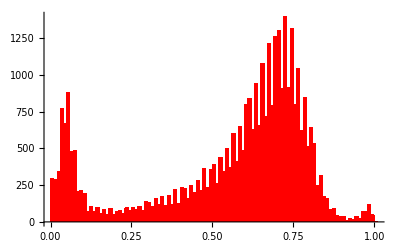

```mathematica
HP = Histogram[Flatten[ImageData[RH3]],100,ChartStyle ->Red]
```

```mathematica
{Slider[Dynamic[TreP]],Dynamic[TreP]}
```

{,}

```mathematica
Dynamic[Show[HP,ListPlot[{{TreP,0}},PlotStyle -> PointSize[0.06]]]]
```

```mathematica
{RH4 = Dynamic[Binarize[RH3,TreP]]}
```

{}

```mathematica
Export["riverb2.jpg",RH4]
```

riverb2.jpg

```mathematica
R5 = Import["Heavy_load_noisy.jpg"]
```

-Graphics-

```mathematica
RH5 = ColorConvert[R5,"Graylevel"]
```

-Graphics-

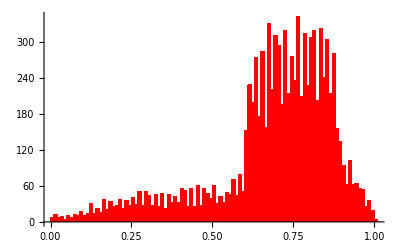

```mathematica
HP5 = Histogram[Flatten[ImageData[RH5]],100,ChartStyle ->Red]
```

```mathematica
{Slider[Dynamic[TreHL]],Dynamic[TreHL]}
```

{,}

```mathematica
Dynamic[Show[HP5,ListPlot[{{TreHL,0}},PlotStyle -> PointSize[0.06]]]]
```

```mathematica
{RHH5 = Dynamic[Binarize[RH5,TreHL]]}
```

{}

```mathematica
{T8 = Import["problem8.jpg"]}
```

{-Graphics-}

```mathematica
{T9 = ColorConvert[T8,"Graylevel"]}
```

{-Graphics-}

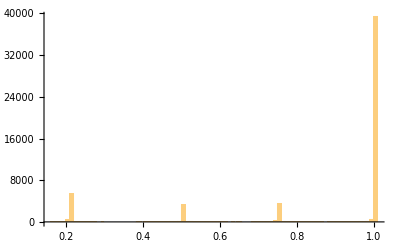

```mathematica
HP8 = Histogram[Flatten[ImageData[T9]],100]
```

```mathematica
{T91 = ColorNegate[Binarize[T9,{0.1,0.3}]]}
```

{-Graphics-}

```mathematica
{T92 = ColorNegate[Binarize[T9,{0.4,0.6}]]}
```

{-Graphics-}

```mathematica
{T93 = ColorNegate[Binarize[T9,{0.7,0.8}]]}
```

{-Graphics-}

```mathematica
{T9 = ImageMultiply[T4,0.5]}
```

{-Graphics-}

```mathematica
{T10 = ImageMultiply[T4,1.5]}
```

{-Graphics-}

```mathematica
{Mona = Import["mona_large.jpg"]}
```

{-Graphics-}

```mathematica
{MonaS = ColorSeparate[Mona]}
```

{{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
{MonaR = MonaS[[1]]}
```

{-Graphics-}

```mathematica
{MonaG = MonaS[[2]]}
```

{-Graphics-}

```mathematica
{MonaB = MonaS[[3]]}
```

{-Graphics-}

```mathematica
{MonaBnew = ImageMultiply[MonaB,2]}
```

{-Graphics-}

```mathematica
{MonaNew = ColorCombine[{MonaR,MonaG,MonaBnew}]}
```

{-Graphics-}

```mathematica
{Mona,MonaNew}
```

{-Graphics-,-Graphics-}

```mathematica
Export["MonaBnew.bmp",MonaBnew]
```

MonaBnew.bmp

```mathematica
f[x_]:= x^2
```

```mathematica
{Mona1 = Import["mona_large.jpg"]}
```

{-Graphics-}

```mathematica
{MonaNew1 = ImageApply[f,Mona1]}
```

{-Graphics-}

```mathematica
{Mona1,MonaNew1}
```

{-Graphics-,-Graphics-}

```mathematica
Export["Monaf.jpg",MonaNew1]
```

Monaf.jpg

```mathematica
{MonaEq = HistogramTransform[Mona]}
```

{-Graphics-}

```mathematica
{MonaRE,MonaGE,MonaBE} = ColorSeparate[MonaEq]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
DataBlue = ImageData[MonaB];
```

```mathematica
DataBlueEq = ImageData[MonaBE];
```

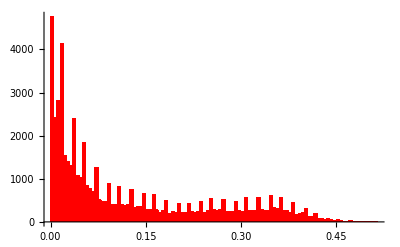

```mathematica
HBlue = Histogram[Flatten[DataBlue],100,ChartStyle->Red]
```

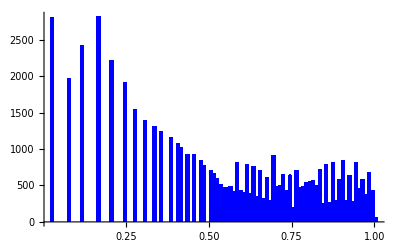

```mathematica
HBlueE = Histogram[Flatten[DataBlueEq],100,ChartStyle -> Blue]
```

```mathematica
{MonaG = Import["mona_large.jpg"]}
```

{-Graphics-}

```mathematica
{MonaGS = ColorSeparate[MonaG]}
```

{{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
{MonaGSS = MonaGS[[2]]}
```

{-Graphics-}

```mathematica
MonaGEq = HistogramTransform[MonaGSS]
```

-Graphics-

```mathematica
f2[x_] := Sin[10 x]
```

```mathematica
{MonaBnew = ImageApply[f2,MonaGSS]}
```

{-Graphics-}

```mathematica
{MonacomG = ColorCombine[{MonaR,MonaGEq ,MonaBnew}]}
```

{-Graphics-}

```mathematica
{P1 = Import["pill1.jpg"] , P2 = Import["pill2.jpg"]}
```

{-Graphics-,-Graphics-}

```mathematica
{PG1 = ColorConvert[P1,"graylevel"],PG2 = ColorConvert[P2,"graylevel"]}
```

{-Graphics-,-Graphics-}

```mathematica
DP1P2 = ImageDifference[PG1,PG2]
```

-Graphics-

```mathematica
ND = ColorNegate[DP1P2]
```

-Graphics-

```mathematica
I1 = Import["colorful.jpg"];
```

```mathematica
Magnify[I1,0.5]
```

-Graphics-

```mathematica
ImageDimensions[I1]
```

{251,247}

```mathematica
2484
```

2484

```mathematica
248/4
```

62

```mathematica
Magnify[IT1 = ImageCrop[I1,{248,248}],0.5]
```

-Graphics-

```mathematica
ImageDimensions[IT1]
```

{248,248}

```mathematica
ImageCrop[IT1,{100,100}]
```

-Graphics-

```mathematica
Magnify[ImagePartition[IT1,32]//Grid,0.5]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Magnify[ImagePartition[IT1,{248/2,248}],0.5]
```

{{-Graphics-,-Graphics-}}

```mathematica
Magnify[ImagePartition[IT1,{248,248/2}],0.5]
```

{{-Graphics-},{-Graphics-}}

```mathematica
Magnify[IT1,0.5]
```

-Graphics-

```mathematica
Magnify[S= ImagePartition[IT1,{248/4,248/4}],0.5]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
S[[1]][[1]]
```

-Graphics-

```mathematica
S[[2]][[1]]
```

-Graphics-

```mathematica
ImageAssemble[{S[[1]][[1]],S[[2]][[1]]}]
```

-Graphics-

```mathematica
ImageAssemble[{S[[1]][[1]],S[[3]][[4]]}]
```

-Graphics-

```mathematica
Pirat = Import["pirat.gif"]
```

-Graphics-

```mathematica
ImageDimensions[Pirat]
```

{300,180}

```mathematica
Magnify[Q=ImagePartition[Pirat,{300/2,180}],0.5]
```

{{-Graphics-,-Graphics-}}

```mathematica
pirat11 = Q[[1]][[1]]
```

-Graphics-

```mathematica
pirat12 =Q[[1]][[2]]
```

-Graphics-

```mathematica
pirat11g = ColorConvert[pirat11,"Grayscale"]
```

-Graphics-

```mathematica
pirat12g = ColorConvert[pirat12,"Grayscale"]
```

-Graphics-

```mathematica
DPirat = ImageDifference[pirat11g,pirat12g]
```

-Graphics-

```mathematica
piratND = ColorNegate[DPirat]
```

-Graphics-

```mathematica
Q
```

{{-Graphics-,-Graphics-}}

```mathematica
{Bu = Import["Bush.jpg"]}
```

{-Graphics-}

```mathematica
{Ar = Import["Arnold.jpg"]}
```

{-Graphics-}

```mathematica
Morph[t_] := ImageAdd[ImageMultiply[Bu,1-t],ImageMultiply[Ar,t]]
```

```mathematica
{Slider[Dynamic[s]],Dynamic[s]}
```

{,}

```mathematica
{Dynamic[Morph[s]]}
```

{}